```mathematica
<<HPL`
```

Package HPL already loaded...

$Aborted

```mathematica
<<HypExp`
```

*-*-*-*-*-* HPL 2.0 *-*-*-*-*-*

Author: Daniel Maitre, University of Zurich

Rules for minimal set loaded for weights: 2, 3, 4, 5, 6.

Rules for minimal set for + - weights loaded for weights: 2, 3, 4, 5, 6.

Table of MZVs loaded up to weight 6

Table of values at I loaded up to weight 6

$HPLFunctions gives a list of the functions of the package.
$HPLOptions gives a list of the options of the package.

More info in hep-ph/0507152, hep-ph/0703052 and at 
 http://krone.physik.unizh.ch/~maitreda/HPL/

***********************************
***********  HypExp 2.0  ************
***********************************
Authors:
 Tobias Huber:  RWTH Aachen,

Daniel Maitre: SLAC, University of Zurich.

HypExp loaded! It allows the expansion of hypergeometric functions around their parameters. 
 The new provided commands are:
 - HypExp
 - HypExpInt
 - HypExpU
 - HypExpAddToLib
 - HypExpIsKnownToOrder

More info in hep-ph/0507094 and at 
 http://krone.physik.unizh.ch/~maitreda/HypExp/

```mathematica
assmp1={km>0,kp>0,x>0,y>0,kperp>0,Q>0,τ>0,γe>0,1>δ>0,1>θ1>0,Subscript[Ω, 1-2ϵ]>0};
allangle=Subscript[Ω, d_]:>(2 π^(d/2))/Gamma[d/2];
```

#### Plus-dist (subtract divergence at x= 0)

```mathematica
(* ∫_0^1 ⅆx f(x)1/x^(1-λ) = ∫_0^1 ⅆx 1/x^(1-λ) (f(x)-f(0)+f(0))= f(0)∫_0^1 ⅆx/x^(1-λ) + ∫_0^1 ⅆx x^λ/x^1 (f(x)-f(0)) = f(0)∫_0^1 ⅆx/x^(1-λ) + ∫_0^1 ⅆx (∑_n λ^n/(n!)log^n(x))/x (f(x)-f(0))
            = f(0)∫_0^1 ⅆx/x^(1-λ) + ∫_0^1 ⅆx f(x)∑_n λ^n/(n!)Plusdist(n,x) *)

(*Plusdist(n,x) := δ_+^(n)(x) *)

(*x^(-1+a)log(x) = -1/a^2δ(x)+∑_(n=0)^5 a^n/(n!)δ_+^(n+1)(x),   x^(-1+a) = 1/a δ(x)+∑_(n=0)^5 a^n/(n!)δ_+^(n)(x)*)

(* f(x) δ_+^(n)(x) = (log^n(x))/x(f(x)-f(0)) *)

distExpl[x_]:={Log[x] x^(-1+a_)->-1/a^2 diracDelta[x]+Sum[a^n/(n!)PlusDist[n+1,x],{n,0,4}],x^(-1+a_)->1/a diracDelta[x]+Sum[a^n/(n!)PlusDist[n,x],{n,0,4}]};
distRules={a_ diracDelta[b_]:>(a/.b->0),a_ diracDelta'[b_]:>(-D[a,b]/.b->0),a_ PlusDist[n_,b_]:>Log[b]^n/b(a-(a/.b->0))};
DistApply[ex_,z_]:=Collect[ex,{diracDelta[z],diracDelta'[z],PlusDist[_,z]}]/.distRules
distRules2={a_ diracDelta[b_]:>(a/.b->0)diracDelta[b]};
DistApply2[ex_,z_]:=Collect[ex,{diracDelta[z],diracDelta'[z],PlusDist[_,z]}]/.distRules2
CollectColor[ex_]:=Collect[(ex//Expand)/.CF^2->CF2/.CF CA->CFCA/.CF nf TF->CFnfTF,{as,ios,CF,CA,CFCA,CF2,CFnfTF,Lβ,Lδ,Lτ,LQ,Lτδ,LQδ},Expand[Simplify[#]]&]/.CF2->CF^2/.CFCA->CF CA/.CFnfTF->CF nf TF/.Log[a_?NumberQ]:>Log[2](Log[a]/Log[2]//FullSimplify);
distRules3={a_ diracDelta[b_]:>(Normal@Series[a,{b,0,0},Assumptions->b>0]),a_ diracDelta'[b_]:>(-Normal@Series[D[a,b],{b,0,0},Assumptions->b>0]),a_ PlusDist[n_,b_]:>Log[b]^n/b(a-(Normal@Series[a,{b,0,0},Assumptions->b>0]))};
DistApply3[ex_,z_]:=Collect[ex,{diracDelta[z],diracDelta'[z],PlusDist[_,z]}]/.distRules3
```

#### 1-loop coft

```mathematica
(*int = (nbar.n1)/(k_- n1.k)=(n1_-)/(k_-((n_+k_-)/2+(n_-k_+)/2+ n_⊥.p_⊥))=1/(k_-((δ^2 θ1^2 k_-)/2+(k_+)/2+ |n_⊥||p_⊥|Cos[θ]))=1/(k_-((δ^2 θ1^2 k_-)/2+(k_+)/2+ δ θ1|k_⊥|Cos[θ]))*)
(*mesuare = 1/2 dk_+dk_-d^(2-2ϵ)k_⊥ δ^+(k^2) δ(Qβ-k_-) δ((k_+)/(k_-)-δ^2) = 1/2|k_⊥|^(1-2ϵ)Subscript[dΩ, 2-2ϵ] dk_+dk_-d|k_⊥| δ^+(|k_⊥|^2-k_+k_-) δ(Qβ-k_-) δ((k_+)/(k_-)-δ^2) = 1/4|k_⊥|^(-2ϵ) 2π Sin^(-2ϵ)[θ] dk_+dk_-δ(Qβ-k_-) δ((k_+)/(k_-)-δ^2) |_(|k_⊥|=√(k_+k_-))  *)
(*prefac = 1/(2π)^(3-2ϵ)*)
```

```mathematica
intgrand=2CF*1/4*1/(2π)^(3-2ϵ)*1/km*(2*Sin[θ]^(-2ϵ)*Subscript[Ω, 1-2ϵ])/(δ^2 θ1^2*km+kp-2 θ1 δ kperp Cos[θ])*E^(-km/(Q τ ))*kperp^(-2ϵ)/.kperp->√(km kp);
prefac=CF*(E^EulerGamma/(4π))^ϵ*(4π)^(-2+2 ϵ) Q^(-2 ϵ) δ^(-2 ϵ)  (1/τ)^(2 ϵ) ;

oldvar={kp,km};
newvar={x,y};
old2new={kp->Q δ^2 x/y,km-> Q  x};
jaco = Det@(D[oldvar/.old2new,#]&/@newvar);
constrant = HeavisideTheta[kp/km - δ^2];
InTconstrant=Simplify[#,Assumptions->assmp1]&@(constrant/.old2new/.HeavisideTheta[x_]:>x>0//Reduce)
```

y<1

```mathematica
(*Integrate x & Cos[θ]*)
```

```mathematica
Integrate[intgrand*jaco/.old2new//Simplify//PowerExpand,{x,0,∞},GenerateConditions->False]
```

(CF (2 π)^(-3+2 ϵ) Q^(-2 ϵ) y^(-1+ϵ) δ^(-2 ϵ) (1/τ)^(2 ϵ) Gamma[-2 ϵ] Sin[θ]^(-2 ϵ) Ω_(1-2 ϵ))/(1+y θ1^2-2 √y θ1 Cos[θ])

```mathematica
loop1result=Integrate[%,{θ,0,π},Assumptions->{0<y<1,0<θ1<1},GenerateConditions->False]/.allangle
```

(2^(-2+2 ϵ) CF π^(-3/2+1/2 (1-2 ϵ)+2 ϵ) Q^(-2 ϵ) y^(-1+ϵ) δ^(-2 ϵ) (1/τ)^(2 ϵ) Gamma[-2 ϵ] Hypergeometric2F1[1,1/2-ϵ,1-2 ϵ,(4 √y θ1)/(1+√y θ1)^2] Sec[π ϵ])/((1+√y θ1)^2 Gamma[1/2 (1-2 ϵ)] Gamma[1-ϵ] Gamma[1/2+ϵ])

```mathematica
(*y need to be int..., we just need ϵ-divergence term !*)
```

```mathematica
(*1st, expand 2F1*)
```

```mathematica
Simplify[#(*/.{Log[x_]:>Log[x//Together],PolyLog[n_,x_]:>PolyLog[n,x//Together]}*),Assumptions->{0<y<1,0<θ1<1}]&@((loop1result//FunctionExpand)/.Hypergeometric2F1[a_,b_,c_,d_]:>HypExp[ Hypergeometric2F1[a,b,c,d],ϵ,4]//Expand)
```

-1/(8 ϵ (-1+y θ1^2) Gamma[1/2+ϵ])CF π^(-3/2+ϵ) Q^(-2 ϵ) y^(-1+ϵ) δ^(-2 ϵ) (1/τ)^(2 ϵ) (-1+16 ϵ^4 HPL[{-4},√y θ1]+8 ϵ^3 HPL[{-3},√y θ1]+4 ϵ^2 HPL[{-2},√y θ1]+2 ϵ HPL[{-1},√y θ1]-2 ϵ HPL[{1},√y θ1]-4 ϵ^2 HPL[{2},√y θ1]-8 ϵ^3 HPL[{3},√y θ1]-16 ϵ^4 HPL[{4},√y θ1]-16 ϵ^4 HPL[{-3,-1},√y θ1]+16 ϵ^4 HPL[{-3,1},√y θ1]-16 ϵ^4 HPL[{-2,-2},√y θ1]-8 ϵ^3 HPL[{-2,-1},√y θ1]+8 ϵ^3 HPL[{-2,1},√y θ1]+16 ϵ^4 HPL[{-2,2},√y θ1]-16 ϵ^4 HPL[{-1,-3},√y θ1]-8 ϵ^3 HPL[{-1,-2},√y θ1]-4 ϵ^2 HPL[{-1,-1},√y θ1]+4 ϵ^2 HPL[{-1,1},√y θ1]+8 ϵ^3 HPL[{-1,2},√y θ1]+16 ϵ^4 HPL[{-1,3},√y θ1]+16 ϵ^4 HPL[{1,-3},√y θ1]+8 ϵ^3 HPL[{1,-2},√y θ1]+4 ϵ^2 HPL[{1,-1},√y θ1]-4 ϵ^2 HPL[{1,1},√y θ1]-8 ϵ^3 HPL[{1,2},√y θ1]-16 ϵ^4 HPL[{1,3},√y θ1]+16 ϵ^4 HPL[{2,-2},√y θ1]+8 ϵ^3 HPL[{2,-1},√y θ1]-8 ϵ^3 HPL[{2,1},√y θ1]-16 ϵ^4 HPL[{2,2},√y θ1]+16 ϵ^4 HPL[{3,-1},√y θ1]-16 ϵ^4 HPL[{3,1},√y θ1]+16 ϵ^4 HPL[{-2,-1,-1},√y θ1]-16 ϵ^4 HPL[{-2,-1,1},√y θ1]-16 ϵ^4 HPL[{-2,1,-1},√y θ1]+16 ϵ^4 HPL[{-2,1,1},√y θ1]+16 ϵ^4 HPL[{-1,-2,-1},√y θ1]-16 ϵ^4 HPL[{-1,-2,1},√y θ1]+16 ϵ^4 HPL[{-1,-1,-2},√y θ1]+8 ϵ^3 HPL[{-1,-1,-1},√y θ1]-8 ϵ^3 HPL[{-1,-1,1},√y θ1]-16 ϵ^4 HPL[{-1,-1,2},√y θ1]-16 ϵ^4 HPL[{-1,1,-2},√y θ1]-8 ϵ^3 HPL[{-1,1,-1},√y θ1]+8 ϵ^3 HPL[{-1,1,1},√y θ1]+16 ϵ^4 HPL[{-1,1,2},√y θ1]-16 ϵ^4 HPL[{-1,2,-1},√y θ1]+16 ϵ^4 HPL[{-1,2,1},√y θ1]-16 ϵ^4 HPL[{1,-2,-1},√y θ1]+16 ϵ^4 HPL[{1,-2,1},√y θ1]-16 ϵ^4 HPL[{1,-1,-2},√y θ1]-8 ϵ^3 HPL[{1,-1,-1},√y θ1]+8 ϵ^3 HPL[{1,-1,1},√y θ1]+16 ϵ^4 HPL[{1,-1,2},√y θ1]+16 ϵ^4 HPL[{1,1,-2},√y θ1]+8 ϵ^3 HPL[{1,1,-1},√y θ1]-8 ϵ^3 HPL[{1,1,1},√y θ1]-16 ϵ^4 HPL[{1,1,2},√y θ1]+16 ϵ^4 HPL[{1,2,-1},√y θ1]-16 ϵ^4 HPL[{1,2,1},√y θ1]-16 ϵ^4 HPL[{2,-1,-1},√y θ1]+16 ϵ^4 HPL[{2,-1,1},√y θ1]+16 ϵ^4 HPL[{2,1,-1},√y θ1]-16 ϵ^4 HPL[{2,1,1},√y θ1]-16 ϵ^4 HPL[{-1,-1,-1,-1},√y θ1]+16 ϵ^4 HPL[{-1,-1,-1,1},√y θ1]+16 ϵ^4 HPL[{-1,-1,1,-1},√y θ1]-16 ϵ^4 HPL[{-1,-1,1,1},√y θ1]+16 ϵ^4 HPL[{-1,1,-1,-1},√y θ1]-16 ϵ^4 HPL[{-1,1,-1,1},√y θ1]-16 ϵ^4 HPL[{-1,1,1,-1},√y θ1]+16 ϵ^4 HPL[{-1,1,1,1},√y θ1]+16 ϵ^4 HPL[{1,-1,-1,-1},√y θ1]-16 ϵ^4 HPL[{1,-1,-1,1},√y θ1]-16 ϵ^4 HPL[{1,-1,1,-1},√y θ1]+16 ϵ^4 HPL[{1,-1,1,1},√y θ1]-16 ϵ^4 HPL[{1,1,-1,-1},√y θ1]+16 ϵ^4 HPL[{1,1,-1,1},√y θ1]+16 ϵ^4 HPL[{1,1,1,-1},√y θ1]-16 ϵ^4 HPL[{1,1,1,1},√y θ1]) Sec[π ϵ]

```mathematica
(*2nd, use puls-dist*)
```

```mathematica
loop1ResultWithϵ=(Series[(DistApply[#,y]&@((%/prefac//Expand)/.distExpl[y])),{ϵ,0,4}]//Expand//Normal)/.ϵ^a_:>0/;a>=4
```

-2/ϵ^2+(2 θ1^2 Log[y])/(-1+y θ1^2)-(2 (EulerGamma y θ1^2+2 HPL[{-1},√y θ1]-2 HPL[{1},√y θ1]+2 y θ1^2 Log[2]+y θ1^2 PolyGamma[0,1/2]))/(y (-1+y θ1^2))+1/2 (-2 EulerGamma^2-π^2-8 EulerGamma Log[2]-8 Log[2]^2-4 EulerGamma PolyGamma[0,1/2]-8 Log[2] PolyGamma[0,1/2]-2 PolyGamma[0,1/2]^2)+((2 θ1^2)/(-1+y θ1^2)+2 (EulerGamma+2 Log[2]+PolyGamma[0,1/2]))/ϵ+ϵ ((θ1^2 Log[y]^2)/(-1+y θ1^2)-(2 Log[y] (EulerGamma y θ1^2+2 HPL[{-1},√y θ1]-2 HPL[{1},√y θ1]+2 y θ1^2 Log[2]+y θ1^2 PolyGamma[0,1/2]))/(y (-1+y θ1^2))+1/(2 y (-1+y θ1^2))(2 EulerGamma^2 y θ1^2+π^2 y θ1^2-16 HPL[{-2},√y θ1]+8 EulerGamma HPL[{-1},√y θ1]-8 EulerGamma HPL[{1},√y θ1]+16 HPL[{2},√y θ1]+16 HPL[{-1,-1},√y θ1]-16 HPL[{-1,1},√y θ1]-16 HPL[{1,-1},√y θ1]+16 HPL[{1,1},√y θ1]+8 EulerGamma y θ1^2 Log[2]+16 HPL[{-1},√y θ1] Log[2]-16 HPL[{1},√y θ1] Log[2]+8 y θ1^2 Log[2]^2+4 EulerGamma y θ1^2 PolyGamma[0,1/2]+8 HPL[{-1},√y θ1] PolyGamma[0,1/2]-8 HPL[{1},√y θ1] PolyGamma[0,1/2]+8 y θ1^2 Log[2] PolyGamma[0,1/2]+2 y θ1^2 PolyGamma[0,1/2]^2)+√π (-(-EulerGamma^3/3-2 EulerGamma^2 Log[2]-4 EulerGamma Log[2]^2-(8 Log[2]^3)/3)/(√π)+((EulerGamma^2+4 EulerGamma Log[2]+4 Log[2]^2) PolyGamma[0,1/2])/(√π)-1/2 π^2 ((-2 EulerGamma-4 Log[2])/(√π)-(2 PolyGamma[0,1/2])/(√π))-((-2 EulerGamma-4 Log[2]) (-π^2+2 PolyGamma[0,1/2]^2))/(4 √π)-(2 (1/4 π^2 PolyGamma[0,1/2]-1/6 PolyGamma[0,1/2]^3-1/6 PolyGamma[2,1/2]))/(√π)))+ϵ^2 ((θ1^2 Log[y]^3)/(3 (-1+y θ1^2))-(Log[y]^2 (EulerGamma y θ1^2+2 HPL[{-1},√y θ1]-2 HPL[{1},√y θ1]+2 y θ1^2 Log[2]+y θ1^2 PolyGamma[0,1/2]))/(y (-1+y θ1^2))+1/(2 y (-1+y θ1^2))Log[y] (2 EulerGamma^2 y θ1^2+π^2 y θ1^2-16 HPL[{-2},√y θ1]+8 EulerGamma HPL[{-1},√y θ1]-8 EulerGamma HPL[{1},√y θ1]+16 HPL[{2},√y θ1]+16 HPL[{-1,-1},√y θ1]-16 HPL[{-1,1},√y θ1]-16 HPL[{1,-1},√y θ1]+16 HPL[{1,1},√y θ1]+8 EulerGamma y θ1^2 Log[2]+16 HPL[{-1},√y θ1] Log[2]-16 HPL[{1},√y θ1] Log[2]+8 y θ1^2 Log[2]^2+4 EulerGamma y θ1^2 PolyGamma[0,1/2]+8 HPL[{-1},√y θ1] PolyGamma[0,1/2]-8 HPL[{1},√y θ1] PolyGamma[0,1/2]+8 y θ1^2 Log[2] PolyGamma[0,1/2]+2 y θ1^2 PolyGamma[0,1/2]^2)+1/(6 y (-1+y θ1^2))(-2 EulerGamma^3 y θ1^2-3 EulerGamma π^2 y θ1^2-96 HPL[{-3},√y θ1]+48 EulerGamma HPL[{-2},√y θ1]-12 EulerGamma^2 HPL[{-1},√y θ1]-6 π^2 HPL[{-1},√y θ1]+12 EulerGamma^2 HPL[{1},√y θ1]+6 π^2 HPL[{1},√y θ1]-48 EulerGamma HPL[{2},√y θ1]+96 HPL[{3},√y θ1]+96 HPL[{-2,-1},√y θ1]-96 HPL[{-2,1},√y θ1]+96 HPL[{-1,-2},√y θ1]-48 EulerGamma HPL[{-1,-1},√y θ1]+48 EulerGamma HPL[{-1,1},√y θ1]-96 HPL[{-1,2},√y θ1]-96 HPL[{1,-2},√y θ1]+48 EulerGamma HPL[{1,-1},√y θ1]-48 EulerGamma HPL[{1,1},√y θ1]+96 HPL[{1,2},√y θ1]-96 HPL[{2,-1},√y θ1]+96 HPL[{2,1},√y θ1]-96 HPL[{-1,-1,-1},√y θ1]+96 HPL[{-1,-1,1},√y θ1]+96 HPL[{-1,1,-1},√y θ1]-96 HPL[{-1,1,1},√y θ1]+96 HPL[{1,-1,-1},√y θ1]-96 HPL[{1,-1,1},√y θ1]-96 HPL[{1,1,-1},√y θ1]+96 HPL[{1,1,1},√y θ1]-12 EulerGamma^2 y θ1^2 Log[2]-6 π^2 y θ1^2 Log[2]+96 HPL[{-2},√y θ1] Log[2]-48 EulerGamma HPL[{-1},√y θ1] Log[2]+48 EulerGamma HPL[{1},√y θ1] Log[2]-96 HPL[{2},√y θ1] Log[2]-96 HPL[{-1,-1},√y θ1] Log[2]+96 HPL[{-1,1},√y θ1] Log[2]+96 HPL[{1,-1},√y θ1] Log[2]-96 HPL[{1,1},√y θ1] Log[2]-24 EulerGamma y θ1^2 Log[2]^2-48 HPL[{-1},√y θ1] Log[2]^2+48 HPL[{1},√y θ1] Log[2]^2-16 y θ1^2 Log[2]^3-6 EulerGamma^2 y θ1^2 PolyGamma[0,1/2]-3 π^2 y θ1^2 PolyGamma[0,1/2]+48 HPL[{-2},√y θ1] PolyGamma[0,1/2]-24 EulerGamma HPL[{-1},√y θ1] PolyGamma[0,1/2]+24 EulerGamma HPL[{1},√y θ1] PolyGamma[0,1/2]-48 HPL[{2},√y θ1] PolyGamma[0,1/2]-48 HPL[{-1,-1},√y θ1] PolyGamma[0,1/2]+48 HPL[{-1,1},√y θ1] PolyGamma[0,1/2]+48 HPL[{1,-1},√y θ1] PolyGamma[0,1/2]-48 HPL[{1,1},√y θ1] PolyGamma[0,1/2]-24 EulerGamma y θ1^2 Log[2] PolyGamma[0,1/2]-48 HPL[{-1},√y θ1] Log[2] PolyGamma[0,1/2]+48 HPL[{1},√y θ1] Log[2] PolyGamma[0,1/2]-24 y θ1^2 Log[2]^2 PolyGamma[0,1/2]-6 EulerGamma y θ1^2 PolyGamma[0,1/2]^2-12 HPL[{-1},√y θ1] PolyGamma[0,1/2]^2+12 HPL[{1},√y θ1] PolyGamma[0,1/2]^2-12 y θ1^2 Log[2] PolyGamma[0,1/2]^2-2 y θ1^2 PolyGamma[0,1/2]^3-2 y θ1^2 PolyGamma[2,1/2])+√π (-(5 π^(7/2))/12-(EulerGamma^4/12+2/3 EulerGamma^3 Log[2]+2 EulerGamma^2 Log[2]^2+8/3 EulerGamma Log[2]^3+(4 Log[2]^4)/3)/(√π)+((-EulerGamma^3/3-2 EulerGamma^2 Log[2]-4 EulerGamma Log[2]^2-(8 Log[2]^3)/3) PolyGamma[0,1/2])/(√π)-((EulerGamma^2+4 EulerGamma Log[2]+4 Log[2]^2) (-π^2+2 PolyGamma[0,1/2]^2))/(4 √π)-1/2 π^2 ((EulerGamma^2+4 EulerGamma Log[2]+4 Log[2]^2)/(√π)-((-2 EulerGamma-4 Log[2]) PolyGamma[0,1/2])/(√π)+(-π^2+2 PolyGamma[0,1/2]^2)/(2 √π))-((-2 EulerGamma-4 Log[2]) (1/4 π^2 PolyGamma[0,1/2]-1/6 PolyGamma[0,1/2]^3-1/6 PolyGamma[2,1/2]))/(√π)-(2 (-π^4/96-1/8 π^2 PolyGamma[0,1/2]^2+1/24 PolyGamma[0,1/2]^4+1/6 PolyGamma[0,1/2] PolyGamma[2,1/2]))/(√π)))+ϵ^3 ((θ1^2 Log[y]^4)/(12 (-1+y θ1^2))-(Log[y]^3 (EulerGamma y θ1^2+2 HPL[{-1},√y θ1]-2 HPL[{1},√y θ1]+2 y θ1^2 Log[2]+y θ1^2 PolyGamma[0,1/2]))/(3 y (-1+y θ1^2))+1/(4 y (-1+y θ1^2))Log[y]^2 (2 EulerGamma^2 y θ1^2+π^2 y θ1^2-16 HPL[{-2},√y θ1]+8 EulerGamma HPL[{-1},√y θ1]-8 EulerGamma HPL[{1},√y θ1]+16 HPL[{2},√y θ1]+16 HPL[{-1,-1},√y θ1]-16 HPL[{-1,1},√y θ1]-16 HPL[{1,-1},√y θ1]+16 HPL[{1,1},√y θ1]+8 EulerGamma y θ1^2 Log[2]+16 HPL[{-1},√y θ1] Log[2]-16 HPL[{1},√y θ1] Log[2]+8 y θ1^2 Log[2]^2+4 EulerGamma y θ1^2 PolyGamma[0,1/2]+8 HPL[{-1},√y θ1] PolyGamma[0,1/2]-8 HPL[{1},√y θ1] PolyGamma[0,1/2]+8 y θ1^2 Log[2] PolyGamma[0,1/2]+2 y θ1^2 PolyGamma[0,1/2]^2)+1/(6 y (-1+y θ1^2))Log[y] (-2 EulerGamma^3 y θ1^2-3 EulerGamma π^2 y θ1^2-96 HPL[{-3},√y θ1]+48 EulerGamma HPL[{-2},√y θ1]-12 EulerGamma^2 HPL[{-1},√y θ1]-6 π^2 HPL[{-1},√y θ1]+12 EulerGamma^2 HPL[{1},√y θ1]+6 π^2 HPL[{1},√y θ1]-48 EulerGamma HPL[{2},√y θ1]+96 HPL[{3},√y θ1]+96 HPL[{-2,-1},√y θ1]-96 HPL[{-2,1},√y θ1]+96 HPL[{-1,-2},√y θ1]-48 EulerGamma HPL[{-1,-1},√y θ1]+48 EulerGamma HPL[{-1,1},√y θ1]-96 HPL[{-1,2},√y θ1]-96 HPL[{1,-2},√y θ1]+48 EulerGamma HPL[{1,-1},√y θ1]-48 EulerGamma HPL[{1,1},√y θ1]+96 HPL[{1,2},√y θ1]-96 HPL[{2,-1},√y θ1]+96 HPL[{2,1},√y θ1]-96 HPL[{-1,-1,-1},√y θ1]+96 HPL[{-1,-1,1},√y θ1]+96 HPL[{-1,1,-1},√y θ1]-96 HPL[{-1,1,1},√y θ1]+96 HPL[{1,-1,-1},√y θ1]-96 HPL[{1,-1,1},√y θ1]-96 HPL[{1,1,-1},√y θ1]+96 HPL[{1,1,1},√y θ1]-12 EulerGamma^2 y θ1^2 Log[2]-6 π^2 y θ1^2 Log[2]+96 HPL[{-2},√y θ1] Log[2]-48 EulerGamma HPL[{-1},√y θ1] Log[2]+48 EulerGamma HPL[{1},√y θ1] Log[2]-96 HPL[{2},√y θ1] Log[2]-96 HPL[{-1,-1},√y θ1] Log[2]+96 HPL[{-1,1},√y θ1] Log[2]+96 HPL[{1,-1},√y θ1] Log[2]-96 HPL[{1,1},√y θ1] Log[2]-24 EulerGamma y θ1^2 Log[2]^2-48 HPL[{-1},√y θ1] Log[2]^2+48 HPL[{1},√y θ1] Log[2]^2-16 y θ1^2 Log[2]^3-6 EulerGamma^2 y θ1^2 PolyGamma[0,1/2]-3 π^2 y θ1^2 PolyGamma[0,1/2]+48 HPL[{-2},√y θ1] PolyGamma[0,1/2]-24 EulerGamma HPL[{-1},√y θ1] PolyGamma[0,1/2]+24 EulerGamma HPL[{1},√y θ1] PolyGamma[0,1/2]-48 HPL[{2},√y θ1] PolyGamma[0,1/2]-48 HPL[{-1,-1},√y θ1] PolyGamma[0,1/2]+48 HPL[{-1,1},√y θ1] PolyGamma[0,1/2]+48 HPL[{1,-1},√y θ1] PolyGamma[0,1/2]-48 HPL[{1,1},√y θ1] PolyGamma[0,1/2]-24 EulerGamma y θ1^2 Log[2] PolyGamma[0,1/2]-48 HPL[{-1},√y θ1] Log[2] PolyGamma[0,1/2]+48 HPL[{1},√y θ1] Log[2] PolyGamma[0,1/2]-24 y θ1^2 Log[2]^2 PolyGamma[0,1/2]-6 EulerGamma y θ1^2 PolyGamma[0,1/2]^2-12 HPL[{-1},√y θ1] PolyGamma[0,1/2]^2+12 HPL[{1},√y θ1] PolyGamma[0,1/2]^2-12 y θ1^2 Log[2] PolyGamma[0,1/2]^2-2 y θ1^2 PolyGamma[0,1/2]^3-2 y θ1^2 PolyGamma[2,1/2])+1/y(-(32 HPL[{-4},√y θ1])/(-1+y θ1^2)+(32 HPL[{4},√y θ1])/(-1+y θ1^2)+(32 HPL[{-3,-1},√y θ1])/(-1+y θ1^2)-(32 HPL[{-3,1},√y θ1])/(-1+y θ1^2)+(32 HPL[{-2,-2},√y θ1])/(-1+y θ1^2)-(32 HPL[{-2,2},√y θ1])/(-1+y θ1^2)+(32 HPL[{-1,-3},√y θ1])/(-1+y θ1^2)-(32 HPL[{-1,3},√y θ1])/(-1+y θ1^2)-(32 HPL[{1,-3},√y θ1])/(-1+y θ1^2)+(32 HPL[{1,3},√y θ1])/(-1+y θ1^2)-(32 HPL[{2,-2},√y θ1])/(-1+y θ1^2)+(32 HPL[{2,2},√y θ1])/(-1+y θ1^2)-(32 HPL[{3,-1},√y θ1])/(-1+y θ1^2)+(32 HPL[{3,1},√y θ1])/(-1+y θ1^2)-(32 HPL[{-2,-1,-1},√y θ1])/(-1+y θ1^2)+(32 HPL[{-2,-1,1},√y θ1])/(-1+y θ1^2)+(32 HPL[{-2,1,-1},√y θ1])/(-1+y θ1^2)-(32 HPL[{-2,1,1},√y θ1])/(-1+y θ1^2)-(32 HPL[{-1,-2,-1},√y θ1])/(-1+y θ1^2)+(32 HPL[{-1,-2,1},√y θ1])/(-1+y θ1^2)-(32 HPL[{-1,-1,-2},√y θ1])/(-1+y θ1^2)+(32 HPL[{-1,-1,2},√y θ1])/(-1+y θ1^2)+(32 HPL[{-1,1,-2},√y θ1])/(-1+y θ1^2)-(32 HPL[{-1,1,2},√y θ1])/(-1+y θ1^2)+(32 HPL[{-1,2,-1},√y θ1])/(-1+y θ1^2)-(32 HPL[{-1,2,1},√y θ1])/(-1+y θ1^2)+(32 HPL[{1,-2,-1},√y θ1])/(-1+y θ1^2)-(32 HPL[{1,-2,1},√y θ1])/(-1+y θ1^2)+(32 HPL[{1,-1,-2},√y θ1])/(-1+y θ1^2)-(32 HPL[{1,-1,2},√y θ1])/(-1+y θ1^2)-(32 HPL[{1,1,-2},√y θ1])/(-1+y θ1^2)+(32 HPL[{1,1,2},√y θ1])/(-1+y θ1^2)-(32 HPL[{1,2,-1},√y θ1])/(-1+y θ1^2)+(32 HPL[{1,2,1},√y θ1])/(-1+y θ1^2)+(32 HPL[{2,-1,-1},√y θ1])/(-1+y θ1^2)-(32 HPL[{2,-1,1},√y θ1])/(-1+y θ1^2)-(32 HPL[{2,1,-1},√y θ1])/(-1+y θ1^2)+(32 HPL[{2,1,1},√y θ1])/(-1+y θ1^2)+(32 HPL[{-1,-1,-1,-1},√y θ1])/(-1+y θ1^2)-(32 HPL[{-1,-1,-1,1},√y θ1])/(-1+y θ1^2)-(32 HPL[{-1,-1,1,-1},√y θ1])/(-1+y θ1^2)+(32 HPL[{-1,-1,1,1},√y θ1])/(-1+y θ1^2)-(32 HPL[{-1,1,-1,-1},√y θ1])/(-1+y θ1^2)+(32 HPL[{-1,1,-1,1},√y θ1])/(-1+y θ1^2)+(32 HPL[{-1,1,1,-1},√y θ1])/(-1+y θ1^2)-(32 HPL[{-1,1,1,1},√y θ1])/(-1+y θ1^2)-(32 HPL[{1,-1,-1,-1},√y θ1])/(-1+y θ1^2)+(32 HPL[{1,-1,-1,1},√y θ1])/(-1+y θ1^2)+(32 HPL[{1,-1,1,-1},√y θ1])/(-1+y θ1^2)-(32 HPL[{1,-1,1,1},√y θ1])/(-1+y θ1^2)+(32 HPL[{1,1,-1,-1},√y θ1])/(-1+y θ1^2)-(32 HPL[{1,1,-1,1},√y θ1])/(-1+y θ1^2)-(32 HPL[{1,1,1,-1},√y θ1])/(-1+y θ1^2)+(32 HPL[{1,1,1,1},√y θ1])/(-1+y θ1^2)+(16 HPL[{-3},√y θ1] (EulerGamma+2 Log[2]+PolyGamma[0,1/2]))/(-1+y θ1^2)-(16 HPL[{3},√y θ1] (EulerGamma+2 Log[2]+PolyGamma[0,1/2]))/(-1+y θ1^2)-(16 HPL[{-2,-1},√y θ1] (EulerGamma+2 Log[2]+PolyGamma[0,1/2]))/(-1+y θ1^2)+(16 HPL[{-2,1},√y θ1] (EulerGamma+2 Log[2]+PolyGamma[0,1/2]))/(-1+y θ1^2)-(16 HPL[{-1,-2},√y θ1] (EulerGamma+2 Log[2]+PolyGamma[0,1/2]))/(-1+y θ1^2)+(16 HPL[{-1,2},√y θ1] (EulerGamma+2 Log[2]+PolyGamma[0,1/2]))/(-1+y θ1^2)+(16 HPL[{1,-2},√y θ1] (EulerGamma+2 Log[2]+PolyGamma[0,1/2]))/(-1+y θ1^2)-(16 HPL[{1,2},√y θ1] (EulerGamma+2 Log[2]+PolyGamma[0,1/2]))/(-1+y θ1^2)+(16 HPL[{2,-1},√y θ1] (EulerGamma+2 Log[2]+PolyGamma[0,1/2]))/(-1+y θ1^2)-(16 HPL[{2,1},√y θ1] (EulerGamma+2 Log[2]+PolyGamma[0,1/2]))/(-1+y θ1^2)+(16 HPL[{-1,-1,-1},√y θ1] (EulerGamma+2 Log[2]+PolyGamma[0,1/2]))/(-1+y θ1^2)-(16 HPL[{-1,-1,1},√y θ1] (EulerGamma+2 Log[2]+PolyGamma[0,1/2]))/(-1+y θ1^2)-(16 HPL[{-1,1,-1},√y θ1] (EulerGamma+2 Log[2]+PolyGamma[0,1/2]))/(-1+y θ1^2)+(16 HPL[{-1,1,1},√y θ1] (EulerGamma+2 Log[2]+PolyGamma[0,1/2]))/(-1+y θ1^2)-(16 HPL[{1,-1,-1},√y θ1] (EulerGamma+2 Log[2]+PolyGamma[0,1/2]))/(-1+y θ1^2)+(16 HPL[{1,-1,1},√y θ1] (EulerGamma+2 Log[2]+PolyGamma[0,1/2]))/(-1+y θ1^2)+(16 HPL[{1,1,-1},√y θ1] (EulerGamma+2 Log[2]+PolyGamma[0,1/2]))/(-1+y θ1^2)-(16 HPL[{1,1,1},√y θ1] (EulerGamma+2 Log[2]+PolyGamma[0,1/2]))/(-1+y θ1^2)-(2 HPL[{-2},√y θ1] (2 EulerGamma^2+π^2+8 EulerGamma Log[2]+8 Log[2]^2+4 EulerGamma PolyGamma[0,1/2]+8 Log[2] PolyGamma[0,1/2]+2 PolyGamma[0,1/2]^2))/(-1+y θ1^2)+(2 HPL[{2},√y θ1] (2 EulerGamma^2+π^2+8 EulerGamma Log[2]+8 Log[2]^2+4 EulerGamma PolyGamma[0,1/2]+8 Log[2] PolyGamma[0,1/2]+2 PolyGamma[0,1/2]^2))/(-1+y θ1^2)+(2 HPL[{-1,-1},√y θ1] (2 EulerGamma^2+π^2+8 EulerGamma Log[2]+8 Log[2]^2+4 EulerGamma PolyGamma[0,1/2]+8 Log[2] PolyGamma[0,1/2]+2 PolyGamma[0,1/2]^2))/(-1+y θ1^2)-(2 HPL[{-1,1},√y θ1] (2 EulerGamma^2+π^2+8 EulerGamma Log[2]+8 Log[2]^2+4 EulerGamma PolyGamma[0,1/2]+8 Log[2] PolyGamma[0,1/2]+2 PolyGamma[0,1/2]^2))/(-1+y θ1^2)-(2 HPL[{1,-1},√y θ1] (2 EulerGamma^2+π^2+8 EulerGamma Log[2]+8 Log[2]^2+4 EulerGamma PolyGamma[0,1/2]+8 Log[2] PolyGamma[0,1/2]+2 PolyGamma[0,1/2]^2))/(-1+y θ1^2)+(2 HPL[{1,1},√y θ1] (2 EulerGamma^2+π^2+8 EulerGamma Log[2]+8 Log[2]^2+4 EulerGamma PolyGamma[0,1/2]+8 Log[2] PolyGamma[0,1/2]+2 PolyGamma[0,1/2]^2))/(-1+y θ1^2)+1/(3 (-1+y θ1^2))HPL[{-1},√y θ1] (2 EulerGamma^3+3 EulerGamma π^2+12 EulerGamma^2 Log[2]+6 π^2 Log[2]+24 EulerGamma Log[2]^2+16 Log[2]^3+6 EulerGamma^2 PolyGamma[0,1/2]+3 π^2 PolyGamma[0,1/2]+24 EulerGamma Log[2] PolyGamma[0,1/2]+24 Log[2]^2 PolyGamma[0,1/2]+6 EulerGamma PolyGamma[0,1/2]^2+12 Log[2] PolyGamma[0,1/2]^2+2 PolyGamma[0,1/2]^3+2 PolyGamma[2,1/2])-1/(3 (-1+y θ1^2))HPL[{1},√y θ1] (2 EulerGamma^3+3 EulerGamma π^2+12 EulerGamma^2 Log[2]+6 π^2 Log[2]+24 EulerGamma Log[2]^2+16 Log[2]^3+6 EulerGamma^2 PolyGamma[0,1/2]+3 π^2 PolyGamma[0,1/2]+24 EulerGamma Log[2] PolyGamma[0,1/2]+24 Log[2]^2 PolyGamma[0,1/2]+6 EulerGamma PolyGamma[0,1/2]^2+12 Log[2] PolyGamma[0,1/2]^2+2 PolyGamma[0,1/2]^3+2 PolyGamma[2,1/2])+1/48 (4 EulerGamma^4+12 EulerGamma^2 π^2+7 π^4+32 EulerGamma^3 Log[2]+48 EulerGamma π^2 Log[2]+96 EulerGamma^2 Log[2]^2+48 π^2 Log[2]^2+128 EulerGamma Log[2]^3+64 Log[2]^4+16 EulerGamma^3 PolyGamma[0,1/2]+24 EulerGamma π^2 PolyGamma[0,1/2]+96 EulerGamma^2 Log[2] PolyGamma[0,1/2]+48 π^2 Log[2] PolyGamma[0,1/2]+192 EulerGamma Log[2]^2 PolyGamma[0,1/2]+128 Log[2]^3 PolyGamma[0,1/2]+24 EulerGamma^2 PolyGamma[0,1/2]^2+12 π^2 PolyGamma[0,1/2]^2+96 EulerGamma Log[2] PolyGamma[0,1/2]^2+96 Log[2]^2 PolyGamma[0,1/2]^2+16 EulerGamma PolyGamma[0,1/2]^3+32 Log[2] PolyGamma[0,1/2]^3+4 PolyGamma[0,1/2]^4+16 EulerGamma PolyGamma[2,1/2]+32 Log[2] PolyGamma[2,1/2]+16 PolyGamma[0,1/2] PolyGamma[2,1/2])+1/(48 (-1+y θ1^2))(4 EulerGamma^4+12 EulerGamma^2 π^2+7 π^4+32 EulerGamma^3 Log[2]+48 EulerGamma π^2 Log[2]+96 EulerGamma^2 Log[2]^2+48 π^2 Log[2]^2+128 EulerGamma Log[2]^3+64 Log[2]^4+16 EulerGamma^3 PolyGamma[0,1/2]+24 EulerGamma π^2 PolyGamma[0,1/2]+96 EulerGamma^2 Log[2] PolyGamma[0,1/2]+48 π^2 Log[2] PolyGamma[0,1/2]+192 EulerGamma Log[2]^2 PolyGamma[0,1/2]+128 Log[2]^3 PolyGamma[0,1/2]+24 EulerGamma^2 PolyGamma[0,1/2]^2+12 π^2 PolyGamma[0,1/2]^2+96 EulerGamma Log[2] PolyGamma[0,1/2]^2+96 Log[2]^2 PolyGamma[0,1/2]^2+16 EulerGamma PolyGamma[0,1/2]^3+32 Log[2] PolyGamma[0,1/2]^3+4 PolyGamma[0,1/2]^4+16 EulerGamma PolyGamma[2,1/2]+32 Log[2] PolyGamma[2,1/2]+16 PolyGamma[0,1/2] PolyGamma[2,1/2]))+√π (-(-EulerGamma^5/60-1/6 EulerGamma^4 Log[2]-2/3 EulerGamma^3 Log[2]^2-4/3 EulerGamma^2 Log[2]^3-4/3 EulerGamma Log[2]^4-(8 Log[2]^5)/15)/(√π)+((EulerGamma^4/12+2/3 EulerGamma^3 Log[2]+2 EulerGamma^2 Log[2]^2+8/3 EulerGamma Log[2]^3+(4 Log[2]^4)/3) PolyGamma[0,1/2])/(√π)-5/24 π^4 ((-2 EulerGamma-4 Log[2])/(√π)-(2 PolyGamma[0,1/2])/(√π))-((-EulerGamma^3/3-2 EulerGamma^2 Log[2]-4 EulerGamma Log[2]^2-(8 Log[2]^3)/3) (-π^2+2 PolyGamma[0,1/2]^2))/(4 √π)-1/2 π^2 ((-EulerGamma^3/3-2 EulerGamma^2 Log[2]-4 EulerGamma Log[2]^2-(8 Log[2]^3)/3)/(√π)-((EulerGamma^2+4 EulerGamma Log[2]+4 Log[2]^2) PolyGamma[0,1/2])/(√π)+((-2 EulerGamma-4 Log[2]) (-π^2+2 PolyGamma[0,1/2]^2))/(4 √π)+(2 (1/4 π^2 PolyGamma[0,1/2]-1/6 PolyGamma[0,1/2]^3-1/6 PolyGamma[2,1/2]))/(√π))-((EulerGamma^2+4 EulerGamma Log[2]+4 Log[2]^2) (1/4 π^2 PolyGamma[0,1/2]-1/6 PolyGamma[0,1/2]^3-1/6 PolyGamma[2,1/2]))/(√π)-((-2 EulerGamma-4 Log[2]) (-π^4/96-1/8 π^2 PolyGamma[0,1/2]^2+1/24 PolyGamma[0,1/2]^4+1/6 PolyGamma[0,1/2] PolyGamma[2,1/2]))/(√π)-(2 (1/96 π^4 PolyGamma[0,1/2]+1/24 π^2 PolyGamma[0,1/2]^3-1/120 PolyGamma[0,1/2]^5+1/24 π^2 PolyGamma[2,1/2]-1/12 PolyGamma[0,1/2]^2 PolyGamma[2,1/2]-1/120 PolyGamma[4,1/2]))/(√π)))

```mathematica
(*ϵ^-2*)
Coefficient[  loop1ResultWithϵ//Expand,ϵ,-2]//. a_*Log[x_]+a_*Log[y_]:>a Log[x y//Expand]//Simplify;
Integrate[#,{y,0,1},Assumptions->0<θ1<1]&@%
```

-2

```mathematica
(*ϵ^-1*)
Coefficient[  loop1ResultWithϵ//Expand,ϵ,-1]//. a_*Log[x_]+a_*Log[y_]:>a Log[x y//Expand]//Simplify;
Integrate[#,{y,0,1},Assumptions->0<θ1<1]&@%
```

2 Log[1-θ1^2]

```mathematica
(*ϵ^0*)
```

```mathematica
Coefficient[ ϵ loop1ResultWithϵ//Expand,ϵ,1]//. a_*Log[x_]+a_*Log[y_]:>a Log[x y//Expand]//Simplify;
Integrate[#,{y,0,1},Assumptions->0<θ1<1]&@%
```

-π^2/2-2 Log[1-θ1^2]^2-2 PolyLog[2,θ1^2]

```mathematica
(*ϵ^1*)
Coefficient[  loop1ResultWithϵ//Expand,ϵ,1]//. a_*Log[x_]+a_*Log[y_]:>a Log[x y//Expand]//Simplify
(*Integrate[#,{y,0,1},Assumptions->0<θ1<1]&@%*)
```

1/(6 y (-1+y θ1^2))(8 π^2-2 EulerGamma^3 y-3 EulerGamma π^2 y+6 EulerGamma^2 y θ1^2+3 π^2 y θ1^2+2 EulerGamma^3 y^2 θ1^2+3 EulerGamma π^2 y^2 θ1^2-48 Log[2]^2-6 EulerGamma y Log[4]^2+6 y θ1^2 Log[4]^2+6 EulerGamma y^2 θ1^2 Log[4]^2-2 y Log[4]^3+2 y^2 θ1^2 Log[4]^3-π^2 y Log[64]+π^2 y^2 θ1^2 Log[64]-EulerGamma^2 y Log[4096]+EulerGamma^2 y^2 θ1^2 Log[4096]+EulerGamma y θ1^2 Log[16777216]-12 EulerGamma y θ1^2 Log[y]-y θ1^2 Log[16777216] Log[y]+6 y θ1^2 Log[y]^2+24 Log[1-√y θ1]^2+24 Log[1+√y θ1]^2+24 EulerGamma Log[1-y θ1^2]+Log[79228162514264337593543950336] Log[1-y θ1^2]-24 Log[y] Log[1-y θ1^2]-6 EulerGamma^2 y PolyGamma[0,1/2]-3 π^2 y PolyGamma[0,1/2]+12 EulerGamma y θ1^2 PolyGamma[0,1/2]+6 EulerGamma^2 y^2 θ1^2 PolyGamma[0,1/2]+3 π^2 y^2 θ1^2 PolyGamma[0,1/2]-6 y Log[4]^2 PolyGamma[0,1/2]+6 y^2 θ1^2 Log[4]^2 PolyGamma[0,1/2]-EulerGamma y Log[16777216] PolyGamma[0,1/2]+y θ1^2 Log[16777216] PolyGamma[0,1/2]+EulerGamma y^2 θ1^2 Log[16777216] PolyGamma[0,1/2]-12 y θ1^2 Log[y] PolyGamma[0,1/2]+24 Log[1-y θ1^2] PolyGamma[0,1/2]-6 EulerGamma y PolyGamma[0,1/2]^2+6 y θ1^2 PolyGamma[0,1/2]^2+6 EulerGamma y^2 θ1^2 PolyGamma[0,1/2]^2-y Log[4096] PolyGamma[0,1/2]^2+y^2 θ1^2 Log[4096] PolyGamma[0,1/2]^2-2 y PolyGamma[0,1/2]^3+2 y^2 θ1^2 PolyGamma[0,1/2]^3-2 y PolyGamma[2,1/2]+2 y^2 θ1^2 PolyGamma[2,1/2]+48 PolyLog[2,-√y θ1]+48 PolyLog[2,√y θ1]-48 PolyLog[2,1/2-(√y θ1)/2]-48 PolyLog[2,1/2 (1+√y θ1)])

```mathematica
NIntegrate[%/.θ1->0,{y,0,1}]
```

-5.6096

```mathematica
-14/3 Zeta[3]//N
```

-5.6096

```mathematica
(*ϵ^2*)
Coefficient[  loop1ResultWithϵ//Expand,ϵ,2]//. a_*Log[x_]+a_*Log[y_]:>a Log[x y//Expand]//Simplify
```

-1/(48 y (-1+y θ1^2))(-4 EulerGamma^4 y-12 EulerGamma^2 π^2 y-7 π^4 y+16 EulerGamma^3 y θ1^2+24 EulerGamma π^2 y θ1^2+4 EulerGamma^4 y^2 θ1^2+12 EulerGamma^2 π^2 y^2 θ1^2+7 π^4 y^2 θ1^2+768 HPL[{-3},√y θ1]+96 EulerGamma^2 HPL[{-1},√y θ1]+48 π^2 HPL[{-1},√y θ1]-96 EulerGamma^2 HPL[{1},√y θ1]-48 π^2 HPL[{1},√y θ1]+384 EulerGamma HPL[{2},√y θ1]-768 HPL[{3},√y θ1]-768 HPL[{-2,-1},√y θ1]+768 HPL[{-2,1},√y θ1]-768 HPL[{-1,-2},√y θ1]+384 EulerGamma HPL[{-1,-1},√y θ1]-384 EulerGamma HPL[{-1,1},√y θ1]+768 HPL[{-1,2},√y θ1]+768 HPL[{1,-2},√y θ1]-384 EulerGamma HPL[{1,-1},√y θ1]+384 EulerGamma HPL[{1,1},√y θ1]-768 HPL[{1,2},√y θ1]+768 HPL[{2,-1},√y θ1]-768 HPL[{2,1},√y θ1]+768 HPL[{-1,-1,-1},√y θ1]-768 HPL[{-1,-1,1},√y θ1]-768 HPL[{-1,1,-1},√y θ1]+768 HPL[{-1,1,1},√y θ1]-768 HPL[{1,-1,-1},√y θ1]+768 HPL[{1,-1,1},√y θ1]+768 HPL[{1,1,-1},√y θ1]-768 HPL[{1,1,1},√y θ1]-32 EulerGamma^3 y Log[2]-48 EulerGamma π^2 y Log[2]+96 EulerGamma^2 y θ1^2 Log[2]+48 π^2 y θ1^2 Log[2]+32 EulerGamma^3 y^2 θ1^2 Log[2]+48 EulerGamma π^2 y^2 θ1^2 Log[2]+384 EulerGamma HPL[{-1},√y θ1] Log[2]-384 EulerGamma HPL[{1},√y θ1] Log[2]+768 HPL[{2},√y θ1] Log[2]+768 HPL[{-1,-1},√y θ1] Log[2]-768 HPL[{-1,1},√y θ1] Log[2]-768 HPL[{1,-1},√y θ1] Log[2]+768 HPL[{1,1},√y θ1] Log[2]-96 EulerGamma^2 y Log[2]^2-48 π^2 y Log[2]^2+192 EulerGamma y θ1^2 Log[2]^2+96 EulerGamma^2 y^2 θ1^2 Log[2]^2+48 π^2 y^2 θ1^2 Log[2]^2+384 HPL[{-1},√y θ1] Log[2]^2-384 HPL[{1},√y θ1] Log[2]^2-128 EulerGamma y Log[2]^3+128 y θ1^2 Log[2]^3+128 EulerGamma y^2 θ1^2 Log[2]^3-64 y Log[2]^4+64 y^2 θ1^2 Log[2]^4-48 EulerGamma^2 y θ1^2 Log[y]-24 π^2 y θ1^2 Log[y]-192 EulerGamma HPL[{-1},√y θ1] Log[y]+192 EulerGamma HPL[{1},√y θ1] Log[y]-384 HPL[{2},√y θ1] Log[y]-384 HPL[{-1,-1},√y θ1] Log[y]+384 HPL[{-1,1},√y θ1] Log[y]+384 HPL[{1,-1},√y θ1] Log[y]-384 HPL[{1,1},√y θ1] Log[y]-192 EulerGamma y θ1^2 Log[2] Log[y]-384 HPL[{-1},√y θ1] Log[2] Log[y]+384 HPL[{1},√y θ1] Log[2] Log[y]-192 y θ1^2 Log[2]^2 Log[y]+48 EulerGamma y θ1^2 Log[y]^2+96 HPL[{-1},√y θ1] Log[y]^2-96 HPL[{1},√y θ1] Log[y]^2+96 y θ1^2 Log[2] Log[y]^2-16 y θ1^2 Log[y]^3-16 EulerGamma^3 y PolyGamma[0,1/2]-24 EulerGamma π^2 y PolyGamma[0,1/2]+48 EulerGamma^2 y θ1^2 PolyGamma[0,1/2]+24 π^2 y θ1^2 PolyGamma[0,1/2]+16 EulerGamma^3 y^2 θ1^2 PolyGamma[0,1/2]+24 EulerGamma π^2 y^2 θ1^2 PolyGamma[0,1/2]+192 EulerGamma HPL[{-1},√y θ1] PolyGamma[0,1/2]-192 EulerGamma HPL[{1},√y θ1] PolyGamma[0,1/2]+384 HPL[{2},√y θ1] PolyGamma[0,1/2]+384 HPL[{-1,-1},√y θ1] PolyGamma[0,1/2]-384 HPL[{-1,1},√y θ1] PolyGamma[0,1/2]-384 HPL[{1,-1},√y θ1] PolyGamma[0,1/2]+384 HPL[{1,1},√y θ1] PolyGamma[0,1/2]-96 EulerGamma^2 y Log[2] PolyGamma[0,1/2]-48 π^2 y Log[2] PolyGamma[0,1/2]+192 EulerGamma y θ1^2 Log[2] PolyGamma[0,1/2]+96 EulerGamma^2 y^2 θ1^2 Log[2] PolyGamma[0,1/2]+48 π^2 y^2 θ1^2 Log[2] PolyGamma[0,1/2]+384 HPL[{-1},√y θ1] Log[2] PolyGamma[0,1/2]-384 HPL[{1},√y θ1] Log[2] PolyGamma[0,1/2]-192 EulerGamma y Log[2]^2 PolyGamma[0,1/2]+192 y θ1^2 Log[2]^2 PolyGamma[0,1/2]+192 EulerGamma y^2 θ1^2 Log[2]^2 PolyGamma[0,1/2]-128 y Log[2]^3 PolyGamma[0,1/2]+128 y^2 θ1^2 Log[2]^3 PolyGamma[0,1/2]-96 EulerGamma y θ1^2 Log[y] PolyGamma[0,1/2]-192 HPL[{-1},√y θ1] Log[y] PolyGamma[0,1/2]+192 HPL[{1},√y θ1] Log[y] PolyGamma[0,1/2]-192 y θ1^2 Log[2] Log[y] PolyGamma[0,1/2]+48 y θ1^2 Log[y]^2 PolyGamma[0,1/2]-24 EulerGamma^2 y PolyGamma[0,1/2]^2-12 π^2 y PolyGamma[0,1/2]^2+48 EulerGamma y θ1^2 PolyGamma[0,1/2]^2+24 EulerGamma^2 y^2 θ1^2 PolyGamma[0,1/2]^2+12 π^2 y^2 θ1^2 PolyGamma[0,1/2]^2+96 HPL[{-1},√y θ1] PolyGamma[0,1/2]^2-96 HPL[{1},√y θ1] PolyGamma[0,1/2]^2-96 EulerGamma y Log[2] PolyGamma[0,1/2]^2+96 y θ1^2 Log[2] PolyGamma[0,1/2]^2+96 EulerGamma y^2 θ1^2 Log[2] PolyGamma[0,1/2]^2-96 y Log[2]^2 PolyGamma[0,1/2]^2+96 y^2 θ1^2 Log[2]^2 PolyGamma[0,1/2]^2-48 y θ1^2 Log[y] PolyGamma[0,1/2]^2-16 EulerGamma y PolyGamma[0,1/2]^3+16 y θ1^2 PolyGamma[0,1/2]^3+16 EulerGamma y^2 θ1^2 PolyGamma[0,1/2]^3-32 y Log[2] PolyGamma[0,1/2]^3+32 y^2 θ1^2 Log[2] PolyGamma[0,1/2]^3-4 y PolyGamma[0,1/2]^4+4 y^2 θ1^2 PolyGamma[0,1/2]^4-384 HPL[{-2},√y θ1] (EulerGamma+Log[4]-Log[y]+PolyGamma[0,1/2])-16 EulerGamma y PolyGamma[2,1/2]+16 y θ1^2 PolyGamma[2,1/2]+16 EulerGamma y^2 θ1^2 PolyGamma[2,1/2]-32 y Log[2] PolyGamma[2,1/2]+32 y^2 θ1^2 Log[2] PolyGamma[2,1/2]-16 y PolyGamma[0,1/2] PolyGamma[2,1/2]+16 y^2 θ1^2 PolyGamma[0,1/2] PolyGamma[2,1/2])

```mathematica
NIntegrate[%/.θ1->0,{y,0,1}]
```

-14.2055

```mathematica
%/π^4//Rationalize
```

-7/48

```mathematica
Series[E^(-2ϵ Log[τ/μ])*(-2/ϵ^2+2 Log[1-θ1^2]*1/ϵ-π^2/2-2 Log[1-θ1^2]^2-2 PolyLog[2,θ1^2]),{ϵ,0,1}]//Normal
```

-π^2/2-2/ϵ^2-2 Log[1-θ1^2]^2-4 Log[1-θ1^2] Log[τ/μ]-4 Log[τ/μ]^2+(2 Log[1-θ1^2]+4 Log[τ/μ])/ϵ+ϵ (4 Log[1-θ1^2] Log[τ/μ]^2+8/3 Log[τ/μ]^3-2 Log[τ/μ] (-π^2/2-2 Log[1-θ1^2]^2-2 PolyLog[2,θ1^2]))-2 PolyLog[2,θ1^2]

#### 2-loop coft (opposite)

```mathematica
r[l1_,l2_]:=l2/l1;
FIT[r_]:=Log[1+r]Log[1+1/r]-4/(1+r)Log[1+r]-ϵ*(π^2/3-3PolyLog[3,-r]-4/(1+r)Log[r]+((4r)/(1+r)+2Log[r])PolyLog[2,-r]+(1/2(Log[r])^2-2*(1-r)/(1+r)Log[r]-4-π^2/6)Log[1+r]);
FGH[r_]:=-2/(3(1+r)^3)*(-2r+(5+9r+6 r^2)Log[1+r])-(2ϵ)/(3(1+r)^3)(16/3 r+(5 π^2)/12(1+r)^3-(31/3+23r+8 r^2)Log[1+r]-1/2(5+3r-3r^2-5r^3)(Log[1+r])^2+(6r+9r^2+5r^3)PolyLog[2,-r]);
FQ[r_]:=4/(3(1+r)^3)(-2r+(1+r)^3 Log[1+r]+Log[r])+(8ϵ)/(3(1+r)^3)(5/3 r+π^2/24(1+r)^3-1/8(1+r)^3(Log[r])^2-(8/3+7r+r^2)Log[1+r]+1/2(r^3-1)((Log[1+r])^2+PolyLog[2,-r]));

Sopp[l1_,l2_]:=(Subscript[α, s]/(2π))^2((E^EulerGamma μ^2)^(2ϵ))/(Gamma[1-ϵ])^2(l1 l2)^(-1-2ϵ)*(CF^2 4/ϵ^2+CF CA((2 π^2)/3+4Zeta[3] ϵ+14/45 π^2 ϵ^2+FIT[r[l1,l2]]+FIT[1/r[l1,l2]]+FGH[r[l1,l2]]+FGH[1/r[l1,l2]])+CF TR nf (FQ[r[l1,l2]]+FQ[1/r[l1,l2]]));
```

```mathematica
SoppCF2=Coefficient[Sopp[ωL,ωR]//Expand,CF^2]
```

(ⅇ^(2 EulerGamma ϵ) (μ^2)^(2 ϵ) (ωL ωR)^(-1-2 ϵ) α_s^2)/(π^2 ϵ^2 Gamma[1-ϵ]^2)

```mathematica
Integrate[SoppCF2/.{ωL->ωL/δ,ωR->ωR δ},{ωR,1,∞},Assumptions->{ωL>0,1>δ>0}]
```

ConditionalExpression[(ⅇ^(2 EulerGamma ϵ) (μ^2)^(2 ϵ) ωL^(-1-2 ϵ) α_s^2)/(2 π^2 ϵ^3 Gamma[1-ϵ]^2), Re[ϵ]>0]

```mathematica
DistApply[(SoppCF2/.{ωL->ωL/δ,ωR->ωR δ}//PowerExpand)/.distExpl[ωR],ωR]
```

-(ⅇ^(2 EulerGamma ϵ) μ^(4 ϵ) ωL^(-1-2 ϵ) α_s^2)/(2 π^2 ϵ^3 Gamma[1-ϵ]^2)

#### 2-loop coft (all)

CF^2 non-abelian exp theorem

```mathematica
CFloop1=CF/(4π)α0 E^(-2ϵ L)(-2/ϵ^2-π^2/2-14/3 Zeta[3]ϵ-(7 π^4)/48 ϵ^2);
CFloop2=1/(2!)CFloop1^2;
V2F=(CFloop2/(CF/(4π)α0 E^(-2ϵ L))^2//Expand)/.ϵ^a_:>0/;a>=1
```

(5 π^4)/12+2/ϵ^4+π^2/ϵ^2+(28 Zeta[3])/(3 ϵ)+7/3 π^2 ϵ Zeta[3]

CF CA & CF TF nf

```mathematica
β0=11/3 CA-4/3 TF nf;
SfCA0[r_]:=8((r(11r^2+21r+12)Log[r])/(3(r+1)^3)+(π^2(r+1)^2+2r)/(3(r+1)^2)+(Log[r+1])^2-Log[r]Log[r+1]-11/3 Log[r+1]);
SfCA1[r_]:=(8(-11r^3-9r^2+9r+11)PolyLog[2,-r])/(3(r+1)^3)+24PolyLog[3,-r]-16PolyLog[2,-r]Log[r]+(4r(11r^2+21r+12)(Log[r])^2)/(3(r+1)^3)-(8r(67r^2+141r+60)Log[r])/(9(r+1)^3)-(4(r^3(11π^2-36Zeta[3])+r^2(-108Zeta[3]+32+21π^2)+4r(-27Zeta[3]+8+3π^2)-36Zeta[3]))/(9(r+1)^3)+(8(-11r^3-9r^2+9r+11)Log[r+1]Log[r])/(3(r+1)^3)-4Log[r+1](Log[r])^2+4/9(134+3π^2)Log[r+1];
SfCA2[r_]:=(8(67r^3+81r^2-81r-67)PolyLog[2,-r])/(9(r+1)^3)-(8(55r^3+117r^2+81r+11)PolyLog[3,-r])/(3(r+1)^3)-(32(11r^3+9r^2-9r-11)PolyLog[3,1/(r+1)])/(3(r+1)^3)-(16(11r^3+9r^2-9r-11))/(3(r+1)^3)PolyLog[2,-r]Log[r+1]+(8(33r^3+75r^2+57r+11))/(3(r+1)^3)PolyLog[2,-r]Log[r]-16PolyLog[4,1/(r+1)]-16PolyLog[4,r/(r+1)]-8PolyLog[2,-r](Log[r])^2+16PolyLog[2,-r]Log[r]Log[r+1]+8PolyLog[3,-r]Log[r]+16PolyLog[3,1/(r+1)]Log[r]+(4(-40(4r^2(27Zeta[3]-2)+r(189Zeta[3]-8)+99Zeta[3])+5 π^2 r(67r^2+147r+66)+33π^4(r+1)^3))/(135(r+1)^3)-(32(12r^2+21r+11))/(9(r+1)^3)(Log[r+1])^3+(4r(11r^2+21r+12)(Log[r])^3)/(9(r+1)^3)-4/3(Log[r])^3Log[r+1]+(16(12r^2+21r+11)Log[r](Log[r+1])^2)/(3(r+1)^3)-(4r(67r^2+141r+60)(Log[r])^2)/(9(r+1)^3)+(16r(193r^2+384r+177)Log[r])/(27(r+1)^3)+(4(-11r^3-9r^2+9r+11)(Log[r])^2Log[r+1])/(3(r+1)^3)-(8(π^2(66r^3+90r^2+9r-33)+2(193r^3+561r^2+561r+193))Log[r+1])/(27(r+1)^3)+(8(67r^3+69r^2-93r+3π^2(r+1)^3-67)Log[r]Log[r+1])/(9(r+1)^3)-4/3(Log[r+1])^4+8(Log[r]Log[r+1])^2+16Zeta[3]Log[r+1]-16Zeta[3]Log[r]+(32r (Log[r+1])^2)/(3(r+1)^2);
Sfnf0[r_]:=(-16(2r(r+1)-2(r+1)^3Log[r+1]+r(2r^2+3r+3)Log[r]))/(3(r+1)^3);
Sfnf1[r_]:=8/(9(r+1)^3)(-12(r^3-1)PolyLog[2,-1/r]-32r^3Log[r+1]+3π^2r^2+20r^2-96r^2Log[r+1]-3(4r^3+3r^2+3r-2)(Log[r])^2+4Log[r](3(r^3-1)Log[r+1]+r(8r^2+21r+3))+3π^2r+20r-96r Log[r+1]-32Log[r+1]+2π^2);




SfCA[r_,ϵ_]:=SfCA0[r]+ϵ SfCA1[r]+ϵ^2 SfCA2[r];
Sfnf[r_,ϵ_]:=Sfnf0[r]+ϵ Sfnf1[r];





SgCA[ϵ_]:=4/ϵ^3+22/(3 ϵ^2)+1/ϵ(134/9-(4 π^2)/3)-(116Zeta[3])/3+(11 π^2)/9+772/27+ϵ((484Zeta[3])/9+4784/81+(67 π^2)/27-(137 π^4)/90);
vCA[ϵ_]:=-4/ϵ^3+(2 π^2)/ϵ+(32Zeta[3])/3-ϵ π^4/30;
Sgnf[ϵ_]:=-8/(3 ϵ^2)-40/(9ϵ)-152/27-(4 π^2)/9+ϵ(-952/81-(20 π^2)/27-176/9 Zeta[3]);



Sf[r_,ϵ_]:=CF CA SfCA[r,ϵ]+CF TF nf Sfnf[r,ϵ]
Sh[ϵ_]:=CF CA SgCA[ϵ]+CF CA vCA[ϵ]+CF TF nf Sgnf[ϵ]
```

```mathematica
S1sym[kl_,kr_]:=(α/(4π))^2 μ^(4ϵ)(1/(kr kl)^(1+2ϵ)Sf[kl/kr,ϵ])
S1r[kl_,kr_]:=(α/(4π))^2 μ^(4ϵ)(1/kl^(1+4ϵ)DiracDelta[kr]Sh[ϵ])
S1l[kr_,kr_]:=(α/(4π))^2 μ^(4ϵ)(1/kr^(1+4ϵ)DiracDelta[kl]Sh[ϵ])
S2r[kl_,kr_]:=-4CF β0 μ^(2ϵ)(α/(4π))^2 (1/kl^(1+2ϵ)DiracDelta[kr])*E^(EulerGamma ϵ)/(ϵ^2 Gamma[1-ϵ])
S2l[kl_,kr_]:=-4CF β0 μ^(2ϵ)(α/(4π))^2 (1/kr^(1+2ϵ)DiracDelta[kl])*E^(EulerGamma ϵ)/(ϵ^2 Gamma[1-ϵ])
S[kl_,kr_]:=S1sym[kr,kl]+S1r[kr,kl]+S1l[kr,kl]+S2r[kr,kl]+S2l[kr,kl]
```

```mathematica
S2l[ωl,ωr]
```

-(CF ⅇ^(EulerGamma ϵ) ((11 CA)/3-(4 nf TF)/3) α^2 μ^(2 ϵ) ωr^(-1-2 ϵ) DiracDelta[ωl])/(4 π^2 ϵ^2 Gamma[1-ϵ])

```mathematica
S2r[ωl,ωr]
```

-(CF ⅇ^(EulerGamma ϵ) ((11 CA)/3-(4 nf TF)/3) α^2 μ^(2 ϵ) ωl^(-1-2 ϵ) DiracDelta[ωr])/(4 π^2 ϵ^2 Gamma[1-ϵ])

```mathematica
(*S2l is scaleless!*)
S2lint=0;
```

```mathematica
Integrate[S2r[ωl,ωr],{ωr,a,∞},Assumptions->a<0];
S2rint=Integrate[%,{ωl,0,Q δ β},GenerateConditions->False]
```

(CF ⅇ^(EulerGamma ϵ) (11 CA-4 nf TF) α^2 (Q β δ)^(-2 ϵ) μ^(2 ϵ))/(24 π^2 ϵ^3 Gamma[1-ϵ])

```mathematica
S1r[ωl,ωr]
```

1/(16 π^2)α^2 μ^(4 ϵ) ωl^(-1-4 ϵ) DiracDelta[ωr] (CF nf TF (-152/27-(4 π^2)/9-8/(3 ϵ^2)-40/(9 ϵ)+ϵ (-952/81-(20 π^2)/27-(176 Zeta[3])/9))+CA CF (-4/ϵ^3+(2 π^2)/ϵ-(π^4 ϵ)/30+(32 Zeta[3])/3)+CA CF (772/27+(11 π^2)/9+4/ϵ^3+22/(3 ϵ^2)+(134/9-(4 π^2)/3)/ϵ-(116 Zeta[3])/3+ϵ (4784/81+(67 π^2)/27-(137 π^4)/90+(484 Zeta[3])/9)))

```mathematica
S1l[ωl,ωr]
```

1/(16 π^2)α^2 μ^(4 ϵ) ωl^(-1-4 ϵ) DiracDelta[ωr] (CF nf TF (-152/27-(4 π^2)/9-8/(3 ϵ^2)-40/(9 ϵ)+ϵ (-952/81-(20 π^2)/27-(176 Zeta[3])/9))+CA CF (-4/ϵ^3+(2 π^2)/ϵ-(π^4 ϵ)/30+(32 Zeta[3])/3)+CA CF (772/27+(11 π^2)/9+4/ϵ^3+22/(3 ϵ^2)+(134/9-(4 π^2)/3)/ϵ-(116 Zeta[3])/3+ϵ (4784/81+(67 π^2)/27-(137 π^4)/90+(484 Zeta[3])/9)))

```mathematica
Integrate[S1r[ωl,ωr],{ωr,a,∞},Assumptions->a<0];
S1rint=Integrate[%,{ωl,0,Q δ β},GenerateConditions->False]
```

-(CF α^2 (Q β δ)^(-4 ϵ) μ^(4 ϵ) (CA (594+ϵ (1206-126 π^4 ϵ^2+3 π^2 (18+ϵ (33+67 ϵ))+4 ϵ (579+1196 ϵ+9 (-63+121 ϵ) Zeta[3])))-4 nf TF (54+ϵ (90+ϵ (114+3 π^2 (3+5 ϵ)+ϵ (238+396 Zeta[3]))))))/(5184 π^2 ϵ^3)

```mathematica
(*S1l is scaleless!*)
S1lint=0
```

0

```mathematica
Solve[{ωl ωr==p,ωl/ωr==r},{ωl,ωr},Assumptions->{p>0,r>0}]
```

{{ωl→-p √(r/p),ωr→-√(p/r)},{ωl→p √(r/p),ωr→√(p/r)}}

```mathematica
jaco=Simplify[Det@(D[{ωl,ωr}/.{ωl-> √(r p),ωr->√(p/r)},#]&/@{r,p}),Assumptions->{p>0,r>0}]
```

1/(2 r)

```mathematica
Simplify[S1sym[ωl,ωr]*jaco/.{ωl->p √(r/p),ωr->√(p/r)},Assumptions->{p>0,r>0}]//Expand
```

-(CA CF p^(-1-2 ϵ) α^2 μ^(4 ϵ))/(4 (1+r)^3)-(CA CF p^(-1-2 ϵ) α^2 μ^(4 ϵ))/(6 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) α^2 μ^(4 ϵ))/(12 r (1+r)^3)-(CA CF p^(-1-2 ϵ) r α^2 μ^(4 ϵ))/(4 (1+r)^3)-(CA CF p^(-1-2 ϵ) r α^2 μ^(4 ϵ))/(6 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) r^2 α^2 μ^(4 ϵ))/(12 (1+r)^3)+(CF nf p^(-1-2 ϵ) TF α^2 μ^(4 ϵ))/(3 π^2 (1+r)^3)+(CF nf p^(-1-2 ϵ) r TF α^2 μ^(4 ϵ))/(3 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) α^2 ϵ μ^(4 ϵ))/(6 (1+r)^3)+(4 CA CF p^(-1-2 ϵ) α^2 ϵ μ^(4 ϵ))/(9 π^2 (1+r)^3)+(7 CA CF p^(-1-2 ϵ) r α^2 ϵ μ^(4 ϵ))/(24 (1+r)^3)+(4 CA CF p^(-1-2 ϵ) r α^2 ϵ μ^(4 ϵ))/(9 π^2 (1+r)^3)+(11 CA CF p^(-1-2 ϵ) r^2 α^2 ϵ μ^(4 ϵ))/(72 (1+r)^3)-(CF nf p^(-1-2 ϵ) TF α^2 ϵ μ^(4 ϵ))/(12 (1+r)^3)-(5 CF nf p^(-1-2 ϵ) TF α^2 ϵ μ^(4 ϵ))/(9 π^2 (1+r)^3)-(CF nf p^(-1-2 ϵ) TF α^2 ϵ μ^(4 ϵ))/(18 r (1+r)^3)-(CF nf p^(-1-2 ϵ) r TF α^2 ϵ μ^(4 ϵ))/(12 (1+r)^3)-(5 CF nf p^(-1-2 ϵ) r TF α^2 ϵ μ^(4 ϵ))/(9 π^2 (1+r)^3)-(11 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ))/(36 (1+r)^3)-(8 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ))/(27 π^2 (1+r)^3)-(11 CA CF p^(-1-2 ϵ) π^2 α^2 ϵ^2 μ^(4 ϵ))/(120 (1+r)^3)-(11 CA CF p^(-1-2 ϵ) π^2 α^2 ϵ^2 μ^(4 ϵ))/(360 r (1+r)^3)-(49 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ))/(72 (1+r)^3)-(8 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ))/(27 π^2 (1+r)^3)-(11 CA CF p^(-1-2 ϵ) π^2 r α^2 ϵ^2 μ^(4 ϵ))/(120 (1+r)^3)-(67 CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ))/(216 (1+r)^3)-(11 CA CF p^(-1-2 ϵ) π^2 r^2 α^2 ϵ^2 μ^(4 ϵ))/(360 (1+r)^3)-(CA CF p^(-1-2 ϵ) α^2 μ^(4 ϵ) Log[r])/(π^2 (1+r)^3)-(7 CA CF p^(-1-2 ϵ) r α^2 μ^(4 ϵ) Log[r])/(4 π^2 (1+r)^3)-(11 CA CF p^(-1-2 ϵ) r^2 α^2 μ^(4 ϵ) Log[r])/(12 π^2 (1+r)^3)+(CF nf p^(-1-2 ϵ) TF α^2 μ^(4 ϵ) Log[r])/(2 π^2 (1+r)^3)+(CF nf p^(-1-2 ϵ) r TF α^2 μ^(4 ϵ) Log[r])/(2 π^2 (1+r)^3)+(CF nf p^(-1-2 ϵ) r^2 TF α^2 μ^(4 ϵ) Log[r])/(3 π^2 (1+r)^3)+(5 CA CF p^(-1-2 ϵ) α^2 ϵ μ^(4 ϵ) Log[r])/(3 π^2 (1+r)^3)+(47 CA CF p^(-1-2 ϵ) r α^2 ϵ μ^(4 ϵ) Log[r])/(12 π^2 (1+r)^3)+(67 CA CF p^(-1-2 ϵ) r^2 α^2 ϵ μ^(4 ϵ) Log[r])/(36 π^2 (1+r)^3)-(CF nf p^(-1-2 ϵ) TF α^2 ϵ μ^(4 ϵ) Log[r])/(3 π^2 (1+r)^3)-(7 CF nf p^(-1-2 ϵ) r TF α^2 ϵ μ^(4 ϵ) Log[r])/(3 π^2 (1+r)^3)-(8 CF nf p^(-1-2 ϵ) r^2 TF α^2 ϵ μ^(4 ϵ) Log[r])/(9 π^2 (1+r)^3)-(59 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r])/(18 π^2 (1+r)^3)-(64 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[r])/(9 π^2 (1+r)^3)-(193 CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) Log[r])/(54 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) α^2 ϵ μ^(4 ϵ) Log[r]^2)/(2 π^2 (1+r)^3)-(7 CA CF p^(-1-2 ϵ) r α^2 ϵ μ^(4 ϵ) Log[r]^2)/(8 π^2 (1+r)^3)-(11 CA CF p^(-1-2 ϵ) r^2 α^2 ϵ μ^(4 ϵ) Log[r]^2)/(24 π^2 (1+r)^3)+(CF nf p^(-1-2 ϵ) TF α^2 ϵ μ^(4 ϵ) Log[r]^2)/(4 π^2 (1+r)^3)-(CF nf p^(-1-2 ϵ) TF α^2 ϵ μ^(4 ϵ) Log[r]^2)/(6 π^2 r (1+r)^3)+(CF nf p^(-1-2 ϵ) r TF α^2 ϵ μ^(4 ϵ) Log[r]^2)/(4 π^2 (1+r)^3)+(CF nf p^(-1-2 ϵ) r^2 TF α^2 ϵ μ^(4 ϵ) Log[r]^2)/(3 π^2 (1+r)^3)+(5 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r]^2)/(6 π^2 (1+r)^3)+(47 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[r]^2)/(24 π^2 (1+r)^3)+(67 CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) Log[r]^2)/(72 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r]^3)/(6 π^2 (1+r)^3)-(7 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[r]^3)/(24 π^2 (1+r)^3)-(11 CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) Log[r]^3)/(72 π^2 (1+r)^3)+(11 CA CF p^(-1-2 ϵ) α^2 μ^(4 ϵ) Log[1+r])/(4 π^2 (1+r)^3)+(11 CA CF p^(-1-2 ϵ) α^2 μ^(4 ϵ) Log[1+r])/(12 π^2 r (1+r)^3)+(11 CA CF p^(-1-2 ϵ) r α^2 μ^(4 ϵ) Log[1+r])/(4 π^2 (1+r)^3)+(11 CA CF p^(-1-2 ϵ) r^2 α^2 μ^(4 ϵ) Log[1+r])/(12 π^2 (1+r)^3)-(CF nf p^(-1-2 ϵ) TF α^2 μ^(4 ϵ) Log[1+r])/(π^2 (1+r)^3)-(CF nf p^(-1-2 ϵ) TF α^2 μ^(4 ϵ) Log[1+r])/(3 π^2 r (1+r)^3)-(CF nf p^(-1-2 ϵ) r TF α^2 μ^(4 ϵ) Log[1+r])/(π^2 (1+r)^3)-(CF nf p^(-1-2 ϵ) r^2 TF α^2 μ^(4 ϵ) Log[1+r])/(3 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) α^2 ϵ μ^(4 ϵ) Log[1+r])/(8 (1+r)^3)-(67 CA CF p^(-1-2 ϵ) α^2 ϵ μ^(4 ϵ) Log[1+r])/(12 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) α^2 ϵ μ^(4 ϵ) Log[1+r])/(24 r (1+r)^3)-(67 CA CF p^(-1-2 ϵ) α^2 ϵ μ^(4 ϵ) Log[1+r])/(36 π^2 r (1+r)^3)-(CA CF p^(-1-2 ϵ) r α^2 ϵ μ^(4 ϵ) Log[1+r])/(8 (1+r)^3)-(67 CA CF p^(-1-2 ϵ) r α^2 ϵ μ^(4 ϵ) Log[1+r])/(12 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) r^2 α^2 ϵ μ^(4 ϵ) Log[1+r])/(24 (1+r)^3)-(67 CA CF p^(-1-2 ϵ) r^2 α^2 ϵ μ^(4 ϵ) Log[1+r])/(36 π^2 (1+r)^3)+(8 CF nf p^(-1-2 ϵ) TF α^2 ϵ μ^(4 ϵ) Log[1+r])/(3 π^2 (1+r)^3)+(8 CF nf p^(-1-2 ϵ) TF α^2 ϵ μ^(4 ϵ) Log[1+r])/(9 π^2 r (1+r)^3)+(8 CF nf p^(-1-2 ϵ) r TF α^2 ϵ μ^(4 ϵ) Log[1+r])/(3 π^2 (1+r)^3)+(8 CF nf p^(-1-2 ϵ) r^2 TF α^2 ϵ μ^(4 ϵ) Log[1+r])/(9 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[1+r])/(12 (1+r)^3)+(187 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[1+r])/(18 π^2 (1+r)^3)-(11 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[1+r])/(36 r (1+r)^3)+(193 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[1+r])/(54 π^2 r (1+r)^3)+(5 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[1+r])/(6 (1+r)^3)+(187 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[1+r])/(18 π^2 (1+r)^3)+(11 CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) Log[1+r])/(18 (1+r)^3)+(193 CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) Log[1+r])/(54 π^2 (1+r)^3)+(3 CA CF p^(-1-2 ϵ) α^2 μ^(4 ϵ) Log[r] Log[1+r])/(4 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) α^2 μ^(4 ϵ) Log[r] Log[1+r])/(4 π^2 r (1+r)^3)+(3 CA CF p^(-1-2 ϵ) r α^2 μ^(4 ϵ) Log[r] Log[1+r])/(4 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) r^2 α^2 μ^(4 ϵ) Log[r] Log[1+r])/(4 π^2 (1+r)^3)-(3 CA CF p^(-1-2 ϵ) α^2 ϵ μ^(4 ϵ) Log[r] Log[1+r])/(4 π^2 (1+r)^3)-(11 CA CF p^(-1-2 ϵ) α^2 ϵ μ^(4 ϵ) Log[r] Log[1+r])/(12 π^2 r (1+r)^3)+(3 CA CF p^(-1-2 ϵ) r α^2 ϵ μ^(4 ϵ) Log[r] Log[1+r])/(4 π^2 (1+r)^3)+(11 CA CF p^(-1-2 ϵ) r^2 α^2 ϵ μ^(4 ϵ) Log[r] Log[1+r])/(12 π^2 (1+r)^3)+(CF nf p^(-1-2 ϵ) TF α^2 ϵ μ^(4 ϵ) Log[r] Log[1+r])/(3 π^2 r (1+r)^3)-(CF nf p^(-1-2 ϵ) r^2 TF α^2 ϵ μ^(4 ϵ) Log[r] Log[1+r])/(3 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r] Log[1+r])/(4 (1+r)^3)+(31 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r] Log[1+r])/(12 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r] Log[1+r])/(12 r (1+r)^3)+(67 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r] Log[1+r])/(36 π^2 r (1+r)^3)-(CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[r] Log[1+r])/(4 (1+r)^3)-(23 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[r] Log[1+r])/(12 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) Log[r] Log[1+r])/(12 (1+r)^3)-(67 CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) Log[r] Log[1+r])/(36 π^2 (1+r)^3)+(3 CA CF p^(-1-2 ϵ) α^2 ϵ μ^(4 ϵ) Log[r]^2 Log[1+r])/(8 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) α^2 ϵ μ^(4 ϵ) Log[r]^2 Log[1+r])/(8 π^2 r (1+r)^3)+(3 CA CF p^(-1-2 ϵ) r α^2 ϵ μ^(4 ϵ) Log[r]^2 Log[1+r])/(8 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) r^2 α^2 ϵ μ^(4 ϵ) Log[r]^2 Log[1+r])/(8 π^2 (1+r)^3)-(3 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r]^2 Log[1+r])/(8 π^2 (1+r)^3)-(11 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r]^2 Log[1+r])/(24 π^2 r (1+r)^3)+(3 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[r]^2 Log[1+r])/(8 π^2 (1+r)^3)+(11 CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) Log[r]^2 Log[1+r])/(24 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r]^3 Log[1+r])/(8 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r]^3 Log[1+r])/(24 π^2 r (1+r)^3)+(CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[r]^3 Log[1+r])/(8 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) Log[r]^3 Log[1+r])/(24 π^2 (1+r)^3)-(3 CA CF p^(-1-2 ϵ) α^2 μ^(4 ϵ) Log[1+r]^2)/(4 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) α^2 μ^(4 ϵ) Log[1+r]^2)/(4 π^2 r (1+r)^3)-(3 CA CF p^(-1-2 ϵ) r α^2 μ^(4 ϵ) Log[1+r]^2)/(4 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) r^2 α^2 μ^(4 ϵ) Log[1+r]^2)/(4 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[1+r]^2)/(3 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[1+r]^2)/(3 π^2 (1+r)^3)-(7 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r] Log[1+r]^2)/(2 π^2 (1+r)^3)-(11 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r] Log[1+r]^2)/(6 π^2 r (1+r)^3)-(2 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[r] Log[1+r]^2)/(π^2 (1+r)^3)-(3 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r]^2 Log[1+r]^2)/(4 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r]^2 Log[1+r]^2)/(4 π^2 r (1+r)^3)-(3 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[r]^2 Log[1+r]^2)/(4 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) Log[r]^2 Log[1+r]^2)/(4 π^2 (1+r)^3)+(7 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[1+r]^3)/(3 π^2 (1+r)^3)+(11 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[1+r]^3)/(9 π^2 r (1+r)^3)+(4 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[1+r]^3)/(3 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[1+r]^4)/(8 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[1+r]^4)/(24 π^2 r (1+r)^3)+(CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[1+r]^4)/(8 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) Log[1+r]^4)/(24 π^2 (1+r)^3)-(CF nf p^(-1-2 ϵ) TF α^2 ϵ μ^(4 ϵ) PolyLog[2,-1/r])/(3 π^2 r (1+r)^3)+(CF nf p^(-1-2 ϵ) r^2 TF α^2 ϵ μ^(4 ϵ) PolyLog[2,-1/r])/(3 π^2 (1+r)^3)-(3 CA CF p^(-1-2 ϵ) α^2 ϵ μ^(4 ϵ) PolyLog[2,-r])/(4 π^2 (1+r)^3)-(11 CA CF p^(-1-2 ϵ) α^2 ϵ μ^(4 ϵ) PolyLog[2,-r])/(12 π^2 r (1+r)^3)+(3 CA CF p^(-1-2 ϵ) r α^2 ϵ μ^(4 ϵ) PolyLog[2,-r])/(4 π^2 (1+r)^3)+(11 CA CF p^(-1-2 ϵ) r^2 α^2 ϵ μ^(4 ϵ) PolyLog[2,-r])/(12 π^2 (1+r)^3)+(9 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) PolyLog[2,-r])/(4 π^2 (1+r)^3)+(67 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) PolyLog[2,-r])/(36 π^2 r (1+r)^3)-(9 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) PolyLog[2,-r])/(4 π^2 (1+r)^3)-(67 CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) PolyLog[2,-r])/(36 π^2 (1+r)^3)+(3 CA CF p^(-1-2 ϵ) α^2 ϵ μ^(4 ϵ) Log[r] PolyLog[2,-r])/(2 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) α^2 ϵ μ^(4 ϵ) Log[r] PolyLog[2,-r])/(2 π^2 r (1+r)^3)+(3 CA CF p^(-1-2 ϵ) r α^2 ϵ μ^(4 ϵ) Log[r] PolyLog[2,-r])/(2 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) r^2 α^2 ϵ μ^(4 ϵ) Log[r] PolyLog[2,-r])/(2 π^2 (1+r)^3)-(19 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r] PolyLog[2,-r])/(4 π^2 (1+r)^3)-(11 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r] PolyLog[2,-r])/(12 π^2 r (1+r)^3)-(25 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[r] PolyLog[2,-r])/(4 π^2 (1+r)^3)-(11 CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) Log[r] PolyLog[2,-r])/(4 π^2 (1+r)^3)+(3 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r]^2 PolyLog[2,-r])/(4 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r]^2 PolyLog[2,-r])/(4 π^2 r (1+r)^3)+(3 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[r]^2 PolyLog[2,-r])/(4 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) Log[r]^2 PolyLog[2,-r])/(4 π^2 (1+r)^3)-(3 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[1+r] PolyLog[2,-r])/(2 π^2 (1+r)^3)-(11 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[1+r] PolyLog[2,-r])/(6 π^2 r (1+r)^3)+(3 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[1+r] PolyLog[2,-r])/(2 π^2 (1+r)^3)+(11 CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) Log[1+r] PolyLog[2,-r])/(6 π^2 (1+r)^3)-(3 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r] Log[1+r] PolyLog[2,-r])/(2 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r] Log[1+r] PolyLog[2,-r])/(2 π^2 r (1+r)^3)-(3 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[r] Log[1+r] PolyLog[2,-r])/(2 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) Log[r] Log[1+r] PolyLog[2,-r])/(2 π^2 (1+r)^3)-(9 CA CF p^(-1-2 ϵ) α^2 ϵ μ^(4 ϵ) PolyLog[3,-r])/(4 π^2 (1+r)^3)-(3 CA CF p^(-1-2 ϵ) α^2 ϵ μ^(4 ϵ) PolyLog[3,-r])/(4 π^2 r (1+r)^3)-(9 CA CF p^(-1-2 ϵ) r α^2 ϵ μ^(4 ϵ) PolyLog[3,-r])/(4 π^2 (1+r)^3)-(3 CA CF p^(-1-2 ϵ) r^2 α^2 ϵ μ^(4 ϵ) PolyLog[3,-r])/(4 π^2 (1+r)^3)+(27 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) PolyLog[3,-r])/(4 π^2 (1+r)^3)+(11 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) PolyLog[3,-r])/(12 π^2 r (1+r)^3)+(39 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) PolyLog[3,-r])/(4 π^2 (1+r)^3)+(55 CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) PolyLog[3,-r])/(12 π^2 (1+r)^3)-(3 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r] PolyLog[3,-r])/(4 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r] PolyLog[3,-r])/(4 π^2 r (1+r)^3)-(3 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[r] PolyLog[3,-r])/(4 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) Log[r] PolyLog[3,-r])/(4 π^2 (1+r)^3)-(3 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) PolyLog[3,1/(1+r)])/(π^2 (1+r)^3)-(11 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) PolyLog[3,1/(1+r)])/(3 π^2 r (1+r)^3)+(3 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) PolyLog[3,1/(1+r)])/(π^2 (1+r)^3)+(11 CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) PolyLog[3,1/(1+r)])/(3 π^2 (1+r)^3)-(3 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r] PolyLog[3,1/(1+r)])/(2 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r] PolyLog[3,1/(1+r)])/(2 π^2 r (1+r)^3)-(3 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[r] PolyLog[3,1/(1+r)])/(2 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) Log[r] PolyLog[3,1/(1+r)])/(2 π^2 (1+r)^3)+(3 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) PolyLog[4,1/(1+r)])/(2 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) PolyLog[4,1/(1+r)])/(2 π^2 r (1+r)^3)+(3 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) PolyLog[4,1/(1+r)])/(2 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) PolyLog[4,1/(1+r)])/(2 π^2 (1+r)^3)+(3 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) PolyLog[4,r/(1+r)])/(2 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) PolyLog[4,r/(1+r)])/(2 π^2 r (1+r)^3)+(3 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) PolyLog[4,r/(1+r)])/(2 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) PolyLog[4,r/(1+r)])/(2 π^2 (1+r)^3)-(3 CA CF p^(-1-2 ϵ) α^2 ϵ μ^(4 ϵ) Zeta[3])/(2 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) α^2 ϵ μ^(4 ϵ) Zeta[3])/(2 π^2 r (1+r)^3)-(3 CA CF p^(-1-2 ϵ) r α^2 ϵ μ^(4 ϵ) Zeta[3])/(2 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) r^2 α^2 ϵ μ^(4 ϵ) Zeta[3])/(2 π^2 (1+r)^3)+(7 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Zeta[3])/(π^2 (1+r)^3)+(11 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Zeta[3])/(3 π^2 r (1+r)^3)+(4 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Zeta[3])/(π^2 (1+r)^3)+(3 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r] Zeta[3])/(2 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r] Zeta[3])/(2 π^2 r (1+r)^3)+(3 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[r] Zeta[3])/(2 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) Log[r] Zeta[3])/(2 π^2 (1+r)^3)-(3 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[1+r] Zeta[3])/(2 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[1+r] Zeta[3])/(2 π^2 r (1+r)^3)-(3 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[1+r] Zeta[3])/(2 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) Log[1+r] Zeta[3])/(2 π^2 (1+r)^3)

```mathematica
Reduce[{0<p √(r/p)<X,0<√(p/r)},{r,p}]
```

X>0&&r>0&&0<p<X^2/r

```mathematica
Y>0&&X>0&&((0<r≤X/Y&&0<p<r Y^2)||(r>X/Y&&0<p<X^2/r))/.{X->1,Y->999}
```

(0<r≤1/999&&0<p<998001 r)||(r>1/999&&0<p<1/r)

```mathematica
ωr->√(p/r)
```

```mathematica
r->{∞,0}
```

```mathematica
p √(r/p)->√(r p)
```

```mathematica
0<r p<Q^2
```

```mathematica
0<p/r<∞
```

```mathematica
jaco
```

(8 Qh^4 u x y)/(v^3 yb^3)

```mathematica
?S1sym
```

((α/(4 π))^2 μ^(4 ϵ) Sf[kl/kr,ϵ])/(kr kl)^(1+2 ϵ)

```mathematica
jaco
```

1/(2 r)

```mathematica
pre=(α/(4 π))^2 μ^(4 ϵ) X^(-4ϵ)
```

(X^(-4 ϵ) α^2 μ^(4 ϵ))/(16 π^2)

```mathematica
intsymCA=((Simplify[#/(p)^(1+2 ϵ)*jaco//.{ωl ωr->p,ωl/ωr->r},Assumptions->{p>0,r>0}]//Expand)//Simplify)&/@{SfCA0[r],ϵ SfCA1[r],ϵ^2 SfCA2[r],Sfnf0[r], ϵ Sfnf1[r]};
```

```mathematica
intsymCAres=Integrate[%,{p,0,X^2/r}]//Normal;
```

```mathematica
(intsymCAres//PowerExpand)/.distExpl[r]//Expand;
```

```mathematica
intsymCAresϵ=Collect[%,ϵ]/.ϵ^a_:>0/;a>=2;
```

```mathematica
symCAϵm2=DistApply3[#,r]&/@Coefficient[( intsymCAres//PowerExpand)/.distExpl[r],ϵ^-2]
```

{-1/3 π^2 X^(-4 ϵ),0,0,0,0}

```mathematica
symCAϵm1=DistApply3[#,r]&/@Coefficient[( intsymCAres//PowerExpand)/.distExpl[r],ϵ^-1]//Simplify
```

{(X^(-4 ϵ) (-2 r (12+21 r+11 r^2) Log[r]+6 (1+r)^3 Log[r] Log[1+r]-2 (1+r) (2 r-11 (1+r)^2 Log[1+r]+3 (1+r)^2 Log[1+r]^2)))/(3 r (1+r)^3),-2 X^(-4 ϵ) Zeta[3],0,(4 X^(-4 ϵ) (2 r (1+r)+r (3+r (3+2 r)) Log[r]-2 (1+r)^3 Log[1+r]))/(3 r (1+r)^3),0}

```mathematica
symCAϵ0=DistApply3[#,r]&/@Coefficient[( ϵ intsymCAres//PowerExpand)/.distExpl[r],ϵ]//Simplify
```

{(4 X^(-4 ϵ) Log[r] (Log[r] (-r (12+21 r+11 r^2)+3 (1+r)^3 Log[1+r])-(1+r) (2 r-11 (1+r)^2 Log[1+r]+3 (1+r)^2 Log[1+r]^2)))/(3 r (1+r)^3),1/(9 r (1+r)^3)X^(-4 ϵ) (r (32 (1+r)+π^2 (12+r (21+11 r)))-(134+3 π^2) (1+r)^3 Log[1+r]-3 Log[r]^2 (r (12+r (21+11 r))-3 (1+r)^3 Log[1+r])+2 Log[r] (r (60+r (141+67 r))+3 (-1+r) (11+r (20+11 r)) Log[1+r])+6 ((-1+r) (11+r (20+11 r))+6 (1+r)^3 Log[r]) PolyLog[2,-r]-54 (1+r)^3 PolyLog[3,-r]),-1/10 π^4 X^(-4 ϵ),(8 X^(-4 ϵ) Log[r] (2 r (1+r)+r (3+r (3+2 r)) Log[r]-2 (1+r)^3 Log[1+r]))/(3 r (1+r)^3),-(2 X^(-4 ϵ) (20 r (1+r)+π^2 (2+3 r (1+r))-3 (-2+r (3+r (3+4 r))) Log[r]^2-32 (1+r)^3 Log[1+r]+4 Log[r] (r (3+r (21+8 r))+3 (-1+r^3) Log[1+r])-12 (-1+r^3) PolyLog[2,-1/r]))/(9 r (1+r)^3)}

```mathematica
symCAϵ1=DistApply3[#,r]&/@Coefficient[( intsymCAres//PowerExpand)/.distExpl[r],ϵ]//Simplify
```

{(4 X^(-4 ϵ) Log[r]^2 (Log[r] (-r (12+21 r+11 r^2)+3 (1+r)^3 Log[1+r])-(1+r) (2 r-11 (1+r)^2 Log[1+r]+3 (1+r)^2 Log[1+r]^2)))/(3 r (1+r)^3),1/(9 r (1+r)^3)2 X^(-4 ϵ) Log[r] (r (32 (1+r)+π^2 (12+r (21+11 r)))-(134+3 π^2) (1+r)^3 Log[1+r]-3 Log[r]^2 (r (12+r (21+11 r))-3 (1+r)^3 Log[1+r])+2 Log[r] (r (60+r (141+67 r))+3 (-1+r) (11+r (20+11 r)) Log[1+r])+6 ((-1+r) (11+r (20+11 r))+6 (1+r)^3 Log[r]) PolyLog[2,-r]-54 (1+r)^3 PolyLog[3,-r]),1/(135 r (1+r)^3)X^(-4 ϵ) (-6 π^4-320 r-330 π^2 r-18 π^4 r-320 r^2-735 π^2 r^2-18 π^4 r^2-335 π^2 r^3-6 π^4 r^3-3540 r Log[r]-7680 r^2 Log[r]-3860 r^3 Log[r]+900 r Log[r]^2+2115 r^2 Log[r]^2+1005 r^3 Log[r]^2-180 r Log[r]^3-315 r^2 Log[r]^3-165 r^3 Log[r]^3+3860 Log[1+r]-330 π^2 Log[1+r]+11220 r Log[1+r]+90 π^2 r Log[1+r]+11220 r^2 Log[1+r]+900 π^2 r^2 Log[1+r]+3860 r^3 Log[1+r]+660 π^2 r^3 Log[1+r]+2010 Log[r] Log[1+r]-90 π^2 Log[r] Log[1+r]+2790 r Log[r] Log[1+r]-270 π^2 r Log[r] Log[1+r]-2070 r^2 Log[r] Log[1+r]-270 π^2 r^2 Log[r] Log[1+r]-2010 r^3 Log[r] Log[1+r]-90 π^2 r^3 Log[r] Log[1+r]-495 Log[r]^2 Log[1+r]-405 r Log[r]^2 Log[1+r]+405 r^2 Log[r]^2 Log[1+r]+495 r^3 Log[r]^2 Log[1+r]+45 Log[r]^3 Log[1+r]+135 r Log[r]^3 Log[1+r]+135 r^2 Log[r]^3 Log[1+r]+45 r^3 Log[r]^3 Log[1+r]-360 r Log[1+r]^2-360 r^2 Log[1+r]^2-1980 Log[r] Log[1+r]^2-3780 r Log[r] Log[1+r]^2-2160 r^2 Log[r] Log[1+r]^2-270 Log[r]^2 Log[1+r]^2-810 r Log[r]^2 Log[1+r]^2-810 r^2 Log[r]^2 Log[1+r]^2-270 r^3 Log[r]^2 Log[1+r]^2+1320 Log[1+r]^3+2520 r Log[1+r]^3+1440 r^2 Log[1+r]^3+45 Log[1+r]^4+135 r Log[1+r]^4+135 r^2 Log[1+r]^4+45 r^3 Log[1+r]^4+30 (9 (1+r)^3 Log[r]^2-3 Log[r] (11+57 r+75 r^2+33 r^3+6 (1+r)^3 Log[1+r])+(-1+r) (-67-148 r-67 r^2+6 (11+20 r+11 r^2) Log[1+r])) PolyLog[2,-r]-90 (-11-81 r-117 r^2-55 r^3+3 (1+r)^3 Log[r]) PolyLog[3,-r]-3960 PolyLog[3,1/(1+r)]-3240 r PolyLog[3,1/(1+r)]+3240 r^2 PolyLog[3,1/(1+r)]+3960 r^3 PolyLog[3,1/(1+r)]-540 Log[r] PolyLog[3,1/(1+r)]-1620 r Log[r] PolyLog[3,1/(1+r)]-1620 r^2 Log[r] PolyLog[3,1/(1+r)]-540 r^3 Log[r] PolyLog[3,1/(1+r)]+540 PolyLog[4,1/(1+r)]+1620 r PolyLog[4,1/(1+r)]+1620 r^2 PolyLog[4,1/(1+r)]+540 r^3 PolyLog[4,1/(1+r)]+540 PolyLog[4,r/(1+r)]+1620 r PolyLog[4,r/(1+r)]+1620 r^2 PolyLog[4,r/(1+r)]+540 r^3 PolyLog[4,r/(1+r)]+3960 Zeta[3]+7560 r Zeta[3]+4320 r^2 Zeta[3]+540 Log[r] Zeta[3]+1620 r Log[r] Zeta[3]+1620 r^2 Log[r] Zeta[3]+540 r^3 Log[r] Zeta[3]-540 Log[1+r] Zeta[3]-1620 r Log[1+r] Zeta[3]-1620 r^2 Log[1+r] Zeta[3]-540 r^3 Log[1+r] Zeta[3]),(8 X^(-4 ϵ) Log[r]^2 (2 r (1+r)+r (3+r (3+2 r)) Log[r]-2 (1+r)^3 Log[1+r]))/(3 r (1+r)^3),-(4 X^(-4 ϵ) Log[r] (20 r (1+r)+π^2 (2+3 r (1+r))-3 (-2+r (3+r (3+4 r))) Log[r]^2-32 (1+r)^3 Log[1+r]+4 Log[r] (r (3+r (21+8 r))+3 (-1+r^3) Log[1+r])-12 (-1+r^3) PolyLog[2,-1/r]))/(9 r (1+r)^3)}

```mathematica
If[Cases[#,r,{0,∞}]=={},#/.{X->1,ϵ->1},NIntegrate[#/.{X->1,ϵ->1},{r,0,∞}]]&/@symCAϵm2
```

{-π^2/3,0,0,0,0}

```mathematica
symCAϵm2res=FindIntegerNullVector[{1,π^2 ,Zeta[3],π^4,Zeta[5],EulerGamma,#}]&/@%;
{1,π^2 ,Zeta[3],π^4,Zeta[5],EulerGamma}.#[[;;-2]]/(-#[[-1]])&/@%
```

{-π^2/3,0,0,0,0}

```mathematica
-π^2/(3ϵ^2)+1/ϵ(1/47 (-90+8 EulerGamma-247 π^2+33 π^4+180 Zeta[3]-30 Zeta[5])-2 Zeta[3])+1/159 (-67+3 EulerGamma-157 π^2-2 π^4+60 Zeta[3]+205 Zeta[5])-π^4/10+ϵ((-2878+4211 EulerGamma-11157 π^2+8546 π^4-2915 Zeta[3]-3637 Zeta[5])/3036)
```

(X^(-4 ϵ) α^2 μ^(4 ϵ))/(16 π^2)

-π^2/3

```mathematica
If[Cases[#,r,{0,∞}]=={},#/.{X->1,ϵ->1},NIntegrate[#/.{X->1,ϵ->1},{r,0,∞}]]&/@symCAϵm1
```

{18.6508,-2 Zeta[3],0,-7.43965,0}

```mathematica
symCAϵm1res=FindIntegerNullVector[{1,π^2 ,Zeta[3],π^4,Zeta[5],EulerGamma,#}]&/@%;
{1,π^2 ,Zeta[3],π^4,Zeta[5],EulerGamma}.#[[;;-2]]/(-#[[-1]])&/@%
```

{1/47 (-90+8 EulerGamma-247 π^2+33 π^4+180 Zeta[3]-30 Zeta[5]),-2 Zeta[3],0,1/270 (18756+1640 EulerGamma+3829 π^2-581 π^4+5100 Zeta[3]-8716 Zeta[5]),0}

```mathematica
(If[Cases[#,r,{0,∞}]=={},#/.{X->1,ϵ->1},NIntegrate[#/.{X->1,ϵ->1},{r,0,∞}]]&/@symCAϵ0)/.b_* 10^a_:>0/;a<=-3
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {6.00789×10^14}. NIntegrate obtained -1.26822×10^-7 and 1.11547×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {5.57563×10^7}. NIntegrate obtained 3.65152×10^-12 and 3.28409×10^-10 for the integral and error estimates.

{-1.26822×10^-7,-9.5907,-π^4/10,3.65152×10^-12,9.42809}

```mathematica
symCAϵ0res=FindIntegerNullVector[{1,π^2 ,Zeta[3],π^4,Zeta[5],EulerGamma,#}]&/@%;
{1,π^2 ,Zeta[3],π^4,Zeta[5],EulerGamma}.#[[;;-2]]/(-#[[-1]])&/@%
```

{(836-395 EulerGamma-1012 π^2+68 π^4+3586 Zeta[3]-1499 Zeta[5])/2377,1/159 (-67+3 EulerGamma-157 π^2-2 π^4+60 Zeta[3]+205 Zeta[5]),-π^4/10,(-126-47804 EulerGamma+7296 π^2+346 π^4-28229 Zeta[3]-42491 Zeta[5])/19389,1/179 (-184-306 EulerGamma+170 π^2+π^4+410 Zeta[3]-212 Zeta[5])}

```mathematica
If[Cases[#,r,{0,∞}]=={},#/.{X->1,ϵ->1},NIntegrate[#/.{X->1,ϵ->1},{r,0,∞}]]&/@symCAϵ1
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {6.00789×10^14}. NIntegrate obtained 0.0000199893 and 0.0000187224 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {6.00789×10^14}. NIntegrate obtained 1.51499×10^-7 and 1.59883×10^-7 for the integral and error estimates.

{178.396,0.0000199893,56.9864,-89.5864,1.51499×10^-7}

```mathematica
symCAϵ1res=FindIntegerNullVector[{1,π^2 ,Zeta[3],π^4,Zeta[5],EulerGamma,#}]&/@%;
{1,π^2 ,Zeta[3],π^4,Zeta[5],EulerGamma}.#[[;;-2]]/(-#[[-1]])&/@%
```

{1/69 (-33+45 EulerGamma-160 π^2+143 π^4+20 Zeta[3]-56 Zeta[5]),1/190 (-1569-39 EulerGamma+375 π^2-29 π^4+633 Zeta[3]-44 Zeta[5]),1/132 (-62+97 EulerGamma-179 π^2+98 π^4-165 Zeta[3]-51 Zeta[5]),1/51 (39+21 EulerGamma+145 π^2-63 π^4+54 Zeta[3]+20 Zeta[5]),1/994 (898+1360 EulerGamma+227 π^2-36 π^4-470 Zeta[3]+143 Zeta[5])}

```mathematica
Coefficient[Collect[Series[S2rint/((Q β δ)^(-2 ϵ) μ^(2 ϵ)α^2),{ϵ,0,1}]//Normal,ϵ]//FunctionExpand,CF CA]*(16π^2)//Expand
```

22/(3 ϵ^3)-(11 π^2)/(18 ϵ)+(11 π^4 ϵ)/2160-(22 Zeta[3])/9

```mathematica
Collect[Coefficient[S1rint/((Q β δ)^(-4 ϵ) μ^(4 ϵ)α^2)//Expand,CF CA],ϵ]*(16π^2)//Expand
```

-1196/81-(67 π^2)/108+(7 π^4)/18-11/(6 ϵ^3)-67/(18 ϵ^2)-π^2/(6 ϵ^2)-193/(27 ϵ)-(11 π^2)/(36 ϵ)-(121 Zeta[3])/9+(7 Zeta[3])/ϵ

```mathematica
-π^2/(3ϵ^2)+1/ϵ(1/47 (-90+8 EulerGamma-247 π^2+33 π^4+180 Zeta[3]-30 Zeta[5])-2 Zeta[3])+1/159 (-67+3 EulerGamma-157 π^2-2 π^4+60 Zeta[3]+205 Zeta[5])-π^4/10+ϵ((-2878+4211 EulerGamma-11157 π^2+8546 π^4-2915 Zeta[3]-3637 Zeta[5])/3036)
```

```mathematica
22/(3 ϵ^3)-11/(6 ϵ^3)//Simplify
```

11/(2 ϵ^3)

```mathematica
(-67/(18 ϵ^2)-π^2/(6 ϵ^2)+π^2/(3ϵ^2)//Simplify//Expand)
```

-67/(18 ϵ^2)+π^2/(6 ϵ^2)

```mathematica
-11/(288 ϵ)+(-11/576-193/(432 π^2)+(7 Zeta[3])/(16 π^2))/ϵ-1/ϵ(1/47 (-90+8 EulerGamma-247 π^2+33 π^4+180 Zeta[3]-30 Zeta[5])-2 Zeta[3])//N
```

-16.296/ϵ

```mathematica
-211/27-(11π^2)/36+3Zeta[3]//N
```

-7.22436

```mathematica
+(-11/576-193/(432 π^2)+(7 Zeta[3])/(16 π^2))/ϵ//N
```

-0.0110786/ϵ

```mathematica
1/ϵ(1/47 (-90+8 EulerGamma-247 π^2+33 π^4+180 Zeta[3]-30 Zeta[5])-2 Zeta[3])//N
```

16.2467/ϵ

```mathematica
-67/1728-299/(324 π^2)+(7 π^2)/288-(121 Zeta[3])/(144 π^2)-(11 Zeta[3])/(72 π^2)//Expand
```

-67/1728-299/(324 π^2)+(7 π^2)/288-(143 Zeta[3])/(144 π^2)

```mathematica
Coefficient[Collect[Series[S2rint/((Q β δ)^(-2 ϵ) μ^(2 ϵ)α^2),{ϵ,0,1}]//Normal,ϵ]//FunctionExpand,CF nf TF]*(16π^2)//Expand
```

-8/(3 ϵ^3)+(2 π^2)/(9 ϵ)-(π^4 ϵ)/540+(8 Zeta[3])/9

```mathematica
Collect[Coefficient[S1rint/((Q β δ)^(-4 ϵ) μ^(4 ϵ)α^2)//Expand,CF nf TF],ϵ]*(16π^2)//Expand
```

238/81+(5 π^2)/27+2/(3 ϵ^3)+10/(9 ϵ^2)+38/(27 ϵ)+π^2/(9 ϵ)+(44 Zeta[3])/9

```mathematica
8/(3 ϵ^3)-2/(3 ϵ^3)
```

2/ϵ^3

```mathematica
10/(9 ϵ^2)
```

```mathematica
38/(27 ϵ)+(2 π^2)/(9 ϵ)
```

```mathematica
-7.4396483565238025
```

```mathematica
36/27-π^2/9//N
```

0.236711

#### Hard Function H1(1)

```mathematica
μt2=μ2 E^EulerGamma/(4π)
```

(ⅇ^EulerGamma μ2)/(4 π)

```mathematica
(*ϕint=Subscript[Ω, 3-2ϵ]/intθ*)
```

```mathematica
ϕint=2 π^(1-ϵ)/Gamma[1-ϵ]
```

(2 π^(1-ϵ))/Gamma[1-ϵ]

```mathematica
Integrate[4π*ϕint*(2cf gs^2 μt2^(ϵ))/(2π)^(2-2ϵ)e1^(-1-2ϵ)E^(-e1*n1p/(τ E^EulerGamma))*2/(n1p n1n)*Sin[θ1]^(-2ϵ),{e1,0,∞}]//Normal
```

(8 cf ⅇ^(-EulerGamma ϵ) gs^2 μ2^ϵ (n1p/τ)^(2 ϵ) Gamma[-2 ϵ] Sin[θ1]^(-2 ϵ))/(n1n n1p Gamma[1-ϵ])

```mathematica
%/.Sin[θ1]^(-2 ϵ)->(n1n n1p)^(-ϵ)/.{n1p->1-Cos@θ1,n1n->1+Cos@θ1}//PowerExpand
```

(8 cf ⅇ^(-EulerGamma ϵ) gs^2 μ2^ϵ τ^(-2 ϵ) (1-Cos[θ1])^(-1+ϵ) (1+Cos[θ1])^(-1-ϵ) Gamma[-2 ϵ])/Gamma[1-ϵ]

```mathematica
%/.{1-Cos[θ1]->y,1+Cos[θ1]->2-y}
```

(8 cf ⅇ^(-EulerGamma ϵ) gs^2 (2-y)^(-1-ϵ) y^(-1+ϵ) μ2^ϵ τ^(-2 ϵ) Gamma[-2 ϵ])/Gamma[1-ϵ]

```mathematica
Solve[θ1hat^2==y/(2-y),y]
```

{{y→(2 θ1hat^2)/(1+θ1hat^2)}}

```mathematica
jaco=D[(2 θ1hat^2)/(1+θ1hat^2),θ1hat]//Simplify
```

(4 θ1hat)/((1+θ1hat^2)^2)

```mathematica
(8 cf ⅇ^(-EulerGamma ϵ) gs^2 (2-y)^(-1-ϵ) y^(-1+ϵ) μ2^ϵ τ^(-2 ϵ) Gamma[-2 ϵ])/Gamma[1-ϵ]*jaco/.y->(2 θ1hat^2)/(1+θ1hat^2)//Simplify//PowerExpand
```

(8 cf ⅇ^(-EulerGamma ϵ) gs^2 θ1hat^(-1+2 ϵ) μ2^ϵ τ^(-2 ϵ) Gamma[-2 ϵ])/Gamma[1-ϵ]

#### Hard Function H(2)

```mathematica
(*RR*)
```

```mathematica
intA=2(-4gs^4)(CF^2-(CF CA)/2)μt2^(2ϵ)*1/(km kp qm qp);
intB=-4gs^4μt2^(2ϵ)*1/((kp+qp)(km+qm))*((CF^2-(CF CA)/2)(1/(km kp)+1/(qm qp))+CF^2*(1/(km qp)+1/(qm kp)));
(*VRR*)
intC=-gs^4 CA CF μt2^(2ϵ) *1/((km+qm)Dkq)((km+2qm)/(kp qm)+(qm+2km)/(qp km));
intD=-gs^4 CA CF μt2^(2ϵ) *1/((kp+qp)Dkq)((2kp+qp)/(kp qm)+(2qp+kp)/(qp km));
(*RRV*)
intE=gs^4 CF CA μt2^(2ϵ)*(1/qm-1/km)*(qm-km)/((kp+qp)(km+qm)Dkq);
intF=gs^4 CF CA μt2^(2ϵ)*(1/kp-1/qp)*(kp-qp)/((kp+qp)(km+qm)Dkq);

intG=gs^4 CF CA  μt2^(2ϵ)*1/((km+qm)(kp+qp)Dkq^2)*(qp((d-6)qm-(d+2)km)+kp((d-6)km-(d+2)qm)+16 kDq);
```

```mathematica
intH=gs^4 CF CA  μt2^(2ϵ)*1/((km+qm)^2Dkq^2)*(2(d+2)qm km-(d-6)km^2-(d-6)qm^2);
intI=gs^4 CF CA  μt2^(2ϵ)*1/((kp+qp)^2Dkq^2)*(2(d+2)qp kp-(d-6)kp^2-(d-6)qp^2);
```

```mathematica
intGt=gs^4 CF nf TF  μt2^(2ϵ)*1/((km+qm)(kp+qp)Dkq^2)*4(kp qm+km qp-2 kDq);
intHt=gs^4  CF nf TF μt2^(2ϵ)*1/((kp+qp)^2Dkq^2)*(-8 kp qp);
intIt=gs^4 CF nf TF μt2^(2ϵ)*1/((km+qm)^2Dkq^2)*(-8 km qm);
```

```mathematica
(*only q on shell, VVR*)
intK=-4gs^2 CA CF *1/qm*1/kp*(2qm-km)/(Dkmq Dk (qm-km));
```

#### H(2) integral

```mathematica
(*∫Subscript[dω, R]∫(Subscript[dE, 1] Subscript[dE, 2])/((2π)^4-4ϵ)Subscript[E, 1]^(1-2ϵ)Subscript[E, 2]^(1-2ϵ) Subscript[dΩ, d-1](n1)Subscript[dΩ, d-1](n2)  E^(-Subscript[ω, R]/(τ E^EulerGamma)) θ(p_--p_+)θ(q_--q_+)δ(Subscript[ω, R]-p_+-q_+)*)
```

```mathematica
measure1= Sin[θ1]^(-2ϵ)Sin[θ2]^(-2ϵ)E^(-(e1*n1p+e2 n2p)/(τ E^EulerGamma))*(e1^(1-2ϵ)e2^(1-2ϵ))/(2π)^(2(2-2ϵ));
assum={0<=y1<=1,0<=y2<=1,ϵ∈Reals,CA>0,CF>0,τ>0};
rule={km->e1 n1m,kp->e1 n1p,qm->e2 n2m,qp->e2 n2p};
ruleangle={Dkq->e1 e2 ϕ12 n1m n2m,kDq->1/2 e1 e2 ϕ12 n1m n2m,Sin[θ1]^(-2 ϵ)->(n1m n1p)^(-ϵ),n1p->1-Cos@θ1,n1m->1+Cos@θ1,Sin[θ2]^(-2 ϵ)->(n2m n2p)^(-ϵ),n2p->1-Cos@θ2,n2m->1+Cos@θ2,(1-Cos[θ1])->y1,(1+Cos[θ1])->2-y1,(1-Cos[θ2])->y2,(1+Cos[θ2])->2-y2};
ϕint
```

ϕint

```mathematica
jaco=D[(2 θ1hat^2)/(1+θ1hat^2),θ1hat]*D[(2 θ2hat^2)/(1+θ2hat^2),θ2hat]
```

(-(4 θ1hat^3)/((1+θ1hat^2)^2)+(4 θ1hat)/(1+θ1hat^2)) (-(4 θ2hat^3)/((1+θ2hat^2)^2)+(4 θ2hat)/(1+θ2hat^2))

```mathematica
intA*measure1*ϕint^2/.rule//.ruleangle//PowerExpand//Simplify;
Integrate[%,{e1,0,∞},GenerateConditions->False]//Simplify;
Integrate[%,{e2,0,∞},GenerateConditions->False]//Simplify;
resultA=%//PowerExpand;
resultA*jaco/.{y1->(2 θ1hat^2)/(1+θ1hat^2),y2->(2 θ2hat^2)/(1+θ2hat^2)}//Simplify//PowerExpand
```

((-1)^(-4 ϵ) (CA-2 CF) CF ⅇ^(-2 EulerGamma ϵ) gs^4 θ1hat^(-1+2 ϵ) θ2hat^(-1+2 ϵ) μ2^(2 ϵ) τ^(-4 ϵ) Gamma[-2 ϵ]^2)/(π^2 Gamma[1-ϵ]^2)

```mathematica
Integrate[((-1)^(-4 ϵ) (CA-2 CF) CF ⅇ^(-2 EulerGamma ϵ) gs^4 θ1hat^(-1+2 ϵ) θ2hat^(-1+2 ϵ) μ2^(2 ϵ) τ^(-4 ϵ) Gamma[-2 ϵ]^2)/(π^2 Gamma[1-ϵ]^2),{θ1hat,0,1},{θ2hat,0,1}]
```

ConditionalExpression[((-1)^(-4 ϵ) (CA-2 CF) CF ⅇ^(-2 EulerGamma ϵ) gs^4 μ2^(2 ϵ) τ^(-4 ϵ) Gamma[-2 ϵ]^2)/(4 π^2 ϵ^2 Gamma[1-ϵ]^2), Re[ϵ]>0]

```mathematica
Series[(CA CF ⅇ^(-2 EulerGamma ϵ)  Gamma[-2 ϵ]^2)/(4 π^2 ϵ^2 Gamma[1-ϵ]^2),{ϵ,0,1}]//FunctionExpand
```

(CA CF)/(16 π^2 ϵ^4)+(CA CF)/(32 ϵ^2)+(7 CA CF Zeta[3])/(24 π^2 ϵ)+5/384 CA CF π^2+(7/48 CA CF Zeta[3]+(31 CA CF Zeta[5])/(40 π^2)) ϵ+O[ϵ]^2

```mathematica
intB*measure1*ϕint^2/.rule//.ruleangle//Expand//PowerExpand//Simplify;
Integrate[%,{e1,0,∞},GenerateConditions->False,Assumptions->assum]//Simplify;
FullSimplify[%,Assumptions->assum];
Integrate[%,{e2,0,∞},GenerateConditions->False,Assumptions->assum];
resultB=%//PowerExpand;
resultB*jaco/.{y1->(2 θ1hat^2)/(1+θ1hat^2),y2->(2 θ2hat^2)/(1+θ2hat^2)}//Simplify//PowerExpand//Expand
```

((-1)^(-2 ϵ) CA CF ⅇ^(-2 EulerGamma ϵ) gs^4 θ1hat^(1+2 ϵ) θ2hat^(-1+2 ϵ) μ2^(2 ϵ) τ^(-4 ϵ) Gamma[-2 ϵ]^2)/(4 π^2 (θ1hat^2-θ2hat^2) Gamma[1-ϵ]^2)-((-1)^(-2 ϵ) CF^2 ⅇ^(-2 EulerGamma ϵ) gs^4 θ1hat^(1+2 ϵ) θ2hat^(-1+2 ϵ) μ2^(2 ϵ) τ^(-4 ϵ) Gamma[-2 ϵ]^2)/(π^2 (θ1hat^2-θ2hat^2) Gamma[1-ϵ]^2)-(3 (-1)^(-2 ϵ) CA CF ⅇ^(-2 EulerGamma ϵ) gs^4 θ1hat^(-1+2 ϵ) θ2hat^(1+2 ϵ) μ2^(2 ϵ) τ^(-4 ϵ) Gamma[-2 ϵ]^2)/(4 π^2 (θ1hat^2-θ2hat^2) Gamma[1-ϵ]^2)+((-1)^(-2 ϵ) CF^2 ⅇ^(-2 EulerGamma ϵ) gs^4 θ1hat^(-1+2 ϵ) θ2hat^(1+2 ϵ) μ2^(2 ϵ) τ^(-4 ϵ) Gamma[-2 ϵ]^2)/(π^2 (θ1hat^2-θ2hat^2) Gamma[1-ϵ]^2)+((-1)^(-2 ϵ) CA CF ⅇ^(-2 EulerGamma ϵ) gs^4 θ1hat^(1+6 ϵ) θ2hat^(-1-2 ϵ) μ2^(2 ϵ) τ^(-4 ϵ) Gamma[-2 ϵ]^2 Hypergeometric2F1[-4 ϵ,-2 ϵ,1-4 ϵ,1-θ2hat^2/θ1hat^2])/(4 π^2 (θ1hat^2-θ2hat^2) Gamma[1-ϵ]^2)+((-1)^(-2 ϵ) CA CF ⅇ^(-2 EulerGamma ϵ) gs^4 θ1hat^(-1+6 ϵ) θ2hat^(1-2 ϵ) μ2^(2 ϵ) τ^(-4 ϵ) Gamma[-2 ϵ]^2 Hypergeometric2F1[-4 ϵ,-2 ϵ,1-4 ϵ,1-θ2hat^2/θ1hat^2])/(4 π^2 (θ1hat^2-θ2hat^2) Gamma[1-ϵ]^2)

```mathematica
intC*measure1/.rule//.ruleangle//Expand//PowerExpand//Simplify;
Integrate[%,{e1,0,∞},GenerateConditions->False,Assumptions->assum]//Simplify;
FullSimplify[%,Assumptions->assum];
Integrate[%,{e2,0,∞},GenerateConditions->False,Assumptions->assum];
resultC=%//PowerExpand;
resultC*jaco/.{y1->(2 θ1hat^2)/(1+θ1hat^2),y2->(2 θ2hat^2)/(1+θ2hat^2)}//Simplify//PowerExpand//Expand
```

-((-1)^(-2 ϵ) CA CF ⅇ^(-2 EulerGamma ϵ) gs^4 π^(-4+2 ϵ) θ1hat^(1+2 ϵ) θ2hat^(-1+2 ϵ) μ2^(2 ϵ) τ^(-4 ϵ) Gamma[-2 ϵ]^2)/(16 ϕ12)-((-1)^(-2 ϵ) CA CF ⅇ^(-2 EulerGamma ϵ) gs^4 π^(-4+2 ϵ) θ1hat^(-1+2 ϵ) θ2hat^(1+2 ϵ) μ2^(2 ϵ) τ^(-4 ϵ) Gamma[-2 ϵ]^2)/(8 ϕ12)+1/(32 ϕ12)(-1)^(1-2 ϵ) CA CF ⅇ^(-2 EulerGamma ϵ) gs^4 π^(-4+2 ϵ) θ1hat^(1+6 ϵ) θ2hat^(-1-2 ϵ) μ2^(2 ϵ) τ^(-4 ϵ) Gamma[-2 ϵ]^2 Hypergeometric2F1[-4 ϵ,-2 ϵ,1-4 ϵ,1-θ2hat^2/θ1hat^2]+1/(32 ϕ12)(-1)^(2-2 ϵ) CA CF ⅇ^(-2 EulerGamma ϵ) gs^4 π^(-4+2 ϵ) θ1hat^(-1+6 ϵ) θ2hat^(1-2 ϵ) μ2^(2 ϵ) τ^(-4 ϵ) Gamma[-2 ϵ]^2 Hypergeometric2F1[-4 ϵ,-2 ϵ,1-4 ϵ,1-θ2hat^2/θ1hat^2]

```mathematica
intD*measure1/.rule//.ruleangle//Expand//PowerExpand//Simplify;
Integrate[%,{e1,0,∞},GenerateConditions->False,Assumptions->assum]//Simplify;
FullSimplify[%,Assumptions->assum];
Integrate[%,{e2,0,∞},GenerateConditions->False,Assumptions->assum];
resultD=%//PowerExpand;
resultD*jaco/.{y1->(2 θ1hat^2)/(1+θ1hat^2),y2->(2 θ2hat^2)/(1+θ2hat^2)}//Simplify//PowerExpand
```

1/(64 ϵ ϕ12)3 (-1)^(-2 ϵ) CA CF ⅇ^(-2 EulerGamma ϵ) gs^4 π^(-4+2 ϵ) θ1hat^(1+2 (-1+ϵ)) θ2hat^(1+2 (-1+ϵ)) (θ1hat^2+θ2hat^2) μ2^(2 ϵ) τ^(-4 ϵ) Gamma[1-2 ϵ] Gamma[-2 ϵ]

```mathematica
intE*measure1/.rule//.ruleangle//Expand//PowerExpand//Simplify;
Integrate[%,{e1,0,∞},GenerateConditions->False,Assumptions->assum]//Simplify;
FullSimplify[%,Assumptions->assum];
Integrate[%,{e2,0,∞},GenerateConditions->False,Assumptions->assum];
resultE=%//PowerExpand;
resultE*jaco/.{y1->(2 θ1hat^2)/(1+θ1hat^2),y2->(2 θ2hat^2)/(1+θ2hat^2)}//Simplify//PowerExpand
```

-1/(32 (θ1hat^2-θ2hat^2) ϕ12)(-1)^(-4 ϵ) CA CF ⅇ^(-2 EulerGamma ϵ) gs^4 π^(-4+2 ϵ) θ1hat^(-1+2 ϵ) (1+θ1hat^2)^(2 ϵ) θ2hat^(-1-2 ϵ) (1+θ2hat^2)^(2 ϵ) μ2^(2 ϵ) τ^(-4 ϵ) Gamma[-2 ϵ]^2 ((-1)^(2 ϵ) (1+θ1hat^2)^(-2 ϵ) θ2hat^(4 ϵ) (1+θ2hat^2)^(-2 ϵ) (θ1hat^4-4 θ1hat^2 θ2hat^2-θ2hat^4)+4 (-1)^(2 ϵ) θ1hat^(2 (1+2 ϵ)) (1+θ1hat^2)^(-2 ϵ) θ2hat^2 (1+θ2hat^2)^(-2 ϵ) Hypergeometric2F1[-4 ϵ,-2 ϵ,1-4 ϵ,1-θ2hat^2/θ1hat^2])

```mathematica
intF*measure1/.rule//.ruleangle//Expand//PowerExpand//Simplify;
Integrate[%,{e1,0,∞},GenerateConditions->False,Assumptions->assum]//Simplify;
FullSimplify[%,Assumptions->assum];
Integrate[%,{e2,0,∞},GenerateConditions->False,Assumptions->assum];
resultF=%//PowerExpand;
resultF*jaco/.{y1->(2 θ1hat^2)/(1+θ1hat^2),y2->(2 θ2hat^2)/(1+θ2hat^2)}//Simplify//PowerExpand
```

```mathematica
%/.(-2+(2 θ1hat^2)/(1+θ1hat^2))^(2 ϵ)->(-2/(1+θ1hat^2))^(2 ϵ)//Expand//PowerExpand//PowerExpand//Simplify
```

((-1)^(-2 ϵ) CA CF ⅇ^(-2 EulerGamma ϵ) gs^4 π^(-4+2 ϵ) θ1hat^(-1+2 ϵ) θ2hat^(-1-2 ϵ) (θ1hat^2+θ2hat^2) μ2^(2 ϵ) τ^(-4 ϵ) Gamma[1-2 ϵ] Gamma[-2 ϵ] (-2 θ2hat^(2+4 ϵ)+θ1hat^(4 ϵ) (θ1hat^2+θ2hat^2) Hypergeometric2F1[-4 ϵ,-2 ϵ,1-4 ϵ,1-θ2hat^2/θ1hat^2]))/(64 ϵ (θ1hat^2-θ2hat^2) ϕ12)

```mathematica
intG
```

(CA CF ⅇ^(2 EulerGamma ϵ) gs^4 (4 π)^(-2 ϵ) (16 kDq+kp ((-6+d) km-(2+d) qm)+(-((2+d) km)+(-6+d) qm) qp) μ2^(2 ϵ))/(Dkq^2 (km+qm) (kp+qp))

```mathematica
intG*measure1/.rule//.ruleangle//Expand//PowerExpand//Simplify
```

(CA CF ⅇ^(2 EulerGamma ϵ-(ⅇ^-EulerGamma (e1 y1+e2 y2))/τ) e1^(-1-2 ϵ) e2^(-1-2 ϵ) gs^4 π^(-4+2 ϵ) (-((-2+y1) y1))^-ϵ (-((-2+y2) y2))^-ϵ μ2^(2 ϵ) ((-6+d) e1^2 (-2+y1) y1+(-6+d) e2^2 (-2+y2) y2+2 e1 e2 (-16 ϕ12+y2 (2+d+8 ϕ12)+y1 (2+d-2 y2-d y2+8 ϕ12-4 y2 ϕ12))))/(16 (-2+y1)^2 (e1 (-2+y1)+e2 (-2+y2)) (-2+y2)^2 (e1 y1+e2 y2) ϕ12^2)

```mathematica
Integrate[%,{e1,0,∞},GenerateConditions->False,Assumptions->assum]//Simplify
```

1/(32 (-2+y1)^2 (y1-y2) (-2+y2)^2 ϕ12^2)CA CF ⅇ^(2 EulerGamma ϵ) (1/e2)^(2 ϵ) e2^(-1-2 ϵ) gs^4 π^(-4+2 ϵ) ((-2+y1) y1 (-2+y2) y2)^-ϵ μ2^(2 ϵ) (-ⅇ^(-(2 ⅇ^-EulerGamma e2 (y1-y2))/((-2+y1) τ)) ((-2+y1)/(-2+y2))^(2 ϵ) (2 (d y1 (-1+y2)+16 ϕ12-y2 (2+d+8 ϕ12)+2 y1 (-1+y2-4 ϕ12+2 y2 ϕ12)) (π Csc[2 π ϵ]+2 ϵ Gamma[-2 ϵ] (Gamma[2 ϵ]-Gamma[2 ϵ,(ⅇ^-EulerGamma e2 y1 (-2+y2))/((-2+y1) τ)]))+(6-d) y1 (2-y2) (π Csc[2 π ϵ]-(-1+2 ϵ) Gamma[1-2 ϵ] (Gamma[-1+2 ϵ]-Gamma[-1+2 ϵ,(ⅇ^-EulerGamma e2 y1 (-2+y2))/((-2+y1) τ)]))+(6-d) (2-y1) y2 (π Csc[2 π ϵ]-(1+2 ϵ) Gamma[-1-2 ϵ] (Gamma[1+2 ϵ]-Gamma[1+2 ϵ,(ⅇ^-EulerGamma e2 y1 (-2+y2))/((-2+y1) τ)])))+(y1/y2)^(2 ϵ) (2 (d y1 (-1+y2)+16 ϕ12-y2 (2+d+8 ϕ12)+2 y1 (-1+y2-4 ϕ12+2 y2 ϕ12)) (π Csc[2 π ϵ]+2 ϵ Gamma[-2 ϵ] (Gamma[2 ϵ]-Gamma[2 ϵ,(ⅇ^-EulerGamma e2 y2)/τ]))+(6-d) (2-y1) y2 (π Csc[2 π ϵ]-(-1+2 ϵ) Gamma[1-2 ϵ] (Gamma[-1+2 ϵ]-Gamma[-1+2 ϵ,(ⅇ^-EulerGamma e2 y2)/τ]))+(6-d) y1 (2-y2) (π Csc[2 π ϵ]-(1+2 ϵ) Gamma[-1-2 ϵ] (Gamma[1+2 ϵ]-Gamma[1+2 ϵ,(ⅇ^-EulerGamma e2 y2)/τ]))))

```mathematica
%//PowerExpand
```

1/(32 (y1-y2) ϕ12^2)CA CF ⅇ^(2 EulerGamma ϵ) e2^(-1-4 ϵ) gs^4 π^(-4+2 ϵ) (-2+y1)^(-2-ϵ) y1^-ϵ (-2+y2)^(-2-ϵ) y2^-ϵ μ2^(2 ϵ) (-ⅇ^(-(2 ⅇ^-EulerGamma e2 (y1-y2))/((-2+y1) τ)) (-2+y1)^(2 ϵ) (-2+y2)^(-2 ϵ) (2 (d y1 (-1+y2)+16 ϕ12-y2 (2+d+8 ϕ12)+2 y1 (-1+y2-4 ϕ12+2 y2 ϕ12)) (π Csc[2 π ϵ]+2 ϵ Gamma[-2 ϵ] (Gamma[2 ϵ]-Gamma[2 ϵ,(ⅇ^-EulerGamma e2 y1 (-2+y2))/((-2+y1) τ)]))+(6-d) y1 (2-y2) (π Csc[2 π ϵ]-(-1+2 ϵ) Gamma[1-2 ϵ] (Gamma[-1+2 ϵ]-Gamma[-1+2 ϵ,(ⅇ^-EulerGamma e2 y1 (-2+y2))/((-2+y1) τ)]))+(6-d) (2-y1) y2 (π Csc[2 π ϵ]-(1+2 ϵ) Gamma[-1-2 ϵ] (Gamma[1+2 ϵ]-Gamma[1+2 ϵ,(ⅇ^-EulerGamma e2 y1 (-2+y2))/((-2+y1) τ)])))+y1^(2 ϵ) y2^(-2 ϵ) (2 (d y1 (-1+y2)+16 ϕ12-y2 (2+d+8 ϕ12)+2 y1 (-1+y2-4 ϕ12+2 y2 ϕ12)) (π Csc[2 π ϵ]+2 ϵ Gamma[-2 ϵ] (Gamma[2 ϵ]-Gamma[2 ϵ,(ⅇ^-EulerGamma e2 y2)/τ]))+(6-d) (2-y1) y2 (π Csc[2 π ϵ]-(-1+2 ϵ) Gamma[1-2 ϵ] (Gamma[-1+2 ϵ]-Gamma[-1+2 ϵ,(ⅇ^-EulerGamma e2 y2)/τ]))+(6-d) y1 (2-y2) (π Csc[2 π ϵ]-(1+2 ϵ) Gamma[-1-2 ϵ] (Gamma[1+2 ϵ]-Gamma[1+2 ϵ,(ⅇ^-EulerGamma e2 y2)/τ]))))

```mathematica
Integrate[%,{e2,0,∞},GenerateConditions->False,Assumptions->assum]
```

$Aborted

```mathematica
intG*measure1/.rule//.ruleangle//Expand//PowerExpand//Simplify;
Integrate[%,{e1,0,∞},GenerateConditions->False,Assumptions->assum]//Simplify;
FullSimplify[%,Assumptions->assum];
Integrate[%,{e2,0,∞},GenerateConditions->False,Assumptions->assum];
resultG=%//PowerExpand;
resultG*jaco/.{y1->(2 θ1hat^2)/(1+θ1hat^2),y2->(2 θ2hat^2)/(1+θ2hat^2)}//Simplify//PowerExpand
```

$Aborted

Integrate::idiv: Integral of $Aborted does not converge on {0,∞}.

(16 θ1hat θ2hat Integrate[$Aborted,{e2,0,∞},GenerateConditions→False,Assumptions→θ1hat^2≤1&&θ2hat^2≤1&&ϵ∈ℝ&&CA>0&&CF>0&&τ>0])/((1+θ1hat^2)^2 (1+θ2hat^2)^2)

((-1)^(-2 ϵ) CA CF ⅇ^(-2 EulerGamma ϵ) gs^4 π^(-4+2 ϵ) θ1hat^(-1+2 ϵ) θ2hat^(-1-2 ϵ) (θ1hat^2+θ2hat^2) μ2^(2 ϵ) τ^(-4 ϵ) Gamma[1-2 ϵ] Gamma[-2 ϵ] (-2 θ2hat^(2+4 ϵ)+θ1hat^(4 ϵ) (θ1hat^2+θ2hat^2) Hypergeometric2F1[-4 ϵ,-2 ϵ,1-4 ϵ,1-θ2hat^2/θ1hat^2]))/(64 ϵ (θ1hat^2-θ2hat^2) ϕ12)

```mathematica
intH
```

(CA CF ⅇ^(2 EulerGamma ϵ) gs^4 (4 π)^(-2 ϵ) (-((-6+d) km^2)+2 (2+d) km qm-(-6+d) qm^2) μ2^(2 ϵ))/(Dkq^2 (km+qm)^2)

```mathematica
intH*measure1/.rule//.ruleangle//Expand//PowerExpand//Simplify;
Integrate[%,{e1,0,∞},GenerateConditions->False,Assumptions->assum]//Simplify;
FullSimplify[%,Assumptions->assum];
Integrate[%,{e2,0,∞},GenerateConditions->False,Assumptions->assum];
resultH=%//PowerExpand;
resultH*jaco/.{y1->(2 θ1hat^2)/(1+θ1hat^2),y2->(2 θ2hat^2)/(1+θ2hat^2)}//Simplify//PowerExpand
```

$Aborted

Integrate::idiv: Integral of $Aborted does not converge on {0,∞}.

(16 θ1hat θ2hat Integrate[$Aborted,{e2,0,∞},GenerateConditions→False,Assumptions→θ1hat^2≤1&&θ2hat^2≤1&&ϵ∈ℝ&&CA>0&&CF>0&&τ>0])/((1+θ1hat^2)^2 (1+θ2hat^2)^2)

#### H(2) use result

```mathematica
vca=-4/ϵ^3+(2π^2)/ϵ+(32Zeta[3])/3-ϵ*π^4/30;
```

```mathematica
(Integrate[vca/kr^(1+4ϵ)E^(- kr/(τ E^EulerGamma)),{kr,0,∞}]/τ^(-4ϵ))//Normal
```

ⅇ^(-4 EulerGamma ϵ) Gamma[-4 ϵ] (-4/ϵ^3+(2 π^2)/ϵ-(π^4 ϵ)/30+(32 Zeta[3])/3)

```mathematica
Series[%,{ϵ,0,1}]//FunctionExpand//Simplify
```

1/ϵ^4+(5 π^2)/(6 ϵ^2)+(56 Zeta[3])/(3 ϵ)+(113 π^4)/120+128/45 (5 π^2 Zeta[3]+72 Zeta[5]) ϵ+O[ϵ]^2

```mathematica
gca=4/ϵ^3+22/(3ϵ^2)+1/ϵ(134/9-(4π^2)/3)-(116Zeta[3])/3+(11π^2)/9+772/27+((484Zeta[3])/9+4784/81+(67π^2)/27-(137π^4)/90)ϵ;
(Integrate[gca/kr^(1+4ϵ)E^(- kr/(τ E^EulerGamma)),{kr,0,∞}]/τ^(-4ϵ))//Normal;
Series[%,{ϵ,0,1}]//FunctionExpand//Simplify
```

-1/ϵ^4-11/(6 ϵ^3)+(-67/18-π^2)/ϵ^2+(-193/27-(11 π^2)/4-(35 Zeta[3])/3)/ϵ+(-1196/81-(67 π^2)/12-(31 π^4)/40-(473 Zeta[3])/9)+1/405 (-1353 π^4-20 π^2 (193+171 Zeta[3])-96 (335 Zeta[3]+864 Zeta[5])) ϵ+O[ϵ]^2

```mathematica
(Integrate[((11/3)*4/(ϵ^2 Gamma[1-ϵ]))/kr^(1+2ϵ)E^(- kr/(τ E^EulerGamma)),{kr,0,∞}]/τ^(-2ϵ))//Normal
```

(44 ⅇ^(-2 EulerGamma ϵ) Gamma[-2 ϵ])/(3 ϵ^2 Gamma[1-ϵ])

```mathematica
Series[%,{ϵ,0,1}]//FunctionExpand//Simplify
```

-22/(3 ϵ^3)+(22 EulerGamma)/(3 ϵ^2)-(11 (2 EulerGamma^2+π^2))/(6 ϵ)+11/18 (2 EulerGamma^3+3 EulerGamma π^2-28 Zeta[3])-11/144 (4 EulerGamma^4+12 EulerGamma^2 π^2+7 π^4-224 EulerGamma Zeta[3]) ϵ+O[ϵ]^2

#### Hard Function generator

```mathematica
gsorder=4
```

4

```mathematica
{0,0,0,0,1}/.{{a_,b_,c_,d_,e_}:>0/;(e==0&&a+b!=c+d)||(e==1&&(a+b!=c+d+1)||(a+b+1!=c+d))}
```

{0,0,0,0,1}

```mathematica
{a,b,c,d,e}/.FindInstance[{a+b+c+d+e==4,a>=0,b>=0,c>=0,d>=0,e>=0,a+b>=1,c+d>=1},{a,b,c,d,e},Integers,2000]/.{{a_,b_,c_,d_,e_}:>0/;(e==0&&a+b!=c+d),{a_,b_,c_,d_,e_}:>0/;(e==1&&((a+b!=c+d+1)))}
```

{{0,1,0,1,2},0,0,{0,1,1,0,2},0,0,0,0,0,{0,2,0,1,1},{0,2,0,2,0},{0,2,1,0,1},{0,2,1,1,0},{0,2,2,0,0},0,0,{1,0,0,1,2},0,0,{1,0,1,0,2},0,0,0,0,0,{1,1,0,1,1},{1,1,0,2,0},{1,1,1,0,1},{1,1,1,1,0},{1,1,2,0,0},0,0,{2,0,0,1,1},{2,0,0,2,0},{2,0,1,0,1},{2,0,1,1,0},{2,0,2,0,0},0,0,0,0}

```mathematica
Not@True
```

False

```mathematica
True||False
```

True

```mathematica
Solve[a+b+c+d+e==4]
```

```mathematica
wilsonp={a1,a2}
wilsonn={}
wilsondagp={}
wilsondagn={d1,d2}
blob={}
```

{a1,a2}

{}

{}

{d1,d2}

{}

```mathematica
Binomial
```

```mathematica
Element
```

```mathematica
And[MemberQ[wilsondagn,a1],MemberQ[wilsonp,a2]]
```

False

a1 a2+a1 a3+a2 a3+a1 d1+a2 d1+a3 d1+a1 d2+a2 d2+a3 d2+d1 d2+a1 d3+a2 d3+a3 d3+d1 d3+d2 d3

```mathematica
Table[{wilsonp[[i]],Delete[wilsonp,i]},{i,1,3}]
```

{{a1,{a2,a3}},{a2,{a1,a3}},{a3,{a1,a2}}}

```mathematica
Table[{wilsonp[[ii]],wilsondagn[[kk]]},{ii,1,2},{kk,1,2}]//Flatten
```

{a1,d1,a1,d2,a2,d1,a2,d2}

```mathematica
DirectedEdge[#1,#2]&[wilsonp,wilsondagn]
```

{a1,a2}->{d1,d2}

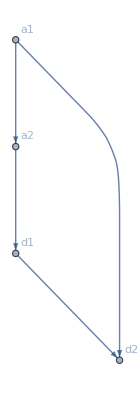

```mathematica
Graph[{a1->d2,a2->d1,a1->a2,d1->d2},VertexLabels->"Name"]
```

```mathematica
AcyclicGraphQ[Graph[{a1, d1, a2, d2}, {DirectedEdge[a1, d1], DirectedEdge[a2, d2]}]]
```

True

```mathematica
WeaklyConnectedGraphQ@%
```

False

```mathematica
DirectedEdge[#1,#2]
```

```mathematica
tb->ta
```

tb->ta

#### 1-loop coft with p_T

```mathematica
(*int = (nbar.n1)/(k_- n1.k) e^(-i x_⊥·k_⊥)=(n1_-)/(k_-((n_+k_-)/2+(n_-k_+)/2+ n_⊥.p_⊥))=1/(k_-((δ^2 θ1^2 k_-)/2+(k_+)/2+ |n_⊥||p_⊥|Cos[θ]))=1/(k_-((δ^2 θ1^2 k_-)/2+(k_+)/2+ δ θ1|k_⊥|Cos[θ]))*)
(*mesuare = 1/2 dk_+dk_-d^(2-2ϵ)k_⊥ δ^+(k^2) δ(Qβ-k_-) δ((k_+)/(k_-)-δ^2) = 1/2|k_⊥|^(1-2ϵ)Subscript[dΩ, 2-2ϵ] dk_+dk_-d|k_⊥| δ^+(|k_⊥|^2-k_+k_-) δ(Qβ-k_-) δ((k_+)/(k_-)-δ^2) = 1/4|k_⊥|^(-2ϵ) 2π Sin^(-2ϵ)[θ] dk_+dk_-δ(Qβ-k_-) δ((k_+)/(k_-)-δ^2) |_(|k_⊥|=√(k_+k_-))  *)
(*prefac = 1/(2π)^(3-2ϵ)*)
```

```mathematica
intgrand=2/(kp km)*1/((kp+km)/2)^α


oldvar={kp,km,Cos[θ]};
newvar={kt,y,t};
old2new={kp->kt √y,km-> kt/√y,Cos[θ]->1-2t};
jaco = Det@(D[oldvar/.old2new,#]&/@newvar);
```

(2^α (km+kp)^-α)/(km kp)

```mathematica
Reduce[((kp-km)/.old2new)>=0,{kt,y}]
```

(kt<0&&0<y≤1)||(kt==0&&y>0)||(kt>0&&y≥1)

```mathematica
2/(kp km)*1/((kp+km)/2)^α*1/(2kt)*Sin[θ]^(-1-2ϵ)*E^(I kt bt Cos[θ])*jaco*kt^(1-2ϵ)/.{kp->kt √y,km-> kt/√y,Cos[θ]->1-2t,Sin[θ]->√(4t tb)}//Simplify//PowerExpand
```

2^(α-2 ϵ) ⅇ^(ⅈ bt kt (1-2 t)) kt^(-1-α-2 ϵ) t^(-1/2-ϵ) tb^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α

```mathematica
(*f -> -ⅈ bt (-1+2 t)+ⅇ^-EulerGamma xm √y*)
```

```mathematica
%/.ⅇ^(ⅈ bt kt (-1+2 t)-ⅇ^-EulerGamma kt xm √y)->E^(- kt f)
```

2^(-1-2 ϵ) ⅇ^(-f kt) kt^(-1-α-2 ϵ) t^(-1/2-ϵ) tb^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α

```mathematica
Integrate[%,{kt,0,∞}]//Normal
```

2^(α-2 ϵ) t^(-1/2-ϵ) (ⅈ bt (-1+2 t))^(α+2 ϵ) tb^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α Gamma[-α-2 ϵ]

```mathematica
1/(kp km)*1/(kp+km)^α*1/(2kt)*Sin[θ]^(-1-2ϵ)*E^(-I kt bt Cos[θ])*jaco*kt^(1-2ϵ)//.{kp->kt √y,km-> kt/√y,Cos[θ]->1-2t,Sin[θ]->√(4t tb)}//Simplify//PowerExpand
```

2^(-1-2 ϵ) ⅇ^(ⅈ bt kt (-1+2 t)) kt^(-1-α-2 ϵ) t^(-1/2-ϵ) tb^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α

```mathematica
Integrate[%/.ⅇ^(ⅈ bt kt (-1+2 t))->E^(-kt f),{kt,0,∞}]
```

ConditionalExpression[2^(-1-2 ϵ) f^(α+2 ϵ) t^(-1/2-ϵ) tb^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α Gamma[-α-2 ϵ], Re[α+2 ϵ]<0&&Re[f]>0]

```mathematica
Normal@%/.{f->(1-2t)bt I}
```

2^(-1-2 ϵ) (ⅈ bt (1-2 t))^(α+2 ϵ) t^(-1/2-ϵ) tb^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α Gamma[-α-2 ϵ]

```mathematica
Integrate[%,{y,0,1}]
```

ConditionalExpression[(2^(-2 ϵ) (ⅈ bt (1-2 t))^(α+2 ϵ) t^(-1/2-ϵ) tb^(-1/2-ϵ) Gamma[-α-2 ϵ] Hypergeometric2F1[α/2,α,(2+α)/2,-1])/α, Re[α]>0]

```mathematica
Integrate[(1-2t)^(α+2ϵ)t^(-1/2-ϵ)(1-t)^(-1/2-ϵ),{t,0,1}]
```

ConditionalExpression[Gamma[1/2-ϵ] (((-1)^(α+2 ϵ) 2^(-1/2+ϵ) Cos[π ϵ] Gamma[-1/2-α-ϵ] Gamma[1+α+2 ϵ] Hypergeometric2F1[1/2-ϵ,1/2+ϵ,3/2+α+ϵ,1/2])/π+((-2)^(α+2 ϵ) π^(3/2) Sec[π (α+ϵ)])/(Gamma[1/2-α/2] Gamma[1+α] Gamma[1/2-α/2-ϵ]))+(2^(-1/2+ϵ) ⅇ^(ⅈ π ϵ) π Gamma[1+α+2 ϵ] Hypergeometric2F1[1/2-ϵ,1/2+ϵ,3/2+α+ϵ,1/2] (1-ⅈ Tan[π ϵ]))/(Gamma[1/2+ϵ] Gamma[3/2+α+ϵ]), Re[ϵ]<1/2&&Re[α+2 ϵ]>-1]

```mathematica
(2^(-2 ϵ) (ⅈ bt )^(α+2 ϵ) Gamma[-α-2 ϵ] Hypergeometric2F1[α/2,α,(2+α)/2,-1])/α*(Gamma[1/2-ϵ] (((-1)^(α+2 ϵ) 2^(-1/2+ϵ) Cos[π ϵ] Gamma[-1/2-α-ϵ] Gamma[1+α+2 ϵ] Hypergeometric2F1[1/2-ϵ,1/2+ϵ,3/2+α+ϵ,1/2])/π+((-2)^(α+2 ϵ) π^(3/2) Sec[π (α+ϵ)])/(Gamma[1/2-α/2] Gamma[1+α] Gamma[1/2-α/2-ϵ]))+(2^(-1/2+ϵ) ⅇ^(ⅈ π ϵ) π Gamma[1+α+2 ϵ] Hypergeometric2F1[1/2-ϵ,1/2+ϵ,3/2+α+ϵ,1/2] (1-ⅈ Tan[π ϵ]))/(Gamma[1/2+ϵ] Gamma[3/2+α+ϵ]))//Expand
```

((-1)^(α+2 ϵ) 2^(-1/2-ϵ) (ⅈ bt)^(α+2 ϵ) Cos[π ϵ] Gamma[-α-2 ϵ] Gamma[1/2-ϵ] Gamma[-1/2-α-ϵ] Gamma[1+α+2 ϵ] Hypergeometric2F1[α/2,α,(2+α)/2,-1] Hypergeometric2F1[1/2-ϵ,1/2+ϵ,3/2+α+ϵ,1/2])/(π α)+(2^(-1/2-ϵ) (ⅈ bt)^(α+2 ϵ) ⅇ^(ⅈ π ϵ) π Gamma[-α-2 ϵ] Gamma[1+α+2 ϵ] Hypergeometric2F1[α/2,α,(2+α)/2,-1] Hypergeometric2F1[1/2-ϵ,1/2+ϵ,3/2+α+ϵ,1/2])/(α Gamma[1/2+ϵ] Gamma[3/2+α+ϵ])+((-1)^(α+2 ϵ) 2^α (ⅈ bt)^(α+2 ϵ) π^(3/2) Gamma[-α-2 ϵ] Gamma[1/2-ϵ] Hypergeometric2F1[α/2,α,(2+α)/2,-1] Sec[π (α+ϵ)])/(α Gamma[1/2-α/2] Gamma[1+α] Gamma[1/2-α/2-ϵ])-(ⅈ 2^(-1/2-ϵ) (ⅈ bt)^(α+2 ϵ) ⅇ^(ⅈ π ϵ) π Gamma[-α-2 ϵ] Gamma[1+α+2 ϵ] Hypergeometric2F1[α/2,α,(2+α)/2,-1] Hypergeometric2F1[1/2-ϵ,1/2+ϵ,3/2+α+ϵ,1/2] Tan[π ϵ])/(α Gamma[1/2+ϵ] Gamma[3/2+α+ϵ])

```mathematica
%/.{Hypergeometric2F1[α/2,α,(2+α)/2,-1] ->HypExp[Hypergeometric2F1[α/2,α,(2+α)/2,-1] ,α,1],Hypergeometric2F1[1/2-ϵ,1/2+ϵ,3/2+α+ϵ,1/2]->F}
```

((-1)^(α+2 ϵ) 2^(-1/2-ϵ) (ⅈ bt)^(α+2 ϵ) F Cos[π ϵ] Gamma[-α-2 ϵ] Gamma[1/2-ϵ] Gamma[-1/2-α-ϵ] Gamma[1+α+2 ϵ])/(π α)+(2^(-1/2-ϵ) (ⅈ bt)^(α+2 ϵ) ⅇ^(ⅈ π ϵ) F π Gamma[-α-2 ϵ] Gamma[1+α+2 ϵ])/(α Gamma[1/2+ϵ] Gamma[3/2+α+ϵ])+((-1)^(α+2 ϵ) 2^α (ⅈ bt)^(α+2 ϵ) π^(3/2) Gamma[-α-2 ϵ] Gamma[1/2-ϵ] Sec[π (α+ϵ)])/(α Gamma[1/2-α/2] Gamma[1+α] Gamma[1/2-α/2-ϵ])-(ⅈ 2^(-1/2-ϵ) (ⅈ bt)^(α+2 ϵ) ⅇ^(ⅈ π ϵ) F π Gamma[-α-2 ϵ] Gamma[1+α+2 ϵ] Tan[π ϵ])/(α Gamma[1/2+ϵ] Gamma[3/2+α+ϵ])

```mathematica
Series[%/.bt->1,{α,0,1}]//Normal;
```

```mathematica
Series[%,{ϵ,0,1}]//Normal
```

-(π α)/(8 ϵ^3)+(π/4+1/4 π α (EulerGamma+Log[2]+PolyGamma[0,1/2]))/ϵ^2+1/(48 α ϵ)(-24 π-24 EulerGamma π α-12 EulerGamma^2 π α^2-π^3 α^2-24 π α Log[2]-24 EulerGamma π α^2 Log[2]-12 π α^2 Log[2]^2-12 √2 F α PolyGamma[0,-1/2]-24 π α PolyGamma[0,1/2]-24 EulerGamma π α^2 PolyGamma[0,1/2]-24 π α^2 Log[2] PolyGamma[0,1/2]-12 π α^2 PolyGamma[0,1/2]^2+12 √2 F α PolyGamma[0,3/2])+1/(48 α)(-48 EulerGamma π+48 ⅈ √2 F π-72 ⅈ π^2-72 EulerGamma^2 π α-144 ⅈ EulerGamma π^2 α-24 √2 F π^2 α+38 π^3 α-56 EulerGamma^3 π α^2+96 ⅈ √2 F π α^2-144 ⅈ EulerGamma^2 π^2 α^2+74 EulerGamma π^3 α^2+6 ⅈ √2 F π^3 α^2-48 EulerGamma π α Log[2]-72 ⅈ π^2 α Log[2]-72 EulerGamma^2 π α^2 Log[2]-144 ⅈ EulerGamma π^2 α^2 Log[2]+38 π^3 α^2 Log[2]-24 EulerGamma π α^2 Log[2]^2-36 ⅈ π^2 α^2 Log[2]^2-24 √2 F PolyGamma[0,-1/2]-72 ⅈ √2 F π α PolyGamma[0,-1/2]-84 √2 F α^2 PolyGamma[0,-1/2]+34 √2 F π^2 α^2 PolyGamma[0,-1/2]+12 √2 F α Log[2] PolyGamma[0,-1/2]+3 √2 F α^2 Log[2]^2 PolyGamma[0,-1/2]+18 √2 F α PolyGamma[0,-1/2]^2+36 ⅈ √2 F π α^2 PolyGamma[0,-1/2]^2-3 √2 F α^2 Log[2] PolyGamma[0,-1/2]^2-7 √2 F α^2 PolyGamma[0,-1/2]^3-48 EulerGamma π α PolyGamma[0,1/2]-72 ⅈ π^2 α PolyGamma[0,1/2]-72 EulerGamma^2 π α^2 PolyGamma[0,1/2]-144 ⅈ EulerGamma π^2 α^2 PolyGamma[0,1/2]+38 π^3 α^2 PolyGamma[0,1/2]-48 EulerGamma π α^2 Log[2] PolyGamma[0,1/2]-72 ⅈ π^2 α^2 Log[2] PolyGamma[0,1/2]+12 √2 F α PolyGamma[0,-1/2] PolyGamma[0,1/2]+6 √2 F α^2 Log[2] PolyGamma[0,-1/2] PolyGamma[0,1/2]-3 √2 F α^2 PolyGamma[0,-1/2]^2 PolyGamma[0,1/2]-24 EulerGamma π α^2 PolyGamma[0,1/2]^2-36 ⅈ π^2 α^2 PolyGamma[0,1/2]^2+3 √2 F α^2 PolyGamma[0,-1/2] PolyGamma[0,1/2]^2+24 √2 F PolyGamma[0,3/2]+24 ⅈ √2 F π α PolyGamma[0,3/2]+84 √2 F α^2 PolyGamma[0,3/2]-10 √2 F π^2 α^2 PolyGamma[0,3/2]-12 √2 F α Log[2] PolyGamma[0,3/2]-3 √2 F α^2 Log[2]^2 PolyGamma[0,3/2]-12 √2 F α PolyGamma[0,1/2] PolyGamma[0,3/2]-6 √2 F α^2 Log[2] PolyGamma[0,1/2] PolyGamma[0,3/2]-3 √2 F α^2 PolyGamma[0,1/2]^2 PolyGamma[0,3/2]-18 √2 F α PolyGamma[0,3/2]^2-12 ⅈ √2 F π α^2 PolyGamma[0,3/2]^2+3 √2 F α^2 Log[2] PolyGamma[0,3/2]^2+3 √2 F α^2 PolyGamma[0,1/2] PolyGamma[0,3/2]^2+7 √2 F α^2 PolyGamma[0,3/2]^3+8 π α^2 PolyGamma[2,1])+ϵ (1/24 F π (36 ⅈ √2-ⅈ √2 π^2-6 √2 π Log[2]-3 ⅈ √2 Log[2]^2-6 √2 π PolyGamma[0,1/2]-6 ⅈ √2 Log[2] PolyGamma[0,1/2]-3 ⅈ √2 PolyGamma[0,1/2]^2+18 √2 π PolyGamma[0,3/2]+6 ⅈ √2 Log[2] PolyGamma[0,3/2]+6 ⅈ √2 PolyGamma[0,1/2] PolyGamma[0,3/2]+9 ⅈ √2 PolyGamma[0,3/2]^2)+1/(12 α)(-12 EulerGamma^2 π-36 ⅈ EulerGamma π^2-24 √2 F π^2+22 π^3-12 ⅈ √2 F π Log[2]-18 ⅈ √2 F π PolyGamma[0,-1/2]+6 √2 F Log[2] PolyGamma[0,-1/2]+3 √2 F PolyGamma[0,-1/2]^2-12 ⅈ √2 F π PolyGamma[0,1/2]+6 √2 F PolyGamma[0,-1/2] PolyGamma[0,1/2]+6 ⅈ √2 F π PolyGamma[0,3/2]-6 √2 F Log[2] PolyGamma[0,3/2]-6 √2 F PolyGamma[0,1/2] PolyGamma[0,3/2]-3 √2 F PolyGamma[0,3/2]^2)+1/24 π (-40 EulerGamma^3-144 ⅈ EulerGamma^2 π+126 EulerGamma π^2+15 ⅈ π^3-24 EulerGamma^2 Log[2]-72 ⅈ EulerGamma π Log[2]+44 π^2 Log[2]-24 EulerGamma^2 PolyGamma[0,1/2]-72 ⅈ EulerGamma π PolyGamma[0,1/2]+44 π^2 PolyGamma[0,1/2]-3 PolyGamma[2,1/2]+16 PolyGamma[2,1])+1/24 F (144 ⅈ √2 π-12 ⅈ √2 π^3-36 √2 Log[2]+17 √2 π^2 Log[2]+√2 Log[2]^3-60 √2 PolyGamma[0,-1/2]+63 √2 π^2 PolyGamma[0,-1/2]+36 ⅈ √2 π Log[2] PolyGamma[0,-1/2]-3 √2 Log[2]^2 PolyGamma[0,-1/2]+36 ⅈ √2 π PolyGamma[0,-1/2]^2-9 √2 Log[2] PolyGamma[0,-1/2]^2-5 √2 PolyGamma[0,-1/2]^3-36 √2 PolyGamma[0,1/2]+17 √2 π^2 PolyGamma[0,1/2]+3 √2 Log[2]^2 PolyGamma[0,1/2]+36 ⅈ √2 π PolyGamma[0,-1/2] PolyGamma[0,1/2]-6 √2 Log[2] PolyGamma[0,-1/2] PolyGamma[0,1/2]-9 √2 PolyGamma[0,-1/2]^2 PolyGamma[0,1/2]+3 √2 Log[2] PolyGamma[0,1/2]^2-3 √2 PolyGamma[0,-1/2] PolyGamma[0,1/2]^2+√2 PolyGamma[0,1/2]^3+√2 PolyGamma[2,1/2]-5 √2 PolyGamma[2,3/2])+1/24 F (-84 ⅈ √2 π+ⅈ √2 π^3+36 √2 Log[2]+√2 π^2 Log[2]+3 ⅈ √2 π Log[2]^2-√2 Log[2]^3+36 √2 PolyGamma[0,1/2]+√2 π^2 PolyGamma[0,1/2]+6 ⅈ √2 π Log[2] PolyGamma[0,1/2]-3 √2 Log[2]^2 PolyGamma[0,1/2]+3 ⅈ √2 π PolyGamma[0,1/2]^2-3 √2 Log[2] PolyGamma[0,1/2]^2-√2 PolyGamma[0,1/2]^3+60 √2 PolyGamma[0,3/2]-21 √2 π^2 PolyGamma[0,3/2]-18 ⅈ √2 π Log[2] PolyGamma[0,3/2]+3 √2 Log[2]^2 PolyGamma[0,3/2]-18 ⅈ √2 π PolyGamma[0,1/2] PolyGamma[0,3/2]+6 √2 Log[2] PolyGamma[0,1/2] PolyGamma[0,3/2]+3 √2 PolyGamma[0,1/2]^2 PolyGamma[0,3/2]-21 ⅈ √2 π PolyGamma[0,3/2]^2+9 √2 Log[2] PolyGamma[0,3/2]^2+9 √2 PolyGamma[0,1/2] PolyGamma[0,3/2]^2+5 √2 PolyGamma[0,3/2]^3-√2 PolyGamma[2,1/2]+5 √2 PolyGamma[2,3/2])+α (1/2880 π (-4080 EulerGamma^4-17280 ⅈ EulerGamma^3 π+19560 EulerGamma^2 π^2+3600 ⅈ EulerGamma π^3+997 π^4-4800 EulerGamma^3 Log[2]-17280 ⅈ EulerGamma^2 π Log[2]+15120 EulerGamma π^2 Log[2]+1800 ⅈ π^3 Log[2]-1440 EulerGamma^2 Log[2]^2-4320 ⅈ EulerGamma π Log[2]^2+2640 π^2 Log[2]^2-4800 EulerGamma^3 PolyGamma[0,1/2]-17280 ⅈ EulerGamma^2 π PolyGamma[0,1/2]+15120 EulerGamma π^2 PolyGamma[0,1/2]+1800 ⅈ π^3 PolyGamma[0,1/2]-2880 EulerGamma^2 Log[2] PolyGamma[0,1/2]-8640 ⅈ EulerGamma π Log[2] PolyGamma[0,1/2]+5280 π^2 Log[2] PolyGamma[0,1/2]-1440 EulerGamma^2 PolyGamma[0,1/2]^2-4320 ⅈ EulerGamma π PolyGamma[0,1/2]^2+2640 π^2 PolyGamma[0,1/2]^2-720 EulerGamma PolyGamma[2,1/2]-540 ⅈ π PolyGamma[2,1/2]-360 Log[2] PolyGamma[2,1/2]-360 PolyGamma[0,1/2] PolyGamma[2,1/2]+4800 EulerGamma PolyGamma[2,1]+4320 ⅈ π PolyGamma[2,1]+1920 Log[2] PolyGamma[2,1]+1920 PolyGamma[0,1/2] PolyGamma[2,1])+1/48 F π (-60 √2 π+5 √2 π^3-12 ⅈ √2 Log[2]+4 ⅈ √2 π^2 Log[2]-3 √2 π Log[2]^2-ⅈ √2 Log[2]^3-12 ⅈ √2 PolyGamma[0,1/2]+4 ⅈ √2 π^2 PolyGamma[0,1/2]-6 √2 π Log[2] PolyGamma[0,1/2]-3 ⅈ √2 Log[2]^2 PolyGamma[0,1/2]-3 √2 π PolyGamma[0,1/2]^2-3 ⅈ √2 Log[2] PolyGamma[0,1/2]^2-ⅈ √2 PolyGamma[0,1/2]^3-84 ⅈ √2 PolyGamma[0,3/2]+6 ⅈ √2 π^2 PolyGamma[0,3/2]+6 √2 π Log[2] PolyGamma[0,3/2]+3 ⅈ √2 Log[2]^2 PolyGamma[0,3/2]+6 √2 π PolyGamma[0,1/2] PolyGamma[0,3/2]+6 ⅈ √2 Log[2] PolyGamma[0,1/2] PolyGamma[0,3/2]+3 ⅈ √2 PolyGamma[0,1/2]^2 PolyGamma[0,3/2]-15 √2 π PolyGamma[0,3/2]^2-3 ⅈ √2 Log[2] PolyGamma[0,3/2]^2-3 ⅈ √2 PolyGamma[0,1/2] PolyGamma[0,3/2]^2-7 ⅈ √2 PolyGamma[0,3/2]^3-ⅈ √2 PolyGamma[2,1/2]-7 ⅈ √2 PolyGamma[2,3/2])+F π (-1/3 (7 π^2+12 ⅈ π PolyGamma[0,3/2]-12 PolyGamma[0,3/2]^2) (-(EulerGamma^2+π^2/6)/(4 √2 π)+(2 (((-EulerGamma^2-π^2/6)/(8 √2)-EulerGamma ((ⅈ π)/(4 √2)-Log[2]/(8 √2))+1/2 (π^2/(4 √2)+(ⅈ π Log[2])/(4 √2)-Log[2]^2/(16 √2)))/(√π)-((-EulerGamma/(8 √2)+1/2 (-(ⅈ π)/(4 √2)+Log[2]/(8 √2))) PolyGamma[0,1/2])/(√π)-(-π^2+2 PolyGamma[0,1/2]^2)/(64 √(2 π))))/(√π)-(2 ((-EulerGamma/(8 √2)+1/2 (-(ⅈ π)/(4 √2)+Log[2]/(8 √2)))/(√π)+PolyGamma[0,1/2]/(16 √(2 π))) PolyGamma[0,3/2])/(√π)-2 EulerGamma ((2 ((-EulerGamma/(8 √2)+1/2 (-(ⅈ π)/(4 √2)+Log[2]/(8 √2)))/(√π)+PolyGamma[0,1/2]/(16 √(2 π))))/(√π)+PolyGamma[0,3/2]/(8 √2 π))-(8-π^2+2 PolyGamma[0,3/2]^2)/(32 √2 π))-(2 ⅈ π-4 PolyGamma[0,3/2]) (-(2 (((-EulerGamma^2-π^2/6)/(8 √2)-EulerGamma ((ⅈ π)/(4 √2)-Log[2]/(8 √2))+1/2 (π^2/(4 √2)+(ⅈ π Log[2])/(4 √2)-Log[2]^2/(16 √2)))/(√π)-((-EulerGamma/(8 √2)+1/2 (-(ⅈ π)/(4 √2)+Log[2]/(8 √2))) PolyGamma[0,1/2])/(√π)-(-π^2+2 PolyGamma[0,1/2]^2)/(64 √(2 π))) PolyGamma[0,3/2])/(√π)+2 (EulerGamma^2+π^2/6) ((2 ((-EulerGamma/(8 √2)+1/2 (-(ⅈ π)/(4 √2)+Log[2]/(8 √2)))/(√π)+PolyGamma[0,1/2]/(16 √(2 π))))/(√π)+PolyGamma[0,3/2]/(8 √2 π))+(((-EulerGamma/(8 √2)+1/2 (-(ⅈ π)/(4 √2)+Log[2]/(8 √2)))/(√π)+PolyGamma[0,1/2]/(16 √(2 π))) (8-π^2+2 PolyGamma[0,3/2]^2))/(2 √π)-2 EulerGamma ((2 (((-EulerGamma^2-π^2/6)/(8 √2)-EulerGamma ((ⅈ π)/(4 √2)-Log[2]/(8 √2))+1/2 (π^2/(4 √2)+(ⅈ π Log[2])/(4 √2)-Log[2]^2/(16 √2)))/(√π)-((-EulerGamma/(8 √2)+1/2 (-(ⅈ π)/(4 √2)+Log[2]/(8 √2))) PolyGamma[0,1/2])/(√π)-(-π^2+2 PolyGamma[0,1/2]^2)/(64 √(2 π))))/(√π)-(2 ((-EulerGamma/(8 √2)+1/2 (-(ⅈ π)/(4 √2)+Log[2]/(8 √2)))/(√π)+PolyGamma[0,1/2]/(16 √(2 π))) PolyGamma[0,3/2])/(√π)-(8-π^2+2 PolyGamma[0,3/2]^2)/(32 √2 π))-(-EulerGamma^3-(EulerGamma π^2)/2+PolyGamma[2,1])/(6 √2 π)+1/(√π)2 (-(((-EulerGamma^2-π^2/6)/(8 √2)-EulerGamma ((ⅈ π)/(4 √2)-Log[2]/(8 √2))+1/2 (π^2/(4 √2)+(ⅈ π Log[2])/(4 √2)-Log[2]^2/(16 √2))) PolyGamma[0,1/2])/(√π)+((-EulerGamma/(8 √2)+1/2 (-(ⅈ π)/(4 √2)+Log[2]/(8 √2))) (-π^2+2 PolyGamma[0,1/2]^2))/(4 √π)-(3 π^2 PolyGamma[0,1/2]-2 PolyGamma[0,1/2]^3-2 PolyGamma[2,1/2])/(192 √(2 π))+1/(√π)((-EulerGamma^2-π^2/6) ((ⅈ π)/(4 √2)-Log[2]/(8 √2))-EulerGamma (-π^2/(4 √2)-(ⅈ π Log[2])/(4 √2)+Log[2]^2/(16 √2))+1/2 ((ⅈ π^3)/(6 √2)-(π^2 Log[2])/(4 √2)-(ⅈ π Log[2]^2)/(8 √2)+Log[2]^3/(48 √2))+(-EulerGamma^3-(EulerGamma π^2)/2+PolyGamma[2,1])/(12 √2)))-(-24 PolyGamma[0,3/2]+3 π^2 PolyGamma[0,3/2]-2 PolyGamma[0,3/2]^3-2 PolyGamma[2,3/2])/(96 √2 π))-(EulerGamma/(4 √2 π)+(2 ((-EulerGamma/(8 √2)+1/2 (-(ⅈ π)/(4 √2)+Log[2]/(8 √2)))/(√π)+PolyGamma[0,1/2]/(16 √(2 π))))/(√π)+PolyGamma[0,3/2]/(8 √2 π)) ((8 EulerGamma π^2)/3-(8 ⅈ π^3)/3+2 ⅈ π (-8+π^2)-4 (-8+π^2) PolyGamma[0,3/2]-4/3 (-24 EulerGamma+3 EulerGamma π^2-2 π^2 PolyGamma[0,3/2])+8 PolyGamma[2,1]-4 ((2 EulerGamma π^2)/3+2 PolyGamma[2,1])+2/3 (-48 EulerGamma+6 EulerGamma π^2+4 π^2 PolyGamma[0,3/2]-3 PolyGamma[2,3/2])+4 PolyGamma[2,3/2])+1/(8 √2 π)(-64+16 π^2-(31 π^4)/15+2 (-96+π^4)+8 (-π^4/15-4 EulerGamma PolyGamma[2,1])-4 (π^4/45-4 EulerGamma PolyGamma[2,1])-4 (π^4/9-4 EulerGamma PolyGamma[2,1])+2 ⅈ π PolyGamma[2,3/2]-4 PolyGamma[0,3/2] PolyGamma[2,3/2]+4/3 (-8 π^2+π^4+12 PolyGamma[0,3/2] PolyGamma[2,1]-3 EulerGamma PolyGamma[2,3/2])-8 (-1/3 π^2 (-4+π^2/2)+1/2 (-16+π^4/6)+2 PolyGamma[0,3/2] PolyGamma[2,1]-1/2 EulerGamma PolyGamma[2,3/2]))+2 (((((-EulerGamma^2-π^2/6)/(8 √2)-EulerGamma ((ⅈ π)/(4 √2)-Log[2]/(8 √2))+1/2 (π^2/(4 √2)+(ⅈ π Log[2])/(4 √2)-Log[2]^2/(16 √2)))/(√π)-((-EulerGamma/(8 √2)+1/2 (-(ⅈ π)/(4 √2)+Log[2]/(8 √2))) PolyGamma[0,1/2])/(√π)-(-π^2+2 PolyGamma[0,1/2]^2)/(64 √(2 π))) (8-π^2+2 PolyGamma[0,3/2]^2))/(2 √π)+2 (EulerGamma^2+π^2/6) ((2 (((-EulerGamma^2-π^2/6)/(8 √2)-EulerGamma ((ⅈ π)/(4 √2)-Log[2]/(8 √2))+1/2 (π^2/(4 √2)+(ⅈ π Log[2])/(4 √2)-Log[2]^2/(16 √2)))/(√π)-((-EulerGamma/(8 √2)+1/2 (-(ⅈ π)/(4 √2)+Log[2]/(8 √2))) PolyGamma[0,1/2])/(√π)-(-π^2+2 PolyGamma[0,1/2]^2)/(64 √(2 π))))/(√π)-(2 ((-EulerGamma/(8 √2)+1/2 (-(ⅈ π)/(4 √2)+Log[2]/(8 √2)))/(√π)+PolyGamma[0,1/2]/(16 √(2 π))) PolyGamma[0,3/2])/(√π)-(8-π^2+2 PolyGamma[0,3/2]^2)/(32 √2 π))+4/3 ((2 ((-EulerGamma/(8 √2)+1/2 (-(ⅈ π)/(4 √2)+Log[2]/(8 √2)))/(√π)+PolyGamma[0,1/2]/(16 √(2 π))))/(√π)+PolyGamma[0,3/2]/(8 √2 π)) (-EulerGamma^3-(EulerGamma π^2)/2+PolyGamma[2,1])-(EulerGamma^4+EulerGamma^2 π^2+(3 π^4)/20-4 EulerGamma PolyGamma[2,1])/(12 √2 π)-1/(√π)2 PolyGamma[0,3/2] (-(((-EulerGamma^2-π^2/6)/(8 √2)-EulerGamma ((ⅈ π)/(4 √2)-Log[2]/(8 √2))+1/2 (π^2/(4 √2)+(ⅈ π Log[2])/(4 √2)-Log[2]^2/(16 √2))) PolyGamma[0,1/2])/(√π)+((-EulerGamma/(8 √2)+1/2 (-(ⅈ π)/(4 √2)+Log[2]/(8 √2))) (-π^2+2 PolyGamma[0,1/2]^2))/(4 √π)-(3 π^2 PolyGamma[0,1/2]-2 PolyGamma[0,1/2]^3-2 PolyGamma[2,1/2])/(192 √(2 π))+1/(√π)((-EulerGamma^2-π^2/6) ((ⅈ π)/(4 √2)-Log[2]/(8 √2))-EulerGamma (-π^2/(4 √2)-(ⅈ π Log[2])/(4 √2)+Log[2]^2/(16 √2))+1/2 ((ⅈ π^3)/(6 √2)-(π^2 Log[2])/(4 √2)-(ⅈ π Log[2]^2)/(8 √2)+Log[2]^3/(48 √2))+(-EulerGamma^3-(EulerGamma π^2)/2+PolyGamma[2,1])/(12 √2)))+1/(√π)2 ((((-EulerGamma^2-π^2/6)/(8 √2)-EulerGamma ((ⅈ π)/(4 √2)-Log[2]/(8 √2))+1/2 (π^2/(4 √2)+(ⅈ π Log[2])/(4 √2)-Log[2]^2/(16 √2))) (-π^2+2 PolyGamma[0,1/2]^2))/(4 √π)+((-EulerGamma/(8 √2)+1/2 (-(ⅈ π)/(4 √2)+Log[2]/(8 √2))) (3 π^2 PolyGamma[0,1/2]-2 PolyGamma[0,1/2]^3-2 PolyGamma[2,1/2]))/(12 √π)-(-π^4-12 π^2 PolyGamma[0,1/2]^2+4 PolyGamma[0,1/2]^4+16 PolyGamma[0,1/2] PolyGamma[2,1/2])/(1536 √(2 π))-1/(√π)PolyGamma[0,1/2] ((-EulerGamma^2-π^2/6) ((ⅈ π)/(4 √2)-Log[2]/(8 √2))-EulerGamma (-π^2/(4 √2)-(ⅈ π Log[2])/(4 √2)+Log[2]^2/(16 √2))+1/2 ((ⅈ π^3)/(6 √2)-(π^2 Log[2])/(4 √2)-(ⅈ π Log[2]^2)/(8 √2)+Log[2]^3/(48 √2))+(-EulerGamma^3-(EulerGamma π^2)/2+PolyGamma[2,1])/(12 √2))+1/(√π)((-EulerGamma^2-π^2/6) (-π^2/(4 √2)-(ⅈ π Log[2])/(4 √2)+Log[2]^2/(16 √2))-EulerGamma (-(ⅈ π^3)/(6 √2)+(π^2 Log[2])/(4 √2)+(ⅈ π Log[2]^2)/(8 √2)-Log[2]^3/(48 √2))+1/2 (-π^4/(12 √2)-(ⅈ π^3 Log[2])/(6 √2)+(π^2 Log[2]^2)/(8 √2)+(ⅈ π Log[2]^3)/(24 √2)-Log[2]^4/(192 √2))+2/3 ((ⅈ π)/(4 √2)-Log[2]/(8 √2)) (-EulerGamma^3-(EulerGamma π^2)/2+PolyGamma[2,1])+(-EulerGamma^4-EulerGamma^2 π^2-(3 π^4)/20+4 EulerGamma PolyGamma[2,1])/(24 √2)))-2 EulerGamma (-(2 (((-EulerGamma^2-π^2/6)/(8 √2)-EulerGamma ((ⅈ π)/(4 √2)-Log[2]/(8 √2))+1/2 (π^2/(4 √2)+(ⅈ π Log[2])/(4 √2)-Log[2]^2/(16 √2)))/(√π)-((-EulerGamma/(8 √2)+1/2 (-(ⅈ π)/(4 √2)+Log[2]/(8 √2))) PolyGamma[0,1/2])/(√π)-(-π^2+2 PolyGamma[0,1/2]^2)/(64 √(2 π))) PolyGamma[0,3/2])/(√π)+(((-EulerGamma/(8 √2)+1/2 (-(ⅈ π)/(4 √2)+Log[2]/(8 √2)))/(√π)+PolyGamma[0,1/2]/(16 √(2 π))) (8-π^2+2 PolyGamma[0,3/2]^2))/(2 √π)+1/(√π)2 (-(((-EulerGamma^2-π^2/6)/(8 √2)-EulerGamma ((ⅈ π)/(4 √2)-Log[2]/(8 √2))+1/2 (π^2/(4 √2)+(ⅈ π Log[2])/(4 √2)-Log[2]^2/(16 √2))) PolyGamma[0,1/2])/(√π)+((-EulerGamma/(8 √2)+1/2 (-(ⅈ π)/(4 √2)+Log[2]/(8 √2))) (-π^2+2 PolyGamma[0,1/2]^2))/(4 √π)-(3 π^2 PolyGamma[0,1/2]-2 PolyGamma[0,1/2]^3-2 PolyGamma[2,1/2])/(192 √(2 π))+1/(√π)((-EulerGamma^2-π^2/6) ((ⅈ π)/(4 √2)-Log[2]/(8 √2))-EulerGamma (-π^2/(4 √2)-(ⅈ π Log[2])/(4 √2)+Log[2]^2/(16 √2))+1/2 ((ⅈ π^3)/(6 √2)-(π^2 Log[2])/(4 √2)-(ⅈ π Log[2]^2)/(8 √2)+Log[2]^3/(48 √2))+(-EulerGamma^3-(EulerGamma π^2)/2+PolyGamma[2,1])/(12 √2)))-(-24 PolyGamma[0,3/2]+3 π^2 PolyGamma[0,3/2]-2 PolyGamma[0,3/2]^3-2 PolyGamma[2,3/2])/(96 √2 π))+(((-EulerGamma/(8 √2)+1/2 (-(ⅈ π)/(4 √2)+Log[2]/(8 √2)))/(√π)+PolyGamma[0,1/2]/(16 √(2 π))) (-24 PolyGamma[0,3/2]+3 π^2 PolyGamma[0,3/2]-2 PolyGamma[0,3/2]^3-2 PolyGamma[2,3/2]))/(6 √π)-(576-48 π^2-π^4+96 PolyGamma[0,3/2]^2-12 π^2 PolyGamma[0,3/2]^2+4 PolyGamma[0,3/2]^4+16 PolyGamma[0,3/2] PolyGamma[2,3/2])/(768 √2 π)))+1/π F (-1/3 (31 π^2+36 ⅈ π PolyGamma[0,-1/2]-12 PolyGamma[0,-1/2]^2) (-(π (-EulerGamma^2-π^2/6))/(4 √2)+(π (EulerGamma^2+π^2/6))/(4 √2)-EulerGamma (√π (-2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2))+1/4 √(π/2) PolyGamma[0,-1/2])+(π PolyGamma[0,1/2])/(4 √2))-2 EulerGamma ((EulerGamma π)/(4 √2)+1/2 (-√π (-2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2))+1/4 √(π/2) PolyGamma[0,-1/2])-(π PolyGamma[0,1/2])/(4 √2)))+1/2 (-√π (-2 √π (-(5 π^2)/(8 √2)-(3 ⅈ π Log[2])/(8 √2)+Log[2]^2/(16 √2))+2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2)) PolyGamma[0,-1/2]+(-2 √π (4+π^2/2)-2 √π PolyGamma[0,-1/2]^2)/(16 √2))+√π (-2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2))+1/4 √(π/2) PolyGamma[0,-1/2]) PolyGamma[0,1/2]+1/8 √(π/2) (π^(5/2)/2+√π PolyGamma[0,1/2]^2)))-1/2 (-√π (-2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2))+1/4 √(π/2) PolyGamma[0,-1/2])-(π PolyGamma[0,1/2])/(4 √2)) ((8 EulerGamma π^2)/3-8 ⅈ π^3-6 ⅈ π (8+π^2)+4 (8+π^2) PolyGamma[0,-1/2]+4/3 (24 EulerGamma+3 EulerGamma π^2+2 π^2 PolyGamma[0,-1/2])+8 PolyGamma[2,1]-4 ((2 EulerGamma π^2)/3+2 PolyGamma[2,1])+4 PolyGamma[2,3/2]-2/3 (48 EulerGamma+6 EulerGamma π^2-4 π^2 PolyGamma[0,-1/2]+3 PolyGamma[2,3/2]))-1/(8 √2)π (-64-16 π^2-(31 π^4)/15-2 (96+π^4)+8 (-π^4/15-4 EulerGamma PolyGamma[2,1])-4 (π^4/45-4 EulerGamma PolyGamma[2,1])-4 (π^4/9-4 EulerGamma PolyGamma[2,1])+6 ⅈ π PolyGamma[2,3/2]-4 PolyGamma[0,-1/2] PolyGamma[2,3/2]-8 (-1/3 π^2 (-4-π^2/2)+1/12 (-96-π^4)+2 PolyGamma[0,-1/2] PolyGamma[2,1]-1/2 EulerGamma PolyGamma[2,3/2])-4/3 (8 π^2+π^4-12 PolyGamma[0,-1/2] PolyGamma[2,1]+3 EulerGamma PolyGamma[2,3/2]))-(6 ⅈ π-4 PolyGamma[0,-1/2]) ((-EulerGamma^2-π^2/6) (√π (-2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2))+1/4 √(π/2) PolyGamma[0,-1/2])+(π PolyGamma[0,1/2])/(4 √2))+2 (EulerGamma^2+π^2/6) ((EulerGamma π)/(4 √2)+1/2 (-√π (-2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2))+1/4 √(π/2) PolyGamma[0,-1/2])-(π PolyGamma[0,1/2])/(4 √2)))-EulerGamma (√π (-2 √π (-(5 π^2)/(8 √2)-(3 ⅈ π Log[2])/(8 √2)+Log[2]^2/(16 √2))+2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2)) PolyGamma[0,-1/2]+(-2 √π (4+π^2/2)-2 √π PolyGamma[0,-1/2]^2)/(16 √2))-√π (-2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2))+1/4 √(π/2) PolyGamma[0,-1/2]) PolyGamma[0,1/2]-1/8 √(π/2) (π^(5/2)/2+√π PolyGamma[0,1/2]^2))-2 EulerGamma (-(π (-EulerGamma^2-π^2/6))/(4 √2)-EulerGamma (√π (-2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2))+1/4 √(π/2) PolyGamma[0,-1/2])+(π PolyGamma[0,1/2])/(4 √2))+1/2 (-√π (-2 √π (-(5 π^2)/(8 √2)-(3 ⅈ π Log[2])/(8 √2)+Log[2]^2/(16 √2))+2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2)) PolyGamma[0,-1/2]+(-2 √π (4+π^2/2)-2 √π PolyGamma[0,-1/2]^2)/(16 √2))+√π (-2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2))+1/4 √(π/2) PolyGamma[0,-1/2]) PolyGamma[0,1/2]+1/8 √(π/2) (π^(5/2)/2+√π PolyGamma[0,1/2]^2)))+1/2 (√π (-2 √π (-(5 π^2)/(8 √2)-(3 ⅈ π Log[2])/(8 √2)+Log[2]^2/(16 √2))+2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2)) PolyGamma[0,-1/2]+(-2 √π (4+π^2/2)-2 √π PolyGamma[0,-1/2]^2)/(16 √2)) PolyGamma[0,1/2]-1/2 (-2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2))+1/4 √(π/2) PolyGamma[0,-1/2]) (π^(5/2)/2+√π PolyGamma[0,1/2]^2)+1/24 √(π/2) (-3/2 π^(5/2) PolyGamma[0,1/2]-√π PolyGamma[0,1/2]^3-√π PolyGamma[2,1/2])-√π (-2 √π (-(9 ⅈ π^3)/(16 √2)+(9 π^2 Log[2])/(16 √2)+(3 ⅈ π Log[2]^2)/(16 √2)-Log[2]^3/(48 √2)-1/2 π^2 ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2)))+2 √π (-(5 π^2)/(8 √2)-(3 ⅈ π Log[2])/(8 √2)+Log[2]^2/(16 √2)) PolyGamma[0,-1/2]+1/2 ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2)) (-2 √π (4+π^2/2)-2 √π PolyGamma[0,-1/2]^2)+(6 √π (4+π^2/2) PolyGamma[0,-1/2]+2 √π PolyGamma[0,-1/2]^3+2 √π PolyGamma[2,3/2])/(48 √2))))+2 ((-EulerGamma^2-π^2/6) (√π (-2 √π (-(5 π^2)/(8 √2)-(3 ⅈ π Log[2])/(8 √2)+Log[2]^2/(16 √2))+2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2)) PolyGamma[0,-1/2]+(-2 √π (4+π^2/2)-2 √π PolyGamma[0,-1/2]^2)/(16 √2))-√π (-2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2))+1/4 √(π/2) PolyGamma[0,-1/2]) PolyGamma[0,1/2]-1/8 √(π/2) (π^(5/2)/2+√π PolyGamma[0,1/2]^2))+2 (EulerGamma^2+π^2/6) (-(π (-EulerGamma^2-π^2/6))/(4 √2)-EulerGamma (√π (-2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2))+1/4 √(π/2) PolyGamma[0,-1/2])+(π PolyGamma[0,1/2])/(4 √2))+1/2 (-√π (-2 √π (-(5 π^2)/(8 √2)-(3 ⅈ π Log[2])/(8 √2)+Log[2]^2/(16 √2))+2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2)) PolyGamma[0,-1/2]+(-2 √π (4+π^2/2)-2 √π PolyGamma[0,-1/2]^2)/(16 √2))+√π (-2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2))+1/4 √(π/2) PolyGamma[0,-1/2]) PolyGamma[0,1/2]+1/8 √(π/2) (π^(5/2)/2+√π PolyGamma[0,1/2]^2)))+2/3 (√π (-2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2))+1/4 √(π/2) PolyGamma[0,-1/2])+(π PolyGamma[0,1/2])/(4 √2)) (-EulerGamma^3-(EulerGamma π^2)/2+PolyGamma[2,1])+4/3 ((EulerGamma π)/(4 √2)+1/2 (-√π (-2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2))+1/4 √(π/2) PolyGamma[0,-1/2])-(π PolyGamma[0,1/2])/(4 √2))) (-EulerGamma^3-(EulerGamma π^2)/2+PolyGamma[2,1])+(π (EulerGamma^4+EulerGamma^2 π^2+(3 π^4)/20-4 EulerGamma PolyGamma[2,1]))/(12 √2)-(π (-EulerGamma^4-EulerGamma^2 π^2-(3 π^4)/20+4 EulerGamma PolyGamma[2,1]))/(12 √2)-EulerGamma (-√π (-2 √π (-(5 π^2)/(8 √2)-(3 ⅈ π Log[2])/(8 √2)+Log[2]^2/(16 √2))+2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2)) PolyGamma[0,-1/2]+(-2 √π (4+π^2/2)-2 √π PolyGamma[0,-1/2]^2)/(16 √2)) PolyGamma[0,1/2]+1/2 (-2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2))+1/4 √(π/2) PolyGamma[0,-1/2]) (π^(5/2)/2+√π PolyGamma[0,1/2]^2)-1/24 √(π/2) (-3/2 π^(5/2) PolyGamma[0,1/2]-√π PolyGamma[0,1/2]^3-√π PolyGamma[2,1/2])+√π (-2 √π (-(9 ⅈ π^3)/(16 √2)+(9 π^2 Log[2])/(16 √2)+(3 ⅈ π Log[2]^2)/(16 √2)-Log[2]^3/(48 √2)-1/2 π^2 ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2)))+2 √π (-(5 π^2)/(8 √2)-(3 ⅈ π Log[2])/(8 √2)+Log[2]^2/(16 √2)) PolyGamma[0,-1/2]+1/2 ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2)) (-2 √π (4+π^2/2)-2 √π PolyGamma[0,-1/2]^2)+(6 √π (4+π^2/2) PolyGamma[0,-1/2]+2 √π PolyGamma[0,-1/2]^3+2 √π PolyGamma[2,3/2])/(48 √2)))+1/2 (-1/2 (-2 √π (-(5 π^2)/(8 √2)-(3 ⅈ π Log[2])/(8 √2)+Log[2]^2/(16 √2))+2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2)) PolyGamma[0,-1/2]+(-2 √π (4+π^2/2)-2 √π PolyGamma[0,-1/2]^2)/(16 √2)) (π^(5/2)/2+√π PolyGamma[0,1/2]^2)-1/6 (-2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2))+1/4 √(π/2) PolyGamma[0,-1/2]) (-3/2 π^(5/2) PolyGamma[0,1/2]-√π PolyGamma[0,1/2]^3-√π PolyGamma[2,1/2])+1/96 √(π/2) ((7 π^(9/2))/4+3 π^(5/2) PolyGamma[0,1/2]^2+√π PolyGamma[0,1/2]^4+4 √π PolyGamma[0,1/2] PolyGamma[2,1/2])+√π PolyGamma[0,1/2] (-2 √π (-(9 ⅈ π^3)/(16 √2)+(9 π^2 Log[2])/(16 √2)+(3 ⅈ π Log[2]^2)/(16 √2)-Log[2]^3/(48 √2)-1/2 π^2 ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2)))+2 √π (-(5 π^2)/(8 √2)-(3 ⅈ π Log[2])/(8 √2)+Log[2]^2/(16 √2)) PolyGamma[0,-1/2]+1/2 ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2)) (-2 √π (4+π^2/2)-2 √π PolyGamma[0,-1/2]^2)+(6 √π (4+π^2/2) PolyGamma[0,-1/2]+2 √π PolyGamma[0,-1/2]^3+2 √π PolyGamma[2,3/2])/(48 √2))-√π (-2 √π ((41 π^4)/(96 √2)+(9 ⅈ π^3 Log[2])/(16 √2)-(9 π^2 Log[2]^2)/(32 √2)-(ⅈ π Log[2]^3)/(16 √2)+Log[2]^4/(192 √2)-1/2 π^2 (-(9 π^2)/(16 √2)-(3 ⅈ π Log[2])/(8 √2)+Log[2]^2/(16 √2)))+2 √π (-(9 ⅈ π^3)/(16 √2)+(9 π^2 Log[2])/(16 √2)+(3 ⅈ π Log[2]^2)/(16 √2)-Log[2]^3/(48 √2)-1/2 π^2 ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2))) PolyGamma[0,-1/2]+1/2 (-(5 π^2)/(8 √2)-(3 ⅈ π Log[2])/(8 √2)+Log[2]^2/(16 √2)) (-2 √π (4+π^2/2)-2 √π PolyGamma[0,-1/2]^2)+1/6 ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2)) (6 √π (4+π^2/2) PolyGamma[0,-1/2]+2 √π PolyGamma[0,-1/2]^3+2 √π PolyGamma[2,3/2])+1/(192 √2)(-6 √π (4+π^2/2)^2-2 √π (2 π^4-6 (-16+π^4/6))-12 √π (4+π^2/2) PolyGamma[0,-1/2]^2-2 √π PolyGamma[0,-1/2]^4-8 √π PolyGamma[0,-1/2] PolyGamma[2,3/2])))-2 EulerGamma ((-EulerGamma^2-π^2/6) (√π (-2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2))+1/4 √(π/2) PolyGamma[0,-1/2])+(π PolyGamma[0,1/2])/(4 √2))-EulerGamma (√π (-2 √π (-(5 π^2)/(8 √2)-(3 ⅈ π Log[2])/(8 √2)+Log[2]^2/(16 √2))+2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2)) PolyGamma[0,-1/2]+(-2 √π (4+π^2/2)-2 √π PolyGamma[0,-1/2]^2)/(16 √2))-√π (-2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2))+1/4 √(π/2) PolyGamma[0,-1/2]) PolyGamma[0,1/2]-1/8 √(π/2) (π^(5/2)/2+√π PolyGamma[0,1/2]^2))-(π (-EulerGamma^3-(EulerGamma π^2)/2+PolyGamma[2,1]))/(6 √2)+1/2 (√π (-2 √π (-(5 π^2)/(8 √2)-(3 ⅈ π Log[2])/(8 √2)+Log[2]^2/(16 √2))+2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2)) PolyGamma[0,-1/2]+(-2 √π (4+π^2/2)-2 √π PolyGamma[0,-1/2]^2)/(16 √2)) PolyGamma[0,1/2]-1/2 (-2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2))+1/4 √(π/2) PolyGamma[0,-1/2]) (π^(5/2)/2+√π PolyGamma[0,1/2]^2)+1/24 √(π/2) (-3/2 π^(5/2) PolyGamma[0,1/2]-√π PolyGamma[0,1/2]^3-√π PolyGamma[2,1/2])-√π (-2 √π (-(9 ⅈ π^3)/(16 √2)+(9 π^2 Log[2])/(16 √2)+(3 ⅈ π Log[2]^2)/(16 √2)-Log[2]^3/(48 √2)-1/2 π^2 ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2)))+2 √π (-(5 π^2)/(8 √2)-(3 ⅈ π Log[2])/(8 √2)+Log[2]^2/(16 √2)) PolyGamma[0,-1/2]+1/2 ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2)) (-2 √π (4+π^2/2)-2 √π PolyGamma[0,-1/2]^2)+(6 √π (4+π^2/2) PolyGamma[0,-1/2]+2 √π PolyGamma[0,-1/2]^3+2 √π PolyGamma[2,3/2])/(48 √2))))))))

```mathematica
Series[%2810*E^(2EulerGamma ϵ)*(4π)^ϵ//Expand//FunctionExpand,{ϵ,0,1}]//Normal//Expand
```

-2 ⅈ √2 F π+ⅈ √2 EulerGamma F π-3/2 ⅈ EulerGamma π^2-(F π^2)/(√2)+(19 π^3)/24-(2 EulerGamma π)/α+(ⅈ √2 F π)/α-(3 ⅈ π^2)/(2 α)-1/3 EulerGamma^3 π α+4 ⅈ √2 F π α-2 ⅈ √2 EulerGamma F π α+(ⅈ EulerGamma^2 F π α)/(√2)-3/4 ⅈ EulerGamma^2 π^2 α+√2 F π^2 α-(EulerGamma F π^2 α)/(√2)+17/24 EulerGamma π^3 α+(ⅈ F π^3 α)/(4 √2)-(π α)/(8 ϵ^3)+π/(4 ϵ^2)-(EulerGamma π α)/(4 ϵ^2)+(EulerGamma π)/(2 ϵ)-π/(2 α ϵ)-(EulerGamma^2 π α)/(4 ϵ)-(π^3 α)/(48 ϵ)-4/3 EulerGamma^3 π ϵ+8 ⅈ √2 F π ϵ-10 ⅈ √2 EulerGamma F π ϵ+4 ⅈ √2 EulerGamma^2 F π ϵ-6 ⅈ EulerGamma^2 π^2 ϵ+5 √2 F π^2 ϵ-4 √2 EulerGamma F π^2 ϵ+5 EulerGamma π^3 ϵ-(ⅈ F π^3 ϵ)/(√2)+5/8 ⅈ π^4 ϵ-(4 EulerGamma^2 π ϵ)/α-(2 ⅈ √2 F π ϵ)/α+(4 ⅈ √2 EulerGamma F π ϵ)/α-(6 ⅈ EulerGamma π^2 ϵ)/α-(2 √2 F π^2 ϵ)/α+(11 π^3 ϵ)/(6 α)-2/3 EulerGamma^4 π α ϵ-24 ⅈ √2 F π α ϵ+24 ⅈ √2 EulerGamma F π α ϵ-9 ⅈ √2 EulerGamma^2 F π α ϵ+2 ⅈ √2 EulerGamma^3 F π α ϵ-3 ⅈ EulerGamma^3 π^2 α ϵ-12 √2 F π^2 α ϵ+9 √2 EulerGamma F π^2 α ϵ-3 √2 EulerGamma^2 F π^2 α ϵ+47/12 EulerGamma^2 π^3 α ϵ+(3 ⅈ F π^3 α ϵ)/(2 √2)+5/8 ⅈ EulerGamma π^4 α ϵ-(F π^4 α ϵ)/(√2)+(997 π^5 α ϵ)/2880-3 √2 F Log[2]+3 EulerGamma π Log[2]+2 ⅈ √2 F π Log[2]+3/2 ⅈ π^2 Log[2]-(π Log[2])/α+4 √2 F α Log[2]+4 EulerGamma^2 π α Log[2]-6 ⅈ √2 F π α Log[2]+9/2 ⅈ EulerGamma π^2 α Log[2]-√2 F π^2 α Log[2]-5/6 π^3 α Log[2]-(π α Log[2])/(2 ϵ^2)+(π Log[2])/ϵ+8 √2 F ϵ Log[2]-6 √2 EulerGamma F ϵ Log[2]+4 EulerGamma^2 π ϵ Log[2]-18 ⅈ √2 F π ϵ Log[2]+5 ⅈ √2 EulerGamma F π ϵ Log[2]+3 ⅈ EulerGamma π^2 ϵ Log[2]-(13 F π^2 ϵ Log[2])/(√2)-1/4 π^3 ϵ Log[2]-(2 √2 F ϵ Log[2])/α-(4 EulerGamma π ϵ Log[2])/α+(5 ⅈ √2 F π ϵ Log[2])/α-(3 ⅈ π^2 ϵ Log[2])/α-25 √2 F α ϵ Log[2]+8 √2 EulerGamma F α ϵ Log[2]+29/3 EulerGamma^3 π α ϵ Log[2]+44 ⅈ √2 F π α ϵ Log[2]-14 ⅈ √2 EulerGamma F π α ϵ Log[2]+(ⅈ EulerGamma^2 F π α ϵ Log[2])/(√2)+18 ⅈ EulerGamma^2 π^2 α ϵ Log[2]+49/3 √2 F π^2 α ϵ Log[2]-(5 EulerGamma F π^2 α ϵ Log[2])/(√2)-29/4 EulerGamma π^3 α ϵ Log[2]-(3 ⅈ F π^3 α ϵ Log[2])/(4 √2)-5/8 ⅈ π^4 α ϵ Log[2]+3/2 π Log[2]^2+(F α Log[2]^2)/(√2)+7/2 EulerGamma π α Log[2]^2+9/4 ⅈ π^2 α Log[2]^2-3 √2 F ϵ Log[2]^2+5 EulerGamma π ϵ Log[2]^2+2 ⅈ √2 F π ϵ Log[2]^2+3 ⅈ π^2 ϵ Log[2]^2-(π ϵ Log[2]^2)/α+4 √2 F α ϵ Log[2]^2+√2 EulerGamma F α ϵ Log[2]^2+14 EulerGamma^2 π α ϵ Log[2]^2-6 ⅈ √2 F π α ϵ Log[2]^2+18 ⅈ EulerGamma π^2 α ϵ Log[2]^2-√2 F π^2 α ϵ Log[2]^2-35/8 π^3 α ϵ Log[2]^2+5/6 π α Log[2]^3+4/3 π ϵ Log[2]^3+(3 F α ϵ Log[2]^3)/(2 √2)+20/3 EulerGamma π α ϵ Log[2]^3+9/2 ⅈ π^2 α ϵ Log[2]^3+13/12 π α ϵ Log[2]^4+(3 F Log[4])/(√2)-2 √2 F α Log[4]-9/4 EulerGamma^2 π α Log[4]+ⅈ √2 F π α Log[4]+ⅈ √2 EulerGamma F π α Log[4]-3/2 ⅈ EulerGamma π^2 α Log[4]-(EulerGamma π α Log[4])/(2 ϵ)-4 √2 F ϵ Log[4]+3 √2 EulerGamma F ϵ Log[4]+2 ⅈ √2 F π ϵ Log[4]+4 ⅈ √2 EulerGamma F π ϵ Log[4]+(√2 F ϵ Log[4])/α+(25 F α ϵ Log[4])/(√2)-4 √2 EulerGamma F α ϵ Log[4]-9/2 EulerGamma^3 π α ϵ Log[4]-4 ⅈ √2 F π α ϵ Log[4]-8 ⅈ √2 EulerGamma F π α ϵ Log[4]+5 ⅈ √2 EulerGamma^2 F π α ϵ Log[4]-27/4 ⅈ EulerGamma^2 π^2 α ϵ Log[4]-2/3 √2 F π^2 α ϵ Log[4]-4 √2 EulerGamma F π^2 α ϵ Log[4]+11/6 EulerGamma π^3 α ϵ Log[4]-(F α Log[2] Log[4])/(2 √2)+(3 F ϵ Log[2] Log[4])/(√2)-2 √2 F α ϵ Log[2] Log[4]-(EulerGamma F α ϵ Log[2] Log[4])/(√2)-2 EulerGamma^2 π α ϵ Log[2] Log[4]+ⅈ √2 F π α ϵ Log[2] Log[4]+ⅈ √2 EulerGamma F π α ϵ Log[2] Log[4]-(3 F α ϵ Log[2]^2 Log[4])/(4 √2)-3/2 EulerGamma π α Log[4]^2+(ⅈ F π α Log[4]^2)/(√2)-3/4 ⅈ π^2 α Log[4]^2-(π α Log[4]^2)/(4 ϵ)+2 ⅈ √2 F π ϵ Log[4]^2-25/8 EulerGamma^2 π α ϵ Log[4]^2-5 ⅈ √2 F π α ϵ Log[4]^2+4 ⅈ √2 EulerGamma F π α ϵ Log[4]^2-9/2 ⅈ EulerGamma π^2 α ϵ Log[4]^2-2 √2 F π^2 α ϵ Log[4]^2+11/12 π^3 α ϵ Log[4]^2-EulerGamma π α ϵ Log[2] Log[4]^2+(ⅈ F π α ϵ Log[2] Log[4]^2)/(√2)-1/4 π α Log[4]^3-3/4 EulerGamma π α ϵ Log[4]^3+ⅈ √2 F π α ϵ Log[4]^3-3/4 ⅈ π^2 α ϵ Log[4]^3-1/8 π α ϵ Log[4]^4+1/2 EulerGamma π Log[π]-(π Log[π])/(2 α)-1/4 EulerGamma^2 π α Log[π]-1/48 π^3 α Log[π]-(π α Log[π])/(8 ϵ^2)+(π Log[π])/(4 ϵ)-(EulerGamma π α Log[π])/(4 ϵ)-2 ⅈ √2 F π ϵ Log[π]+ⅈ √2 EulerGamma F π ϵ Log[π]-3/2 ⅈ EulerGamma π^2 ϵ Log[π]-(F π^2 ϵ Log[π])/(√2)+19/24 π^3 ϵ Log[π]-(2 EulerGamma π ϵ Log[π])/α+(ⅈ √2 F π ϵ Log[π])/α-(3 ⅈ π^2 ϵ Log[π])/(2 α)-1/3 EulerGamma^3 π α ϵ Log[π]+4 ⅈ √2 F π α ϵ Log[π]-2 ⅈ √2 EulerGamma F π α ϵ Log[π]+(ⅈ EulerGamma^2 F π α ϵ Log[π])/(√2)-3/4 ⅈ EulerGamma^2 π^2 α ϵ Log[π]+√2 F π^2 α ϵ Log[π]-(EulerGamma F π^2 α ϵ Log[π])/(√2)+17/24 EulerGamma π^3 α ϵ Log[π]+(ⅈ F π^3 α ϵ Log[π])/(4 √2)+π Log[2] Log[π]-(π α Log[2] Log[π])/(2 ϵ)-3 √2 F ϵ Log[2] Log[π]+3 EulerGamma π ϵ Log[2] Log[π]+2 ⅈ √2 F π ϵ Log[2] Log[π]+3/2 ⅈ π^2 ϵ Log[2] Log[π]-(π ϵ Log[2] Log[π])/α+4 √2 F α ϵ Log[2] Log[π]+4 EulerGamma^2 π α ϵ Log[2] Log[π]-6 ⅈ √2 F π α ϵ Log[2] Log[π]+9/2 ⅈ EulerGamma π^2 α ϵ Log[2] Log[π]-√2 F π^2 α ϵ Log[2] Log[π]-5/6 π^3 α ϵ Log[2] Log[π]+3/2 π ϵ Log[2]^2 Log[π]+(F α ϵ Log[2]^2 Log[π])/(√2)+7/2 EulerGamma π α ϵ Log[2]^2 Log[π]+9/4 ⅈ π^2 α ϵ Log[2]^2 Log[π]+5/6 π α ϵ Log[2]^3 Log[π]-1/2 EulerGamma π α Log[4] Log[π]+(3 F ϵ Log[4] Log[π])/(√2)-2 √2 F α ϵ Log[4] Log[π]-9/4 EulerGamma^2 π α ϵ Log[4] Log[π]+ⅈ √2 F π α ϵ Log[4] Log[π]+ⅈ √2 EulerGamma F π α ϵ Log[4] Log[π]-3/2 ⅈ EulerGamma π^2 α ϵ Log[4] Log[π]-(F α ϵ Log[2] Log[4] Log[π])/(2 √2)-1/4 π α Log[4]^2 Log[π]-3/2 EulerGamma π α ϵ Log[4]^2 Log[π]+(ⅈ F π α ϵ Log[4]^2 Log[π])/(√2)-3/4 ⅈ π^2 α ϵ Log[4]^2 Log[π]-1/4 π α ϵ Log[4]^3 Log[π]+1/8 π Log[π]^2-1/8 EulerGamma π α Log[π]^2-(π α Log[π]^2)/(16 ϵ)+1/4 EulerGamma π ϵ Log[π]^2-(π ϵ Log[π]^2)/(4 α)-1/8 EulerGamma^2 π α ϵ Log[π]^2-1/96 π^3 α ϵ Log[π]^2-1/4 π α Log[2] Log[π]^2+1/2 π ϵ Log[2] Log[π]^2-1/4 EulerGamma π α ϵ Log[4] Log[π]^2-1/8 π α ϵ Log[4]^2 Log[π]^2-1/48 π α Log[π]^3+1/24 π ϵ Log[π]^3-1/24 EulerGamma π α ϵ Log[π]^3-1/12 π α ϵ Log[2] Log[π]^3-1/192 π α ϵ Log[π]^4-1/3 π α Zeta[3]+5/12 π ϵ Zeta[3]-11/12 EulerGamma π α ϵ Zeta[3]+7 ⅈ √2 F π α ϵ Zeta[3]-3/8 ⅈ π^2 α ϵ Zeta[3]-1/4 π α ϵ Log[2] Zeta[3]-5/12 π α ϵ Log[4] Zeta[3]-1/3 π α ϵ Log[π] Zeta[3]

```mathematica
((-1)^(α+2 ϵ) 2^(-1/2-ϵ) (ⅈ bt)^(α+2 ϵ) F Cos[π ϵ] Gamma[-α-2 ϵ] Gamma[1/2-ϵ] Gamma[-1/2-α-ϵ] Gamma[1+α+2 ϵ])/(π α)+(2^(-1/2-ϵ) (ⅈ bt)^(α+2 ϵ) ⅇ^(ⅈ π ϵ) F π Gamma[-α-2 ϵ] Gamma[1+α+2 ϵ])/(α Gamma[1/2+ϵ] Gamma[3/2+α+ϵ])+((-1)^(α+2 ϵ) 2^α (ⅈ bt)^(α+2 ϵ) π^(3/2) Gamma[-α-2 ϵ] Gamma[1/2-ϵ] Sec[π (α+ϵ)])/(α Gamma[1/2-α/2] Gamma[1+α] Gamma[1/2-α/2-ϵ])-(ⅈ 2^(-1/2-ϵ) (ⅈ bt)^(α+2 ϵ) ⅇ^(ⅈ π ϵ) F π Gamma[-α-2 ϵ] Gamma[1+α+2 ϵ] Tan[π ϵ])/(α Gamma[1/2+ϵ] Gamma[3/2+α+ϵ])//.{Hypergeometric2F1[α/2,α,(2+α)/2,-1] ->HypExp[Hypergeometric2F1[α/2,α,(2+α)/2,-1] ,α,1],F->π/(2 √2),I bt->1,(-1)^(α+2ϵ)->E^(I π α),E^(I π ϵ):>Cos[π ϵ]+ I Sin[π ϵ],E^(I π α):>Cos[π α]+ I Sin[π α]}//Expand
```

(2^(-2-ϵ) Cos[π α] Cos[π ϵ] Gamma[-α-2 ϵ] Gamma[1/2-ϵ] Gamma[-1/2-α-ϵ] Gamma[1+α+2 ϵ])/α+(2^(-2-ϵ) π^2 Cos[π ϵ] Gamma[-α-2 ϵ] Gamma[1+α+2 ϵ])/(α Gamma[1/2+ϵ] Gamma[3/2+α+ϵ])+(2^α π^(3/2) Cos[π α] Gamma[-α-2 ϵ] Gamma[1/2-ϵ] Sec[π (α+ϵ)])/(α Gamma[1/2-α/2] Gamma[1+α] Gamma[1/2-α/2-ϵ])+(ⅈ 2^(-2-ϵ) Cos[π ϵ] Gamma[-α-2 ϵ] Gamma[1/2-ϵ] Gamma[-1/2-α-ϵ] Gamma[1+α+2 ϵ] Sin[π α])/α+(ⅈ 2^α π^(3/2) Gamma[-α-2 ϵ] Gamma[1/2-ϵ] Sec[π (α+ϵ)] Sin[π α])/(α Gamma[1/2-α/2] Gamma[1+α] Gamma[1/2-α/2-ϵ])+(2^(-2-ϵ) π^2 Gamma[-α-2 ϵ] Gamma[1+α+2 ϵ] Sin[π ϵ] Tan[π ϵ])/(α Gamma[1/2+ϵ] Gamma[3/2+α+ϵ])

```mathematica
%/.{I->0}
```

(2^(-2-ϵ) Cos[π α] Cos[π ϵ] Gamma[-α-2 ϵ] Gamma[1/2-ϵ] Gamma[-1/2-α-ϵ] Gamma[1+α+2 ϵ])/α+(2^(-2-ϵ) π^2 Cos[π ϵ] Gamma[-α-2 ϵ] Gamma[1+α+2 ϵ])/(α Gamma[1/2+ϵ] Gamma[3/2+α+ϵ])+(2^α π^(3/2) Cos[π α] Gamma[-α-2 ϵ] Gamma[1/2-ϵ] Sec[π (α+ϵ)])/(α Gamma[1/2-α/2] Gamma[1+α] Gamma[1/2-α/2-ϵ])+(2^(-2-ϵ) π^2 Gamma[-α-2 ϵ] Gamma[1+α+2 ϵ] Sin[π ϵ] Tan[π ϵ])/(α Gamma[1/2+ϵ] Gamma[3/2+α+ϵ])

```mathematica
Series[%*E^(- EulerGamma(ϵ+α))*1/(√π Gamma[1/2-ϵ]),{α,0,1}]//Normal
```

(2^(-2-ϵ) ⅇ^(-EulerGamma ϵ) Cos[π ϵ] Gamma[-2 ϵ] (π^2 Gamma[1+2 ϵ]+Gamma[-1/2-ϵ] Gamma[1/2-ϵ] Gamma[1/2+ϵ] Gamma[3/2+ϵ] Gamma[1+2 ϵ]+2^(2+ϵ) π Gamma[1/2+ϵ] Gamma[3/2+ϵ] Sec[π ϵ]^2+π^2 Gamma[1+2 ϵ] Tan[π ϵ]^2))/(√π α Gamma[1/2-ϵ] Gamma[1/2+ϵ] Gamma[3/2+ϵ])+1/(√π Gamma[1/2-ϵ])(-1/(Gamma[1/2+ϵ] Gamma[3/2+ϵ])2^(-2-ϵ) ⅇ^(-EulerGamma ϵ) EulerGamma Gamma[-2 ϵ] Sec[π ϵ] (2^(2+ϵ) π Gamma[1/2+ϵ] Gamma[3/2+ϵ]+π^2 Cos[π ϵ]^2 Gamma[1+2 ϵ]+Cos[π ϵ]^2 Gamma[-1/2-ϵ] Gamma[1/2-ϵ] Gamma[1/2+ϵ] Gamma[3/2+ϵ] Gamma[1+2 ϵ]+π^2 Gamma[1+2 ϵ] Sin[π ϵ]^2)+ⅇ^(-EulerGamma ϵ) (-2^(-2-ϵ) Cos[π ϵ] Gamma[-1/2-ϵ] Gamma[1/2-ϵ] Gamma[-2 ϵ] Gamma[1+2 ϵ] (PolyGamma[0,-1/2-ϵ]+PolyGamma[0,-2 ϵ]-PolyGamma[0,1+2 ϵ])-(2^(-2-ϵ) π^2 Cos[π ϵ] Gamma[-2 ϵ] Gamma[1+2 ϵ] (PolyGamma[0,-2 ϵ]+PolyGamma[0,3/2+ϵ]-PolyGamma[0,1+2 ϵ]))/(Gamma[1/2+ϵ] Gamma[3/2+ϵ])-(2^(-2-ϵ) π^2 Gamma[-2 ϵ] Gamma[1+2 ϵ] (PolyGamma[0,-2 ϵ]+PolyGamma[0,3/2+ϵ]-PolyGamma[0,1+2 ϵ]) Sin[π ϵ] Tan[π ϵ])/(Gamma[1/2+ϵ] Gamma[3/2+ϵ])+1/2 π Gamma[-2 ϵ] Sec[π ϵ] (2 EulerGamma+2 Log[2]+PolyGamma[0,1/2]+PolyGamma[0,1/2-ϵ]-2 PolyGamma[0,-2 ϵ]+2 π Tan[π ϵ])))+1/(√π Gamma[1/2-ϵ])α (1/(Gamma[1/2+ϵ] Gamma[3/2+ϵ])2^(-3-ϵ) ⅇ^(-EulerGamma ϵ) EulerGamma^2 Gamma[-2 ϵ] Sec[π ϵ] (2^(2+ϵ) π Gamma[1/2+ϵ] Gamma[3/2+ϵ]+π^2 Cos[π ϵ]^2 Gamma[1+2 ϵ]+Cos[π ϵ]^2 Gamma[-1/2-ϵ] Gamma[1/2-ϵ] Gamma[1/2+ϵ] Gamma[3/2+ϵ] Gamma[1+2 ϵ]+π^2 Gamma[1+2 ϵ] Sin[π ϵ]^2)-ⅇ^(-EulerGamma ϵ) EulerGamma (-2^(-2-ϵ) Cos[π ϵ] Gamma[-1/2-ϵ] Gamma[1/2-ϵ] Gamma[-2 ϵ] Gamma[1+2 ϵ] (PolyGamma[0,-1/2-ϵ]+PolyGamma[0,-2 ϵ]-PolyGamma[0,1+2 ϵ])-(2^(-2-ϵ) π^2 Cos[π ϵ] Gamma[-2 ϵ] Gamma[1+2 ϵ] (PolyGamma[0,-2 ϵ]+PolyGamma[0,3/2+ϵ]-PolyGamma[0,1+2 ϵ]))/(Gamma[1/2+ϵ] Gamma[3/2+ϵ])-(2^(-2-ϵ) π^2 Gamma[-2 ϵ] Gamma[1+2 ϵ] (PolyGamma[0,-2 ϵ]+PolyGamma[0,3/2+ϵ]-PolyGamma[0,1+2 ϵ]) Sin[π ϵ] Tan[π ϵ])/(Gamma[1/2+ϵ] Gamma[3/2+ϵ])+1/2 π Gamma[-2 ϵ] Sec[π ϵ] (2 EulerGamma+2 Log[2]+PolyGamma[0,1/2]+PolyGamma[0,1/2-ϵ]-2 PolyGamma[0,-2 ϵ]+2 π Tan[π ϵ]))+ⅇ^(-EulerGamma ϵ) (-2^(-3-ϵ) Cos[π ϵ] Gamma[-1/2-ϵ] Gamma[1/2-ϵ] Gamma[-2 ϵ] Gamma[1+2 ϵ] (π^2-PolyGamma[0,-1/2-ϵ]^2-2 PolyGamma[0,-1/2-ϵ] PolyGamma[0,-2 ϵ]-PolyGamma[0,-2 ϵ]^2+2 PolyGamma[0,-1/2-ϵ] PolyGamma[0,1+2 ϵ]+2 PolyGamma[0,-2 ϵ] PolyGamma[0,1+2 ϵ]-PolyGamma[0,1+2 ϵ]^2-PolyGamma[1,-1/2-ϵ]-PolyGamma[1,-2 ϵ]-PolyGamma[1,1+2 ϵ])+1/(Gamma[1/2+ϵ] Gamma[3/2+ϵ])2^(-3-ϵ) π^2 Cos[π ϵ] Gamma[-2 ϵ] Gamma[1+2 ϵ] (PolyGamma[0,-2 ϵ]^2+2 PolyGamma[0,-2 ϵ] PolyGamma[0,3/2+ϵ]+PolyGamma[0,3/2+ϵ]^2-2 PolyGamma[0,-2 ϵ] PolyGamma[0,1+2 ϵ]-2 PolyGamma[0,3/2+ϵ] PolyGamma[0,1+2 ϵ]+PolyGamma[0,1+2 ϵ]^2+PolyGamma[1,-2 ϵ]-PolyGamma[1,3/2+ϵ]+PolyGamma[1,1+2 ϵ])+1/(Gamma[1/2+ϵ] Gamma[3/2+ϵ])2^(-3-ϵ) π^2 Gamma[-2 ϵ] Gamma[1+2 ϵ] (PolyGamma[0,-2 ϵ]^2+2 PolyGamma[0,-2 ϵ] PolyGamma[0,3/2+ϵ]+PolyGamma[0,3/2+ϵ]^2-2 PolyGamma[0,-2 ϵ] PolyGamma[0,1+2 ϵ]-2 PolyGamma[0,3/2+ϵ] PolyGamma[0,1+2 ϵ]+PolyGamma[0,1+2 ϵ]^2+PolyGamma[1,-2 ϵ]-PolyGamma[1,3/2+ϵ]+PolyGamma[1,1+2 ϵ]) Sin[π ϵ] Tan[π ϵ]+1/48 π Sec[π ϵ] (24 EulerGamma^2 Gamma[-2 ϵ]-7 π^2 Gamma[-2 ϵ]+48 EulerGamma Gamma[-2 ϵ] Log[2]+24 Gamma[-2 ϵ] Log[2]^2+24 EulerGamma Gamma[-2 ϵ] PolyGamma[0,1/2]+24 Gamma[-2 ϵ] Log[2] PolyGamma[0,1/2]+6 Gamma[-2 ϵ] PolyGamma[0,1/2]^2+24 EulerGamma Gamma[-2 ϵ] PolyGamma[0,1/2-ϵ]+24 Gamma[-2 ϵ] Log[2] PolyGamma[0,1/2-ϵ]+12 Gamma[-2 ϵ] PolyGamma[0,1/2] PolyGamma[0,1/2-ϵ]+6 Gamma[-2 ϵ] PolyGamma[0,1/2-ϵ]^2-48 EulerGamma Gamma[-2 ϵ] PolyGamma[0,-2 ϵ]-48 Gamma[-2 ϵ] Log[2] PolyGamma[0,-2 ϵ]-24 Gamma[-2 ϵ] PolyGamma[0,1/2] PolyGamma[0,-2 ϵ]-24 Gamma[-2 ϵ] PolyGamma[0,1/2-ϵ] PolyGamma[0,-2 ϵ]+24 Gamma[-2 ϵ] PolyGamma[0,-2 ϵ]^2-6 Gamma[-2 ϵ] PolyGamma[1,1/2-ϵ]+24 Gamma[-2 ϵ] PolyGamma[1,-2 ϵ]+48 EulerGamma π Gamma[-2 ϵ] Tan[π ϵ]+48 π Gamma[-2 ϵ] Log[2] Tan[π ϵ]+24 π Gamma[-2 ϵ] PolyGamma[0,1/2] Tan[π ϵ]+24 π Gamma[-2 ϵ] PolyGamma[0,1/2-ϵ] Tan[π ϵ]-48 π Gamma[-2 ϵ] PolyGamma[0,-2 ϵ] Tan[π ϵ]+48 π^2 Gamma[-2 ϵ] Tan[π ϵ]^2)))

```mathematica
Series[%,{ϵ,0,1}]//Normal
```

Series::ztest: Unable to decide whether numeric quantities {1/16 π PolyGamma[0,-1/2]-1/16 π PolyGamma[0,3/2],-1/8 π PolyGamma[0,-1/2]+1/8 π PolyGamma[0,3/2]} are equal to zero. Assuming they are.

-α/(8 ϵ^3)+(-EulerGamma-PolyGamma[0,1/2])/(2 α)+(1/4 1 1/8 11(1))/ϵ^2+1/48 (1)+1/ϵ+(α (1/(4 √π)+1-1+1/(√π)))/(√π)+ϵ ((-6 EulerGamma^2-7 π^2+12 EulerGamma PolyGamma[0,-1/2]+3 PolyGamma[0,-1/2]^2-12 EulerGamma PolyGamma[0,1/2]-6 PolyGamma[0,1/2]^2-12 EulerGamma PolyGamma[0,3/2]-6 PolyGamma[0,-1/2] PolyGamma[0,3/2]+3 PolyGamma[0,3/2]^2)/(24 α)+1/48 (46+15 EulerGamma PolyGamma[0,3/2]^2+9 Log[2] PolyGamma[0,3/2]^2+5 PolyGamma[0,3/2]^3-4 PolyGamma[2,1/2]+32 PolyGamma[2,1])+(α (((-π^2+2 PolyGamma[0,1/2]^2) (-6 EulerGamma^2 π+20))/(384 √π)+((-1/8+1) (1))/(12 √π)-1/768 √π (1)+(PolyGamma[0,1]11)/(√π)+(18+1+EulerGamma (1))/(√π)))/(√π))
 |  |  |  |

```mathematica
%//FunctionExpand
```

3/4-(3 EulerGamma)/4+(3 EulerGamma^2)/8-(7 π^2)/48-(7 α)/12+(7 EulerGamma^2 α)/8+(7 EulerGamma^3 α)/24-(π^2 α)/4-α/(8 ϵ^3)+1/(4 ϵ^2)-1/(2 α ϵ)+α/(8 ϵ)-(EulerGamma α)/(8 ϵ)+(EulerGamma^2 α)/(16 ϵ)+(13 π^2 α)/(96 ϵ)-(5 ϵ)/6+(5 EulerGamma^2 ϵ)/4+(5 EulerGamma^3 ϵ)/12-(π^2 ϵ)/2-ϵ/(2 α)+(EulerGamma ϵ)/(2 α)+(EulerGamma^2 ϵ)/(4 α)-(7 π^2 ϵ)/(24 α)+(119 α ϵ)/24-(17 EulerGamma α ϵ)/4-17/16 EulerGamma^2 α ϵ-17/16 EulerGamma^3 α ϵ+17/64 EulerGamma^4 α ϵ+157/96 π^2 α ϵ-13/96 EulerGamma π^2 α ϵ+43/192 EulerGamma^2 π^2 α ϵ-(1157 π^4 α ϵ)/11520-1/(96 ϵ^2)(4 ϵ (12+6 (-1+2 EulerGamma) ϵ+(18+18 EulerGamma+6 EulerGamma^2+13 π^2) ϵ^2)+α (-24+12 (1+2 EulerGamma) ϵ+2 (6+6 EulerGamma+18 EulerGamma^2+13 π^2) ϵ^2+(-224-84 EulerGamma-42 EulerGamma^2+20 EulerGamma^3-19 π^2+54 EulerGamma π^2) ϵ^3)) Log[2]+((1+EulerGamma ϵ)/α+(4+2 (-9+8 EulerGamma) ϵ+(20+36 EulerGamma+14 EulerGamma^2+15 π^2) ϵ^2)/(8 ϵ)+1/(96 ϵ^2)α (-24+12 (1+4 EulerGamma) ϵ+2 (84+108 EulerGamma+78 EulerGamma^2+25 π^2) ϵ^2+(-1256-366 EulerGamma^2+128 EulerGamma^3-171 π^2+4 EulerGamma (-123+35 π^2)) ϵ^3)) Log[2]+(α/16-(EulerGamma α)/4-α/(4 ϵ)-ϵ/8+(α ϵ)/16+(EulerGamma α ϵ)/16-1/8 EulerGamma^2 α ϵ-5/24 π^2 α ϵ) Log[2]^2+(1+(3 α)/16+(7 EulerGamma α)/4+α/(2 ϵ)+(13 ϵ)/8+EulerGamma ϵ-(7 α ϵ)/4-(15 EulerGamma α ϵ)/8+3/2 EulerGamma^2 α ϵ+9/8 π^2 α ϵ) Log[2]^2-1/48 α ϵ Log[2]^3+(α/2-(5 α ϵ)/48+(EulerGamma α ϵ)/2) Log[2]^3+(ϵ (2-2 EulerGamma-2 Log[4]))/(4 α)-1/8 (EulerGamma^2+π^2/6) α ϵ (2-2 EulerGamma-2 Log[4])+α ϵ (1/8 (-EulerGamma^2-π^2/6)+1/8 EulerGamma Log[2]+1/2 (π^2/16-Log[2]^2/16)) (2-2 EulerGamma-2 Log[4])-1/16 (-EulerGamma-Log[4])^2-1/2 α (-EulerGamma-Log[4])^2-21/32 EulerGamma α (-EulerGamma-Log[4])^2-(3 α (-EulerGamma-Log[4])^2)/(32 ϵ)-1/2 ϵ (-EulerGamma-Log[4])^2-17/16 EulerGamma ϵ (-EulerGamma-Log[4])^2+9/8 α ϵ (-EulerGamma-Log[4])^2+EulerGamma α ϵ (-EulerGamma-Log[4])^2+17/64 EulerGamma^2 α ϵ (-EulerGamma-Log[4])^2-31/128 π^2 α ϵ (-EulerGamma-Log[4])^2+1/8 (8+π^2) α ϵ (-EulerGamma-Log[4])^2-1/16 (6 EulerGamma^2+π^2) α ϵ (-EulerGamma-Log[4])^2-((-4 α^2+8 α ϵ-4 EulerGamma α^2 ϵ+16 ϵ^2-8 EulerGamma α ϵ^2+6 EulerGamma^2 α^2 ϵ^2+π^2 α^2 ϵ^2) (-EulerGamma-Log[4])^2)/(64 α ϵ)+1/2 α (-EulerGamma/8+Log[2]/16) (-EulerGamma-Log[4])^2+1/2 EulerGamma α ϵ (-EulerGamma/8+Log[2]/16) (-EulerGamma-Log[4])^2+1/2 EulerGamma α ϵ (-EulerGamma/4+Log[2]/8) (-EulerGamma-Log[4])^2-7/16 α Log[2] (-EulerGamma-Log[4])^2-7/16 ϵ Log[2] (-EulerGamma-Log[4])^2+7/16 α ϵ Log[2] (-EulerGamma-Log[4])^2-7/16 EulerGamma α ϵ Log[2] (-EulerGamma-Log[4])^2-1/8 α ϵ Log[2]^2 (-EulerGamma-Log[4])^2-1/4 α (-EulerGamma-Log[4])^3-1/4 ϵ (-EulerGamma-Log[4])^3+1/3 α ϵ (-EulerGamma-Log[4])^3-1/6 EulerGamma α ϵ (-EulerGamma-Log[4])^3+1/3 α ϵ (-EulerGamma/8+Log[2]/16) (-EulerGamma-Log[4])^3-5/32 α ϵ Log[2] (-EulerGamma-Log[4])^3-7/128 α ϵ (-EulerGamma-Log[4])^4+1/32 α (-EulerGamma-Log[4])^2 (2-EulerGamma-Log[4])-1/16 ϵ (-EulerGamma-Log[4])^2 (2-EulerGamma-Log[4])-1/32 EulerGamma α ϵ (-EulerGamma-Log[4])^2 (2-EulerGamma-Log[4])-1/2 α ϵ (-EulerGamma/8+Log[2]/16) (-EulerGamma-Log[4])^2 (2-EulerGamma-Log[4])+1/32 α ϵ Log[2] (-EulerGamma-Log[4])^2 (2-EulerGamma-Log[4])+1/96 α ϵ (-EulerGamma-Log[4])^3 (2-EulerGamma-Log[4])-3/16 (2-EulerGamma-Log[4])^2+9/32 EulerGamma α (2-EulerGamma-Log[4])^2-(α (2-EulerGamma-Log[4])^2)/(32 ϵ)+5/16 EulerGamma ϵ (2-EulerGamma-Log[4])^2-1/16 α ϵ (2-EulerGamma-Log[4])^2-45/64 EulerGamma^2 α ϵ (2-EulerGamma-Log[4])^2-59/384 π^2 α ϵ (2-EulerGamma-Log[4])^2+1/8 (-8+π^2) α ϵ (2-EulerGamma-Log[4])^2+1/2 α (-EulerGamma/8+Log[2]/16) (2-EulerGamma-Log[4])^2-3/2 EulerGamma α ϵ (-EulerGamma/8+Log[2]/16) (2-EulerGamma-Log[4])^2-3/2 EulerGamma α ϵ (-EulerGamma/4+Log[2]/8) (2-EulerGamma-Log[4])^2+3/16 ϵ Log[2] (2-EulerGamma-Log[4])^2+7/96 α (2-EulerGamma-Log[4])^3+5/48 ϵ (2-EulerGamma-Log[4])^3-31/96 EulerGamma α ϵ (2-EulerGamma-Log[4])^3-7/6 α ϵ (-EulerGamma/8+Log[2]/16) (2-EulerGamma-Log[4])^3-17/384 α ϵ (2-EulerGamma-Log[4])^4+1/32 (8-(4 α)/ϵ+(16 ϵ)/α+6 EulerGamma^2 α ϵ+π^2 α ϵ-4 EulerGamma (α+2 ϵ)) Log[4]+(-α/24-ϵ/6-(5 EulerGamma α ϵ)/24-5/24 α ϵ (-EulerGamma-Log[4])-1/24 α ϵ Log[16]) Zeta[3]

#### 2-loop coft with p_T(test)

```mathematica
rapidyreg=1/((qp+qm)^α(kp+km)^α);
```

```mathematica
para=Flatten@Solve[{pt==√((kp+qp)(km+qm)),a==√((km qp)/(kp qm)),y==(kp+qp)/(km+qm),b==√((kp km)/(qp qm))},{kp,km,qp,qm},Assumptions->{pt>=0,a>=0,y>=0,b>=0,kp>=0,km>=0,qp>=0,qm>=0}]//Simplify
```

{kp→(b pt √y)/(a+b),km→(a b pt)/((1+a b) √y),qp→(a pt √y)/(a+b),qm→pt/((1+a b) √y)}

```mathematica
anglepara={Cos[θk]->1-2tk,Cos[θq]->1-2tq,Cos[θkq]->1-2tkq,Cos[θ5]->1-2t5,Sin[θk]->√(4tk tkb),Sin[θk]->√(4tk tkb),Sin[θkq]->√(4tkq tkqb),Sin[θq]->√(4tq tqb),Sin[θ5]->√(4t5 t5b)}
```

{Cos[θk]→1-2 tk,Cos[θq]→1-2 tq,Cos[θkq]→1-2 tkq,Cos[θ5]→1-2 t5,Sin[θk]→2 √(tk tkb),Sin[θk]→2 √(tk tkb),Sin[θkq]→2 √(tkq tkqb),Sin[θq]→2 √(tq tqb),Sin[θ5]→2 √(t5 t5b)}

```mathematica
(*def v1 is left , v2 is right*)
```

```mathematica
angleselect={qt->qtm{1,0,0,0},
kt->ktm{Cos[θkq],Sin[θkq],0,0},
v1->{Cos[θq],Sin[θq]Cos[θ5],Sin[θq]Sin[θ5],0},
Δv->-2Cos[Δθ]{Cos[Δθ]Cos[θq],Cos[Δθ]Cos[θ5]Sin[θq],Cos[Δθ]Sin[θ5]Sin[θq],Sin[Δθ]},v2->v1+Δv(*,Cos[Δθ]->-√((1-Cos[θ12])/2)*)};
```

```mathematica
v1.v2//.angleselect/.Cos[Δθ]->-√((1-Cos[θ12])/2)//Simplify
```

Cos[θ12]

```mathematica
{v1.v1,v2.v2}//.angleselect//Simplify
```

{1,1}

```mathematica
(kt.v2//.angleselect//Simplify//TrigExpand)//Simplify
```

-ktm Cos[2 Δθ] (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq])

```mathematica
inttest=2048 π^4 CF TF nf*(2kDq (km+qm)(kp+qp)-(km qp-kp qm)^2)/((km+qm)^2(kp+qp)^2(2kDq)^2) //.{Dkq->2kDq,kDq->(kp qm+km qp-2 kt qt Cos[θkq])/2}//Simplify
```

(2048 CF nf π^4 TF (-(kp qm-km qp)^2+(km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq])))/((km+qm)^2 (kp+qp)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2)

```mathematica
jaco=1/4*Det@Table[D[para[[i,2]],{pt,a,b,y}[[k]]],{i,1,4},{k,1,4}]
```

(a b pt^3)/(2 (a+b)^2 (1+a b)^2 y)

```mathematica
intmeasure=(16 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ)*(2π)^(-8+4ϵ);
```

```mathematica
obmeasure1=-2 π^2*rapidyreg*1/(2 kt)*1/(2 qt)*E^(I bt (qt Cos[θq]+kt Cos[θk]));
```

```mathematica
intg1=intmeasure*obmeasure1*jaco/.anglepara/.{qt->√(qm qp),kt->√(km kp)}/.para//Simplify//PowerExpand//Simplify
```

-(4^(-5-ϵ) a^(1-2 ϵ) b^(1-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) ⅇ^(-(ⅈ √a bt pt (-1+b (-1+2 tk)+2 tq))/(√(a+b+a^2 b+a b^2))) π^(-11/2+2 ϵ) pt^(3-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α)/(Gamma[1/2-ϵ] Gamma[-ϵ])

```mathematica
intg2=((inttest/.{qt->√(qm qp),kt->√(km kp)}/.para//Expand//PowerExpand//Simplify)//.anglepara//Simplify)
```

(2048 a CF nf π^4 TF (1+4 a b+b^2+a^2 (1+b^2)+2 (a+b+a^2 b+a b^2) (-1+2 tkq)))/(b pt^4 (1+a^2+a (-2+4 tkq))^2)

```mathematica
intg3=intg1*intg2//Simplify//PowerExpand
```

-1/((1+a^2+a (-2+4 tkq))^2 Gamma[1/2-ϵ] Gamma[-ϵ])2^(1-2 ϵ) a^(2-2 ϵ) b^(-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) CF ⅇ^(-(ⅈ √a bt pt (-1+b (-1+2 tk)+2 tq))/(√(a+b+a^2 b+a b^2))) nf π^(-3/2+2 ϵ) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) TF tkq^(-1/2-ϵ) (1+4 a b+b^2+a^2 (1+b^2)+2 (a+b+a^2 b+a b^2) (-1+2 tkq)) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α

```mathematica
intg4=Integrate[intg3,{pt,0,∞}]//Normal
```

-1/((1+a^2+a (-2+4 tkq))^2 Gamma[1/2-ϵ] Gamma[-ϵ])2^(1-2 ϵ) a^(2-2 ϵ) b^(-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) CF nf π^(-3/2+2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) TF tkq^(-1/2-ϵ) (1+4 a b+b^2+a^2 (1+b^2)+2 (a+b+a^2 b+a b^2) (-1+2 tkq)) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) ((ⅈ √a bt (-1+b (-1+2 tk)+2 tq))/(√((a+b) (1+a b))))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
secpara={a->1-u(1-v),tkq->(u^2v)/(1-u(1-v))}
```

{a→1-u (1-v),tkq→(u^2 v)/(1-u (1-v))}

```mathematica
secjac=Det@Table[D[secpara[[k,2]],{u,v}[[j]]],{k,1,2},{j,1,2}]//Simplify
```

-(u^2 (1+v))/(1+u (-1+v))

```mathematica
(*just a test !*)
```

```mathematica
intg5=secjac*(intg4)//.secpara//PowerExpand//Simplify
```

1/((1+v)^3 Gamma[1/2-ϵ] Gamma[-ϵ])ⅈ^(2 (α+2 ϵ)) 2^(1-2 ϵ) b^(-α-2 ϵ) bt^(2 (α+2 ϵ)) CF nf π^(-3/2+2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) TF tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-1+b (-1+2 tk)+2 tq)^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) u^(-1-2 ϵ) (1+u (-1+v))^(1/2+α+ϵ) (1+b+u (-1+v))^(-2-α) (1+b+b u (-1+v))^(-2-α) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) y^(-1+α) ((1+u (-1+v))/(1+b+b u (-1+v))+y/(1+b+u (-1+v)))^-α (1/(1+b+b u (-1+v))+(y+u (-1+v) y)/(1+b+u (-1+v)))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
intgtest=-2CF nf TF Gamma[-4ϵ-2α]/(π^(3/2)Gamma[-ϵ]Gamma[1/2-ϵ])*(a^(-2ϵ)b^(-2ϵ-α)y^(-1-2n ϵ+(n+1)α)(a+b)^(2(ϵ+α))(1+a b)^(2(ϵ+α)))/((a+b+a(1+a b)y)^α(a(a+b)+(1+a b)y)^α)*(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)t5^(-1-ϵ)t5b^(-1-ϵ)*((128a)/((a+b)^2(1+a b)^2)*((b(1-a^2)^2)/(((1-a)^2+4a tkq)^2)-((a+b)(1+a b))/((1-a)^2+4a tkq)))*secjac//.secpara//PowerExpand//Simplify
```

-1/(π^(3/2) (1+v)^3 Gamma[1/2-ϵ] Gamma[-ϵ])4^(3-2 ϵ) b^(-α-2 ϵ) CF nf t5^(-1-ϵ) t5b^(-1-ϵ) TF tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) u^(-1-2 ϵ) (1+u (-1+v))^(1/2-ϵ) (1+b+u (-1+v))^(2 (-1+α+ϵ)) (1+b+b u (-1+v))^(2 (-1+α+ϵ)) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) y^(-1+α+n α-2 n ϵ) ((1+u (-1+v)) (1+b+u (-1+v))+(1+b+b u (-1+v)) y)^-α (1+b+u (-1+v)+(1+u (-1+v)) (1+b+b u (-1+v)) y)^-α Gamma[-2 (α+2 ϵ)]

```mathematica
(*consist without -f^(2(α+2ϵ))*2^(5-2ϵ)π^(-2ϵ)*)
```

```mathematica
((intgtest/.n->0)/intg5//Simplify)/.{(1+u (-1+v))/(1+b+b u (-1+v))+y/(1+b+u (-1+v))->(1+b-2 u-b u+u^2+2 u v+b u v-2 u^2 v+u^2 v^2+y+b y-b u y+b u v y)/((1+b-u+u v) (1+b-b u+b u v)),1/(1+b+b u (-1+v))+(y+u (-1+v) y)/(1+b+u (-1+v))->(1+b-u+u v+y+b y-u y-2 b u y+b u^2 y+u v y+2 b u v y-2 b u^2 v y+b u^2 v^2 y)/((1+b-u+u v) (1+b-b u+b u v))}//PowerExpand//Simplify
```

-ⅈ^(-2 (α+2 ϵ)) 2^(5-2 ϵ) bt^(-2 (α+2 ϵ)) π^(-2 ϵ) (-1+b (-1+2 tk)+2 tq)^(-2 (α+2 ϵ)) (1+u (-1+v))^(-α-2 ϵ) (1+b+u (-1+v))^(α+2 ϵ) (1+b+b u (-1+v))^(α+2 ϵ)

```mathematica
t5rule10={t5->1/2 t5p,t5b->1-1/2 t5p};
t5rule20={t5->1-1/2 t5p,t5b->1/2 t5p};

t5rule1=Flatten@{t5rule10,tk->(Flatten@(Solve[(Cos[θk]==Cos[θkq] Cos[θq]+ Cos[θ5] Sin[θkq] Sin[θq])/.anglepara,tk]//PowerExpand//Simplify)/.t5rule10//Simplify)[[1,2]]};
t5rule2=Flatten@{t5rule20,tk->(Flatten@(Solve[(Cos[θk]==Cos[θkq] Cos[θq]+ Cos[θ5] Sin[θkq] Sin[θq])/.anglepara,tk]//PowerExpand//Simplify)/.t5rule20//Simplify)[[1,2]]};

(*we need map int4 to a cubic*)
cubicmap[int_,a_]:=int+1/a^2(int/.a->1/a);
extractpower[int_,α_,n_]:=If[n==0,(Collect[int,α]/.α^a_:>0),(Collect[int,α]/.α^a_:>0/;a!=n)-(Collect[int,α]/.α^a_:>0)]
```

```mathematica
(qt Cos[θq]+kt Cos[θk]/.{qt->√(qm qp),kt->√(km kp)}//.anglepara//.para//PowerExpand)/.{tkqb->1-tkq,tqb->1-tq}//Simplify
```

(√a pt (1+b-2 b tk-2 tq))/(√(a+b) √(1+a b))

```mathematica
f[u_,v_,tq_,tkq_,t5p_,b_]:=Evaluate@%
```

```mathematica
int41=1/2*intg4//.t5rule1
```

-1/((1+a^2+a (-2+4 tkq))^2 Gamma[1/2-ϵ] Gamma[-ϵ])2^(1-ϵ) a^(2-2 ϵ) b^(-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) CF nf π^(-3/2+2 ϵ) (1-t5p/2)^(-1-ϵ) t5p^(-1-ϵ) TF tkq^(-1/2-ϵ) (1+4 a b+b^2+a^2 (1+b^2)+2 (a+b+a^2 b+a b^2) (-1+2 tkq)) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) ((ⅈ √a bt (-1+b (-1+2 tk)+2 tq))/(√((a+b) (1+a b))))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
int42=1/2 intg4//.t5rule2
```

-1/((1+a^2+a (-2+4 tkq))^2 Gamma[1/2-ϵ] Gamma[-ϵ])2^(1-ϵ) a^(2-2 ϵ) b^(-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) CF nf π^(-3/2+2 ϵ) (1-t5p/2)^(-1-ϵ) t5p^(-1-ϵ) TF tkq^(-1/2-ϵ) (1+4 a b+b^2+a^2 (1+b^2)+2 (a+b+a^2 b+a b^2) (-1+2 tkq)) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) ((ⅈ √a bt (-1+2 tq+b (-1+2 (tkq+tq-2 tkq tq-2 (-1+t5p) √tkq √tkqb √tq √tqb))))/(√((a+b) (1+a b))))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
int5=Flatten@{Table[(cubicmap[#,y]&/@(cubicmap[#,b]&/@cubicmap[int41,a]))[[j]],{j,1,8}],Table[(cubicmap[#,y]&/@(cubicmap[#,b]&/@cubicmap[int42,a]))[[j]],{j,1,8}]};
```

```mathematica
int5[[1]]*secjac//.secpara//PowerExpand//Simplify
```

-((ⅈ^(2 (α+2 ϵ)) 2^(2-ϵ) b^(α+2 ϵ) bt^(2 (α+2 ϵ)) CF nf π^(-3/2+2 ϵ) (1-t5p/2)^-ϵ t5p^(-1-ϵ) TF tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-1+(-1+2 tk)/b+2 tq)^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) u^(-1-2 ϵ) (1/b+1/(1+u (-1+v)))^-α (1+1/(b+b u (-1+v)))^-α (1+u (-1+v))^(1/2-α+ϵ) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) y^(-1-α) ((b (1+(1+u (-1+v))^2 y+b (1+u (-1+v)) (1+y)))/((1+b+u (-1+v)) (1+b+b u (-1+v)) y))^-α ((b ((1+u (-1+v)) (1+y)+b (1+2 u (-1+v)+u^2 (-1+v)^2+y)))/((1+b+u (-1+v)) (1+b+b u (-1+v)) y))^-α Gamma[-2 (α+2 ϵ)])/((-2+t5p) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 Gamma[1/2-ϵ] Gamma[-ϵ]))

```mathematica
int5[[4]]
```

-1/((1+a^2+a (-2+4 tkq))^2 Gamma[1/2-ϵ] Gamma[-ϵ])2^(1-ϵ) a^(2-2 ϵ) b^(-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) CF nf π^(-3/2+2 ϵ) (1-t5p/2)^(-1-ϵ) t5p^(-1-ϵ) TF tkq^(-1/2-ϵ) (1+4 a b+b^2+a^2 (1+b^2)+2 (a+b+a^2 b+a b^2) (-1+2 tkq)) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) ((ⅈ √a bt (-1+b (-1+2 tk)+2 tq))/(√((a+b) (1+a b))))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) (a/(1+a b)+1/((a+b) y))^-α (1/(1+a b)+a/((a+b) y))^-α (1/y)^(1+α) Gamma[-2 (α+2 ϵ)]

```mathematica
f[u_,v_,tq_,tkq_,t5p_,b_]:=Evaluate@(Evaluate@(Cases[%,___^(2(α+2ϵ)),{0,∞}][[1]]/.g___^(2(α+2ϵ)):>g)//.anglepara//.secpara//.t5rule1/.{tkqb->1-tkq,tqb->1-tq})
```

```mathematica
f[u,v,tq,tkq,t5p,b]
```

(ⅈ bt (-1+2 tq+b (-1+2 (tkq+2 (-1+t5p) √(1-tkq) √tkq √(1-tq) √tq+tq-2 tkq tq))) √(1-u (1-v)))/(√((1+b (1-u (1-v))) (1+b-u (1-v))))

```mathematica
int5[[4]]/.g___^(2(α+2ϵ)):>ff^(2(α+2ϵ))/.(a__+b__)^c__:>(a+b//Together)^c//PowerExpand
```

-1/((1-2 a+a^2+4 a tkq)^2 Gamma[1/2-ϵ] Gamma[-ϵ])4 a^(2-2 ϵ) b^(-α-2 ϵ) (a+b)^(-2+2 α+2 ϵ) (1+a b)^(-2+2 α+2 ϵ) CF ff^(2 (α+2 ϵ)) nf π^(-3/2+2 ϵ) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) TF tkq^(-1/2-ϵ) (1+4 a b+b^2+a^2 (1+b^2)+2 (a+b+a^2 b+a b^2) (-1+2 tkq)) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a+a^2 b+a y+b y)^-α (1+a b+a^2 y+a b y)^-α Gamma[-2 (α+2 ϵ)]

```mathematica
(%*secjac//.secpara//PowerExpand//Simplify)/.(-((-2+t5p) t5p))^(-1-ϵ)->(2-t5p)^(-1-ϵ) t5p^(-1-ϵ)
```

1/((1+v)^3 Gamma[1/2-ϵ] Gamma[-ϵ])4 b^(-α-2 ϵ) CF ff^(2 (α+2 ϵ)) nf π^(-3/2+2 ϵ) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) TF tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) u^(-1-2 ϵ) (1+u (-1+v))^(1/2-ϵ) (1+b+u (-1+v))^(2 (-1+α+ϵ)) (1+b+b u (-1+v))^(2 (-1+α+ϵ)) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) y^(-1+α) (1+b (1+u (-1+v))^2+u (-1+v)+y+b y+u (-1+v) y)^-α (1+(1+u (-1+v))^2 y+b (1+u (-1+v)) (1+y))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
Series[DistApply[%/(CF nf TF 2^(2-ϵ)π^(-3/2+2 ϵ) Gamma[-2 (α+2 ϵ)]/(Gamma[1/2-ϵ] Gamma[-ϵ]))/.ff->fabs[u,v,tq,tkq,t5p,b]/.distExpl[y],y],{α,0,0}]//Normal;
DistApply[%/.distExpl[u],u];
DistApply[%/.distExpl[t5p],t5p];
intN42=Series[%,{ϵ,0,0}]//Normal;
```

```mathematica
extractpower[extractpower[intN42,α,-1],ϵ,-1]
```

1/(α ϵ)((1-2 b+b^2+2 v+12 b v+2 b^2 v+v^2-2 b v^2+b^2 v^2)/(4 (1+b)^4 (-2+t5p) √tkqb √tq √tqb √v (1+v)^3)+((1+v)^2+b^2 (1+v)^2+2 b (-1+6 v-v^2))/(2 (1+b)^4 √tkqb √tq √tqb u √v (1+v)^3)-(√(1+u (-1+v)) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))))/(2 √tkqb √tq √tqb u (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v (1+v)^3)-((1-2 b+b^2+2 v+12 b v+2 b^2 v+v^2-2 b v^2+b^2 v^2) (2 Log[b]-4 Log[1+b]+Log[tkqb]+Log[tq]+Log[tqb]+Log[v]-4 Log[fabs[0,v,tq,tkq,0,b]]))/(4 (1+b)^4 √tkqb √tq √tqb √v (1+v)^3))

```mathematica
Integrate[extractpower[extractpower[intN42,α,-1],ϵ,-2]/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1}]
```

π^2/12

```mathematica
AbsoluteTiming@NIntegrate[(extractpower[extractpower[intN42,α,-1],ϵ,-2]/.fabs[u_,v_,tq_,tkq_,t5p_,b_]:>Abs@(f[u,v,tq,tkq,t5p,b]/(I bt))/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq}),{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.822467 and 1.03814×10^-6 for the integral and error estimates.

{20.2707,0.822467}

```mathematica
int42calc=int42*secjac//.secpara//PowerExpand//Simplify
```

-1/((-2+t5p) (1+v)^3 Gamma[1/2-ϵ] Gamma[-ϵ])ⅈ^(2 (α+2 ϵ)) 2^(2-ϵ) b^(-α-2 ϵ) bt^(2 (α+2 ϵ)) CF nf π^(-3/2+2 ϵ) (1-t5p/2)^-ϵ t5p^(-1-ϵ) TF tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) u^(-1-2 ϵ) (1+u (-1+v))^(1/2+α+ϵ) (1+b+u (-1+v))^(-2-α) (1+b+b u (-1+v))^(-2-α) v^(-1/2-ϵ) (-1+2 tq+b (-1+(2 (tq+tq u (-1+v)-2 (-1+t5p) √tkqb √tq √tqb u √(1+u (-1+v)) √v+u^2 v-2 tq u^2 v))/(1+u (-1+v))))^(2 (α+2 ϵ)) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) y^(-1+α) ((1+u (-1+v))/(1+b+b u (-1+v))+y/(1+b+u (-1+v)))^-α (1/(1+b+b u (-1+v))+(y+u (-1+v) y)/(1+b+u (-1+v)))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
int42calc=int42calc/.{(-1+2 tq+b (-1+(2 (tq+tq u (-1+v)-2 (-1+t5p) √tkqb √tq √tqb u √(1+u (-1+v)) √v+u^2 v-2 tq u^2 v))/(1+u (-1+v))))^(2 (α+2 ϵ)) ->((fabs[u,v,tq,tkq,t5p,b]))^(2 (α+2 ϵ)) ,ⅈ^(2 (α+2 ϵ))->Cos[π/2(2 (α+2 ϵ))]};
```

```mathematica
Series[DistApply[int42calc/(Cos[π/2(2 (α+2 ϵ))] bt^(2 (α+2 ϵ))CF nf TF 2^(2-ϵ)π^(-3/2+2 ϵ) Gamma[-2 (α+2 ϵ)]/(Gamma[1/2-ϵ] Gamma[-ϵ]))/.distExpl[y],y],{α,0,0}]//Normal;
DistApply[%/.distExpl[u],u];
DistApply[%/.distExpl[t5p],t5p];
intN42=Series[%,{ϵ,0,0}]//Normal;
```

```mathematica
AbsoluteTiming@NIntegrate[(extractpower[extractpower[intN42,α,-1],ϵ,-1]/.fabs[u_,v_,tq_,tkq_,t5p_,b_]:>Abs@(-1+2 tq+b (-1+1/(1+u (-1+v))2 (tq+tq u (-1+v)-2 (-1+t5p) √tkqb √tq √tqb u √(1+u (-1+v)) √v+u^2 v-2 tq u^2 v)))/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq}),{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.46081 and 0.00105945 for the integral and error estimates.

{15.4624,5.46081}

```mathematica
π^2/12//N
```

0.822467

```mathematica
FindIntegerNullVector[{1,π^2 ,Zeta[3],5.460812680772598}]/FindIntegerNullVector[{1,π^2 ,Zeta[3],5.460812680772598}][[-1]]//N//Rationalize
```

{3284/1637,-1811/3274,-2734/1637,1}

```mathematica
-1810/3274
```

-905/1637

```mathematica
-2734/1637//N
```

-1.67013

```mathematica
1.68//Rationalize
```

42/25

```mathematica
-73043017590213/6086917801078//N
```

-12.

```mathematica
π^2-6Zeta[2]
```

0

```mathematica
Transpose@{0,0,1,0,0,-6,0,0,0,0}.{1,π,π^2 ,π^3,π^4,Zeta[2],Zeta[3],Zeta[4],Zeta[5],0.6418265988715649}
```

0.

#### 2-loop coft with p_T

```mathematica
rapidyreg=1/(((qp+qm)/2)^α((kp+km)/2)^α);
```

```mathematica
para=Flatten@Solve[{pt==√((kp+qp)(km+qm)),a==√((km qp)/(kp qm)),y==(kp+qp)/(km+qm),b==√((kp km)/(qp qm))},{kp,km,qp,qm},Assumptions->{pt>=0,a>=0,y>=0,b>=0,kp>=0,km>=0,qp>=0,qm>=0}]//Simplify
```

{kp→(b pt √y)/(a+b),km→(a b pt)/((1+a b) √y),qp→(a pt √y)/(a+b),qm→pt/((1+a b) √y)}

```mathematica
anglepara={Cos[θk]->1-2tk,Cos[θq]->1-2tq,Cos[θkq]->1-2tkq,Cos[θ5]->1-2t5,Sin[θk]->√(4tk tkb),Sin[θk]->√(4tk tkb),Sin[θkq]->√(4tkq tkqb),Sin[θq]->√(4tq tqb),Sin[θ5]->√(4t5 t5b)}
```

{Cos[θk]→1-2 tk,Cos[θq]→1-2 tq,Cos[θkq]→1-2 tkq,Cos[θ5]→1-2 t5,Sin[θk]→2 √(tk tkb),Sin[θk]→2 √(tk tkb),Sin[θkq]→2 √(tkq tkqb),Sin[θq]→2 √(tq tqb),Sin[θ5]→2 √(t5 t5b)}

```mathematica
(*def v1 is left , v2 is right*)
```

```mathematica
angleselect={qt->qtm{1,0,0,0},
kt->ktm{Cos[θkq],Sin[θkq],0,0},
v1->{Cos[θq],Sin[θq]Cos[θ5],Sin[θq]Sin[θ5],0},
Δv->-2Cos[Δθ]{Cos[Δθ]Cos[θq],Cos[Δθ]Cos[θ5]Sin[θq],Cos[Δθ]Sin[θ5]Sin[θq],Sin[Δθ]},v2->v1+Δv(*,Cos[Δθ]->-√((1-Cos[θ12])/2)*)};
```

```mathematica
v1.v2//.angleselect/.Cos[Δθ]->-√((1-Cos[θ12])/2)//Simplify
```

Cos[θ12]

```mathematica
{v1.v1,v2.v2}//.angleselect//Simplify
```

{1,1}

```mathematica
(kt.v2//.angleselect//Simplify//TrigExpand)//Simplify
```

-ktm Cos[2 Δθ] (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq])

```mathematica
int2R=(intA+intB+intC+intD+intE+intF+intG+intH+intI+intGt+intHt+intIt)/(gs^4 μt2^(2 ϵ))//.{Dkq->2kDq,kDq->(kp qm+km qp-2 kt qt Cos[θkq])/2}//Simplify
```

(CF (-CA km kp qm ((-6+d) km^2-2 (2+d) km qm+(-6+d) qm^2) qp (kp+qp)^2-CA km kp qm (km+qm)^2 qp ((-6+d) kp^2-2 (2+d) kp qp+(-6+d) qp^2)-8 km kp^2 nf qm (km+qm)^2 qp^2 TF-8 km^2 kp nf qm^2 qp (kp+qp)^2 TF+8 km kp kt nf qm (km+qm) qp (kp+qp) qt TF Cos[θkq]+CA km kp qm (km+qm) qp (kp+qp) ((-6+d) (km-qm) (kp-qp)-16 kt qt Cos[θkq])-CA km qm (km+qm) (kp-qp)^2 (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq])-CA kp (km-qm)^2 (km+qm) qp (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq])-CA (km+qm) (kp+qp)^2 (kp qm (2 km+qm)+km (km+2 qm) qp) (kp qm+km qp-2 kt qt Cos[θkq])-CA (km+qm)^2 (kp+qp) (kp qm (2 kp+qp)+km qp (kp+2 qp)) (kp qm+km qp-2 kt qt Cos[θkq])+4 (CA-2 CF) (km+qm)^2 (kp+qp)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2-2 (km+qm) (kp+qp) (2 CF (km+qm) (kp+qp)-CA (km kp+qm qp)) (kp qm+km qp-2 kt qt Cos[θkq])^2))/(km kp qm (km+qm)^2 qp (kp+qp)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2)

```mathematica
jaco=1/4*Det@Table[D[para[[i,2]],{pt,a,b,y}[[k]]],{i,1,4},{k,1,4}]
```

(a b pt^3)/(2 (a+b)^2 (1+a b)^2 y)

```mathematica
intmeasure=(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])(4 tkl tklb)^(-1/2-ϵ)(4 tl tlb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ)*(2π)^(-8-4ϵ);
```

```mathematica
obmeasure1=-2 π^2*rapidyreg*1/(2 kt)*1/(2 qt)*E^(I qt bl Cos[θq])*E^(I kt br (- Cos[2 Δθ] (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq])));
```

```mathematica
intmeasure*obmeasure1*jaco/.anglepara/.{qt->√(qm qp),kt->√(km kp)}/.para//Simplify//PowerExpand//Simplify
```

-(2^(-9-10 ϵ) a^(1-2 ϵ) b^(1-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) ⅇ^(-(ⅈ √a pt (bl (-1+2 tq)+b br (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ]))/(√(a+b+a^2 b+a b^2))) π^(-11/2-6 ϵ) pt^(3-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkl^(-1/2-ϵ) tklb^(-1/2-ϵ) tl^(-1/2-ϵ) tlb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α)/(Gamma[1/2-ϵ] Gamma[-ϵ])

```mathematica
((int2R/.{qt->√(qm qp),kt->√(km kp)}/.para//Expand//PowerExpand//Simplify)//.anglepara//Simplify)/.nf->0
```

-1/(a^2 b^2 pt^4 (1+a^2+a (-2+4 tkq))^2)CF (a (-2 b^3 (CA-12 CF)-4 b (CA-6 CF))-b^2 (CA-12 CF)-a^8 b^2 (CA-12 CF)-2 a^7 b (CA+2 b^2 CA-12 (1+b^2) CF)+a^3 b (-2 (15+14 b^2) CA+72 (1+b^2) CF)+a^5 b (-2 (14+15 b^2) CA+72 (1+b^2) CF)+a^2 (12 (1+6 b^2+b^4) CF-CA (3+b^4-3 b^2 (-10+d)))+a^6 (12 (1+6 b^2+b^4) CF-CA (1+3 b^4-3 b^2 (-10+d)))+a^4 (24 (1+5 b^2+b^4) CF+CA (-10+b^4 (-10+d)+d-2 b^2 (19+4 d)))+2 a (a+b+a^2 b+a b^2) (b (5 CA-24 CF)+a^4 b (5 CA-24 CF)+2 a^2 b (11 CA-24 CF)+a ((9+7 b^2) CA-24 (1+b^2) CF)+a^3 ((7+9 b^2) CA-24 (1+b^2) CF)) (1-2 tkq)-8 (a+b+a^2 b+a b^2) (2 b (CA-3 CF)+2 a^2 b (CA-3 CF)+3 a (1+b^2) (CA-2 CF)) (a-2 a tkq)^2)

```mathematica
%185*%186//PowerExpand
```

1/((1+a^2+a (-2+4 tkq))^2 Gamma[1/2-ϵ] Gamma[-ϵ])2^(-9-10 ϵ) a^(-1-2 ϵ) b^(-1-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) CF ⅇ^(ⅈ ((√a bl pt (1-2 tq))/(√(a+b+a^2 b+a b^2))-(√a b br pt ((-1+2 tkq) (-1+2 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ])/(√(a+b+a^2 b+a b^2)))) π^(-11/2-6 ϵ) pt^(-5-2 α+2 (2-ϵ)-2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkl^(-1/2-ϵ) tklb^(-1/2-ϵ) (a (-2 b^3 (CA-12 CF)-4 b (CA-6 CF))-b^2 (CA-12 CF)-a^8 b^2 (CA-12 CF)-2 a^7 b (CA+2 b^2 CA-12 (1+b^2) CF)+a^3 b (-2 (15+14 b^2) CA+72 (1+b^2) CF)+a^5 b (-2 (14+15 b^2) CA+72 (1+b^2) CF)+a^2 (12 (1+6 b^2+b^4) CF-CA (3+b^4-3 b^2 (-10+d)))+a^6 (12 (1+6 b^2+b^4) CF-CA (1+3 b^4-3 b^2 (-10+d)))+a^4 (24 (1+5 b^2+b^4) CF+CA (-10+b^4 (-10+d)+d-2 b^2 (19+4 d)))+2 a (a+b+a^2 b+a b^2) (b (5 CA-24 CF)+a^4 b (5 CA-24 CF)+2 a^2 b (11 CA-24 CF)+a ((9+7 b^2) CA-24 (1+b^2) CF)+a^3 ((7+9 b^2) CA-24 (1+b^2) CF)) (1-2 tkq)-8 (a+b+a^2 b+a b^2) (2 b (CA-3 CF)+2 a^2 b (CA-3 CF)+3 a (1+b^2) (CA-2 CF)) (a-2 a tkq)^2) tl^(-1/2-ϵ) tlb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α

```mathematica
-5-2 α+2 (2-ϵ)-2 ϵ//Expand
```

-1-2 α-4 ϵ

```mathematica
Series[Series[Series[( fl +x fr)^(2(α+2ϵ)),{α,0,0}],{ϵ,0,2}],{x,1,2}]//Normal
```

1+ϵ ((4 fr (-1+x))/(fl+fr)-(2 fr^2 (-1+x)^2)/(fl+fr)^2+4 Log[fl+fr])+ϵ^2 ((16 fr (-1+x) Log[fl+fr])/(fl+fr)+8 Log[fl+fr]^2+(8 (-1+x)^2 (fr^2-fr^2 Log[fl+fr]))/(fl+fr)^2)

```mathematica
Series[Series[Series[( fl +x fr)^(2(α+2ϵ)),{α,0,0}],{ϵ,0,2}],{x,0,2}]//Normal
```

1+ϵ ((4 fr x)/fl-(2 fr^2 x^2)/fl^2+4 Log[fl])+ϵ^2 ((16 fr x Log[fl])/fl+8 Log[fl]^2+(8 x^2 (fr^2-fr^2 Log[fl]))/fl^2)

```mathematica
Series[Series[Series[( fl +x fr)^(2(α+2ϵ)),{α,0,0}],{ϵ,0,2}],{x,∞,2}]//Normal
```

1+ϵ (-(2 fl^2)/(fr^2 x^2)+(4 fl)/(fr x)+4 Log[fr x])+ϵ^2 ((16 fl Log[fr x])/(fr x)+8 Log[fr x]^2-(8 (-fl^2+fl^2 Log[fr x]))/(fr^2 x^2))

#### phase constrain

```mathematica
Reduce[{km>=0,kp>=0,qm>=0,qp>=0,pt>=0,a>=0,b>=0,km/kp>=1,qp/qm>=1}//.para,{a,b,y}]
```

pt≥0&&((a==1&&b≥0&&y==1)||(a>1&&b≥0&&(a+b)/(a+a^2 b)≤y≤(a^2+a b)/(1+a b)))

```mathematica
Table[(a^2+a b)/(1+a b),{a}
```

```mathematica
(a^2+a b)/(1+a b)/((a+b)/(a+a^2 b))//Simplify
```

a^2

```mathematica
y->(a^2+a b)/(1+a b)yp
```

y→((a^2+a b) yp)/(1+a b)

```mathematica
Reduce[1≤yp≤1/a^2,yp]
```

yp∈ℝ&&((b<-1&&((a==-1&&yp==1)||(-1<a<0&&1≤yp≤1/a^2)||(-1/b<a<1&&1≤yp≤1/a^2)||(a==1&&yp==1)||a==-b||(a>-b&&1/a^2≤yp≤1)))||(b==-1&&((a==-1&&yp==1)||(-1<a<0&&1≤yp≤1/a^2)||(a>1&&1/a^2≤yp≤1)))||(-1<b<0&&((a==-1&&yp==1)||(-1<a<0&&1≤yp≤1/a^2)||a==-b||(-b<a<1&&1≤yp≤1/a^2)||(a==1&&yp==1)||(a>-1/b&&1/a^2≤yp≤1)))||(b==0&&((a==-1&&yp==1)||(-1<a<0&&1≤yp≤1/a^2)||(0<a<1&&1≤yp≤1/a^2)||(a==1&&yp==1)))||(0<b<1&&((a<-1/b&&1/a^2≤yp≤1)||(a==-1&&yp==1)||(-1<a<-b&&1≤yp≤1/a^2)||a==-b||(0<a<1&&1≤yp≤1/a^2)||(a==1&&yp==1)))||(b==1&&((a<-1&&1/a^2≤yp≤1)||(0<a<1&&1≤yp≤1/a^2)||(a==1&&yp==1)))||(b>1&&((a<-b&&1/a^2≤yp≤1)||a==-b||(a==-1&&yp==1)||(-1<a<-1/b&&1≤yp≤1/a^2)||(0<a<1&&1≤yp≤1/a^2)||(a==1&&yp==1))))

```mathematica
Integrate[1/y^(1+2ϵ),{y,x,1}]
```

ConditionalExpression[-(1-x^(-2 ϵ))/(2 ϵ), ]

```mathematica
{a^2,1}
```

```mathematica
kt^(-2ϵ) qt^(-2ϵ)jaco*rapidyreg/.anglepara/.{qt->√(qm qp),kt->√(km kp)}/.para//Simplify//PowerExpand//Simplify
```

2^(-1+2 α) a^(1-2 ϵ) b^(1-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) pt^(3-2 α-4 ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α

```mathematica
(a/(1+a b)+y/(a+b))(1/(1+a b)+(a y)/(a+b))//Together//FullSimplify
```

((a+b+a (1+a b) y) (y+a (a+b+b y)))/((a+b)^2 (1+a b)^2)

```mathematica
%^-α 2^(-1+2 α) a^(1-2 ϵ) b^(1-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) pt^(3-2 α-4 ϵ) y^(-1+α) //PowerExpand//Simplify
```

2^(-1+2 α) a^(1-2 ϵ) b^(1-α-2 ϵ) (a+b)^(2 (-1+α+ϵ)) (1+a b)^(2 (-1+α+ϵ)) pt^(3-2 α-4 ϵ) y^(-1+α) (a+b+a (1+a b) y)^-α (y+a (a+b+b y))^-α

```mathematica
intmeasure*obmeasure1*jaco
```

-(2^(-9+2 α-10 ϵ) a b ⅇ^(ⅈ bl qt Cos[θq]-ⅈ br kt Cos[2 Δθ] (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq])) (km+kp)^-α kt^(-2 ϵ) π^(-11/2-6 ϵ) pt^3 (qm+qp)^-α qt^(-2 ϵ) (t5 t5b)^(-1-ϵ) (tkl tklb)^(-1/2-ϵ) (tl tlb)^(-1/2-ϵ))/((a+b)^2 (1+a b)^2 y Gamma[1/2-ϵ] Gamma[-ϵ])

```mathematica
intmeasure
```

(2^(-7-10 ϵ) kt^(1-2 ϵ) π^(-15/2-6 ϵ) qt^(1-2 ϵ) (t5 t5b)^(-1-ϵ) (tkl tklb)^(-1/2-ϵ) (tl tlb)^(-1/2-ϵ))/(Gamma[1/2-ϵ] Gamma[-ϵ])

```mathematica
obmeasure1
```

-(2^(-1+2 α) ⅇ^(ⅈ bl qt Cos[θq]-ⅈ br kt Cos[2 Δθ] (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq])) (km+kp)^-α π^2 (qm+qp)^-α)/(kt qt)

```mathematica
jaco
```

(a b pt^3)/(2 (a+b)^2 (1+a b)^2 y)

```mathematica
qp-qm/.anglepara/.{qt->√(qm qp),kt->√(km kp)}/.para//Simplify//PowerExpand//Simplify//Simplify
```

(pt (-1/(1+a b)+(a y)/(a+b)))/(√y)

```mathematica
bl qt.v1+br kt.v2//.angleselect/.{ktm->kt,qtm->qt}/.anglepara/.{qt->√(qm qp),kt->√(km kp)}/.para//Simplify//PowerExpand//Simplify//FullSimplify
```

√a pt ((bl-2 bl tq)/(√(a+b) √(1+a b))+(b br (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ])/(√((a+b) (1+a b))))

```mathematica
anglepara
```

{Cos[θk]→1-2 tk,Cos[θq]→1-2 tq,Cos[θkq]→1-2 tkq,Cos[θ5]→1-2 t5,Sin[θk]→2 √(tk tkb),Sin[θk]→2 √(tk tkb),Sin[θkq]→2 √(tkq tkqb),Sin[θq]→2 √(tq tqb),Sin[θ5]→2 √(t5 t5b)}

```mathematica
((bl-2 bl tq)/(√((a+b)(1+a b)))+(b br (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ])/(√((a+b) (1+a b))))*√((a+b) (1+a b))//FullSimplify
```

bl-2 bl tq+b br (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ]

### 2-loop CACF

#### calc

```mathematica
matrixsquare=Collect[intA+intH+intI+2(intB+intC+intD+intE+intF+intG),CF CA]/.CF^2->0/.CF CA->1/.gs->1/.μt2->1/.d->4-2ϵ//.{Dkq->2kDq,kDq->(kp qm+km qp-2 kt qt Cos[θkq])/2}
```

4/(km kp qm qp)+(4 (1/(km kp)+1/(qm qp)))/((km+qm) (kp+qp))+(-km^2 (-2-2 ϵ)-qm^2 (-2-2 ϵ)+2 km qm (6-2 ϵ))/((km+qm)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2)+(-kp^2 (-2-2 ϵ)-qp^2 (-2-2 ϵ)+2 kp qp (6-2 ϵ))/((kp+qp)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2)-(2 ((km+2 qm)/(kp qm)+(2 km+qm)/(km qp)))/((km+qm) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (-1/km+1/qm) (-km+qm))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (1/kp-1/qp) (kp-qp))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))-(2 ((2 kp+qp)/(kp qm)+(kp+2 qp)/(km qp)))/((kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (qp (qm (-2-2 ϵ)-km (6-2 ϵ))+kp (km (-2-2 ϵ)-qm (6-2 ϵ))+8 (kp qm+km qp-2 kt qt Cos[θkq])))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq])^2)

```mathematica
rapidyreg=1/(((qp+qm)/2)^α((kp+km)/2)^α);
```

```mathematica
para=Flatten@Solve[{pt==√((kp+qp)(km+qm)),a==√((km qp)/(kp qm)),y==(kp+qp)/(km+qm),b==√((kp km)/(qp qm))},{kp,km,qp,qm},Assumptions->{pt>=0,a>=0,y>=0,b>=0,kp>=0,km>=0,qp>=0,qm>=0}]//Simplify
```

{kp→(b pt √y)/(a+b),km→(a b pt)/((1+a b) √y),qp→(a pt √y)/(a+b),qm→pt/((1+a b) √y)}

```mathematica
anglepara={Cos[θk]->1-2tk,Cos[θq]->1-2tq,Cos[θkq]->1-2tkq,Cos[θ5]->1-2t5,Sin[θk]->√(4tk tkb),Sin[θk]->√(4tk tkb),Sin[θkq]->√(4tkq tkqb),Sin[θq]->√(4tq tqb),Sin[θ5]->√(4t5 t5b)}
```

{Cos[θk]→1-2 tk,Cos[θq]→1-2 tq,Cos[θkq]→1-2 tkq,Cos[θ5]→1-2 t5,Sin[θk]→2 √(tk tkb),Sin[θk]→2 √(tk tkb),Sin[θkq]→2 √(tkq tkqb),Sin[θq]→2 √(tq tqb),Sin[θ5]→2 √(t5 t5b)}

```mathematica
(*def v1 is left , v2 is right*)
```

```mathematica
angleselect={qt->qtm{1,0,0,0},
kt->ktm{Cos[θkq],Sin[θkq],0,0},
v1->{Cos[θq],Sin[θq]Cos[θ5],Sin[θq]Sin[θ5],0},
Δv->-2Cos[Δθ]{Cos[Δθ]Cos[θq],Cos[Δθ]Cos[θ5]Sin[θq],Cos[Δθ]Sin[θ5]Sin[θq],Sin[Δθ]},v2->v1+Δv(*,Cos[Δθ]->-√((1-Cos[θ12])/2)*)};
```

```mathematica
jaco=Det@Table[D[para[[i,2]],{pt,a,b,y}[[k]]],{i,1,4},{k,1,4}]
```

(2 a b pt^3)/((a+b)^2 (1+a b)^2 y)

```mathematica
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
```

```mathematica
obmeasure1=rapidyreg*1/kt*1/qt*E^(I qt bl Cos[θq])*E^(I kt br (- Cos[2 Δθ] (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq])));
```

```mathematica
intmeasure*obmeasure1*jaco/.anglepara/.{qt->√(qm qp),kt->√(km kp)}/.para//Simplify//PowerExpand//Simplify
```

2^(-3+2 α-6 ϵ) a^(1-2 ϵ) b^(1-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) ⅇ^(-(ⅈ √a pt (bl (-1+2 tq)+b br (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ]))/(√(a+b+a^2 b+a b^2))) pt^(3-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α

```mathematica
soft=matrixsquare*intmeasure*obmeasure1*jaco/.anglepara/.{qt->√(qm qp),kt->√(km kp)}/.para//Simplify//PowerExpand//Simplify
```

1/((1+a^2+a (-2+4 tkq))^2)2^(2 (α-3 ϵ)) a^(-2 ϵ) b^(-1-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) ⅇ^(-(ⅈ √a pt (bl (-1+2 tq)+b br (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ]))/(√(a+b+a^2 b+a b^2))) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α (b^2 (-1+2 tkq)+a^6 b^2 (-1+2 tkq)+a^2 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a^4 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+2 a^3 (2 (1-2 tkq)^2+2 b^4 (1-2 tkq)^2+5 b (-1+2 tkq)+5 b^3 (-1+2 tkq)+b^2 (9-24 tkq+24 tkq^2-ϵ))+a b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))+a^5 b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ)))

```mathematica
Integrate[soft,{pt,0,∞}]//Normal
```

1/((1+a^2+a (-2+4 tkq))^2)2^(2 (α-3 ϵ)) a^(-2 ϵ) b^(-1-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α (b^2 (-1+2 tkq)+a^6 b^2 (-1+2 tkq)+a^2 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a^4 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+2 a^3 (2 (1-2 tkq)^2+2 b^4 (1-2 tkq)^2+5 b (-1+2 tkq)+5 b^3 (-1+2 tkq)+b^2 (9-24 tkq+24 tkq^2-ϵ))+a b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))+a^5 b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))) ((ⅈ √a (bl (-1+2 tq)+b br (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ]))/(√((a+b) (1+a b))))^(2 (α+2 ϵ)) Gamma[-2 (α+2 ϵ)]

```mathematica
soft=%;
```

```mathematica
jacoy=-D[(a(a+b))/(1+a b)(1/y)/(1/y+a^2-1),y]//Simplify
```

(a (-1+a^2) (a+b))/((1+a b) (1+(-1+a^2) y)^2)

```mathematica
jacoy*(soft/.y->(a(a+b))/(1+a b)(1/y)/(1/y+a^2-1))
```

1/((1+a^2+a (-2+4 tkq))^2 (1+(-1+a^2) y)^2)2^(2 (α-3 ϵ)) a^(1-2 ϵ) (-1+a^2) b^(-1-α-2 ϵ) (a+b)^(-1+2 ϵ) (1+a b)^(-3+2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (a/(1+a b)+a/((1+a b) (-1+a^2+1/y) y))^-α (1/(1+a b)+a^2/((1+a b) (-1+a^2+1/y) y))^-α ((a (a+b))/((1+a b) (-1+a^2+1/y) y))^(-1+α) (b^2 (-1+2 tkq)+a^6 b^2 (-1+2 tkq)+a^2 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a^4 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+2 a^3 (2 (1-2 tkq)^2+2 b^4 (1-2 tkq)^2+5 b (-1+2 tkq)+5 b^3 (-1+2 tkq)+b^2 (9-24 tkq+24 tkq^2-ϵ))+a b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))+a^5 b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))) ((ⅈ √a (bl (-1+2 tq)+b br (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ]))/(√((a+b) (1+a b))))^(2 (α+2 ϵ)) Gamma[-2 (α+2 ϵ)]

```mathematica
soft2=(1/a^2(%/.a->1/a)/.{(m__)^n__:>(Together@m)^n,-1+1/a^2->Together@(-1+1/a^2)}//PowerExpand)//Simplify
```

1/((1+a^2+a (-2+4 tkq))^2)(-1)^α ⅈ^(2 (α+2 ϵ)) 2^(2 (α-3 ϵ)) a^α (-1+a^2) b^(-1-α-2 ϵ) (a+b)^(-2+α+2 ϵ) (1+a b)^(-2+α+2 ϵ) (a+b+a^2 b+a b^2)^(-α-2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (a^2 (-2+y)-y)^-α (-1+a^2 (-1+y)-y)^-α (a^2 (-1+y)-y)^(-1+α) (b^2 (-1+2 tkq)+a^6 b^2 (-1+2 tkq)+a^2 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a^4 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+2 a^3 (2 (1-2 tkq)^2+2 b^4 (1-2 tkq)^2+5 b (-1+2 tkq)+5 b^3 (-1+2 tkq)+b^2 (9-24 tkq+24 tkq^2-ϵ))+a b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))+a^5 b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))) (bl (-1+2 tq)+b br (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ])^(2 (α+2 ϵ)) Gamma[-2 (α+2 ϵ)]

```mathematica
frule={bl (-1+2 tq)+b br (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ]->f};
fruleinv={f->bl (-1+2 tq)+b br (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ]};
```

```mathematica
soft2=soft2/.frule
```

1/((1+a^2+a (-2+4 tkq))^2)(-1)^α ⅈ^(2 (α+2 ϵ)) 2^(2 (α-3 ϵ)) a^α (-1+a^2) b^(-1-α-2 ϵ) (a+b)^(-2+α+2 ϵ) (1+a b)^(-2+α+2 ϵ) (a+b+a^2 b+a b^2)^(-α-2 ϵ) f^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (a^2 (-2+y)-y)^-α (-1+a^2 (-1+y)-y)^-α (a^2 (-1+y)-y)^(-1+α) (b^2 (-1+2 tkq)+a^6 b^2 (-1+2 tkq)+a^2 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a^4 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+2 a^3 (2 (1-2 tkq)^2+2 b^4 (1-2 tkq)^2+5 b (-1+2 tkq)+5 b^3 (-1+2 tkq)+b^2 (9-24 tkq+24 tkq^2-ϵ))+a b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))+a^5 b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))) Gamma[-2 (α+2 ϵ)]

```mathematica
(*drop -1^α term*)
```

```mathematica
soft21=1/((1+a^2+a (-2+4 tkq))^2) ⅈ^(2 (α+2 ϵ)) 2^(2 (α-3 ϵ)) a^α (1-a^2) b^(-1-α-2 ϵ) (a+b)^(-2+α+2 ϵ) (1+a b)^(-2+α+2 ϵ) (a+b+a^2 b+a b^2)^(-α-2 ϵ) f^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) ((-1+a^2 (-1+y)-y)(-1+a^2 (-1+y)-y))^-α (a^2 (1-y)+y)^(-1+α) (b^2 (-1+2 tkq)+a^6 b^2 (-1+2 tkq)+a^2 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a^4 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+2 a^3 (2 (1-2 tkq)^2+2 b^4 (1-2 tkq)^2+5 b (-1+2 tkq)+5 b^3 (-1+2 tkq)+b^2 (9-24 tkq+24 tkq^2-ϵ))+a b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))+a^5 b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))) Gamma[-2 (α+2 ϵ)];
```

```mathematica
secpara={a->1-u(1-v),tkq->(u^2v)/(1-u(1-v))}
```

{a→1-u (1-v),tkq→(u^2 v)/(1-u (1-v))}

```mathematica
secjac=-Det@Table[D[secpara[[k,2]],{u,v}[[j]]],{k,1,2},{j,1,2}]//Simplify
```

(u^2 (1+v))/(1+u (-1+v))

```mathematica
soft31=secjac*soft21/.{(m__)^n__:>(Together@m)^n}/.secpara//PowerExpand//Simplify
```

1/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))ⅈ^(2 (α+2 ϵ)) 2^(2 (α-3 ϵ)) b^(-1-α-2 ϵ) f^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(-3/2+α+ϵ) (2+u (-1+v)) (1+b+u (-1+v))^(-2+α+2 ϵ) (1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v))^(-α-2 ϵ) (1+b+b u (-1+v))^(-2+α+2 ϵ) (-1+v) v^(-1/2-ϵ) (-2+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))^(-2 α) ((1+u (-1+v))^2+y-(1+u (-1+v))^2 y)^α (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ)))) Gamma[-2 (α+2 ϵ)]

```mathematica
soft32=secjac*(1/b^2(soft21/.b->1/b))/.{(m__)^n__:>(Together@m)^n}/.secpara//PowerExpand//Simplify
```

1/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))ⅈ^(2 (α+2 ϵ)) 2^(2 (α-3 ϵ)) b^(-1+α+2 ϵ) f^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(-3/2+α+ϵ) (2+u (-1+v)) (1+b+u (-1+v))^(-2+α+2 ϵ) (1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v))^(-α-2 ϵ) (1+b+b u (-1+v))^(-2+α+2 ϵ) (-1+v) v^(-1/2-ϵ) (-2+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))^(-2 α) ((1+u (-1+v))^2+y-(1+u (-1+v))^2 y)^α (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ)))) Gamma[-2 (α+2 ϵ)]

```mathematica
soft3=soft31+soft32;
```

```mathematica
t5rule10={t5->1/2 t5p,t5b->1-1/2 t5p};
t5rule20={t5->1-1/2 t5p,t5b->1/2 t5p};

t5rule1=Flatten@{t5rule10,tk->(Flatten@(Solve[(Cos[θk]==Cos[θkq] Cos[θq]+ Cos[θ5] Sin[θkq] Sin[θq])/.anglepara,tk]//PowerExpand//Simplify)/.t5rule10//Simplify)[[1,2]]};
t5rule2=Flatten@{t5rule20,tk->(Flatten@(Solve[(Cos[θk]==Cos[θkq] Cos[θq]+ Cos[θ5] Sin[θkq] Sin[θq])/.anglepara,tk]//PowerExpand//Simplify)/.t5rule20//Simplify)[[1,2]]};

(*we need map int4 to a cubic*)
cubicmap[int_,a_]:=int+1/a^2(int/.a->1/a);
extractpower[int_,α_,n_]:=If[n==0,(Collect[int,α]/.α^a_:>0),(Collect[int,α]/.α^a_:>0/;a!=n)-(Collect[int,α]/.α^a_:>0)]
```

ReplaceAll::reps: {anglepara} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::naqs: Cos[θk]==Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq]/.anglepara is not a quantified system of equations and inequalities.

ReplaceAll::reps: {anglepara} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::naqs: Cos[θk]==Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq]/.anglepara is not a quantified system of equations and inequalities.

```mathematica
{f/.fruleinv/.t5rule1,f/.fruleinv/.t5rule2}
```

{bl (-1+2 tq)+b br (1-2 tq+tkq (-2+4 tq)+4 (1-t5p) √tkq √tkqb √tq √tqb) Cos[2 Δθ],bl (-1+2 tq)+b br (1-2 tq+tkq (-2+4 tq)+4 (1-2 (1-t5p/2)) √tkq √tkqb √tq √tqb) Cos[2 Δθ]}

```mathematica
f1[u_,v_,tq_,tkq_,t5p_,b_]:= (-1+2 tq)+b x (1-2 tq-4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) 
f2[u_,v_,tq_,tkq_,t5p_,b_]:=  (-1+2 tq)+b x (1-2 tq+4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq))
```

```mathematica
soft41=soft3/.{tkqb->1-tkq,tqb->1-tq}/.t5rule1/.f->bl √(f1[u,v,tq,tkq,t5p,b]^2)//Normal
```

(ⅈ^(2 (α+2 ϵ)) 2^(1+2 (α-3 ϵ)+ϵ) b^(-1-α-2 ϵ) (1-t5p/2)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (1-tq)^(-1/2-ϵ) tq^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(-3/2+α+ϵ) (2+u (-1+v)) (1+b+u (-1+v))^(-2+α+2 ϵ) (1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v))^(-α-2 ϵ) (1+b+b u (-1+v))^(-2+α+2 ϵ) (-1+v) v^(-1/2-ϵ) (bl √((-1+2 tq+b (1-2 tq-4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(2 (α+2 ϵ)) (-2+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))^(-2 α) ((1+u (-1+v))^2+y-(1+u (-1+v))^2 y)^α (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ)))) Gamma[-2 (α+2 ϵ)])/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))+(ⅈ^(2 (α+2 ϵ)) 2^(1+2 (α-3 ϵ)+ϵ) b^(-1+α+2 ϵ) (1-t5p/2)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (1-tq)^(-1/2-ϵ) tq^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(-3/2+α+ϵ) (2+u (-1+v)) (1+b+u (-1+v))^(-2+α+2 ϵ) (1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v))^(-α-2 ϵ) (1+b+b u (-1+v))^(-2+α+2 ϵ) (-1+v) v^(-1/2-ϵ) (bl √((-1+2 tq+b (1-2 tq-4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(2 (α+2 ϵ)) (-2+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))^(-2 α) ((1+u (-1+v))^2+y-(1+u (-1+v))^2 y)^α (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ)))) Gamma[-2 (α+2 ϵ)])/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))

```mathematica
soft42=soft3/.{tkqb->1-tkq,tqb->1-tq}/.t5rule2/.f->bl √(f2[u,v,tq,tkq,t5p,b]^2)//Normal
```

(ⅈ^(2 (α+2 ϵ)) 2^(1+2 (α-3 ϵ)+ϵ) b^(-1-α-2 ϵ) (1-t5p/2)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (1-tq)^(-1/2-ϵ) tq^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(-3/2+α+ϵ) (2+u (-1+v)) (1+b+u (-1+v))^(-2+α+2 ϵ) (1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v))^(-α-2 ϵ) (1+b+b u (-1+v))^(-2+α+2 ϵ) (-1+v) v^(-1/2-ϵ) (bl √((-1+2 tq+b (1-2 tq+4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(2 (α+2 ϵ)) (-2+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))^(-2 α) ((1+u (-1+v))^2+y-(1+u (-1+v))^2 y)^α (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ)))) Gamma[-2 (α+2 ϵ)])/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))+(ⅈ^(2 (α+2 ϵ)) 2^(1+2 (α-3 ϵ)+ϵ) b^(-1+α+2 ϵ) (1-t5p/2)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (1-tq)^(-1/2-ϵ) tq^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(-3/2+α+ϵ) (2+u (-1+v)) (1+b+u (-1+v))^(-2+α+2 ϵ) (1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v))^(-α-2 ϵ) (1+b+b u (-1+v))^(-2+α+2 ϵ) (-1+v) v^(-1/2-ϵ) (bl √((-1+2 tq+b (1-2 tq+4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(2 (α+2 ϵ)) (-2+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))^(-2 α) ((1+u (-1+v))^2+y-(1+u (-1+v))^2 y)^α (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ)))) Gamma[-2 (α+2 ϵ)])/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))

```mathematica
soft5factor=I^(2(α+2ϵ))2^(2(α-3ϵ))Gamma[-2(α+2ϵ)] bl^(2(α+2ϵ))
```

ⅈ^(2 (α+2 ϵ)) 2^(2 (α-3 ϵ)) bl^(2 (α+2 ϵ)) Gamma[-2 (α+2 ϵ)]

```mathematica
soft5=((soft41+soft42)/soft5factor//Simplify)//.{b^(-1-α-2 ϵ) (1+b^(2 (α+2 ϵ))) ->b^(-1-α-2 ϵ)+b^(-1+α+2 ϵ),(-((-2+t5p) t5p))^(-1-ϵ)->((2-t5p))^(-1-ϵ) t5p^(-1-ϵ)}
```

1/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))4^(1+ϵ) (b^(-1-α-2 ϵ)+b^(-1+α+2 ϵ)) bl^(-2 (α+2 ϵ)) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(-3/2+α+ϵ) (2+u (-1+v)) (1+b+u (-1+v))^(-2+α+2 ϵ) (1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v))^(-α-2 ϵ) (1+b+b u (-1+v))^(-2+α+2 ϵ) (-1+v) v^(-1/2-ϵ) ((bl √(-1+2 tq+b (1-2 tq-4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)^(2 (α+2 ϵ))+(bl √(-1+2 tq+b (1-2 tq+4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)^(2 (α+2 ϵ))) (-2+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))^(-2 α) ((1+u (-1+v))^2+y-(1+u (-1+v))^2 y)^α (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ))))

#### limit1

```mathematica
soft5/(b^(-1-α-2 ϵ)+b^(-1+α+2 ϵ))
```

1/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))4^(1+ϵ) bl^(-2 (α+2 ϵ)) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(-3/2+α+ϵ) (2+u (-1+v)) (1+b+u (-1+v))^(-2+α+2 ϵ) (1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v))^(-α-2 ϵ) (1+b+b u (-1+v))^(-2+α+2 ϵ) (-1+v) v^(-1/2-ϵ) ((bl √((-1+2 tq+b (1-2 tq-4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(2 (α+2 ϵ))+(bl √((-1+2 tq+b (1-2 tq+4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(2 (α+2 ϵ))) (-2+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))^(-2 α) ((1+u (-1+v))^2+y-(1+u (-1+v))^2 y)^α (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ))))

```mathematica
Series[%,{α,0,0}]//Normal
```

1/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))4^(1+ϵ) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(-3/2+ϵ) (2+u (-1+v)) (1+b+u (-1+v))^(-2+2 ϵ) (1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v))^(-2 ϵ) (1+b+b u (-1+v))^(-2+2 ϵ) (-1+v) v^(-1/2-ϵ) ((bl √((-1+2 tq+b (1-2 tq-4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)+(bl √((-1+2 tq+b (1-2 tq+4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)) (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ))))

```mathematica
%*(Series[(b^(-1-α-2 ϵ)+b^(-1+α+2 ϵ))/.distExpl[b],{α,0,0}]//Normal)
```

1/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))4^(1+ϵ) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(-3/2+ϵ) (2+u (-1+v)) (1+b+u (-1+v))^(-2+2 ϵ) (1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v))^(-2 ϵ) (1+b+b u (-1+v))^(-2+2 ϵ) (-1+v) v^(-1/2-ϵ) ((bl √((-1+2 tq+b (1-2 tq-4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)+(bl √((-1+2 tq+b (1-2 tq+4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)) (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ)))) (2 PlusDist[0,b]+4 ϵ^2 PlusDist[2,b]+4/3 ϵ^4 PlusDist[4,b])

```mathematica
DistApply[%,b]
```

1/b(-(2^(5+2 ϵ) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) (bl √((-1+2 tq)^2))^(4 ϵ) u^(-2 ϵ) (1+u (-1+v))^(-7/2+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2)/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))+(2^(3+2 ϵ) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(-3/2+ϵ) (2+u (-1+v)) (1+b+u (-1+v))^(-2+2 ϵ) (1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v))^(-2 ϵ) (1+b+b u (-1+v))^(-2+2 ϵ) (-1+v) v^(-1/2-ϵ) ((bl √((-1+2 tq+b (1-2 tq-4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)+(bl √((-1+2 tq+b (1-2 tq+4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)) (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ)))))/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))))+1/b(-(4^(3+ϵ) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) (bl √((-1+2 tq)^2))^(4 ϵ) u^(-2 ϵ) (1+u (-1+v))^(-7/2+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2 ϵ^2)/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))+(4^(2+ϵ) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(-3/2+ϵ) (2+u (-1+v)) (1+b+u (-1+v))^(-2+2 ϵ) (1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v))^(-2 ϵ) (1+b+b u (-1+v))^(-2+2 ϵ) (-1+v) v^(-1/2-ϵ) ((bl √((-1+2 tq+b (1-2 tq-4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)+(bl √((-1+2 tq+b (1-2 tq+4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)) ϵ^2 (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ)))))/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))) Log[b]^2+1/b(-(4^(3+ϵ) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) (bl √((-1+2 tq)^2))^(4 ϵ) u^(-2 ϵ) (1+u (-1+v))^(-7/2+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2 ϵ^4)/(3 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))+(4^(2+ϵ) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(-3/2+ϵ) (2+u (-1+v)) (1+b+u (-1+v))^(-2+2 ϵ) (1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v))^(-2 ϵ) (1+b+b u (-1+v))^(-2+2 ϵ) (-1+v) v^(-1/2-ϵ) ((bl √((-1+2 tq+b (1-2 tq-4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)+(bl √((-1+2 tq+b (1-2 tq+4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)) ϵ^4 (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ)))))/(3 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))) Log[b]^4

```mathematica
Series[%,{x,0,1}]//Normal
```

1/b(-(2^(5+2 ϵ) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) (bl √((-1+2 tq)^2))^(4 ϵ) u^(-2 ϵ) (1+u (-1+v))^(-7/2+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2)/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))+(2^(4+2 ϵ) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) (bl √((-1+2 tq)^2))^(4 ϵ) u^(-2 ϵ) (1+u (-1+v))^(-3/2+ϵ) (2+u (-1+v)) (1+b+u (-1+v))^(-2+2 ϵ) (1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v))^(-2 ϵ) (1+b+b u (-1+v))^(-2+2 ϵ) (-1+v) v^(-1/2-ϵ) (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ)))))/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))))+1/b(-(4^(3+ϵ) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) (bl √((-1+2 tq)^2))^(4 ϵ) u^(-2 ϵ) (1+u (-1+v))^(-7/2+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2 ϵ^2)/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))+(2^(5+2 ϵ) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) (bl √((-1+2 tq)^2))^(4 ϵ) u^(-2 ϵ) (1+u (-1+v))^(-3/2+ϵ) (2+u (-1+v)) (1+b+u (-1+v))^(-2+2 ϵ) (1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v))^(-2 ϵ) (1+b+b u (-1+v))^(-2+2 ϵ) (-1+v) v^(-1/2-ϵ) ϵ^2 (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ)))))/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))) Log[b]^2+1/b(-(4^(3+ϵ) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) (bl √((-1+2 tq)^2))^(4 ϵ) u^(-2 ϵ) (1+u (-1+v))^(-7/2+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2 ϵ^4)/(3 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))+(2^(5+2 ϵ) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) (bl √((-1+2 tq)^2))^(4 ϵ) u^(-2 ϵ) (1+u (-1+v))^(-3/2+ϵ) (2+u (-1+v)) (1+b+u (-1+v))^(-2+2 ϵ) (1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v))^(-2 ϵ) (1+b+b u (-1+v))^(-2+2 ϵ) (-1+v) v^(-1/2-ϵ) ϵ^4 (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ)))))/(3 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))) Log[b]^4+x ((2^(6+2 ϵ) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-1+2 tkq) (-((-1+tq) tq))^(-1/2-ϵ) (bl √((-1+2 tq)^2))^(4 ϵ) u^(-2 ϵ) (1+u (-1+v))^(-3/2+ϵ) (2+u (-1+v)) (1+b+u (-1+v))^(-2+2 ϵ) (1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v))^(-2 ϵ) (1+b+b u (-1+v))^(-2+2 ϵ) (-1+v) v^(-1/2-ϵ) ϵ (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ)))))/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))+(2^(7+2 ϵ) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-1+2 tkq) (-((-1+tq) tq))^(-1/2-ϵ) (bl √((-1+2 tq)^2))^(4 ϵ) u^(-2 ϵ) (1+u (-1+v))^(-3/2+ϵ) (2+u (-1+v)) (1+b+u (-1+v))^(-2+2 ϵ) (1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v))^(-2 ϵ) (1+b+b u (-1+v))^(-2+2 ϵ) (-1+v) v^(-1/2-ϵ) ϵ^3 (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ)))) Log[b]^2)/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))+(2^(7+2 ϵ) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-1+2 tkq) (-((-1+tq) tq))^(-1/2-ϵ) (bl √((-1+2 tq)^2))^(4 ϵ) u^(-2 ϵ) (1+u (-1+v))^(-3/2+ϵ) (2+u (-1+v)) (1+b+u (-1+v))^(-2+2 ϵ) (1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v))^(-2 ϵ) (1+b+b u (-1+v))^(-2+2 ϵ) (-1+v) v^(-1/2-ϵ) ϵ^5 (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ)))) Log[b]^4)/(3 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))))

```mathematica
DistApply[%/.distExpl[t5p],t5p]
```

(2^(4+ϵ) bl^(-4 ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) (bl √((-1+2 tq)^2))^(4 ϵ) u^(-2 ϵ) (1+u (-1+v))^(-7/2+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2)/(b (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)) ϵ)-(2^(5+ϵ) bl^1 12 x (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+3+b^2 (7+u^2 (-27+v (68-52 ϵ)+v^3 1+1+v^4 (1)+6 v^2 (-3+13 ϵ)))))/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))-(2^(3+ϵ) bl^1 10 v^1 (1))/(b (1+v)^3 (-1+2 3+u^2 (1)^2 (-1+y)) ϵ)+12+1/t5p+((1) Log[t5p]^3)/t5p+((26+(2^(4+2 ϵ) bl^(-4 ϵ) 16 Log[b]^4)/(9 ((11)^3 (-1+2 u (1) (-1+y)+u^2 (1)^2 (-1+y)))) Log[t5p]^4)/t5p
 |  |  |  |

```mathematica
Series[%,{ϵ,0,2}]//Normal
```

-((32 (-1+2 tkq) (1) (1) (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (1))^2+b (1+v)^2 (1)+b^3 (1+v)^2 (1)+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-8 (1+v^2)-24 u (-1+v) (1+v^2)-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+u^2 (-27+68 v-18 v^2+68 v^3-27 v^4)+2 u^3 (-1+v) (-7+28 v+22 v^2+28 v^3-7 v^4)-4 u^4 (-1+v)^2 (1-7 v-12 v^2-7 v^3+v^4))) x)/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))))+5+ϵ^2 (-(64 (-1+2 tkq) (2+u (-1+v)) (1) (2 (-1+u-u v+2 u^2 v) (1)^2+3+b^2 (1)) x Log[b]^2)/(√(1-tkq) √(-((-1+tq) tq)) (1+1)^(3/2) 1^2 1 √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))+7+1/t5p)
 |  |  |  |

```mathematica
limit1intgrand=%//Normal;
```

```mathematica
Integrate[extractpower[extractpower[limit1intgrand,α,-1],ϵ,-2]/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1}]
```

-((32 (-1+2 tkq) (2+u (-1+v)) (-1+v) (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-8 (1+v^2)-24 u (-1+v) (1+v^2)-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+u^2 (-27+68 v-18 v^2+68 v^3-27 v^4)+2 u^3 (-1+v) (-7+28 v+22 v^2+28 v^3-7 v^4)-4 u^4 (-1+v)^2 (1-7 v-12 v^2-7 v^3+v^4))) x)/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))))

```mathematica
extractpower[limit1intgrand,α,-1]
```

0

```mathematica
extractpower[extractpower[limit1intgrand,α,0],ϵ,-2]
```

0

```mathematica
extractpower[extractpower[limit1intgrand,α,0],ϵ,-1]
```

1/ϵ((16 (2+u (-1+v)) (-1+v) (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2)/(b √(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(7/2) √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))-(8 (2+u (-1+v)) (-1+v) (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-8 (1+v^2)-24 u (-1+v) (1+v^2)-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+u^2 (-27+68 v-18 v^2+68 v^3-27 v^4)+2 u^3 (-1+v) (-7+28 v+22 v^2+28 v^3-7 v^4)-4 u^4 (-1+v)^2 (1-7 v-12 v^2-7 v^3+v^4))))/(b √(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))))

```mathematica
(*ϵ^-1*)
```

```mathematica
l1ϵm1=Coefficient[x extractpower[extractpower[limit1intgrand,α,0],ϵ,-1],x]
```

1/ϵ((16 (2+u (-1+v)) (-1+v) (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2)/(b √(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(7/2) √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))-(8 (2+u (-1+v)) (-1+v) (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-8 (1+v^2)-24 u (-1+v) (1+v^2)-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+u^2 (-27+68 v-18 v^2+68 v^3-27 v^4)+2 u^3 (-1+v) (-7+28 v+22 v^2+28 v^3-7 v^4)-4 u^4 (-1+v)^2 (1-7 v-12 v^2-7 v^3+v^4))))/(b √(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))))

```mathematica
(*ϵ^-1 x*)
```

```mathematica
l1ϵm1x=Coefficient[extractpower[extractpower[limit1intgrand,α,0],ϵ,-1],x]
```

0

```mathematica
(*ϵ^0 *)
```

```mathematica
l1ϵ0=Coefficient[x extractpower[extractpower[limit1intgrand,α,0],ϵ,0],x];
```

```mathematica
(*ϵ^0 x *)
```

```mathematica
l1ϵ0x1=Coefficient[ extractpower[extractpower[limit1intgrand,α,0],ϵ,0],x];
```

```mathematica
NIntegrate[l1ϵm1/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -444.156 and 9.87398 for the integral and error estimates.

-444.156

```mathematica
NIntegrate[l1ϵm1x/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

```mathematica
NIntegrate[l1ϵ0/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -21949.7 and 973.624 for the integral and error estimates.

-21949.7

```mathematica
NIntegrate[l1ϵ0x1/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0.001,1},{v,0.001,1},{u,0.001,1},{y,0.001,1},{tkq,0.001,1},{tq,0.001,1},{t5p,0.001,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2290.32 and 21.2377 for the integral and error estimates.

2290.32

#### limit2

```mathematica
soft5/(b^(-1-α-2 ϵ)+b^(-1+α+2 ϵ));
```

```mathematica
Series[%,{α,0,0}]//Normal;
```

```mathematica
%*(Series[(b^(-1-α-2 ϵ)+b^(-1+α+2 ϵ))/.distExpl[b],{α,0,0}]//Normal);
```

```mathematica
DistApply[%,b];
```

```mathematica
DistApply[%/.distExpl[t5p],t5p];
```

```mathematica
Series[%,{ϵ,0,0}]//Normal;
```

```mathematica
res=%;
```

```mathematica
resxexpand=res/.bl->1/.{Log[√((-1+2 tq+b (1-2 tq-4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)]+Log[√((-1+2 tq+b (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)]->1/2 (Log[b^2 (1-2 tq-4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq))^2 ]+4Log[x]+Log[b^2 (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq))^2 ])}
```

(8 (-1+v) (2-u+u v) (-4-4 b-4 b^2+12 u+12 b u+12 b^2 u-13 u^2-17 b u^2-13 b^2 u^2+6 u^3+14 b u^3+6 b^2 u^3-u^4-6 b u^4-b^2 u^4+b u^5-8 v-24 b v-8 b^2 v+12 u v+60 b u v+12 b^2 u v+4 u^2 v-44 b u^2 v+4 b^2 u^2 v-14 u^3 v-6 b u^3 v-14 b^2 u^3 v+8 u^4 v+24 b u^4 v+8 b^2 u^4 v-2 u^5 v-11 b u^5 v-2 b^2 u^5 v+2 b u^6 v-4 v^2-4 b v^2-4 b^2 v^2-12 u v^2-60 b u v^2-12 b^2 u v^2+34 u^2 v^2+154 b u^2 v^2+34 b^2 u^2 v^2-20 u^3 v^2-116 b u^3 v^2-20 b^2 u^3 v^2+u^4 v^2+22 b u^4 v^2+b^2 u^4 v^2+2 u^5 v^2+9 b u^5 v^2+2 b^2 u^5 v^2-4 b u^6 v^2-12 u v^3-12 b u v^3-12 b^2 u v^3+4 u^2 v^3-44 b u^2 v^3+4 b^2 u^2 v^3+20 u^3 v^3+116 b u^3 v^3+20 b^2 u^3 v^3-16 u^4 v^3-80 b u^4 v^3-16 b^2 u^4 v^3+4 u^5 v^3+21 b u^5 v^3+4 b^2 u^5 v^3-2 b u^6 v^3-13 u^2 v^4-17 b u^2 v^4-13 b^2 u^2 v^4+14 u^3 v^4+6 b u^3 v^4+14 b^2 u^3 v^4+u^4 v^4+22 b u^4 v^4+b^2 u^4 v^4-4 u^5 v^4-21 b u^5 v^4-4 b^2 u^5 v^4+8 b u^6 v^4-6 u^3 v^5-14 b u^3 v^5-6 b^2 u^3 v^5+8 u^4 v^5+24 b u^4 v^5+8 b^2 u^4 v^5-2 u^5 v^5-9 b u^5 v^5-2 b^2 u^5 v^5-2 b u^6 v^5-u^4 v^6-6 b u^4 v^6-b^2 u^4 v^6+2 u^5 v^6+11 b u^5 v^6+2 b^2 u^5 v^6-4 b u^6 v^6-b u^5 v^7+2 b u^6 v^7))/((-2+t5p) √(1-tkq) √(-((-1+tq) tq)) √v (1+v)^3 (1-u+u v)^(3/2) (1+b-u+u v)^2 (1+b-b u+b u v)^2 (-1+2 u-u^2-2 u v+2 u^2 v-u^2 v^2-2 u y+u^2 y+2 u v y-2 u^2 v y+u^2 v^2 y))+1/ϵ((16 (2+u (-1+v)) (-1+v) (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2)/(b √(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(7/2) √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))-(8 (2+u (-1+v)) (-1+v) (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-8 (1+v^2)-24 u (-1+v) (1+v^2)-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+u^2 (-27+68 v-18 v^2+68 v^3-27 v^4)+2 u^3 (-1+v) (-7+28 v+22 v^2+28 v^3-7 v^4)-4 u^4 (-1+v)^2 (1-7 v-12 v^2-7 v^3+v^4))))/(b √(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))))+(16 (-1+v) (2-u+u v) (-1+u-u v+2 u^2 v) (Log[2]-Log[1-tkq]-Log[-((-1+tq) tq)]+4 Log[√((-1+2 tq)^2)]-2 Log[u]+Log[1+u (-1+v)]-Log[v]))/(b √(1-tkq) √(-((-1+tq) tq)) √v (1+v) (1-u+u v)^(3/2) (-1+2 u-u^2-2 u v+2 u^2 v-u^2 v^2-2 u y+u^2 y+2 u v y-2 u^2 v y+u^2 v^2 y))+((2+u (-1+v)) (-1+v) (-(8 b^2 (4 (1-2 v+v^2)+12 u (-1+v) (1-2 v+v^2)+13 u^2 (1-4 v+6 v^2-4 v^3+v^4)+6 u^3 (-1+v) (1-4 v+6 v^2-4 v^3+v^4)+u^4 (-1+v)^2 (1-4 v+6 v^2-4 v^3+v^4)))/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v)-(2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-8 (1+v^2)-24 u (-1+v) (1+v^2)-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+u^2 (-27+68 v-18 v^2+68 v^3-27 v^4)+2 u^3 (-1+v) (-7+28 v+22 v^2+28 v^3-7 v^4)-4 u^4 (-1+v)^2 (1-7 v-12 v^2-7 v^3+v^4))) (2 (1/(√v)((((((4 Log[2])/(√(1-tkq))-(4 Log[1-tkq])/(√(1-tkq)))/(√(-((-1+tq) tq)))-(4 Log[-((-1+tq) tq)])/(√(1-tkq) √(-((-1+tq) tq)))-(8 Log[u])/(√(1-tkq) √(-((-1+tq) tq))))/(1+u (-1+v))^(3/2)+(4 Log[1+u (-1+v)])/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2)))/(1+b+u (-1+v))^2+(8 Log[1+b+u (-1+v)])/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2)-(8 Log[1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v)])/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2))/(1+b+b u (-1+v))^2+(8 Log[1+b+b u (-1+v)])/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2))-(4 Log[v])/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v))+(8 (Log[b^2 (1-2 tq-4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq))^2]+Log[b^2 (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq))^2]+4 Log[x]))/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v))))/(b (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))

```mathematica
l2intlogx=Coefficient[resxexpand,Log[x]]
l2int=resxexpand/.Log[x]->0
```

-((32 (2+u (-1+v)) (-1+v) (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-8 (1+v^2)-24 u (-1+v) (1+v^2)-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+u^2 (-27+68 v-18 v^2+68 v^3-27 v^4)+2 u^3 (-1+v) (-7+28 v+22 v^2+28 v^3-7 v^4)-4 u^4 (-1+v)^2 (1-7 v-12 v^2-7 v^3+v^4))))/(b √(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))))

(8 (-1+v) (2-u+u v) (-4-4 b-4 b^2+12 u+12 b u+12 b^2 u-13 u^2-17 b u^2-13 b^2 u^2+6 u^3+14 b u^3+6 b^2 u^3-u^4-6 b u^4-b^2 u^4+b u^5-8 v-24 b v-8 b^2 v+12 u v+60 b u v+12 b^2 u v+4 u^2 v-44 b u^2 v+4 b^2 u^2 v-14 u^3 v-6 b u^3 v-14 b^2 u^3 v+8 u^4 v+24 b u^4 v+8 b^2 u^4 v-2 u^5 v-11 b u^5 v-2 b^2 u^5 v+2 b u^6 v-4 v^2-4 b v^2-4 b^2 v^2-12 u v^2-60 b u v^2-12 b^2 u v^2+34 u^2 v^2+154 b u^2 v^2+34 b^2 u^2 v^2-20 u^3 v^2-116 b u^3 v^2-20 b^2 u^3 v^2+u^4 v^2+22 b u^4 v^2+b^2 u^4 v^2+2 u^5 v^2+9 b u^5 v^2+2 b^2 u^5 v^2-4 b u^6 v^2-12 u v^3-12 b u v^3-12 b^2 u v^3+4 u^2 v^3-44 b u^2 v^3+4 b^2 u^2 v^3+20 u^3 v^3+116 b u^3 v^3+20 b^2 u^3 v^3-16 u^4 v^3-80 b u^4 v^3-16 b^2 u^4 v^3+4 u^5 v^3+21 b u^5 v^3+4 b^2 u^5 v^3-2 b u^6 v^3-13 u^2 v^4-17 b u^2 v^4-13 b^2 u^2 v^4+14 u^3 v^4+6 b u^3 v^4+14 b^2 u^3 v^4+u^4 v^4+22 b u^4 v^4+b^2 u^4 v^4-4 u^5 v^4-21 b u^5 v^4-4 b^2 u^5 v^4+8 b u^6 v^4-6 u^3 v^5-14 b u^3 v^5-6 b^2 u^3 v^5+8 u^4 v^5+24 b u^4 v^5+8 b^2 u^4 v^5-2 u^5 v^5-9 b u^5 v^5-2 b^2 u^5 v^5-2 b u^6 v^5-u^4 v^6-6 b u^4 v^6-b^2 u^4 v^6+2 u^5 v^6+11 b u^5 v^6+2 b^2 u^5 v^6-4 b u^6 v^6-b u^5 v^7+2 b u^6 v^7))/((-2+t5p) √(1-tkq) √(-((-1+tq) tq)) √v (1+v)^3 (1-u+u v)^(3/2) (1+b-u+u v)^2 (1+b-b u+b u v)^2 (-1+2 u-u^2-2 u v+2 u^2 v-u^2 v^2-2 u y+u^2 y+2 u v y-2 u^2 v y+u^2 v^2 y))+1/ϵ((16 (2+u (-1+v)) (-1+v) (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2)/(b √(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(7/2) √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))-(8 (2+u (-1+v)) (-1+v) (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-8 (1+v^2)-24 u (-1+v) (1+v^2)-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+u^2 (-27+68 v-18 v^2+68 v^3-27 v^4)+2 u^3 (-1+v) (-7+28 v+22 v^2+28 v^3-7 v^4)-4 u^4 (-1+v)^2 (1-7 v-12 v^2-7 v^3+v^4))))/(b √(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))))+(16 (-1+v) (2-u+u v) (-1+u-u v+2 u^2 v) (Log[2]-Log[1-tkq]-Log[-((-1+tq) tq)]+4 Log[√((-1+2 tq)^2)]-2 Log[u]+Log[1+u (-1+v)]-Log[v]))/(b √(1-tkq) √(-((-1+tq) tq)) √v (1+v) (1-u+u v)^(3/2) (-1+2 u-u^2-2 u v+2 u^2 v-u^2 v^2-2 u y+u^2 y+2 u v y-2 u^2 v y+u^2 v^2 y))+((2+u (-1+v)) (-1+v) (-(8 b^2 (4 (1-2 v+v^2)+12 u (-1+v) (1-2 v+v^2)+13 u^2 (1-4 v+6 v^2-4 v^3+v^4)+6 u^3 (-1+v) (1-4 v+6 v^2-4 v^3+v^4)+u^4 (-1+v)^2 (1-4 v+6 v^2-4 v^3+v^4)))/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v)-(2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-8 (1+v^2)-24 u (-1+v) (1+v^2)-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+u^2 (-27+68 v-18 v^2+68 v^3-27 v^4)+2 u^3 (-1+v) (-7+28 v+22 v^2+28 v^3-7 v^4)-4 u^4 (-1+v)^2 (1-7 v-12 v^2-7 v^3+v^4))) ((8 (Log[b^2 (1-2 tq-4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq))^2]+Log[b^2 (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq))^2]))/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v)+2 (1/(√v)((((((4 Log[2])/(√(1-tkq))-(4 Log[1-tkq])/(√(1-tkq)))/(√(-((-1+tq) tq)))-(4 Log[-((-1+tq) tq)])/(√(1-tkq) √(-((-1+tq) tq)))-(8 Log[u])/(√(1-tkq) √(-((-1+tq) tq))))/(1+u (-1+v))^(3/2)+(4 Log[1+u (-1+v)])/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2)))/(1+b+u (-1+v))^2+(8 Log[1+b+u (-1+v)])/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2)-(8 Log[1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v)])/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2))/(1+b+b u (-1+v))^2+(8 Log[1+b+b u (-1+v)])/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2))-(4 Log[v])/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v)))))/(b (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))

```mathematica
extractpower[l2int,α,-1]
```

0

```mathematica
extractpower[extractpower[l2int,α,0],ϵ,-2]
```

0

```mathematica
extractpower[extractpower[l2int,α,0],ϵ,-1]
```

1/ϵ((16 (2+u (-1+v)) (-1+v) (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2)/(b √(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(7/2) √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))-(8 (2+u (-1+v)) (-1+v) (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-8 (1+v^2)-24 u (-1+v) (1+v^2)-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+u^2 (-27+68 v-18 v^2+68 v^3-27 v^4)+2 u^3 (-1+v) (-7+28 v+22 v^2+28 v^3-7 v^4)-4 u^4 (-1+v)^2 (1-7 v-12 v^2-7 v^3+v^4))))/(b √(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))))

```mathematica
(*ϵ^-1*)
```

```mathematica
l2ϵm1= extractpower[extractpower[l2int,α,0],ϵ,-1]
```

1/ϵ((16 (2+u (-1+v)) (-1+v) (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2)/(b √(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(7/2) √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))-(8 (2+u (-1+v)) (-1+v) (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-8 (1+v^2)-24 u (-1+v) (1+v^2)-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+u^2 (-27+68 v-18 v^2+68 v^3-27 v^4)+2 u^3 (-1+v) (-7+28 v+22 v^2+28 v^3-7 v^4)-4 u^4 (-1+v)^2 (1-7 v-12 v^2-7 v^3+v^4))))/(b √(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))))

```mathematica
(*ϵ^0 *)
```

```mathematica
l2ϵ0=extractpower[extractpower[l2int,α,0],ϵ,0];
```

```mathematica
(*ϵ^-1 log x*)
```

```mathematica
l2ϵm1logx= extractpower[extractpower[l2intlogx,α,0],ϵ,-1];
```

```mathematica
(*ϵ^0 logx*)
```

```mathematica
l2ϵ0logx= extractpower[extractpower[l2intlogx,α,0],ϵ,0]
```

-((32 (2+u (-1+v)) (-1+v) (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-8 (1+v^2)-24 u (-1+v) (1+v^2)-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+u^2 (-27+68 v-18 v^2+68 v^3-27 v^4)+2 u^3 (-1+v) (-7+28 v+22 v^2+28 v^3-7 v^4)-4 u^4 (-1+v)^2 (1-7 v-12 v^2-7 v^3+v^4))))/(b √(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))))

```mathematica
NIntegrate[l2ϵm1/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -444.156 and 9.87398 for the integral and error estimates.

-444.156

```mathematica
NIntegrate[l2ϵ0/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

NIntegrate::inumri: The integrand (8 (-1+v) (2-u+u v) «3»)/((-2+t5p) √(1-tkq) √(-((-1+tq) tq)) √v (1+v)^3 (1-u+u v)^(3/2) (1+b-u+u v)^2)+(16 (-1+v) (2-u+u v) (-1+u-u v+2 u^2 v) «2»)/(b √(1-tkq) √(-((-1+tq) tq)) √v (1+v) (1-u+u v)^(3/2))+((2+u (-1+v)) (-1+v) («1»))/(b (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,1.55009×10^-275},{0,0.5},{0,1},{0,1},{0,1},{0.5,1},{0,1}}.

```mathematica
NIntegrate[l1ϵ0/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -21949.7 and 973.624 for the integral and error estimates.

-21949.7

```mathematica
NIntegrate[l2ϵ0logx/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0.001,1},{v,0.001,1},{u,0.001,1},{y,0.001,1},{tkq,0.001,1},{tq,0.001,1},{t5p,0.001,1}]
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6543.51 and 114.542 for the integral and error estimates.

6543.51

```mathematica
extractpower[res/.{bl->1,x->-1},ϵ,0]
```

(8 (-1+v) (2-u+u v) (-4-4 b-4 b^2+12 u+12 b u+12 b^2 u-13 u^2-17 b u^2-13 b^2 u^2+6 u^3+14 b u^3+6 b^2 u^3-u^4-6 b u^4-b^2 u^4+b u^5-8 v-24 b v-8 b^2 v+12 u v+60 b u v+12 b^2 u v+4 u^2 v-44 b u^2 v+4 b^2 u^2 v-14 u^3 v-6 b u^3 v-14 b^2 u^3 v+8 u^4 v+24 b u^4 v+8 b^2 u^4 v-2 u^5 v-11 b u^5 v-2 b^2 u^5 v+2 b u^6 v-4 v^2-4 b v^2-4 b^2 v^2-12 u v^2-60 b u v^2-12 b^2 u v^2+34 u^2 v^2+154 b u^2 v^2+34 b^2 u^2 v^2-20 u^3 v^2-116 b u^3 v^2-20 b^2 u^3 v^2+u^4 v^2+22 b u^4 v^2+b^2 u^4 v^2+2 u^5 v^2+9 b u^5 v^2+2 b^2 u^5 v^2-4 b u^6 v^2-12 u v^3-12 b u v^3-12 b^2 u v^3+4 u^2 v^3-44 b u^2 v^3+4 b^2 u^2 v^3+20 u^3 v^3+116 b u^3 v^3+20 b^2 u^3 v^3-16 u^4 v^3-80 b u^4 v^3-16 b^2 u^4 v^3+4 u^5 v^3+21 b u^5 v^3+4 b^2 u^5 v^3-2 b u^6 v^3-13 u^2 v^4-17 b u^2 v^4-13 b^2 u^2 v^4+14 u^3 v^4+6 b u^3 v^4+14 b^2 u^3 v^4+u^4 v^4+22 b u^4 v^4+b^2 u^4 v^4-4 u^5 v^4-21 b u^5 v^4-4 b^2 u^5 v^4+8 b u^6 v^4-6 u^3 v^5-14 b u^3 v^5-6 b^2 u^3 v^5+8 u^4 v^5+24 b u^4 v^5+8 b^2 u^4 v^5-2 u^5 v^5-9 b u^5 v^5-2 b^2 u^5 v^5-2 b u^6 v^5-u^4 v^6-6 b u^4 v^6-b^2 u^4 v^6+2 u^5 v^6+11 b u^5 v^6+2 b^2 u^5 v^6-4 b u^6 v^6-b u^5 v^7+2 b u^6 v^7))/((-2+t5p) √(1-tkq) √(-((-1+tq) tq)) √v (1+v)^3 (1-u+u v)^(3/2) (1+b-u+u v)^2 (1+b-b u+b u v)^2 (-1+2 u-u^2-2 u v+2 u^2 v-u^2 v^2-2 u y+u^2 y+2 u v y-2 u^2 v y+u^2 v^2 y))+(16 (-1+v) (2-u+u v) (-1+u-u v+2 u^2 v) (Log[2]-Log[1-tkq]-Log[-((-1+tq) tq)]+4 Log[√((-1+2 tq)^2)]-2 Log[u]+Log[1+u (-1+v)]-Log[v]))/(b √(1-tkq) √(-((-1+tq) tq)) √v (1+v) (1-u+u v)^(3/2) (-1+2 u-u^2-2 u v+2 u^2 v-u^2 v^2-2 u y+u^2 y+2 u v y-2 u^2 v y+u^2 v^2 y))+((2+u (-1+v)) (-1+v) (-(8 b^2 (4 (1-2 v+v^2)+12 u (-1+v) (1-2 v+v^2)+13 u^2 (1-4 v+6 v^2-4 v^3+v^4)+6 u^3 (-1+v) (1-4 v+6 v^2-4 v^3+v^4)+u^4 (-1+v)^2 (1-4 v+6 v^2-4 v^3+v^4)))/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v)-(2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-8 (1+v^2)-24 u (-1+v) (1+v^2)-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+u^2 (-27+68 v-18 v^2+68 v^3-27 v^4)+2 u^3 (-1+v) (-7+28 v+22 v^2+28 v^3-7 v^4)-4 u^4 (-1+v)^2 (1-7 v-12 v^2-7 v^3+v^4))) ((16 (Log[√((-1+2 tq-b (1-2 tq-4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)))^2)]+Log[√((-1+2 tq-b (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)))^2)]))/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v)+2 (1/(√v)((((((4 Log[2])/(√(1-tkq))-(4 Log[1-tkq])/(√(1-tkq)))/(√(-((-1+tq) tq)))-(4 Log[-((-1+tq) tq)])/(√(1-tkq) √(-((-1+tq) tq)))-(8 Log[u])/(√(1-tkq) √(-((-1+tq) tq))))/(1+u (-1+v))^(3/2)+(4 Log[1+u (-1+v)])/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2)))/(1+b+u (-1+v))^2+(8 Log[1+b+u (-1+v)])/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2)-(8 Log[1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v)])/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2))/(1+b+b u (-1+v))^2+(8 Log[1+b+b u (-1+v)])/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2))-(4 Log[v])/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v)))))/(b (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))

```mathematica
soft5/.x->0
```

1/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))2^(3+2 ϵ) (b^(-1-α-2 ϵ)+b^(-1+α+2 ϵ)) bl^(-2 (α+2 ϵ)) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) (bl √((-1+2 tq)^2))^(2 (α+2 ϵ)) u^(-2 ϵ) (1+u (-1+v))^(-3/2+α+ϵ) (2+u (-1+v)) (1+b+u (-1+v))^(-2+α+2 ϵ) (1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v))^(-α-2 ϵ) (1+b+b u (-1+v))^(-2+α+2 ϵ) (-1+v) v^(-1/2-ϵ) (-2+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))^(-2 α) ((1+u (-1+v))^2+y-(1+u (-1+v))^2 y)^α (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ))))

### 1-2tq singularity?

#### 2-loop coft with p_T(test)

```mathematica
rapidyreg=1/((qp+qm)^α(kp+km)^α);
```

```mathematica
para=Flatten@Solve[{pt==√((kp+qp)(km+qm)),a==√((km qp)/(kp qm)),y==(kp+qp)/(km+qm),b==√((kp km)/(qp qm))},{kp,km,qp,qm},Assumptions->{pt>=0,a>=0,y>=0,b>=0,kp>=0,km>=0,qp>=0,qm>=0}]//Simplify
```

{kp→(b pt √y)/(a+b),km→(a b pt)/((1+a b) √y),qp→(a pt √y)/(a+b),qm→pt/((1+a b) √y)}

```mathematica
anglepara={Cos[θk]->1-2tk,Cos[θq]->1-2tq,Cos[θkq]->1-2tkq,Cos[θ5]->1-2t5,Sin[θk]->√(4tk tkb),Sin[θk]->√(4tk tkb),Sin[θkq]->√(4tkq tkqb),Sin[θq]->√(4tq tqb),Sin[θ5]->√(4t5 t5b)}
```

{Cos[θk]→1-2 tk,Cos[θq]→1-2 tq,Cos[θkq]→1-2 tkq,Cos[θ5]→1-2 t5,Sin[θk]→2 √(tk tkb),Sin[θk]→2 √(tk tkb),Sin[θkq]→2 √(tkq tkqb),Sin[θq]→2 √(tq tqb),Sin[θ5]→2 √(t5 t5b)}

```mathematica
(*def v1 is left , v2 is right*)
```

```mathematica
angleselect={qt->qtm{1,0,0,0},
kt->ktm{Cos[θkq],Sin[θkq],0,0},
v1->{Cos[θq],Sin[θq]Cos[θ5],Sin[θq]Sin[θ5],0},
Δv->-2Cos[Δθ]{Cos[Δθ]Cos[θq],Cos[Δθ]Cos[θ5]Sin[θq],Cos[Δθ]Sin[θ5]Sin[θq],Sin[Δθ]},v2->v1+Δv(*,Cos[Δθ]->-√((1-Cos[θ12])/2)*)};
```

```mathematica
v1.v2//.angleselect/.Cos[Δθ]->-√((1-Cos[θ12])/2)//Simplify
```

Cos[θ12]

```mathematica
{v1.v1,v2.v2}//.angleselect//Simplify
```

{1,1}

```mathematica
(kt.v2//.angleselect//Simplify//TrigExpand)//Simplify
```

-ktm Cos[2 Δθ] (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq])

```mathematica
inttest=2048 π^4 CF TF nf*(2kDq (km+qm)(kp+qp)-(km qp-kp qm)^2)/((km+qm)^2(kp+qp)^2(2kDq)^2) //.{Dkq->2kDq,kDq->(kp qm+km qp-2 kt qt Cos[θkq])/2}//Simplify
```

(2048 CF nf π^4 TF (-(kp qm-km qp)^2+(km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq])))/((km+qm)^2 (kp+qp)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2)

```mathematica
jaco=1/4*Det@Table[D[para[[i,2]],{pt,a,b,y}[[k]]],{i,1,4},{k,1,4}]
```

(a b pt^3)/(2 (a+b)^2 (1+a b)^2 y)

```mathematica
intmeasure=(16 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ)*(2π)^(-8+4ϵ);
```

```mathematica
obmeasure1=-2 π^2*rapidyreg*1/(2 kt)*1/(2 qt)*E^(I bt (qt Cos[θq]));
```

```mathematica
intg1=intmeasure*obmeasure1*jaco/.anglepara/.{qt->√(qm qp),kt->√(km kp)}/.para//Simplify//PowerExpand//Simplify
```

-(4^(-5-ϵ) a^(1-2 ϵ) b^(1-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) ⅇ^((ⅈ √a bt pt (1-2 tq))/(√(a+b+a^2 b+a b^2))) π^(-11/2+2 ϵ) pt^(3-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α)/(Gamma[1/2-ϵ] Gamma[-ϵ])

```mathematica
intg2=((inttest/.{qt->√(qm qp),kt->√(km kp)}/.para//Expand//PowerExpand//Simplify)//.anglepara//Simplify)
```

(2048 a CF nf π^4 TF (1+4 a b+b^2+a^2 (1+b^2)+2 (a+b+a^2 b+a b^2) (-1+2 tkq)))/(b pt^4 (1+a^2+a (-2+4 tkq))^2)

```mathematica
intg3=intg1*intg2//Simplify//PowerExpand
```

-(2^(1-2 ϵ) a^(2-2 ϵ) b^(-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) CF ⅇ^((ⅈ √a bt pt (1-2 tq))/(√(a+b+a^2 b+a b^2))) nf π^(-3/2+2 ϵ) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) TF tkq^(-1/2-ϵ) (1+4 a b+b^2+a^2 (1+b^2)+2 (a+b+a^2 b+a b^2) (-1+2 tkq)) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α)/((1+a^2+a (-2+4 tkq))^2 Gamma[1/2-ϵ] Gamma[-ϵ])

```mathematica
intg4=Integrate[intg3,{pt,0,∞}]//Normal
```

-1/((1+a^2+a (-2+4 tkq))^2 Gamma[1/2-ϵ] Gamma[-ϵ])2^(1-2 ϵ) a^(2-2 ϵ) b^(-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) CF nf π^(-3/2+2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) TF tkq^(-1/2-ϵ) (1+4 a b+b^2+a^2 (1+b^2)+2 (a+b+a^2 b+a b^2) (-1+2 tkq)) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) ((ⅈ √a bt (-1+2 tq))/(√((a+b) (1+a b))))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
secpara={a->1-u(1-v),tkq->(u^2v)/(1-u(1-v))}
```

{a→1-u (1-v),tkq→(u^2 v)/(1-u (1-v))}

```mathematica
secjac=Det@Table[D[secpara[[k,2]],{u,v}[[j]]],{k,1,2},{j,1,2}]//Simplify
```

-(u^2 (1+v))/(1+u (-1+v))

```mathematica
(*just a test !*)
```

```mathematica
intg5=secjac*(intg4)//.secpara//PowerExpand//Simplify
```

1/((1+v)^3 Gamma[1/2-ϵ] Gamma[-ϵ])ⅈ^(2 (α+2 ϵ)) 2^(1-2 ϵ) b^(-α-2 ϵ) bt^(2 (α+2 ϵ)) CF nf π^(-3/2+2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) TF tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-1+2 tq)^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) u^(-1-2 ϵ) (1+u (-1+v))^(1/2+α+ϵ) (1+b+u (-1+v))^(-2-α) (1+b+b u (-1+v))^(-2-α) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) y^(-1+α) ((1+u (-1+v))/(1+b+b u (-1+v))+y/(1+b+u (-1+v)))^-α (1/(1+b+b u (-1+v))+(y+u (-1+v) y)/(1+b+u (-1+v)))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
intgtest=-2CF nf TF Gamma[-4ϵ-2α]/(π^(3/2)Gamma[-ϵ]Gamma[1/2-ϵ])*(a^(-2ϵ)b^(-2ϵ-α)y^(-1-2n ϵ+(n+1)α)(a+b)^(2(ϵ+α))(1+a b)^(2(ϵ+α)))/((a+b+a(1+a b)y)^α(a(a+b)+(1+a b)y)^α)*(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)t5^(-1-ϵ)t5b^(-1-ϵ)*((128a)/((a+b)^2(1+a b)^2)*((b(1-a^2)^2)/(((1-a)^2+4a tkq)^2)-((a+b)(1+a b))/((1-a)^2+4a tkq)))*secjac//.secpara//PowerExpand//Simplify
```

-1/(π^(3/2) (1+v)^3 Gamma[1/2-ϵ] Gamma[-ϵ])4^(3-2 ϵ) b^(-α-2 ϵ) CF nf t5^(-1-ϵ) t5b^(-1-ϵ) TF tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) u^(-1-2 ϵ) (1+u (-1+v))^(1/2-ϵ) (1+b+u (-1+v))^(2 (-1+α+ϵ)) (1+b+b u (-1+v))^(2 (-1+α+ϵ)) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) y^(-1+α+n α-2 n ϵ) ((1+u (-1+v)) (1+b+u (-1+v))+(1+b+b u (-1+v)) y)^-α (1+b+u (-1+v)+(1+u (-1+v)) (1+b+b u (-1+v)) y)^-α Gamma[-2 (α+2 ϵ)]

```mathematica
(*consist without -f^(2(α+2ϵ))*2^(5-2ϵ)π^(-2ϵ)*)
```

```mathematica
((intgtest/.n->0)/intg5//Simplify)/.{(1+u (-1+v))/(1+b+b u (-1+v))+y/(1+b+u (-1+v))->(1+b-2 u-b u+u^2+2 u v+b u v-2 u^2 v+u^2 v^2+y+b y-b u y+b u v y)/((1+b-u+u v) (1+b-b u+b u v)),1/(1+b+b u (-1+v))+(y+u (-1+v) y)/(1+b+u (-1+v))->(1+b-u+u v+y+b y-u y-2 b u y+b u^2 y+u v y+2 b u v y-2 b u^2 v y+b u^2 v^2 y)/((1+b-u+u v) (1+b-b u+b u v))}//PowerExpand//Simplify
```

-ⅈ^(-2 (α+2 ϵ)) 2^(5-2 ϵ) bt^(-2 (α+2 ϵ)) π^(-2 ϵ) (-1+2 tq)^(-2 (α+2 ϵ)) (1+u (-1+v))^(-α-2 ϵ) (1+b+u (-1+v))^(α+2 ϵ) (1+b+b u (-1+v))^(α+2 ϵ)

```mathematica
t5rule10={t5->1/2 t5p,t5b->1-1/2 t5p};
t5rule20={t5->1-1/2 t5p,t5b->1/2 t5p};

t5rule1=Flatten@{t5rule10,tk->(Flatten@(Solve[(Cos[θk]==Cos[θkq] Cos[θq]+ Cos[θ5] Sin[θkq] Sin[θq])/.anglepara,tk]//PowerExpand//Simplify)/.t5rule10//Simplify)[[1,2]]};
t5rule2=Flatten@{t5rule20,tk->(Flatten@(Solve[(Cos[θk]==Cos[θkq] Cos[θq]+ Cos[θ5] Sin[θkq] Sin[θq])/.anglepara,tk]//PowerExpand//Simplify)/.t5rule20//Simplify)[[1,2]]};

(*we need map int4 to a cubic*)
cubicmap[int_,a_]:=int+1/a^2(int/.a->1/a);
extractpower[int_,α_,n_]:=If[n==0,(Collect[int,α]/.α^a_:>0),(Collect[int,α]/.α^a_:>0/;a!=n)-(Collect[int,α]/.α^a_:>0)]
```

```mathematica
(qt Cos[θq]/.{qt->√(qm qp),kt->√(km kp)}//.anglepara//.para//PowerExpand)/.{tkqb->1-tkq,tqb->1-tq}//Simplify
```

(√a pt (1-2 tq))/(√(a+b) √(1+a b))

```mathematica
f[u_,v_,tq_,tkq_,t5p_,b_]:=Evaluate@%
```

```mathematica
int41=1/2*intg4//.t5rule1
```

-1/((1+a^2+a (-2+4 tkq))^2 Gamma[1/2-ϵ] Gamma[-ϵ])2^(1-ϵ) a^(2-2 ϵ) b^(-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) CF nf π^(-3/2+2 ϵ) (1-t5p/2)^(-1-ϵ) t5p^(-1-ϵ) TF tkq^(-1/2-ϵ) (1+4 a b+b^2+a^2 (1+b^2)+2 (a+b+a^2 b+a b^2) (-1+2 tkq)) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) ((ⅈ √a bt (-1+2 tq))/(√((a+b) (1+a b))))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
int42=1/2 intg4//.t5rule2
```

-1/((1+a^2+a (-2+4 tkq))^2 Gamma[1/2-ϵ] Gamma[-ϵ])2^(1-ϵ) a^(2-2 ϵ) b^(-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) CF nf π^(-3/2+2 ϵ) (1-t5p/2)^(-1-ϵ) t5p^(-1-ϵ) TF tkq^(-1/2-ϵ) (1+4 a b+b^2+a^2 (1+b^2)+2 (a+b+a^2 b+a b^2) (-1+2 tkq)) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) ((ⅈ √a bt (-1+2 tq))/(√((a+b) (1+a b))))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
int5=Flatten@{Table[(cubicmap[#,y]&/@(cubicmap[#,b]&/@cubicmap[int41,a]))[[j]],{j,1,8}],Table[(cubicmap[#,y]&/@(cubicmap[#,b]&/@cubicmap[int42,a]))[[j]],{j,1,8}]};
```

```mathematica
int5[[1]]*secjac//.secpara//PowerExpand//Simplify
```

-((ⅈ^(2 (α+2 ϵ)) 2^(2-ϵ) b^(α+2 ϵ) bt^(2 (α+2 ϵ)) CF nf π^(-3/2+2 ϵ) (1-t5p/2)^-ϵ t5p^(-1-ϵ) TF tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-1+2 tq)^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) u^(-1-2 ϵ) (1/b+1/(1+u (-1+v)))^-α (1+1/(b+b u (-1+v)))^-α (1+u (-1+v))^(1/2-α+ϵ) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) y^(-1-α) ((b (1+(1+u (-1+v))^2 y+b (1+u (-1+v)) (1+y)))/((1+b+u (-1+v)) (1+b+b u (-1+v)) y))^-α ((b ((1+u (-1+v)) (1+y)+b (1+2 u (-1+v)+u^2 (-1+v)^2+y)))/((1+b+u (-1+v)) (1+b+b u (-1+v)) y))^-α Gamma[-2 (α+2 ϵ)])/((-2+t5p) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 Gamma[1/2-ϵ] Gamma[-ϵ]))

```mathematica
int5[[4]]
```

-1/((1+a^2+a (-2+4 tkq))^2 Gamma[1/2-ϵ] Gamma[-ϵ])2^(1-ϵ) a^(2-2 ϵ) b^(-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) CF nf π^(-3/2+2 ϵ) (1-t5p/2)^(-1-ϵ) t5p^(-1-ϵ) TF tkq^(-1/2-ϵ) (1+4 a b+b^2+a^2 (1+b^2)+2 (a+b+a^2 b+a b^2) (-1+2 tkq)) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) ((ⅈ √a bt (-1+2 tq))/(√((a+b) (1+a b))))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) (a/(1+a b)+1/((a+b) y))^-α (1/(1+a b)+a/((a+b) y))^-α (1/y)^(1+α) Gamma[-2 (α+2 ϵ)]

```mathematica
f[u_,v_,tq_,tkq_,t5p_,b_]:=Evaluate@(Evaluate@(Cases[%,___^(2(α+2ϵ)),{0,∞}][[1]]/.g___^(2(α+2ϵ)):>g)//.anglepara//.secpara//.t5rule1/.{tkqb->1-tkq,tqb->1-tq})
```

```mathematica
f[u,v,tq,tkq,t5p,b]
```

(ⅈ bt (-1+2 tq) √(1-u (1-v)))/(√((1+b (1-u (1-v))) (1+b-u (1-v))))

```mathematica
int5[[4]]/.g___^(2(α+2ϵ)):>ff^(2(α+2ϵ))/.(a__+b__)^c__:>(a+b//Together)^c//PowerExpand
```

-1/((1-2 a+a^2+4 a tkq)^2 Gamma[1/2-ϵ] Gamma[-ϵ])4 a^(2-2 ϵ) b^(-α-2 ϵ) (a+b)^(-2+2 α+2 ϵ) (1+a b)^(-2+2 α+2 ϵ) CF ff^(2 (α+2 ϵ)) nf π^(-3/2+2 ϵ) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) TF tkq^(-1/2-ϵ) (1+4 a b+b^2+a^2 (1+b^2)+2 (a+b+a^2 b+a b^2) (-1+2 tkq)) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a+a^2 b+a y+b y)^-α (1+a b+a^2 y+a b y)^-α Gamma[-2 (α+2 ϵ)]

```mathematica
(%*secjac//.secpara//PowerExpand//Simplify)/.(-((-2+t5p) t5p))^(-1-ϵ)->(2-t5p)^(-1-ϵ) t5p^(-1-ϵ)
```

1/((1+v)^3 Gamma[1/2-ϵ] Gamma[-ϵ])4 b^(-α-2 ϵ) CF ff^(2 (α+2 ϵ)) nf π^(-3/2+2 ϵ) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) TF tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) u^(-1-2 ϵ) (1+u (-1+v))^(1/2-ϵ) (1+b+u (-1+v))^(2 (-1+α+ϵ)) (1+b+b u (-1+v))^(2 (-1+α+ϵ)) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) y^(-1+α) (1+b (1+u (-1+v))^2+u (-1+v)+y+b y+u (-1+v) y)^-α (1+(1+u (-1+v))^2 y+b (1+u (-1+v)) (1+y))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
Series[DistApply[%/(CF nf TF 2^(2-ϵ)π^(-3/2+2 ϵ) Gamma[-2 (α+2 ϵ)]/(Gamma[1/2-ϵ] Gamma[-ϵ]))/.ff->fabs[u,v,tq,tkq,t5p,b]/.distExpl[y],y],{α,0,0}]//Normal;
DistApply[%/.distExpl[u],u];
DistApply[%/.distExpl[t5p],t5p];
intN42=Series[%,{ϵ,0,0}]//Normal;
```

```mathematica
extractpower[extractpower[intN42,α,-1],ϵ,-1]
```

1/(α ϵ)((1-2 b+b^2+2 v+12 b v+2 b^2 v+v^2-2 b v^2+b^2 v^2)/(4 (1+b)^4 (-2+t5p) √tkqb √tq √tqb √v (1+v)^3)+((1+v)^2+b^2 (1+v)^2+2 b (-1+6 v-v^2))/(2 (1+b)^4 √tkqb √tq √tqb u √v (1+v)^3)-(√(1+u (-1+v)) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))))/(2 √tkqb √tq √tqb u (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v (1+v)^3)-((1-2 b+b^2+2 v+12 b v+2 b^2 v+v^2-2 b v^2+b^2 v^2) (2 Log[b]-4 Log[1+b]+Log[tkqb]+Log[tq]+Log[tqb]+Log[v]-4 Log[fabs[0,v,tq,tkq,0,b]]))/(4 (1+b)^4 √tkqb √tq √tqb √v (1+v)^3))

```mathematica
(extractpower[extractpower[intN42,α,-1],ϵ,-1]/.fabs[u_,v_,tq_,tkq_,t5p_,b_]:>Abs@(f[u,v,tq,tkq,t5p,b]/(I bt))/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq})
```

(1-2 b+b^2+2 v+12 b v+2 b^2 v+v^2-2 b v^2+b^2 v^2)/(4 (1+b)^4 (-2+t5p) √(1-tkq) √(1-tq) √tq √v (1+v)^3)+((1+v)^2+b^2 (1+v)^2+2 b (-1+6 v-v^2))/(2 (1+b)^4 √(1-tkq) √(1-tq) √tq u √v (1+v)^3)-(√(1+u (-1+v)) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))))/(2 √(1-tkq) √(1-tq) √tq u (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v (1+v)^3)-((1-2 b+b^2+2 v+12 b v+2 b^2 v+v^2-2 b v^2+b^2 v^2) (2 Log[b]-4 Log[1+b]+Log[1-tkq]+Log[1-tq]+Log[tq]+Log[v]-4 Log[Abs[(√a pt (1-2 tq))/(√(a+b) √(1+a b) bt)]]))/(4 (1+b)^4 √(1-tkq) √(1-tq) √tq √v (1+v)^3)

```mathematica
(extractpower[extractpower[intN42,α,-1],ϵ,-1]/.fabs[u_,v_,tq_,tkq_,t5p_,b_]:>Abs@(f[u,v,tq,tkq,t5p,b]/(I bt))/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq})
```

(1-2 b+b^2+2 v+12 b v+2 b^2 v+v^2-2 b v^2+b^2 v^2)/(4 (1+b)^4 (-2+t5p) √(1-tkq) √(1-tq) √tq √v (1+v)^3)+((1+v)^2+b^2 (1+v)^2+2 b (-1+6 v-v^2))/(2 (1+b)^4 √(1-tkq) √(1-tq) √tq u √v (1+v)^3)-(√(1+u (-1+v)) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))))/(2 √(1-tkq) √(1-tq) √tq u (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v (1+v)^3)-((1-2 b+b^2+2 v+12 b v+2 b^2 v+v^2-2 b v^2+b^2 v^2) (2 Log[b]-4 Log[1+b]+Log[1-tkq]+Log[1-tq]+Log[tq]+Log[v]-4 Log[Abs[(√a pt (1-2 tq))/(√(a+b) √(1+a b) bt)]]))/(4 (1+b)^4 √(1-tkq) √(1-tq) √tq √v (1+v)^3)

```mathematica
(extractpower[extractpower[intN42,α,-1],ϵ,-1])
```

1/(α ϵ)((1-2 b+b^2+2 v+12 b v+2 b^2 v+v^2-2 b v^2+b^2 v^2)/(4 (1+b)^4 (-2+t5p) √tkqb √tq √tqb √v (1+v)^3)+((1+v)^2+b^2 (1+v)^2+2 b (-1+6 v-v^2))/(2 (1+b)^4 √tkqb √tq √tqb u √v (1+v)^3)-(√(1+u (-1+v)) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))))/(2 √tkqb √tq √tqb u (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v (1+v)^3)-((1-2 b+b^2+2 v+12 b v+2 b^2 v+v^2-2 b v^2+b^2 v^2) (2 Log[b]-4 Log[1+b]+Log[tkqb]+Log[tq]+Log[tqb]+Log[v]-4 Log[fabs[0,v,tq,tkq,0,b]]))/(4 (1+b)^4 √tkqb √tq √tqb √v (1+v)^3))

```mathematica
NIntegrate[((1-2 b+b^2+2 v+12 b v+2 b^2 v+v^2-2 b v^2+b^2 v^2) (2 Log[b]-4 Log[1+b]+Log[1-tkq]+Log[1-tq]+Log[tq]+Log[v]-4 Log[Abs[(√a pt (1-2 tq))/(√(a+b) √(1+a b) bt)]]))/(4 (1+b)^4 √(1-tkq) √(1-tq) √tq √v (1+v)^3),{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

NIntegrate::inumr: The integrand ((1-2 b+b^2+2 v+12 b v+2 b^2 v+v^2-2 b v^2+b^2 v^2) (2 Log[b]-4 Log[1+b]+Log[1-tkq]+Log[1-tq]+Log[tq]+Log[v]-4 Log[Abs[(√a pt (1+Times[«2»]))/(√Plus[«2»] √Plus[«2»] bt)]]))/(4 (1+b)^4 √(1-tkq) √(1-tq) √tq √v (1+v)^3) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1}}.

NIntegrate[((1-2 b+b^2+2 v+12 b v+2 b^2 v+v^2-2 b v^2+b^2 v^2) (2 Log[b]-4 Log[1+b]+Log[1-tkq]+Log[1-tq]+Log[tq]+Log[v]-4 Log[Abs[(√a pt (1-2 tq))/(√(a+b) √(1+a b) bt)]]))/(4 (1+b)^4 √(1-tkq) √(1-tq) √tq √v (1+v)^3),{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]

```mathematica
Integrate[extractpower[extractpower[intN42,α,-1],ϵ,-2]/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1}]
```

π^2/12

```mathematica
Log[fabs[0,v,tq,tkq,0,b]]/.fabs[u_,v_,tq_,tkq_,t5p_,b_]:>Abs@(f[u,v,tq,tkq,t5p,b]/(I bt))
```

Log[Abs[(√a pt (1-2 tq))/(√(a+b) √(1+a b) bt)]]

```mathematica
AbsoluteTiming@NIntegrate[(extractpower[extractpower[intN42,α,-1],ϵ,-1]/.fabs[u_,v_,tq_,tkq_,t5p_,b_]:>Abs@(f[u,v,tq,tkq,t5p,b]/(I bt))/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq}),{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.58842 and 0.00111859 for the integral and error estimates.

{177.838,4.58842}

```mathematica
AbsoluteTiming@NIntegrate[(extractpower[extractpower[intN42,α,-1],ϵ,0]/.fabs[u_,v_,tq_,tkq_,t5p_,b_]:>Abs@(f[u,v,tq,tkq,t5p,b]/(I bt))/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq}),{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 26.9601 and 0.0321592 for the integral and error estimates.

{44145.,26.9601}

### 2-loop CF nf TF

#### calc

```mathematica
matrixsquare=1/(2(kDq)^2)((kp qm+km qp-2 kDq)/((kp+qp)(km+qm))-(km qm)/(km+qm)^2-(kp qp)/(kp+qp)^2)//.{Dkq->2kDq,kDq->(kp qm+km qp-2 kt qt Cos[θkq])/2}
```

(2 (-(km qm)/(km+qm)^2-(kp qp)/(kp+qp)^2+(2 kt qt Cos[θkq])/((km+qm) (kp+qp))))/(kp qm+km qp-2 kt qt Cos[θkq])^2

```mathematica
rapidyreg=1/(((qp+qm)/2)^α((kp+km)/2)^α);
```

```mathematica
para=Flatten@Solve[{pt==√((kp+qp)(km+qm)),a==√((km qp)/(kp qm)),y==(kp+qp)/(km+qm),b==√((kp km)/(qp qm))},{kp,km,qp,qm},Assumptions->{pt>=0,a>=0,y>=0,b>=0,kp>=0,km>=0,qp>=0,qm>=0}]//Simplify
```

{kp→(b pt √y)/(a+b),km→(a b pt)/((1+a b) √y),qp→(a pt √y)/(a+b),qm→pt/((1+a b) √y)}

```mathematica
anglepara={Cos[θk]->1-2tk,Cos[θq]->1-2tq,Cos[θkq]->1-2tkq,Cos[θ5]->1-2t5,Sin[θk]->√(4tk tkb),Sin[θk]->√(4tk tkb),Sin[θkq]->√(4tkq tkqb),Sin[θq]->√(4tq tqb),Sin[θ5]->√(4t5 t5b)}
```

{Cos[θk]→1-2 tk,Cos[θq]→1-2 tq,Cos[θkq]→1-2 tkq,Cos[θ5]→1-2 t5,Sin[θk]→2 √(tk tkb),Sin[θk]→2 √(tk tkb),Sin[θkq]→2 √(tkq tkqb),Sin[θq]→2 √(tq tqb),Sin[θ5]→2 √(t5 t5b)}

```mathematica
(*def v1 is left , v2 is right*)
```

```mathematica
angleselect={qt->qtm{1,0,0,0},
kt->ktm{Cos[θkq],Sin[θkq],0,0},
v1->{Cos[θq],Sin[θq]Cos[θ5],Sin[θq]Sin[θ5],0},
Δv->-2Cos[Δθ]{Cos[Δθ]Cos[θq],Cos[Δθ]Cos[θ5]Sin[θq],Cos[Δθ]Sin[θ5]Sin[θq],Sin[Δθ]},v2->v1+Δv(*,Cos[Δθ]->-√((1-Cos[θ12])/2)*)};
```

```mathematica
jaco=Det@Table[D[para[[i,2]],{pt,a,b,y}[[k]]],{i,1,4},{k,1,4}]
```

(2 a b pt^3)/((a+b)^2 (1+a b)^2 y)

```mathematica
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
```

```mathematica
obmeasure1=rapidyreg*1/kt*1/qt*E^(I qt bl Cos[θq])*E^(I kt br (- Cos[2 Δθ] (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq])));
```

```mathematica
intmeasure*obmeasure1*jaco/.anglepara/.{qt->√(qm qp),kt->√(km kp)}/.para//Simplify//PowerExpand//Simplify
```

2^(-3+2 α-6 ϵ) a^(1-2 ϵ) b^(1-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) ⅇ^(-(ⅈ √a pt (bl (-1+2 tq)+b br (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ]))/(√(a+b+a^2 b+a b^2))) pt^(3-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α

```mathematica
soft=matrixsquare*intmeasure*obmeasure1*jaco/.anglepara/.{qt->√(qm qp),kt->√(km kp)}/.para//Simplify//PowerExpand//Simplify
```

-1/((1+a^2+a (-2+4 tkq))^2)2^(2 (-1+α-3 ϵ)) a^(2-2 ϵ) b^(-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) ⅇ^(-(ⅈ √a pt (bl (-1+2 tq)+b br (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ]))/(√(a+b) √(1+a b))) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) (1+b^2+b (-2+4 tkq)+a^2 (1+b^2+b (-2+4 tkq))+a (-2+4 b+4 tkq+b^2 (-2+4 tkq))) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α

```mathematica
1+a^2+a (-2+4 tkq) //FullSimplify
```

(-1+a)^2+4 a tkq

```mathematica
Integrate[soft,{pt,0,∞}]//Normal
```

-1/((1+a^2+a (-2+4 tkq))^2)2^(2 (-1+α-3 ϵ)) a^(2-2 ϵ) b^(-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) (1+b^2+b (-2+4 tkq)+a^2 (1+b^2+b (-2+4 tkq))+a (-2+4 b+4 tkq+b^2 (-2+4 tkq))) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α (1/(√(a+b) √(1+a b))ⅈ √a (bl (-1+2 tq)+b br (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ]))^(2 (α+2 ϵ)) Gamma[-2 (α+2 ϵ)]

```mathematica
soft=%;
```

```mathematica
jacoy=-D[(a(a+b))/(1+a b)(1/y)/(1/y+a^2-1),y]//Simplify
```

(a (-1+a^2) (a+b))/((1+a b) (1+(-1+a^2) y)^2)

```mathematica
jacoy*(soft/.y->(a(a+b))/(1+a b)(1/y)/(1/y+a^2-1))
```

-1/((1+a^2+a (-2+4 tkq))^2 (1+(-1+a^2) y)^2)2^(2 (-1+α-3 ϵ)) a^(3-2 ϵ) (-1+a^2) b^(-α-2 ϵ) (a+b)^(-1+2 ϵ) (1+a b)^(-3+2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) (1+b^2+b (-2+4 tkq)+a^2 (1+b^2+b (-2+4 tkq))+a (-2+4 b+4 tkq+b^2 (-2+4 tkq))) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (a/(1+a b)+a/((1+a b) (-1+a^2+1/y) y))^-α (1/(1+a b)+a^2/((1+a b) (-1+a^2+1/y) y))^-α ((a (a+b))/((1+a b) (-1+a^2+1/y) y))^(-1+α) (1/(√(a+b) √(1+a b))ⅈ √a (bl (-1+2 tq)+b br (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ]))^(2 (α+2 ϵ)) Gamma[-2 (α+2 ϵ)]

```mathematica
soft2=(1/a^2(%/.a->1/a)/.{(m__)^n__:>(Together@m)^n,-1+1/a^2->Together@(-1+1/a^2)}//PowerExpand)//Simplify
```

1/((a+b)^2 (1+a^2+a (-2+4 tkq))^2)(-1)^(1+α) ⅈ^(2 (α+2 ϵ)) 2^(2 (-1+α-3 ϵ)) a^(2-2 ϵ) (-1+a^2) b^(-α-2 ϵ) (1/a+b)^(-α-2 ϵ) (1+a b)^(-2+α+2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) (1+b^2+b (-2+4 tkq)+a^2 (1+b^2+b (-2+4 tkq))+a (-2+4 b+4 tkq+b^2 (-2+4 tkq))) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (a^2 (-2+y)-y)^-α (-1+a^2 (-1+y)-y)^-α (a^2 (-1+y)-y)^(-1+α) (bl (-1+2 tq)+b br (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ])^(2 (α+2 ϵ)) Gamma[-2 (α+2 ϵ)]

```mathematica
frule={bl (-1+2 tq)+b br (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ]->f};
fruleinv={f->bl (-1+2 tq)+b br (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ]};
```

```mathematica
soft2=soft2/.frule
```

1/((a+b)^2 (1+a^2+a (-2+4 tkq))^2)(-1)^(1+α) ⅈ^(2 (α+2 ϵ)) 2^(2 (-1+α-3 ϵ)) a^(2-2 ϵ) (-1+a^2) b^(-α-2 ϵ) (1/a+b)^(-α-2 ϵ) (1+a b)^(-2+α+2 ϵ) f^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) (1+b^2+b (-2+4 tkq)+a^2 (1+b^2+b (-2+4 tkq))+a (-2+4 b+4 tkq+b^2 (-2+4 tkq))) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (a^2 (-2+y)-y)^-α (-1+a^2 (-1+y)-y)^-α (a^2 (-1+y)-y)^(-1+α) Gamma[-2 (α+2 ϵ)]

```mathematica
(*drop -1^α term*)
```

```mathematica
soft21=1/((a+b)^2 (1+a^2+a (-2+4 tkq))^2) ⅈ^(2 (α+2 ϵ)) 2^(2 (-1+α-3 ϵ)) a^(2-2 ϵ) (1-a^2) b^(-α-2 ϵ) (1/a+b)^(-α-2 ϵ) (1+a b)^(-2+α+2 ϵ) f^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) (1+b^2+b (-2+4 tkq)+a^2 (1+b^2+b (-2+4 tkq))+a (-2+4 b+4 tkq+b^2 (-2+4 tkq))) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (a^2 (2-y)+y)^-α (1+a^2 (1-y)+y)^-α (a^2 (1-y)+y)^(-1+α) Gamma[-2 (α+2 ϵ)];
```

```mathematica
secpara={a->1-u(1-v),tkq->(u^2v)/(1-u(1-v))}
```

{a→1-u (1-v),tkq→(u^2 v)/(1-u (1-v))}

```mathematica
secjac=-Det@Table[D[secpara[[k,2]],{u,v}[[j]]],{k,1,2},{j,1,2}]//Simplify
```

(u^2 (1+v))/(1+u (-1+v))

```mathematica
soft31=secjac*soft21/.{(m__)^n__:>(Together@m)^n}/.secpara//PowerExpand//Simplify
```

(ⅈ^(2 (α+2 ϵ)) 2^(2 (-1+α-3 ϵ)) b^(-α-2 ϵ) f^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(1/2+α+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) (((1+u (-1+v))^2+y-(1+u (-1+v))^2 y)/(1+(1+u (-1+v))^2+y-(1+u (-1+v))^2 y))^α (2 (1+u (-1+v))^2+y-(1+u (-1+v))^2 y)^-α Gamma[-2 (α+2 ϵ)])/((1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))

```mathematica
soft32=secjac*(1/b^2(soft21/.b->1/b))/.{(m__)^n__:>(Together@m)^n}/.secpara//PowerExpand//Simplify
```

(ⅈ^(2 (α+2 ϵ)) 2^(2 (-1+α-3 ϵ)) b^(α+2 ϵ) f^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(1/2+α+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) (((1+u (-1+v))^2+y-(1+u (-1+v))^2 y)/(1+(1+u (-1+v))^2+y-(1+u (-1+v))^2 y))^α (2 (1+u (-1+v))^2+y-(1+u (-1+v))^2 y)^-α Gamma[-2 (α+2 ϵ)])/((1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))

```mathematica
soft3=soft31+soft32;
```

```mathematica
t5rule10={t5->1/2 t5p,t5b->1-1/2 t5p};
t5rule20={t5->1-1/2 t5p,t5b->1/2 t5p};

t5rule1=Flatten@{t5rule10,tk->(Flatten@(Solve[(Cos[θk]==Cos[θkq] Cos[θq]+ Cos[θ5] Sin[θkq] Sin[θq])/.anglepara,tk]//PowerExpand//Simplify)/.t5rule10//Simplify)[[1,2]]};
t5rule2=Flatten@{t5rule20,tk->(Flatten@(Solve[(Cos[θk]==Cos[θkq] Cos[θq]+ Cos[θ5] Sin[θkq] Sin[θq])/.anglepara,tk]//PowerExpand//Simplify)/.t5rule20//Simplify)[[1,2]]};

(*we need map int4 to a cubic*)
cubicmap[int_,a_]:=int+1/a^2(int/.a->1/a);
extractpower[int_,α_,n_]:=If[n==0,(Collect[int,α]/.α^a_:>0),(Collect[int,α]/.α^a_:>0/;a!=n)-(Collect[int,α]/.α^a_:>0)]
```

```mathematica
{f/.fruleinv/.t5rule1,f/.fruleinv/.t5rule2}
```

{bl (-1+2 tq)+b br (1-2 tq+tkq (-2+4 tq)+4 (1-t5p) √tkq √tkqb √tq √tqb) Cos[2 Δθ],bl (-1+2 tq)+b br (1-2 tq+tkq (-2+4 tq)+4 (1-2 (1-t5p/2)) √tkq √tkqb √tq √tqb) Cos[2 Δθ]}

```mathematica
f1[u_,v_,tq_,tkq_,t5p_,b_]:= (-1+2 tq)+b x (1-2 tq-4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) 
f2[u_,v_,tq_,tkq_,t5p_,b_]:=  (-1+2 tq)+b x (1-2 tq+4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq))
```

```mathematica
soft41=soft3/.{tkqb->1-tkq,tqb->1-tq}/.t5rule1/.f->bl √(f1[u,v,tq,tkq,t5p,b]^2)//Normal
```

(ⅈ^(2 (α+2 ϵ)) 2^(1+2 (-1+α-3 ϵ)+ϵ) b^(-α-2 ϵ) (1-t5p/2)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (1-tq)^(-1/2-ϵ) tq^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(1/2+α+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) (bl √(-1+2 tq+b (1-2 tq-4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)^(2 (α+2 ϵ)) (((1+u (-1+v))^2+y-(1+u (-1+v))^2 y)/(1+(1+u (-1+v))^2+y-(1+u (-1+v))^2 y))^α (2 (1+u (-1+v))^2+y-(1+u (-1+v))^2 y)^-α Gamma[-2 (α+2 ϵ)])/((1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))+(ⅈ^(2 (α+2 ϵ)) 2^(1+2 (-1+α-3 ϵ)+ϵ) b^(α+2 ϵ) (1-t5p/2)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (1-tq)^(-1/2-ϵ) tq^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(1/2+α+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) (bl √(-1+2 tq+b (1-2 tq-4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)^(2 (α+2 ϵ)) (((1+u (-1+v))^2+y-(1+u (-1+v))^2 y)/(1+(1+u (-1+v))^2+y-(1+u (-1+v))^2 y))^α (2 (1+u (-1+v))^2+y-(1+u (-1+v))^2 y)^-α Gamma[-2 (α+2 ϵ)])/((1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))

```mathematica
soft42=soft3/.{tkqb->1-tkq,tqb->1-tq}/.t5rule2/.f->bl √(f2[u,v,tq,tkq,t5p,b]^2)//Normal
```

(ⅈ^(2 (α+2 ϵ)) 2^(1+2 (-1+α-3 ϵ)+ϵ) b^(-α-2 ϵ) (1-t5p/2)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (1-tq)^(-1/2-ϵ) tq^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(1/2+α+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) (bl √(-1+2 tq+b (1-2 tq+4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)^(2 (α+2 ϵ)) (((1+u (-1+v))^2+y-(1+u (-1+v))^2 y)/(1+(1+u (-1+v))^2+y-(1+u (-1+v))^2 y))^α (2 (1+u (-1+v))^2+y-(1+u (-1+v))^2 y)^-α Gamma[-2 (α+2 ϵ)])/((1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))+(ⅈ^(2 (α+2 ϵ)) 2^(1+2 (-1+α-3 ϵ)+ϵ) b^(α+2 ϵ) (1-t5p/2)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (1-tq)^(-1/2-ϵ) tq^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(1/2+α+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) (bl √(-1+2 tq+b (1-2 tq+4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)^(2 (α+2 ϵ)) (((1+u (-1+v))^2+y-(1+u (-1+v))^2 y)/(1+(1+u (-1+v))^2+y-(1+u (-1+v))^2 y))^α (2 (1+u (-1+v))^2+y-(1+u (-1+v))^2 y)^-α Gamma[-2 (α+2 ϵ)])/((1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))

```mathematica
soft5factor=I^(2(α+2ϵ))2^(2(α-3ϵ))Gamma[-2(α+2ϵ)] bl^(2(α+2ϵ))
```

ⅈ^(2 (α+2 ϵ)) 2^(2 (α-3 ϵ)) bl^(2 (α+2 ϵ)) Gamma[-2 (α+2 ϵ)]

```mathematica
soft5=((soft41+soft42)/soft5factor//Simplify)//.{b^(-α-2 ϵ) (1+b^(2 (α+2 ϵ))) ->b^(-α-2 ϵ)+b^(+α+2 ϵ),(-((-2+t5p) t5p))^(-1-ϵ)->((2-t5p))^(-1-ϵ) t5p^(-1-ϵ)}
```

(4^ϵ (b^(-α-2 ϵ)+b^(α+2 ϵ)) bl^(-2 (α+2 ϵ)) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(1/2+α+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) ((bl √(-1+2 tq+b (1-2 tq-4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)^(2 (α+2 ϵ))+(bl √(-1+2 tq+b (1-2 tq+4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)^(2 (α+2 ϵ))) (((1+u (-1+v))^2+y-(1+u (-1+v))^2 y)/(1+(1+u (-1+v))^2+y-(1+u (-1+v))^2 y))^α (2 (1+u (-1+v))^2+y-(1+u (-1+v))^2 y)^-α)/((1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))

#### limit1

```mathematica
soft5/(b^(α-2 ϵ)+b^(+α+2 ϵ));
```

```mathematica
Series[%,{α,0,0}]//Normal;
```

```mathematica
%*(Series[(b^(-α-2 ϵ)+b^(+α+2 ϵ))/.distExpl[b],{α,0,0}]//Normal);
```

```mathematica
DistApply[%,b];
```

```mathematica
DistApply[%/.distExpl[t5p],t5p];
```

```mathematica
Series[%,{ϵ,0,0}]//Normal;
```

```mathematica
res=%;
```

```mathematica
Series[Log[ √((-1+2 tq+b (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)],{x,0,1}]//Normal
```

((b-2 b tkq-2 b tq+4 b tkq tq+4 b √(-((-1+tkq) tkq)) √(-((-1+tq) tq))) x)/(-1+2 tq)+Log[√((-1+2 tq)^2)]

```mathematica
Series[Log[√((-1+2 tq+b (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)],{x,0,1}]//Normal
```

((b-2 b tkq-2 b tq+4 b tkq tq+4 b √(-((-1+tkq) tkq)) √(-((-1+tq) tq))) x)/(-1+2 tq)+Log[√((-1+2 tq)^2)]

```mathematica
resxexpand=res/.bl->1//.{Log[√((-1+2 tq+b (1-2 tq-4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)]->((b-2 b tkq-2 b tq+4 b tkq tq+4 b √(-((-1+tkq) tkq)) √(-((-1+tq) tq))) x)/(-1+2 tq)+Log[√((-1+2 tq)^2)],Log[√((-1+2 tq+b (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)]->((b-2 b tkq-2 b tq+4 b tkq tq+4 b √(-((-1+tkq) tkq)) √(-((-1+tq) tq))) x)/(-1+2 tq)+Log[√((-1+2 tq)^2)]}
```

-((2 √(1+u (-1+v)) (2+u (-1+v)) (-1+v) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))))/(√(1-tkq) √(-((-1+tq) tq)) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)) ϵ))-(2 (-1+v) √(1-u+u v) (2-u+u v) (1-2 b+b^2-u+2 b u-b^2 u+2 v+12 b v+2 b^2 v-u v-14 b u v-b^2 u v+4 b u^2 v+v^2-2 b v^2+b^2 v^2+u v^2+14 b u v^2+b^2 u v^2-8 b u^2 v^2+u v^3-2 b u v^3+b^2 u v^3+4 b u^2 v^3) (1-2 Log[2]+t5p Log[2]+2 Log[1-tkq]-t5p Log[1-tkq]+2 Log[-((-1+tq) tq)]-t5p Log[-((-1+tq) tq)]-8 (((b-2 b tkq-2 b tq+4 b tkq tq+4 b √(-((-1+tkq) tkq)) √(-((-1+tq) tq))) x)/(-1+2 tq)+Log[√((-1+2 tq)^2)])+4 t5p (((b-2 b tkq-2 b tq+4 b tkq tq+4 b √(-((-1+tkq) tkq)) √(-((-1+tq) tq))) x)/(-1+2 tq)+Log[√((-1+2 tq)^2)])+4 Log[u]-2 t5p Log[u]-2 Log[1+u (-1+v)]+t5p Log[1+u (-1+v)]+2 Log[v]-t5p Log[v]))/((-2+t5p) √(1-tkq) √(-((-1+tq) tq)) √v (1+v)^3 (1+b-u+u v)^2 (1+b-b u+b u v)^2 (-1+2 u-u^2-2 u v+2 u^2 v-u^2 v^2-2 u y+u^2 y+2 u v y-2 u^2 v y+u^2 v^2 y))

```mathematica
l1intlogx=Coefficient[resxexpand,x];
l1int=resxexpand/.x->0;
```

```mathematica
extractpower[l1int,α,-1]
```

0

```mathematica
extractpower[extractpower[l1int,α,0],ϵ,-2]
```

0

```mathematica
extractpower[extractpower[l1int,α,0],ϵ,-1]
```

-((2 √(1+u (-1+v)) (2+u (-1+v)) (-1+v) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))))/(√(1-tkq) √(-((-1+tq) tq)) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)) ϵ))

```mathematica
(*ϵ^-1*)
```

```mathematica
l1ϵm1= extractpower[extractpower[l1int,α,0],ϵ,-1]
```

-((2 √(1+u (-1+v)) (2+u (-1+v)) (-1+v) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))))/(√(1-tkq) √(-((-1+tq) tq)) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)) ϵ))

```mathematica
(*ϵ^0 *)
```

```mathematica
l1ϵ0=extractpower[extractpower[l1int,α,0],ϵ,0];
```

```mathematica
(*ϵ^-1 log x*)
```

```mathematica
l1ϵm1logx= extractpower[extractpower[l1intlogx,α,0],ϵ,-1];
```

```mathematica
(*ϵ^0 logx*)
```

```mathematica
l1ϵ0logx= extractpower[extractpower[l1intlogx,α,0],ϵ,0];
```

```mathematica
NIntegrate[l1ϵm1/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -14.0974 and 0.0286387 for the integral and error estimates.

-14.0974

```mathematica
NIntegrate[l1ϵ0/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -72.7718 and 0.364258 for the integral and error estimates.

-72.7718

```mathematica
NIntegrate[l1ϵm1logx/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

```mathematica
NIntegrate[l1ϵ0logx//Simplify/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,0.49},{t5p,0,1}]
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 10.5106 and 0.0308301 for the integral and error estimates.

10.5106

(bl √((-1+2 tq)^2))^(2 (α+2 ϵ))

```mathematica
1-2tq=Cos[θq]
```

#### limit2

```mathematica
soft5/(b^(α-2 ϵ)+b^(+α+2 ϵ));
```

```mathematica
Series[%,{α,0,0}]//Normal;
```

```mathematica
%*(Series[(b^(-α-2 ϵ)+b^(+α+2 ϵ))/.distExpl[b],{α,0,0}]//Normal);
```

```mathematica
DistApply[%,b];
```

```mathematica
DistApply[%/.distExpl[t5p],t5p]
```

1/t5p(-((2^(-1+ϵ) (b^(-2 ϵ)+b^(2 ϵ)) bl^(-4 ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(1/2+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) ((bl √((-1+2 tq+b (1-2 tq-4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)+(bl √((-1+2 tq+b (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)))/((1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))))+(4^ϵ (b^(-2 ϵ)+b^(2 ϵ)) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(1/2+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) ((bl √((-1+2 tq+b (1-2 tq-4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)+(bl √((-1+2 tq+b (1-2 tq+4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)))/((1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))))-(2^(-1+ϵ) (b^(-2 ϵ)+b^(2 ϵ)) bl^(-4 ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(1/2+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) ((bl √((-1+2 tq+b (1-2 tq-4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)+(bl √((-1+2 tq+b (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)))/((1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)) ϵ)+1/t5p((2^(-1+ϵ) (b^(-2 ϵ)+b^(2 ϵ)) bl^(-4 ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(1/2+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) ((bl √((-1+2 tq+b (1-2 tq-4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)+(bl √((-1+2 tq+b (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)) ϵ)/((1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))-(4^ϵ (b^(-2 ϵ)+b^(2 ϵ)) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(1/2+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) ((bl √((-1+2 tq+b (1-2 tq-4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)+(bl √((-1+2 tq+b (1-2 tq+4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)) ϵ)/((1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))) Log[t5p]+1/t5p(-((2^(-2+ϵ) (b^(-2 ϵ)+b^(2 ϵ)) bl^(-4 ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(1/2+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) ((bl √((-1+2 tq+b (1-2 tq-4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)+(bl √((-1+2 tq+b (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)) ϵ^2)/((1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))))+(2^(-1+2 ϵ) (b^(-2 ϵ)+b^(2 ϵ)) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(1/2+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) ((bl √((-1+2 tq+b (1-2 tq-4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)+(bl √((-1+2 tq+b (1-2 tq+4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)) ϵ^2)/((1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))) Log[t5p]^2+1/t5p((2^(-2+ϵ) (b^(-2 ϵ)+b^(2 ϵ)) bl^(-4 ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(1/2+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) ((bl √((-1+2 tq+b (1-2 tq-4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)+(bl √((-1+2 tq+b (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)) ϵ^3)/(3 (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))-(2^(-1+2 ϵ) (b^(-2 ϵ)+b^(2 ϵ)) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(1/2+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) ((bl √((-1+2 tq+b (1-2 tq-4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)+(bl √((-1+2 tq+b (1-2 tq+4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)) ϵ^3)/(3 (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))) Log[t5p]^3+1/t5p(-((2^(-4+ϵ) (b^(-2 ϵ)+b^(2 ϵ)) bl^(-4 ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(1/2+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) ((bl √((-1+2 tq+b (1-2 tq-4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)+(bl √((-1+2 tq+b (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)) ϵ^4)/(3 (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))))+(2^(-3+2 ϵ) (b^(-2 ϵ)+b^(2 ϵ)) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(1/2+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) ((bl √((-1+2 tq+b (1-2 tq-4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)+(bl √((-1+2 tq+b (1-2 tq+4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)) ϵ^4)/(3 (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))) Log[t5p]^4

```mathematica
Series[%,{ϵ,0,0}]//Normal;
```

```mathematica
res=%;
```

```mathematica
Series[Log[ √((-1+2 tq+b (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)],{x,∞,0}]//Normal
```

1/2 Log[b^2 (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq))^2 x^2]

```mathematica
Series[Log[√((-1+2 tq+b (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)],{x,∞,0}]//Normal
```

1/2 Log[b^2 (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq))^2 x^2]

```mathematica
resxexpand=res/.bl->1//.{Log[√((-1+2 tq+b (1-2 tq-4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)]->1/2 Log[b^2 (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq))^2]+Log[x],Log[√((-1+2 tq+b (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)]->1/2 Log[b^2 (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq))^2 ]+Log[x]}
```

-(2 √(1+u (-1+v)) (2+u (-1+v)) (-1+v) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))))/(√(1-tkq) √(-((-1+tq) tq)) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)) ϵ)-(2 (-1+v) √(1-u+u v) (2-u+u v) (1-2 b+b^2-u+2 b u-b^2 u+2 v+12 b v+2 b^2 v-u v-14 b u v-b^2 u v+4 b u^2 v+v^2-2 b v^2+b^2 v^2+u v^2+14 b u v^2+b^2 u v^2-8 b u^2 v^2+u v^3-2 b u v^3+b^2 u v^3+4 b u^2 v^3) (1-2 Log[2]+t5p Log[2]+2 Log[1-tkq]-t5p Log[1-tkq]+2 Log[-((-1+tq) tq)]-t5p Log[-((-1+tq) tq)]+4 Log[u]-2 t5p Log[u]-2 Log[1+u (-1+v)]+t5p Log[1+u (-1+v)]+2 Log[v]-t5p Log[v]-8 (1/2 Log[b^2 (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq))^2]+Log[x])+4 t5p (1/2 Log[b^2 (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq))^2]+Log[x])))/((-2+t5p) √(1-tkq) √(-((-1+tq) tq)) √v (1+v)^3 (1+b-u+u v)^2 (1+b-b u+b u v)^2 (-1+2 u-u^2-2 u v+2 u^2 v-u^2 v^2-2 u y+u^2 y+2 u v y-2 u^2 v y+u^2 v^2 y))

```mathematica
l2intlogx=Coefficient[resxexpand,Log[x]];
l2int=resxexpand/.Log[x]->0;
```

```mathematica
extractpower[l2int,α,-1]
```

0

```mathematica
extractpower[extractpower[l2int,α,0],ϵ,-2]
```

0

```mathematica
extractpower[extractpower[l2int,α,0],ϵ,-1]
```

-(2 √(1+u (-1+v)) (2+u (-1+v)) (-1+v) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))))/(√(1-tkq) √(-((-1+tq) tq)) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)) ϵ)

```mathematica
(*ϵ^-1*)
```

```mathematica
l2ϵm1= extractpower[extractpower[l2int,α,0],ϵ,-1]
```

-(2 √(1+u (-1+v)) (2+u (-1+v)) (-1+v) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))))/(√(1-tkq) √(-((-1+tq) tq)) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)) ϵ)

```mathematica
(*ϵ^0 *)
```

```mathematica
l2ϵ0=extractpower[extractpower[l2int,α,0],ϵ,0];
```

```mathematica
(*ϵ^-1 log x*)
```

```mathematica
l2ϵm1logx= extractpower[extractpower[l2intlogx,α,0],ϵ,-1];
```

```mathematica
(*ϵ^0 logx*)
```

```mathematica
l2ϵ0logx= extractpower[extractpower[l2intlogx,α,0],ϵ,0];
```

```mathematica
NIntegrate[l2ϵm1/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -14.0974 and 0.0286387 for the integral and error estimates.

-14.0974

```mathematica
NIntegrate[l2ϵ0/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 35.0962 and 2.21732 for the integral and error estimates.

35.0962

```mathematica
NIntegrate[l2ϵm1logx/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

```mathematica
NIntegrate[l2ϵ0logx/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0.001,1},{v,0.001,1},{u,0.001,1},{y,0.001,1},{tkq,0.001,1},{tq,0.001,1},{t5p,0.001,1}]
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -52.5892 and 0.0867028 for the integral and error estimates.

-52.5892

## new calc try

### some function

```mathematica
PowerExpandass=PowerExpand[#,Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}]&;
```

```mathematica
paratrans[expr_]:=Block[{jaco},
jaco=Det@Table[D[para[[i,2]],{pt,a,b,y}[[k]]],{i,1,4},{k,1,4}];
jaco*expr//.anglepara//.{qt->√(qm qp),kt->√(km kp)}//.para
];
```

```mathematica
abytrans[expr_,y_,down_,up_]:=Block[{},
If[down===0&&(up===∞)==False,1/up*(expr/.y->y/up),
If[(down===0)==False&&(up===∞)==False,
-D[up*(1/y)/(1/y-(down-up)/down),y]*(expr/.y->up*(1/y)/(1/y-(down-up)/down)),
If[(down===0)==False&&(up===∞),1/(down y^2)*(expr/.y->(1/y)/down),
If[(down===0)&&(up===∞),expr+1/y^2(expr/.y->1/y)]]]]]
```

```mathematica
uvtrans[expr_,a_,tkq_,tkqb_]:=Block[{secjac,secpara},
secpara={a->1-u(1-v),tkq->(u^2v)/(1-u(1-v))};

secjac=Det@Table[D[secpara[[k,2]],{u,v}[[j]]],{k,1,2},{j,1,2}]//Simplify;

-secjac*(expr//.tkqb->1-tkq//.secpara)]
```

```mathematica
t5trans[expr_]:=Block[{},
t5rule10={t5->1/2 t5p,t5b->1-1/2 t5p};
t5rule20={t5->1-1/2 t5p,t5b->1/2 t5p};

t5rule1=Flatten@{t5rule10,tk->(Flatten@(Solve[(Cos[θk]==Cos[θkq] Cos[θq]+ Cos[θ5] Sin[θkq] Sin[θq])/.anglepara,tk]//PowerExpand//Simplify)/.t5rule10//Simplify)[[1,2]]};
t5rule2=Flatten@{t5rule20,tk->(Flatten@(Solve[(Cos[θk]==Cos[θkq] Cos[θq]+ Cos[θ5] Sin[θkq] Sin[θq])/.anglepara,tk]//PowerExpand//Simplify)/.t5rule20//Simplify)[[1,2]]};

1/2*(expr//.t5rule10//.t5rule1)+1/2(expr//.t5rule20//.t5rule2)

]
```

```mathematica
togethersimply[expr_]:=expr/.(a__)^b__:>(Together@a)^b;
```

```mathematica
cubicmap[int_,a_]:=int+1/a^2(int/.a->1/a);
extractpower[int_,α_,n_]:=If[n==0,(Collect[int,α]/.α^a_:>0),(Collect[int,α]/.α^a_:>0/;a!=n)-(Collect[int,α]/.α^a_:>0)]
```

### new calc use function cf nf tf

#### calc powerexpand

```mathematica
matrixsquare=1/(2(kDq)^2)((kp qm+km qp-2 kDq)/((kp+qp)(km+qm))-(km qm)/(km+qm)^2-(kp qp)/(kp+qp)^2)//.{Dkq->2kDq,kDq->(kp qm+km qp-2 kt qt Cos[θkq])/2};
```

```mathematica
rapidyreg=1/(((qp+qm)/2)^α((kp+km)/2)^α);
```

```mathematica
para=Flatten@Solve[{pt==√((kp+qp)(km+qm)),a==√((km qp)/(kp qm)),y==(kp+qp)/(km+qm),b==√((kp km)/(qp qm))},{kp,km,qp,qm},Assumptions->{pt>=0,a>=0,y>=0,b>=0,kp>=0,km>=0,qp>=0,qm>=0}]//Simplify;
```

```mathematica
anglepara={Cos[θk]->1-2tk,Cos[θq]->1-2tq,Cos[θkq]->1-2tkq,Cos[θ5]->1-2t5,Sin[θk]->√(4tk tkb),Sin[θk]->√(4tk tkb),Sin[θkq]->√(4tkq tkqb),Sin[θq]->√(4tq tqb),Sin[θ5]->√(4t5 t5b)};
```

```mathematica
(*def v1 is left , v2 is right*)
```

```mathematica
angleselect={qt->qtm{1,0,0,0},
kt->ktm{Cos[θkq],Sin[θkq],0,0},
v1->{Cos[θq],Sin[θq]Cos[θ5],Sin[θq]Sin[θ5],0},
Δv->-2Cos[Δθ]{Cos[Δθ]Cos[θq],Cos[Δθ]Cos[θ5]Sin[θq],Cos[Δθ]Sin[θ5]Sin[θq],Sin[Δθ]},v2->v1+Δv(*,Cos[Δθ]->-√((1-Cos[θ12])/2)*)};
```

```mathematica
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
```

```mathematica
obmeasure1=rapidyreg*1/kt*1/qt*E^(I qt bl Cos[θq])*E^(I kt br (- Cos[2 Δθ] (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq])));
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//PowerExpand//togethersimply//PowerExpand//Simplify;
```

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
abytrans[soft,y,(a+b)/(a(1+a b)),(a(a+b))/(1+a b)]//PowerExpand//Simplify;
```

```mathematica
soft2=abytrans[%,a,1,∞]//PowerExpand//togethersimply//Simplify//togethersimply//PowerExpand//Simplify;
```

```mathematica
soft3=abytrans[soft2,b,0,∞]//PowerExpand//togethersimply//Simplify//togethersimply//PowerExpand//Simplify;
```

```mathematica
soft4=uvtrans[soft3,a,tkq,tkqb]//Simplify;
```

```mathematica
soft5=t5trans[soft4]//Simplify;
```

```mathematica
soft5factor=I^(2(α+2ϵ))2^(2(α-3ϵ))Gamma[-2(α+2ϵ)] bl^(2(α+2ϵ));
```

```mathematica
soft6=soft5/soft5factor/.{br->(x bl)/Cos[2Δθ]}/.{I->1,bl->1}/.(f__)^(2(α+2ϵ)):>(√(f^2))^(2(α+ϵ))//Simplify;
```

```mathematica
soft6/.tqb->1-tq/.{a->0.2,b->0.3,t5p->0.4,u->0.3,v->0.4,x->1,y->0.2,tq->0.4,ϵ->0.01,α->0.001}
```

-6.45317

#### calc nopower expand

```mathematica
matrixsquare=1/(2(kDq)^2)((kp qm+km qp-2 kDq)/((kp+qp)(km+qm))-(km qm)/(km+qm)^2-(kp qp)/(kp+qp)^2)//.{Dkq->2kDq,kDq->(kp qm+km qp-2 kt qt Cos[θkq])/2};
```

```mathematica
rapidyreg=1/(((qp+qm)/2)^α((kp+km)/2)^α);
```

```mathematica
para=Flatten@Solve[{pt==√((kp+qp)(km+qm)),a==√((km qp)/(kp qm)),y==(kp+qp)/(km+qm),b==√((kp km)/(qp qm))},{kp,km,qp,qm},Assumptions->{pt>=0,a>=0,y>=0,b>=0,kp>=0,km>=0,qp>=0,qm>=0}]//Simplify
```

{kp→(b pt √y)/(a+b),km→(a b pt)/((1+a b) √y),qp→(a pt √y)/(a+b),qm→pt/((1+a b) √y)}

```mathematica
anglepara={Cos[θk]->1-2tk,Cos[θq]->1-2tq,Cos[θkq]->1-2tkq,Cos[θ5]->1-2t5,Sin[θk]->√(4tk tkb),Sin[θk]->√(4tk tkb),Sin[θkq]->√(4tkq tkqb),Sin[θq]->√(4tq tqb),Sin[θ5]->√(4t5 t5b)}
```

{Cos[θk]→1-2 tk,Cos[θq]→1-2 tq,Cos[θkq]→1-2 tkq,Cos[θ5]→1-2 t5,Sin[θk]→2 √(tk tkb),Sin[θk]→2 √(tk tkb),Sin[θkq]→2 √(tkq tkqb),Sin[θq]→2 √(tq tqb),Sin[θ5]→2 √(t5 t5b)}

```mathematica
(*def v1 is left , v2 is right*)
```

```mathematica
angleselect={qt->qtm{1,0,0,0},
kt->ktm{Cos[θkq],Sin[θkq],0,0},
v1->{Cos[θq],Sin[θq]Cos[θ5],Sin[θq]Sin[θ5],0},
Δv->-2Cos[Δθ]{Cos[Δθ]Cos[θq],Cos[Δθ]Cos[θ5]Sin[θq],Cos[Δθ]Sin[θ5]Sin[θq],Sin[Δθ]},v2->v1+Δv(*,Cos[Δθ]->-√((1-Cos[θ12])/2)*)};
```

```mathematica
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
```

```mathematica
obmeasure1=rapidyreg*1/kt*1/qt*E^(I qt bl Cos[θq])*E^(I kt br (- Cos[2 Δθ] (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq])));
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
abytrans[soft,y,(a+b)/(a(1+a b)),(a(a+b))/(1+a b)];
```

```mathematica
soft2=abytrans[%,a,1,∞];
```

```mathematica
soft3=abytrans[soft2,b,0,∞];
```

```mathematica
soft4=uvtrans[soft3,a,tkq,tkqb];
```

```mathematica
soft5=t5trans[soft4];
```

```mathematica
soft5factor=I^(2(α+2ϵ))2^(2(α-3ϵ))Gamma[-2(α+2ϵ)] bl^(2(α+2ϵ))
```

```mathematica
ⅈ^(2 (α+2 ϵ)) 2^(2 (α-3 ϵ)) bl^(2 (α+2 ϵ)) Gamma[-2 (α+2 ϵ)]
```

```mathematica
soft6=soft5/soft5factor/.{br->(x bl)/Cos[2Δθ]}/.{I->1,bl->1}/.(f__)^(2(α+2ϵ)):>(√(f^2))^(2(α+ϵ));
```

```mathematica
soft6/.tqb->1-tq/.{a->0.2,b->0.3,t5p->0.4,u->0.3,v->0.4,x->1,y->0.2,tq->0.4,ϵ->0.01,α->0.001}
```

-6.48758

#### number

```mathematica
int=Simplify[soft6,Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
int//PowerExpand
```

1/(√(tqb-tqb u) (1+v)^3)(-1)^-α 2^(-1+2 ϵ) (-2+t5p)^(-1-ϵ) t5p^(-1-ϵ) tq^(-1/2-ϵ) tqb^-ϵ (-1+u)^-ϵ u^(-2 ϵ) (1+u (-1+v))^(1+α+ϵ) (2+u (-1+v)) (1+b+u (-1+v))^(-2+ϵ) (b+b u (-1+v))^(-2 (α+2 ϵ)) (1+b+b u (-1+v))^(-2+ϵ) (-1+v) v^(-1/2-ϵ) (1+u v)^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) (b^(α+2 ϵ) (1+u (-1+v))^(2 (α+2 ϵ)) (b-2 b tq-(1-2 tq+(2 (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 ⅈ (-1+t5p) √tq √tqb √(-1+u) u √v √(1+u v))/(1+u (-1+v))) x)^(2 (α+ϵ))+b^(-α-2 ϵ) (b+b u (-1+v))^(2 (α+2 ϵ)) (-1+2 tq+b (1-2 tq+(2 (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 ⅈ (-1+t5p) √tq √tqb √(-1+u) u √v √(1+u v))/(1+u (-1+v))) x)^(2 (α+ϵ))+b^(α+2 ϵ) (1+u (-1+v))^(2 (α+2 ϵ)) (b-2 b tq-(1-2 tq+(2 (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 ⅈ (-1+t5p) √tq √tqb √(-1+u) u √v √(1+u v))/(1+u (-1+v))) x)^(2 (α+ϵ))+b^(-α-2 ϵ) (b+b u (-1+v))^(2 (α+2 ϵ)) (-1+2 tq+b (1-2 tq+(2 (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 ⅈ (-1+t5p) √tq √tqb √(-1+u) u √v √(1+u v))/(1+u (-1+v))) x)^(2 (α+ϵ))) (-2+2 u (-1+v) (-2+y)+u^2 (-1+v)^2 (-2+y))^-α (-2+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))^-α (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))^(-1+α)

```mathematica
intexpand=Series[Series[DistApply[int/.distExpl[t5p],t5p],{α,0,0}],{ϵ,0,0}]//Normal;
```

```mathematica
extractpower[intexpand,α,-1]
```

0

```mathematica
ϵm1=extractpower[extractpower[intexpand,α,0],ϵ,-1]
```

((1+u (-1+v)) (2+u (-1+v)) (-1+v) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))))/(√(tqb-tqb u) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 √(tq v (1+u v)) (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)) ϵ)

```mathematica
ϵ0=extractpower[extractpower[intexpand,α,0],ϵ,0];
```

```mathematica
NIntegrate[ϵm1/.{tqb->1-tq,ϵ->1,α->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.58783 and 0.00242582 for the integral and error estimates.

4.58783

```mathematica
limit1=Series[ϵ0,{x,0,1}]//Normal;
```

```mathematica
l1ϵ0x0=Coefficient[x limit1,x];
```

```mathematica
NIntegrate[l1ϵ0x0/.{tqb->1-tq,ϵ->1,α->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 33.3069 and 0.0616299 for the integral and error estimates.

33.3069

```mathematica
l1ϵ0x1=Coefficient[limit1,x];
```

```mathematica
NIntegrate[l1ϵ0x1/.{tqb->1-tq,ϵ->1,α->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -6001.91 and 59.2723 for the integral and error estimates.

-6001.91

```mathematica
(*x-expansion divergence*)
```

```mathematica
FindIntegerNullVector[{1,π^2,4.587834711219875}]/FindIntegerNullVector[{1,π^2,4.587834711219875}][[-1]]//N//Rationalize
```

{10939/33,-1328/39,1}

```mathematica
NIntegrate[ϵ0/.{tqb->1-tq,ϵ->1,α->1,x->-0.3},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 38.0649 and 0.224378 for the integral and error estimates.

38.0649

```mathematica
NIntegrate[ϵm1/.{tqb->1-tq,ϵ->1,α->1,x->-1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.58783 and 0.00242582 for the integral and error estimates.

4.58783

```mathematica
ϵm1
```

((1+u (-1+v)) (2+u (-1+v)) (-1+v) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))))/(√(tqb-tqb u) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 √(tq v (1+u v)) (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)) ϵ)

```mathematica
soft5factor
```

ⅈ^(2 (α+2 ϵ)) 2^(2 (α-3 ϵ)) bl^(2 (α+2 ϵ)) Gamma[-2 (α+2 ϵ)]

### new calc use function CF CA

#### calc nopower expand

```mathematica
matrixsquare=4/(km kp qm qp)+(4 (1/(km kp)+1/(qm qp)))/((km+qm) (kp+qp))+(-km^2 (-2-2 ϵ)-qm^2 (-2-2 ϵ)+2 km qm (6-2 ϵ))/((km+qm)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2)+(-kp^2 (-2-2 ϵ)-qp^2 (-2-2 ϵ)+2 kp qp (6-2 ϵ))/((kp+qp)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2)-(2 ((km+2 qm)/(kp qm)+(2 km+qm)/(km qp)))/((km+qm) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (-1/km+1/qm) (-km+qm))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (1/kp-1/qp) (kp-qp))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))-(2 ((2 kp+qp)/(kp qm)+(kp+2 qp)/(km qp)))/((kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (qp (qm (-2-2 ϵ)-km (6-2 ϵ))+kp (km (-2-2 ϵ)-qm (6-2 ϵ))+8 (kp qm+km qp-2 kt qt Cos[θkq])))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq])^2);
```

```mathematica
rapidyreg=1/(((qp+qm)/2)^α((kp+km)/2)^α);
```

```mathematica
para=Flatten@Solve[{pt==√((kp+qp)(km+qm)),a==√((km qp)/(kp qm)),y==(kp+qp)/(km+qm),b==√((kp km)/(qp qm))},{kp,km,qp,qm},Assumptions->{pt>=0,a>=0,y>=0,b>=0,kp>=0,km>=0,qp>=0,qm>=0}]//Simplify
```

{kp→(b pt √y)/(a+b),km→(a b pt)/((1+a b) √y),qp→(a pt √y)/(a+b),qm→pt/((1+a b) √y)}

```mathematica
anglepara={Cos[θk]->1-2tk,Cos[θq]->1-2tq,Cos[θkq]->1-2tkq,Cos[θ5]->1-2t5,Sin[θk]->√(4tk tkb),Sin[θk]->√(4tk tkb),Sin[θkq]->√(4tkq tkqb),Sin[θq]->√(4tq tqb),Sin[θ5]->√(4t5 t5b)}
```

{Cos[θk]→1-2 tk,Cos[θq]→1-2 tq,Cos[θkq]→1-2 tkq,Cos[θ5]→1-2 t5,Sin[θk]→2 √(tk tkb),Sin[θk]→2 √(tk tkb),Sin[θkq]→2 √(tkq tkqb),Sin[θq]→2 √(tq tqb),Sin[θ5]→2 √(t5 t5b)}

```mathematica
(*def v1 is left , v2 is right*)
```

```mathematica
angleselect={qt->qtm{1,0,0,0},
kt->ktm{Cos[θkq],Sin[θkq],0,0},
v1->{Cos[θq],Sin[θq]Cos[θ5],Sin[θq]Sin[θ5],0},
Δv->-2Cos[Δθ]{Cos[Δθ]Cos[θq],Cos[Δθ]Cos[θ5]Sin[θq],Cos[Δθ]Sin[θ5]Sin[θq],Sin[Δθ]},v2->v1+Δv(*,Cos[Δθ]->-√((1-Cos[θ12])/2)*)};
```

```mathematica
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
```

```mathematica
obmeasure1=rapidyreg*1/kt*1/qt*E^(I qt bl Cos[θq])*E^(I kt br (- Cos[2 Δθ] (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq])));
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
abytrans[soft,y,(a+b)/(a(1+a b)),(a(a+b))/(1+a b)];
```

```mathematica
soft2=abytrans[%,a,1,∞];
```

```mathematica
soft3=abytrans[soft2,b,0,∞];
```

```mathematica
soft4=uvtrans[soft3,a,tkq,tkqb];
```

```mathematica
soft5=t5trans[soft4];
```

```mathematica
soft5factor=I^(2(α+2ϵ))2^(2(α-3ϵ))Gamma[-2(α+2ϵ)] bl^(2(α+2ϵ))
```

ⅈ^(2 (α+2 ϵ)) 2^(2 (α-3 ϵ)) bl^(2 (α+2 ϵ)) Gamma[-2 (α+2 ϵ)]

```mathematica
ⅈ^(2 (α+2 ϵ)) 2^(2 (α-3 ϵ)) bl^(2 (α+2 ϵ)) Gamma[-2 (α+2 ϵ)]
```

ⅈ^(2 (α+2 ϵ)) 2^(2 (α-3 ϵ)) bl^(2 (α+2 ϵ)) Gamma[-2 (α+2 ϵ)]

```mathematica
soft6=soft5/soft5factor/.{br->(x bl)/Cos[2Δθ]}/.{I->1,bl->1}/.(f__)^(2(α+2ϵ)):>(√(f^2))^(2(α+ϵ));
```

```mathematica
soft6/.tqb->1-tq/.{a->0.2,b->0.3,t5p->0.4,u->0.3,v->0.4,x->1,y->0.2,tq->0.4,ϵ->0.01,α->0.001}
```

-197.597

#### number

```mathematica
int=Simplify[soft6,Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
int/.{(1/b)^ff_:>b^-ff,(b+b u (-1+v))^ff_:>b^ff(1+u (-1+v))^ff}/.b^(-α-2 ϵ+2 (α+2 ϵ)) ->b^(α+2 ϵ)//Simplify
```

(2^(1+2 ϵ) b^(-1-α-2 ϵ) t5p^(-1-ϵ) ((-2+t5p) tqb (-1+u))^-ϵ u^(-2 ϵ) (1+u (-1+v))^(-1+α+ϵ) (2+u (-1+v)) ((1+b+u (-1+v)) (1+b+b u (-1+v)))^ϵ (-1+v) (tq v (1+u v))^(-1/2-ϵ) (((b-2 b tq-(1-2 tq+(2 (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))) x)^2)^(α+ϵ)+((-1+2 tq+b (1-2 tq+(2 (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))) x)^2)^(α+ϵ)+((b-2 b tq-(1-2 tq+(2 (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))) x)^2)^(α+ϵ)+((-1+2 tq+b (1-2 tq+(2 (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))) x)^2)^(α+ϵ)) (1-2 u (-1+v) (-1+y)-u^2 (-1+v)^2 (-1+y))^(-1+4 α) ((2-2 u (-1+v) (-2+y)-u^2 (-1+v)^2 (-2+y)) (2-2 u (-1+v) (-1+y)-u^2 (-1+v)^2 (-1+y)))^(-2 α) (-(((-2+2 u (-1+v) (-2+y)+u^2 (-1+v)^2 (-2+y)) (-2+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))/(-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))^3))^α (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ)))))/((-2+t5p) √(tqb-tqb u) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3)

```mathematica
int=%;
```

```mathematica
intexpand=Series[DistApply[DistApply[int/.distExpl[b],b]/.distExpl[t5p],t5p]/.α->0,{ϵ,0,0}]//Normal;
```

```mathematica
extractpower[intexpand,α,-1]
```

0

```mathematica
ϵm2=extractpower[extractpower[intexpand,α,0],ϵ,-2]
```

-((4 (2+u (-1+v)) (-1+v) (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2)/(√(tqb-tqb u) (1+u (-1+v))^3 (1+v)^3 √(tq v (1+u v)) (1-2 u (-1+v) (-1+y)-u^2 (-1+v)^2 (-1+y)) ϵ^2))

```mathematica
ϵm1=extractpower[extractpower[intexpand,α,0],ϵ,-1];
```

```mathematica
ϵ0=extractpower[extractpower[intexpand,α,0],ϵ,0];
```

```mathematica
NIntegrate[ϵm2/.{tqb->1-tq,ϵ->1,α->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::zeroregion: Integration region {{1.,0.99999999999999999999999999999997515343915057095724101573241897475},{0.125,0.25},{0,1},{0,1},{0,1},{0,0.5}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -32.4696 and 0.00351053 for the integral and error estimates.

-32.4696

```mathematica
FindIntegerNullVector[{1,π,π^2,Zeta[3],-32.469601617531005}]/FindIntegerNullVector[{1,π,π^2,Zeta[3],-32.469601617531005}][[-1]]//N//Rationalize
```

{247/20,-1203/140,459/70,-205/14,1}

#### 1-loop

```mathematica
(*int = (nbar.n1)/(k_- n1.k) e^(-i x_⊥·k_⊥)=(n1_-)/(k_-((n_+k_-)/2+(n_-k_+)/2+ n_⊥.p_⊥))=1/(k_-((δ^2 θ1^2 k_-)/2+(k_+)/2+ |n_⊥||p_⊥|Cos[θ]))=1/(k_-((δ^2 θ1^2 k_-)/2+(k_+)/2+ δ θ1|k_⊥|Cos[θ]))*)
(*mesuare = 1/2 dk_+dk_-d^(2-2ϵ)k_⊥ δ^+(k^2) δ(Qβ-k_-) δ((k_+)/(k_-)-δ^2) = 1/2|k_⊥|^(1-2ϵ)Subscript[dΩ, 2-2ϵ] dk_+dk_-d|k_⊥| δ^+(|k_⊥|^2-k_+k_-) δ(Qβ-k_-) δ((k_+)/(k_-)-δ^2) = 1/4|k_⊥|^(-2ϵ) 2π Sin^(-2ϵ)[θ] dk_+dk_-δ(Qβ-k_-) δ((k_+)/(k_-)-δ^2) |_(|k_⊥|=√(k_+k_-))  *)
(*prefac = 1/(2π)^(3-2ϵ)*)
```

```mathematica
intgrand=2/(kp km)*1/(kp+km)^α


oldvar={kp,km,Cos[θ]};
newvar={kt,y,t};
old2new={kp->kt √y,km-> kt/√y,Cos[θ]->1-2t};
jaco = Det@(D[oldvar/.old2new,#]&/@newvar);
```

(2^α (km+kp)^-α)/(km kp)

```mathematica
Reduce[((kp-km)/.old2new)>=0,{kt,y}]
```

(kt<0&&0<y≤1)||(kt==0&&y>0)||(kt>0&&y≥1)

```mathematica
(*numfac=(E^EulerGamma/(4π))^ϵ(2π)^(-4+2ϵ)(-2π)Gamma[-α-2ϵ]Cos[π/2*(α+2ϵ)]*(2 π^((1-2ϵ)/2))/Gamma[(1-2ϵ)/2]*1/2;*)
```

```mathematica
2/(kp km)*1/(kp+km)^α*1/(2kt)*Sin[θ]^(-1-2ϵ)*E^(I kt bt Cos[θ])*jaco*kt^(1-2ϵ)/.{kp->kt √y,km-> kt/√y,Cos[θ]->1-2t,Sin[θ]->√(4t tb)}//Simplify//PowerExpand
```

4^-ϵ ⅇ^(ⅈ bt kt (1-2 t)) kt^(-1-α-2 ϵ) t^(-1/2-ϵ) tb^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α

```mathematica
Integrate[%,{kt,0,∞}]//Normal
```

4^-ϵ t^(-1/2-ϵ) (ⅈ bt (-1+2 t))^(α+2 ϵ) tb^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α Gamma[-α-2 ϵ]

```mathematica
numfac=(4π)^-ϵ E^(-EulerGamma(ϵ+α))(2π)^(-4+2ϵ)(-2π)Gamma[-α-2ϵ]Cos[π/2*(α+2ϵ)]*(2 π^((1-2ϵ)/2))/Gamma[(1-2ϵ)/2]*1/2;
```

```mathematica
4^-ϵ t^(-1/2-ϵ) ((-1+2 t))^(α+2 ϵ) tb^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α
```

4^-ϵ t^(-1/2-ϵ) (-1+2 t)^(α+2 ϵ) tb^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α

```mathematica
Series[%/.distExpl[y],{α,0,-1}]//Normal;
```

```mathematica
DistApply[%,y]
```

(2^(1-2 ϵ) t^(-1/2-ϵ) (-1+2 t)^(2 ϵ) tb^(-1/2-ϵ))/α

```mathematica
Integrate[%/.{tb->1-t,(-1+2t)->(1-2t)},{t,0,1/2}]+Integrate[%/.{tb->1-t,(-1+2t)->(2t-1)},{t,1/2,1}]//Normal
```

(2^(1+2 ϵ) √π Beta[1/2,1/2+ϵ,1/2+ϵ] Gamma[1+ϵ] Sec[π ϵ])/(α Gamma[1/2+ϵ])+(2^(1-2 ϵ) (-(16^ϵ Beta[1/2,1/2+ϵ,1/2+ϵ] Gamma[1/2-ϵ] Gamma[1+ϵ])/(√π)+4^ϵ π Sec[π ϵ]))/α

```mathematica
Series[%,{ϵ,0,1}]//FunctionExpand//Normal
```

(2 π)/α-(2 ϵ (-π Log[4]+1/2 π Log[16]))/α

```mathematica
Series[numfac*%,{α,0,0}]//Normal
```

-(ⅇ^(-EulerGamma ϵ) Cos[π ϵ] Gamma[-2 ϵ] (2+2 ϵ Log[4]-ϵ Log[16]))/(8 π^(3/2) α Gamma[1/2 (1-2 ϵ)])+(ⅇ^(-EulerGamma ϵ) Gamma[-2 ϵ] (2+2 ϵ Log[4]-ϵ Log[16]) (2 EulerGamma Cos[π ϵ]+2 Cos[π ϵ] PolyGamma[0,-2 ϵ]+π Sin[π ϵ]))/(16 π^(3/2) Gamma[1/2 (1-2 ϵ)])

```mathematica
Series[%,{ϵ,0,0}]//Normal//FunctionExpand//Simplify//Expand
```

1/192-1/(16 π^2 ϵ^2)+1/(8 π^2 α ϵ)-Log[4]/(8 π^2 α)+Log[4]/(16 π^2 ϵ)-Log[4]^2/(32 π^2)

```mathematica
abytrans[4^-ϵ t^(-1/2-ϵ) ((-1+2 t))^(α+2 ϵ) tb^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α ,y,1,∞]/.(a__)^c_:>(Together@a)^c//PowerExpand
```

4^-ϵ t^(-1/2-ϵ) (-1+2 t)^(α+2 ϵ) tb^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α

```mathematica
Series[%/.distExpl[y],{α,0,-1}]//Normal;
DistApply[%,y];
Integrate[%/.{tb->1-t,(-1+2t)->(1-2t)},{t,0,1/2}]+Integrate[%/.{tb->1-t,(-1+2t)->(2t-1)},{t,1/2,1}]//Normal;
Series[%,{ϵ,0,1}]//FunctionExpand//Normal;
Series[numfac*%,{α,0,0}]//Normal;
Series[%,{ϵ,0,0}]//Normal//FunctionExpand//Simplify//Expand
```

1/192-1/(16 π^2 ϵ^2)+1/(8 π^2 α ϵ)-Log[4]/(8 π^2 α)+Log[4]/(16 π^2 ϵ)-Log[4]^2/(32 π^2)

#### 1-loop(L_ϵ)

```mathematica
(*int = (nbar.n1)/(k_- n1.k) e^(-i x_⊥·k_⊥)=(n1_-)/(k_-((n_+k_-)/2+(n_-k_+)/2+ n_⊥.p_⊥))=1/(k_-((δ^2 θ1^2 k_-)/2+(k_+)/2+ |n_⊥||p_⊥|Cos[θ]))=1/(k_-((δ^2 θ1^2 k_-)/2+(k_+)/2+ δ θ1|k_⊥|Cos[θ]))*)
(*mesuare = 1/2 dk_+dk_-d^(2-2ϵ)k_⊥ δ^+(k^2) δ(Qβ-k_-) δ((k_+)/(k_-)-δ^2) = 1/2|k_⊥|^(1-2ϵ)Subscript[dΩ, 2-2ϵ] dk_+dk_-d|k_⊥| δ^+(|k_⊥|^2-k_+k_-) δ(Qβ-k_-) δ((k_+)/(k_-)-δ^2) = 1/4|k_⊥|^(-2ϵ) 2π Sin^(-2ϵ)[θ] dk_+dk_-δ(Qβ-k_-) δ((k_+)/(k_-)-δ^2) |_(|k_⊥|=√(k_+k_-))  *)
(*prefac = 1/(2π)^(3-2ϵ)*)
```

```mathematica
intgrand=2/(kp km)*1/(kp+km)^α


oldvar={kp,km,Cos[θ]};
newvar={kt,y,t};
old2new={kp->kt √y,km-> kt/√y,Cos[θ]->1-2t};
jaco = Det@(D[oldvar/.old2new,#]&/@newvar);
```

(2 (km+kp)^-α)/(km kp)

```mathematica
Reduce[((kp-km)/.old2new)>=0,{kt,y}]
```

(kt<0&&0<y≤1)||(kt==0&&y>0)||(kt>0&&y≥1)

```mathematica
(*numfac=(E^EulerGamma/(4π))^ϵ(2π)^(-4+2ϵ)(-2π)Gamma[-α-2ϵ]Cos[π/2*(α+2ϵ)]*(2 π^((1-2ϵ)/2))/Gamma[(1-2ϵ)/2]*1/2;*)
```

```mathematica
2/(kp km)*1/(kp+km)^α*1/(2kt)*Sin[θ]^(-1-2ϵ)*E^(I kt bt Cos[θ])*jaco*kt^(1-2ϵ)/.{kp->kt √y,km-> kt/√y,Cos[θ]->1-2t,Sin[θ]->√(4t tb)}//Simplify//PowerExpand
```

4^-ϵ ⅇ^(ⅈ bt kt (1-2 t)) kt^(-1-α-2 ϵ) t^(-1/2-ϵ) tb^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α

```mathematica
Integrate[%,{kt,0,∞}]//Normal
```

Integrate::idiv: Integral of Null does not converge on {0,∞}.

∫_0^∞ Nullⅆkt

```mathematica
numfac=(E^EulerGamma/(4π))^ϵ(2 E^-EulerGamma)^(α+2ϵ)E^((α/2+ϵ)Lϵ)(2π)^(-4+2ϵ)(-2π)Gamma[-α-2ϵ]Cos[π/2*(α+2ϵ)]*(2 π^((1-2ϵ)/2))/Gamma[(1-2ϵ)/2]*1/2;
```

```mathematica
4^-ϵ t^(-1/2-ϵ) ((-1+2 t))^(α+2 ϵ) tb^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α
```

4^-ϵ t^(-1/2-ϵ) (-1+2 t)^(α+2 ϵ) tb^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α

```mathematica
Series[%/.distExpl[y],{α,0,0}]//Normal;
```

```mathematica
DistApply[%,y]
```

(2^(1-2 ϵ) t^(-1/2-ϵ) (-1+2 t)^(2 ϵ) tb^(-1/2-ϵ))/α+2^(1-2 ϵ) t^(-1/2-ϵ) (-1+2 t)^(2 ϵ) tb^(-1/2-ϵ) Log[-1+2 t]

```mathematica
Series[%,{ϵ,0,0}]//Normal
```

(2 (1+α Log[-1+2 t]))/(√t √tb α)

```mathematica
Integrate[%/.{tb->1-t,(-1+2t)->(1-2t)},{t,0,1/2}]+Integrate[%/.{tb->1-t,(-1+2t)->(2t-1)},{t,1/2,1}]//Normal
```

2 π (1/α-Log[2])

```mathematica
Series[numfac*%,{α,0,0}]//Normal//FunctionExpand//Simplify
```

(ⅇ^((-EulerGamma+Lϵ) ϵ) Cot[π ϵ] Gamma[-ϵ] (π α ϵ Cos[π ϵ]+(α-2 ϵ+2 EulerGamma α ϵ-Lϵ α ϵ) Sin[π ϵ]+2 α ϵ PolyGamma[0,2 ϵ] Sin[π ϵ]))/(16 π^2 α ϵ)

```mathematica
Series[%,{ϵ,0,0}]//Normal//FunctionExpand//Simplify//Expand
```

1/192+Lϵ^2/(32 π^2)+Lϵ/(8 π^2 α)-1/(16 π^2 ϵ^2)+1/(8 π^2 α ϵ)

```mathematica
abytrans[4^-ϵ t^(-1/2-ϵ) ((-1+2 t))^(α+2 ϵ) tb^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α ,y,1,∞]/.(a__)^c_:>(Together@a)^c//PowerExpand
Series[%/.distExpl[y],{α,0,1}]//Normal
DistApply[%,y]
Series[%,{ϵ,0,2}]//FunctionExpand//Normal
```

4^-ϵ t^(-1/2-ϵ) (-1+2 t)^(α+2 ϵ) tb^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α

(2^(1-2 ϵ) t^(-1/2-ϵ) (-1+2 t)^(2 ϵ) tb^(-1/2-ϵ) diracDelta[y])/α+4^-ϵ t^(-1/2-ϵ) (-1+2 t)^(2 ϵ) tb^(-1/2-ϵ) (2 diracDelta[y] Log[-1+2 t]-2 diracDelta[y] Log[1+y]+PlusDist[0,y])+2^(-1-2 ϵ) t^(-1/2-ϵ) (-1+2 t)^(2 ϵ) tb^(-1/2-ϵ) α (2 diracDelta[y] Log[-1+2 t]^2-4 diracDelta[y] Log[-1+2 t] Log[1+y]+2 diracDelta[y] Log[1+y]^2+2 Log[-1+2 t] PlusDist[0,y]-2 Log[1+y] PlusDist[0,y]+PlusDist[1,y])

(2^(1-2 ϵ) t^(-1/2-ϵ) (-1+2 t)^(2 ϵ) tb^(-1/2-ϵ))/α+2^(1-2 ϵ) t^(-1/2-ϵ) (-1+2 t)^(2 ϵ) tb^(-1/2-ϵ) Log[-1+2 t]+2^(-2 ϵ) t^(-1/2-ϵ) (-1+2 t)^(2 ϵ) tb^(-1/2-ϵ) α Log[-1+2 t]^2-(2^(-2 ϵ) t^(-1/2-ϵ) (-1+2 t)^(2 ϵ) tb^(-1/2-ϵ) α Log[1+y])/y

(2 y+2 y α Log[-1+2 t]+y α^2 Log[-1+2 t]^2-α^2 Log[1+y])/(√t √tb y α)+1/(2 √t √tb y α)ϵ^2 (4 Log[2]^2+4 Log[2] Log[t]+Log[t]^2-8 Log[2] Log[-1+2 t]-4 Log[t] Log[-1+2 t]+4 Log[-1+2 t]^2+4 Log[2] Log[tb]+2 Log[t] Log[tb]-4 Log[-1+2 t] Log[tb]+Log[tb]^2) (2 y+2 y α Log[-1+2 t]+y α^2 Log[-1+2 t]^2-α^2 Log[1+y])+ϵ ((2 Log[-1+2 t] (-2 Log[2]-Log[t]+2 Log[-1+2 t]-Log[tb]))/(√t √tb)+(α Log[-1+2 t]^2 (-2 Log[2]-Log[t]+2 Log[-1+2 t]-Log[tb]))/(√t √tb)-(2 (2 Log[2]+Log[t]-2 Log[-1+2 t]+Log[tb]))/(√t √tb α)+(α (2 Log[2]+Log[t]-2 Log[-1+2 t]+Log[tb]) Log[1+y])/(√t √tb y))

```mathematica
(*
Integrate[%/.{tb->1-t,(-1+2t)->(1-2t)},{t,0,1/2}]+Integrate[%/.{tb->1-t,(-1+2t)->(2t-1)},{t,1/2,1}]//Normal*)
Series[numfac*%,{α,0,1}]//Normal//FunctionExpand//Simplify
Series[%,{ϵ,0,2}]//Normal//FunctionExpand//Simplify//Expand
```

(ϵ (1+2 Lϵ ϵ)+α (-1-Lϵ ϵ+ϵ Log[4]))/(256 π^6 ϵ^3)

-α/(256 π^6 ϵ^3)+1/(256 π^6 ϵ^2)-(Lϵ α)/(256 π^6 ϵ^2)+Lϵ/(128 π^6 ϵ)+(α Log[4])/(256 π^6 ϵ^2)

```mathematica
Series[numfac 4^-ϵ t^(-1/2-ϵ) (Abs@(-1+2 t))^(α+2 ϵ) tb^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α /.distExpl[y],{α,0,2},{ϵ,0,3}]//Normal;
```

```mathematica
DistApply[%*16 π^2,y];
```

```mathematica
allnIntCF1[%,{-2,2},{-4,3}]
```

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

«7 more identical outputs»

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 18
     recursive bisections in t near {t, y} = 
    {0.99999999999999972236610891226387957230083497421722870775865114022, 
                                              -8               -9
     0.844124}. NIntegrate obtained -1.1817 10   and 1.38512 10
     for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 18
     recursive bisections in t near {t, y} = 
    {0.99999999999999972236610891226387957230083497421722870775865114022, 
                                               -9              -10
     0.844124}. NIntegrate obtained -5.90852 10   and 6.9256 10
     for the integral and error estimates.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 18
     recursive bisections in t near {t, y} = 
    {0.99999999999999972236610891226387957230083497421722870775865114022, 
                                               -9               -10
     0.844124}. NIntegrate obtained -2.00652 10   and 2.41477 10
     for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 18
     recursive bisections in t near {t, y} = 
    {0.99999999999999972236610891226387957230083497421722870775865114022, 
                                              -10               -11
     0.844124}. NIntegrate obtained -7.4793 10    and 8.92955 10
     for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 18
     recursive bisections in t near {t, y} = 
    {0.99999999999999983345075473578787468437972109460501407998798842434, 
                                               -9               -10
     0.844124}. NIntegrate obtained -2.75077 10   and 2.89428 10
     for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 18
     recursive bisections in t near {t, y} = 
    {0.99999999999999972236610891226387957230083497421722870775865114022, 
                                               -11               -12
     0.844124}. NIntegrate obtained -5.75033 10    and 7.06128 10
     for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 18
     recursive bisections in t near {t, y} = 
    {0.99999999999999972236610891226387957230083497421722870775865114022, 
                                               -10               -11
     0.844124}. NIntegrate obtained -5.28658 10    and 6.77941 10
     for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 18
     recursive bisections in t near {t, y} = 
    {0.99999999999999972236610891226387957230083497421722870775865114022, 
                                              -8               -9
     0.844124}. NIntegrate obtained -1.1817 10   and 1.38512 10
     for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 18
     recursive bisections in t near {t, y} = 
    {0.99999999999999972236610891226387957230083497421722870775865114022, 
                                               -9               -10
     0.844124}. NIntegrate obtained -1.96951 10   and 2.30853 10
     for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 18
     recursive bisections in t near {t, y} = 
    {0.99999999999999983345075473578787468437972109460501407998798842434, 
                                              -9               -10
     0.844124}. NIntegrate obtained 5.50155 10   and 5.78855 10
     for the integral and error estimates.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 18
     recursive bisections in t near {t, y} = 
    {0.99999999999999972236610891226387957230083497421722870775865114022, 
                                               -10               -11
     0.844124}. NIntegrate obtained -2.30013 10    and 2.82451 10
     for the integral and error estimates.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 18
     recursive bisections in t near {t, y} = 
    {0.99999999999999972236610891226387957230083497421722870775865114022, 
                                               -9               -10
     0.844124}. NIntegrate obtained -3.06395 10   and 3.84799 10
     for the integral and error estimates.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 18
     recursive bisections in t near {t, y} = 
    {0.99999999999999972236610891226387957230083497421722870775865114022, 
                                               -10               -11
     0.844124}. NIntegrate obtained -3.82994 10    and 4.80999 10
     for the integral and error estimates.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 18
     recursive bisections in t near {t, y} = 
    {0.99999999999999972236610891226387957230083497421722870775865114022, 
                                               -12               -12
     0.844124}. NIntegrate obtained -9.58389 10    and 1.17688 10
     for the integral and error estimates.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 18
     recursive bisections in t near {t, y} = 
    {0.99999999999999972236610891226387957230083497421722870775865114022, 
                                               -10               -11
     0.844124}. NIntegrate obtained -1.51392 10    and 1.85822 10
     for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 18
     recursive bisections in t near {t, y} = 
    {0.99999999999999983345075473578787468437972109460501407998798842434, 
                                              -9               -10
     0.844124}. NIntegrate obtained 1.37539 10   and 1.44714 10
     for the integral and error estimates.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

«1 more identical outputs»

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 18
     recursive bisections in t near {t, y} = 
    {0.99999999999999972236610891226387957230083497421722870775865114022, 
                                               -11               -12
     0.844124}. NIntegrate obtained -6.83232 10    and 8.86797 10
     for the integral and error estimates.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 18
     recursive bisections in t near {t, y} = 
    {0.99999999999999972236610891226387957230083497421722870775865114022, 
                                               -11               -12
     0.844124}. NIntegrate obtained -2.12774 10    and 2.67222 10
     for the integral and error estimates.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

«1 more identical outputs»

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 18
     recursive bisections in t near {t, y} = 
    {0.99999999999999972236610891226387957230083497421722870775865114022, 
                                               -11               -12
     0.844124}. NIntegrate obtained -5.19633 10    and 6.71043 10
     for the integral and error estimates.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 18
     recursive bisections in t near {t, y} = 
    {0.99999999999999972236610891226387957230083497421722870775865114022, 
                                                         -6
     0.844124}. NIntegrate obtained 1.21759 and 1.8112 10
     for the integral and error estimates.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 18
     recursive bisections in t near {t, y} = 
    {0.99999999999999972236610891226387957230083497421722870775865114022, 
                                                            -7
     0.844124}. NIntegrate obtained -0.101475 and 5.48033 10
     for the integral and error estimates.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 18
     recursive bisections in t near {t, y} = 
    {0.99999999999999972236610891226387957230083497421722870775865114022, 
                                               -9               -10
     0.844124}. NIntegrate obtained -1.84474 10   and 5.24764 10
     for the integral and error estimates.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

«1 more identical outputs»

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 18
     recursive bisections in t near {t, y} = 
    {0.99999999999999972236610891226387957230083497421722870775865114022, 
                                                            -7
     0.844124}. NIntegrate obtained -0.355134 and 7.37443 10
     for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 18
     recursive bisections in t near {t, y} = 
    {0.99999999999999972236610891226387957230083497421722870775865114022, 
                                                          -6
     0.844124}. NIntegrate obtained 2.14783 and 4.99772 10
     for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 18
     recursive bisections in t near {t, y} = 
    {0.99999999999999972236610891226387957230083497421722870775865114022, 
                                                          -6
     0.844124}. NIntegrate obtained 1.11644 and 3.43363 10
     for the integral and error estimates.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 18
     recursive bisections in t near {t, y} = 
    {0.99999999999999972236610891226387957230083497421722870775865114022, 
                                                           -6
     0.844124}. NIntegrate obtained 0.619344 and 4.22911 10
     for the integral and error estimates.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 18
     recursive bisections in t near {t, y} = 
    {0.99999999999999972236610891226387957230083497421722870775865114022, 
     0.844124}. NIntegrate obtained 2.0742 and 0.000014175
     for the integral and error estimates.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 18
     recursive bisections in t near {t, y} = 
    {0.99999999999999972236610891226387957230083497421722870775865114022, 
     0.922062}. NIntegrate obtained 0.567201 and 0.0000160638
     for the integral and error estimates.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 18
     recursive bisections in t near {t, y} = 
    {0.99999999999999972236610891226387957230083497421722870775865114022, 
                                              -8              -8
     0.922062}. NIntegrate obtained 2.99621 10   and 1.2912 10
     for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 18
     recursive bisections in t near {t, y} = 
    {0.99999999999999972236610891226387957230083497421722870775865114022, 
     0.844124}. NIntegrate obtained 1.89539 and 0.000100391
     for the integral and error estimates.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

{2./(α ϵ),-(1.1817×10^-8)/α,(2. Lϵ)/α,(1.64493 ϵ)/α,-(1.1817×10^-8 Lϵ ϵ)/α,(1. Lϵ^2 ϵ)/α,(0.801368 ϵ^2)/α,(1.64493 Lϵ ϵ^2)/α,-(5.90852×10^-9 Lϵ^2 ϵ^2)/α,(0.333333 Lϵ^3 ϵ^2)/α,(1.21759 ϵ^3)/α,(0.801368 Lϵ ϵ^3)/α,(0.822467 Lϵ^2 ϵ^3)/α,-(1.96951×10^-9 Lϵ^3 ϵ^3)/α,(0.0833333 Lϵ^4 ϵ^3)/α,-1./ϵ^2,(5.50155×10^-9)/ϵ,0.822467,-2.30013×10^-10 Lϵ,0.5 Lϵ^2,0.801373 ϵ,1.64493 Lϵ ϵ,-3.06395×10^-9 Lϵ^2 ϵ,0.333333 Lϵ^3 ϵ,1.82643 ϵ^2,1.20206 Lϵ ϵ^2,1.2337 Lϵ^2 ϵ^2,-2.00652×10^-9 Lϵ^3 ϵ^2,0.125 Lϵ^4 ϵ^2,2.14783 ϵ^3,2.43523 Lϵ ϵ^3,0.80137 Lϵ^2 ϵ^3,0.548311 Lϵ^3 ϵ^3,-7.4793×10^-10 Lϵ^4 ϵ^3,0.0333333 Lϵ^5 ϵ^3,(0.5 α)/ϵ^3,-(2.75077×10^-9 α)/ϵ^2,-(1.2337 α)/ϵ,0.200342 α,-0.822467 Lϵ α,-5.75033×10^-11 Lϵ^2 α,0.0833333 Lϵ^3 α,-0.101475 α ϵ,0.601028 Lϵ α ϵ,-1.84474×10^-9 Lϵ^2 α ϵ,-5.28658×10^-10 Lϵ^3 α ϵ,0.0625 Lϵ^4 α ϵ,1.11644 α ϵ^2,0.811743 Lϵ α ϵ^2,0.601028 Lϵ^2 α ϵ^2,0.205617 Lϵ^3 α ϵ^2,-3.82994×10^-10 Lϵ^4 α ϵ^2,0.025 Lϵ^5 α ϵ^2,2.0742 α ϵ^3,2.19036 Lϵ α ϵ^3,1.01468 Lϵ^2 α ϵ^3,0.333905 Lϵ^3 α ϵ^3,0.119943 Lϵ^4 α ϵ^3,-1.51392×10^-10 Lϵ^5 α ϵ^3,0.00694444 Lϵ^6 α ϵ^3,-(0.25 α^2)/ϵ^4,(1.37539×10^-9 α^2)/ϵ^3,(0.61685 α^2)/ϵ^2,(0.7012 α^2)/ϵ,-0.355134 α^2,0.801371 Lϵ α^2,-0.205617 Lϵ^2 α^2,-9.58389×10^-12 Lϵ^3 α^2,0.0104167 Lϵ^4 α^2,0.619344 α^2 ϵ,-0.405871 Lϵ α^2 ϵ,0.550943 Lϵ^2 α^2 ϵ,-0.0685389 Lϵ^3 α^2 ϵ,-6.83232×10^-11 Lϵ^4 α^2 ϵ,0.00833333 Lϵ^5 α^2 ϵ,0.567201 α^2 ϵ^2,1.17757 Lϵ α^2 ϵ^2,2.99621×10^-8 Lϵ^2 α^2 ϵ^2,0.283819 Lϵ^3 α^2 ϵ^2,0.00856736 Lϵ^4 α^2 ϵ^2,-5.19633×10^-11 Lϵ^5 α^2 ϵ^2,0.00347222 Lϵ^6 α^2 ϵ^2,1.89539 α^2 ϵ^3,1.6043 Lϵ α^2 ϵ^3,1.13637 Lϵ^2 α^2 ϵ^3,0.169113 Lϵ^3 α^2 ϵ^3,0.112693 Lϵ^4 α^2 ϵ^3,0.0137078 Lϵ^5 α^2 ϵ^3,-2.12774×10^-11 Lϵ^6 α^2 ϵ^3,0.000992063 Lϵ^7 α^2 ϵ^3}

```mathematica
Plus@@%/.a_:>0/;Abs@a<=10^-6
```

0.822467+0.5 Lϵ^2+(2. Lϵ)/α+0.200342 α-0.822467 Lϵ α+0.0833333 Lϵ^3 α-0.355134 α^2+0.801371 Lϵ α^2-0.205617 Lϵ^2 α^2+0.0104167 Lϵ^4 α^2-(0.25 α^2)/ϵ^4+(0.5 α)/ϵ^3-1./ϵ^2+(0.61685 α^2)/ϵ^2+2./(α ϵ)-(1.2337 α)/ϵ+(0.7012 α^2)/ϵ+0.801373 ϵ+1.64493 Lϵ ϵ+0.333333 Lϵ^3 ϵ+(1.64493 ϵ)/α+(1. Lϵ^2 ϵ)/α-0.101475 α ϵ+0.601028 Lϵ α ϵ+0.0625 Lϵ^4 α ϵ+0.619344 α^2 ϵ-0.405871 Lϵ α^2 ϵ+0.550943 Lϵ^2 α^2 ϵ-0.0685389 Lϵ^3 α^2 ϵ+0.00833333 Lϵ^5 α^2 ϵ+1.82643 ϵ^2+1.20206 Lϵ ϵ^2+1.2337 Lϵ^2 ϵ^2+0.125 Lϵ^4 ϵ^2+(0.801368 ϵ^2)/α+(1.64493 Lϵ ϵ^2)/α+(0.333333 Lϵ^3 ϵ^2)/α+1.11644 α ϵ^2+0.811743 Lϵ α ϵ^2+0.601028 Lϵ^2 α ϵ^2+0.205617 Lϵ^3 α ϵ^2+0.025 Lϵ^5 α ϵ^2+0.567201 α^2 ϵ^2+1.17757 Lϵ α^2 ϵ^2+0.283819 Lϵ^3 α^2 ϵ^2+0.00856736 Lϵ^4 α^2 ϵ^2+0.00347222 Lϵ^6 α^2 ϵ^2+2.14783 ϵ^3+2.43523 Lϵ ϵ^3+0.80137 Lϵ^2 ϵ^3+0.548311 Lϵ^3 ϵ^3+0.0333333 Lϵ^5 ϵ^3+(1.21759 ϵ^3)/α+(0.801368 Lϵ ϵ^3)/α+(0.822467 Lϵ^2 ϵ^3)/α+(0.0833333 Lϵ^4 ϵ^3)/α+2.0742 α ϵ^3+2.19036 Lϵ α ϵ^3+1.01468 Lϵ^2 α ϵ^3+0.333905 Lϵ^3 α ϵ^3+0.119943 Lϵ^4 α ϵ^3+0.00694444 Lϵ^6 α ϵ^3+1.89539 α^2 ϵ^3+1.6043 Lϵ α^2 ϵ^3+1.13637 Lϵ^2 α^2 ϵ^3+0.169113 Lϵ^3 α^2 ϵ^3+0.112693 Lϵ^4 α^2 ϵ^3+0.0137078 Lϵ^5 α^2 ϵ^3+0.000992063 Lϵ^7 α^2 ϵ^3

```mathematica
(%^2//Expand)/.{ff_*α^a_:>0/;a>=0,ff_*ϵ^a_:>0/;a>=0,ff_*α:>0,ff_*ϵ:>0}
```

-7.44103+0.801369 Lϵ-7.4022 Lϵ^2+0.583333 Lϵ^4+6.57974/α^2+(8. Lϵ^2)/α^2+1.60276/α+(6.57974 Lϵ)/α+(2.66667 Lϵ^3)/α+3./ϵ^4+(2. Lϵ)/ϵ^3-4./(α ϵ^3)-4.9348/ϵ^2+4./(α^2 ϵ^2)-(4. Lϵ)/(α ϵ^2)-(9.65107×10^-6)/ϵ-(9.86961 Lϵ)/ϵ+(8. Lϵ)/(α^2 ϵ)+(1.18144×10^-6)/(α ϵ)

```mathematica
(%^2//Expand)/.{ff_*α^a_:>0/;a>=0,ff_*ϵ^a_:>0/;a>=0,ff_*α:>0,ff_*ϵ:>0}
```

-6.22344+1.60274 Lϵ-6.57974 Lϵ^2+0.666667 Lϵ^4+6.57974/α^2+(8. Lϵ^2)/α^2+1.60276/α+(6.57974 Lϵ)/α+(2.66667 Lϵ^3)/α+3./ϵ^4+(2. Lϵ)/ϵ^3-4./(α ϵ^3)-4.9348/ϵ^2+4./(α^2 ϵ^2)-(4. Lϵ)/(α ϵ^2)-(9.65107×10^-6)/ϵ-(9.86961 Lϵ)/ϵ+(8. Lϵ)/(α^2 ϵ)+(1.18144×10^-6)/(α ϵ)

```mathematica
(1/192+L1^2/(32 π^2)+L1/(8 π^2 α)-1/(16 π^2 ϵ^2)+1/(8 π^2 α ϵ)+1/192+L2^2/(32 π^2)+L2/(8 π^2 α)-1/(16 π^2 ϵ^2)+1/(8 π^2 α ϵ))*4 π^2//Simplify//Expand
```

L1^2/8+L2^2/8+π^2/24+L1/(2 α)+L2/(2 α)-1/(2 ϵ^2)+1/(α ϵ)

```mathematica
2 π (1/α-Log[2])
```

```mathematica
Series[numfac^2,{α,0,2},{ϵ,0,2}]//FunctionExpand//Simplify//Normal
```

1/(256 π^6 ϵ^2)+Lϵ/(128 π^6 ϵ)+(12 Lϵ^2-5 π^2+48 Log[2]^2-12 Log[4]^2)/(1536 π^6)+(ϵ^2 (240 Lϵ^4+67 π^4-120 Lϵ^2 (5 π^2+48 Log[2]^2-12 Log[4]^2)-480 Lϵ (48 EulerGamma Log[2]^2+32 Log[2]^3+2 Log[4]^3-Log[4]^2 Log[4096]-EulerGamma Log[4] Log[16777216]-Zeta[3])))/(92160 π^6)+(ϵ (4 Lϵ^3-5 Lϵ π^2-96 EulerGamma Log[2]^2-64 Log[2]^3-4 Log[4]^3+12 Lϵ (-4 Log[2]^2+Log[4]^2)+Log[4]^2 Log[16777216]+EulerGamma Log[4] Log[281474976710656]+2 Zeta[3]))/(768 π^6)+α (-1/(256 π^6 ϵ^3)+(-Lϵ+Log[4])/(256 π^6 ϵ^2)+(π^2+Lϵ Log[256])/(512 π^6 ϵ)+(4 Lϵ^3+24 Lϵ^2 Log[2]+32 Log[2]^3-5 π^2 Log[4]-24 Log[2] Log[4]^2+8 Log[4]^3+Lϵ (π^2+48 Log[2]^2-12 Log[4]^2)+44 Zeta[3])/(1536 π^6)+(ϵ (240 Lϵ^4-240 Lϵ^2 π^2-23 π^4+960 Lϵ^3 Log[2]-240 Lϵ (16 Log[2]^3-2 Log[4]^3+π^2 Log[32]-23 Zeta[3])+240 (-16 Log[2]^4-Log[4]^4+Log[4]^3 Log[16]+EulerGamma^2 (24 Log[2]^2-Log[4] Log[4096])+Log[4] Zeta[3])))/(92160 π^6)+1/(92160 π^6)ϵ^2 (144 Lϵ^5+480 Lϵ^4 Log[2]-120 Lϵ^3 (3 π^2+16 Log[2]^2-4 Log[4]^2)-240 Lϵ^2 (π^2 Log[32]+12 (4 EulerGamma Log[2]^2+4 Log[2]^3-EulerGamma Log[4]^2-Log[2] Log[4]^2-2 Zeta[3]))+3 Lϵ (7 π^4-80 (80 Log[2]^4-24 Log[2]^2 Log[4]^2+Log[4]^4-96 Log[2] Zeta[3]+46 Log[4] Zeta[3]))+2 (67 π^4 Log[2]+60 π^2 (8 Log[2]^3-Log[4]^3-19 Zeta[3])-24 (224 Log[2]^5-80 Log[2]^3 Log[4]^2-2 Log[4]^5-480 Log[2]^2 Zeta[3]-110 Log[4]^2 Zeta[3]+10 Log[2] (Log[4]^4+46 Log[4] Zeta[3])-237 Zeta[5]))))+α^2 (3/(1024 π^6 ϵ^4)+(Lϵ-2 Log[4])/(512 π^6 ϵ^3)-(3 π^2-4 Log[4]^2+Lϵ Log[65536])/(2048 π^6 ϵ^2)+(-Lϵ π^2+4 Lϵ Log[4]^2-4 Log[4]^3+π^2 Log[16]+Log[4]^2 Log[256]-14 Zeta[3])/(1024 π^6 ϵ)+(240 Lϵ^4+37 π^4+1920 Lϵ^3 Log[2]-240 Lϵ^2 (π^2-24 Log[2]^2)-120 π^2 (8 Log[2]^2+3 Log[4]^2)+240 Lϵ (32 Log[2]^3+π^2 Log[4]-4 Log[4]^3+2 Zeta[3])+240 (16 Log[2]^4-8 Log[2] Log[4]^3+3 Log[4]^4+44 Log[4] Zeta[3]))/(368640 π^6)-1/(184320 π^6)ϵ (-144 Lϵ^5-960 Lϵ^4 Log[2]+92 π^4 Log[2]+240 Lϵ^3 (π^2-8 Log[2]^2)+960 Lϵ^2 (π^2 Log[2]-6 Zeta[3])+60 π^2 (12 Log[2] Log[4]^2-6 Log[4]^3-5 Zeta[3])+3 Lϵ (3 π^4+40 π^2 (8 Log[2]^2+3 Log[4]^2)+80 (16 Log[2]^4-Log[4]^4-96 Log[2] Zeta[3]+Log[16] Zeta[3]))+24 (128 Log[2]^5+6 Log[4]^5-960 Log[2]^2 Zeta[3]+210 Log[4]^2 Zeta[3]-20 Log[2] (Log[4]^4-2 Log[4] Zeta[3])-9 Zeta[5]))+1/(5160960 π^6)ϵ^2 (2688 Lϵ^6-29 π^6+16128 Lϵ^5 Log[2]-1680 Lϵ^4 (5 π^2-4 Log[4]^2)+28 π^4 (120 Log[2]^2+37 Log[4]^2)-13440 Lϵ^3 (16 Log[2]^3-4 Log[2] Log[4]^2+π^2 Log[8]-16 Zeta[3])+1680 π^2 (48 Log[2]^4-16 Log[2]^2 Log[4]^2-3 Log[4]^4+4 Log[2] (2 Log[4]^3-33 Zeta[3])-10 Log[4] Zeta[3])+336 Lϵ^2 (π^4-20 π^2 (6 Log[2]^2+Log[4]^2)-480 (4 Log[2]^4-Log[2]^2 Log[4]^2-8 Log[2] Zeta[3]+Log[16] Zeta[3]))-672 (512 Log[2]^6-160 Log[2]^4 Log[4]^2-2 Log[4]^6-2560 Log[2]^3 Zeta[3]+1920 Log[2]^2 Log[4] Zeta[3]-140 Log[4]^3 Zeta[3]-885 Zeta[3]^2+8 Log[2] (Log[4]^5-5 Log[4]^2 Zeta[3])-948 Log[4] Zeta[5])+336 Lϵ (7 π^4 Log[2]+10 π^2 (16 Log[2]^3-8 Log[2] Log[4]^2+2 Log[4]^3-33 Zeta[3])+4 (-576 Log[2]^5+160 Log[2]^3 Log[4]^2-2 Log[4]^5+1920 Log[2]^2 Zeta[3]-960 Log[2] Log[4] Zeta[3]+10 Log[4]^2 Zeta[3]+483 Zeta[5]))))

## Full 2-loop

### some function

```mathematica
PowerExpandass=PowerExpand[#,Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals,x>0}]&;
```

```mathematica
paratrans[expr_]:=Block[{jaco},
jaco=Det@Table[D[para[[i,2]],{pt,a,b,y}[[k]]],{i,1,4},{k,1,4}];
jaco*expr//.anglepara//.{qt->√(qm qp),kt->√(km kp)}//.para
];
```

```mathematica
abytrans[expr_,y_,down_,up_]:=Block[{},
If[down===0&&(up===∞)==False,up*(expr/.y->up y),
If[(down===0)==False&&(up===∞)==False,
-D[up*(1/y)/(1/y-(down-up)/down),y]*(expr/.y->up*(1/y)/(1/y-(down-up)/down)),
If[(down===0)==False&&(up===∞),down/y^2*(expr/.y->down(1/y)),
If[(down===0)&&(up===∞),expr+1/y^2(expr/.y->1/y)]]]]]
```

```mathematica
uvtrans[expr_,a_,tkq_,tkqb_]:=Block[{secjac,secpara},
secpara={a->1-u(1-v),tkq->(u^2v)/(1-u(1-v))};

secjac=Det@Table[D[secpara[[k,2]],{u,v}[[j]]],{k,1,2},{j,1,2}]//Simplify;

-secjac*(expr//.tkqb->1-tkq//.secpara)]
```

```mathematica
t5trans[expr_]:=Block[{},
t5rule10={t5->1/2 t5p,t5b->1-1/2 t5p};
t5rule20={t5->1-1/2 t5p,t5b->1/2 t5p};

t5rule1=Flatten@{t5rule10,tk->(Flatten@(Solve[(Cos[θk]==Cos[θkq] Cos[θq]+ Cos[θ5] Sin[θkq] Sin[θq])/.anglepara,tk]//PowerExpand//Simplify)/.t5rule10//Simplify)[[1,2]]};
t5rule2=Flatten@{t5rule20,tk->(Flatten@(Solve[(Cos[θk]==Cos[θkq] Cos[θq]+ Cos[θ5] Sin[θkq] Sin[θq])/.anglepara,tk]//PowerExpand//Simplify)/.t5rule20//Simplify)[[1,2]]};

1/2*(expr//.t5rule10//.t5rule1)+1/2(expr//.t5rule20//.t5rule2)

]
```

```mathematica
togethersimply[expr_]:=expr/.(a__)^b__:>(Together@a)^b;
```

```mathematica
cubicmap[int_,a_]:=int+1/a^2(int/.a->1/a);
extractpower[int_,α_,n_]:=If[n==0,(Collect[int,α]/.α^a_:>0),(Collect[int,α]/.α^a_:>0/;a!=n)-(Collect[int,α]/.α^a_:>0)]
```

```mathematica
para=Flatten@Solve[{pt==√((kp+qp)(km+qm)),a==√((km qp)/(kp qm)),y==(kp+qp)/(km+qm),b==√((kp km)/(qp qm))},{kp,km,qp,qm},Assumptions->{pt>=0,a>=0,y>=0,b>=0,kp>=0,km>=0,qp>=0,qm>=0}]//Simplify
anglepara={Cos[θk]->1-2tk,Cos[θq]->1-2tq,Cos[θkq]->1-2tkq,Cos[θ5]->1-2t5,Sin[θk]->√(4tk tkb),Sin[θk]->√(4tk tkb),Sin[θkq]->√(4tkq tkqb),Sin[θq]->√(4tq tqb),Sin[θ5]->√(4t5 t5b)}
angleselect={qt->qtm{1,0,0,0},
kt->ktm{Cos[θkq],Sin[θkq],0,0},
v1->{Cos[θq],Sin[θq]Cos[θ5],Sin[θq]Sin[θ5],0},
Δv->-2Cos[Δθ]{Cos[Δθ]Cos[θq],Cos[Δθ]Cos[θ5]Sin[θq],Cos[Δθ]Sin[θ5]Sin[θq],Sin[Δθ]},v2->v1+Δv(*,Cos[Δθ]->-√((1-Cos[θ12])/2)*)};
```

{kp→(b pt √y)/(a+b),km→(a b pt)/((1+a b) √y),qp→(a pt √y)/(a+b),qm→pt/((1+a b) √y)}

{Cos[θk]→1-2 tk,Cos[θq]→1-2 tq,Cos[θkq]→1-2 tkq,Cos[θ5]→1-2 t5,Sin[θk]→2 √(tk tkb),Sin[θk]→2 √(tk tkb),Sin[θkq]→2 √(tkq tkqb),Sin[θq]→2 √(tq tqb),Sin[θ5]→2 √(t5 t5b)}

```mathematica
nInt[expr_]:=Block[{coef},coef=CoefficientList[expr,Lϵ];Plus@@ParallelTable[Lϵ^(i-1)NIntegrate[coef[[i]]/.{tqb->1-tq,ϵ->1,α->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}],{i,1,Length@coef}]];
```

```mathematica
allnInt[expr_,{αlow_,αhi_},{ϵlow_,ϵhi_}]:=Block[{aa,bb,cc,αi,ϵi},
intgrandtable={};
For[αi=αlow,αi<=αhi,αi++,
For[ϵi=ϵlow,ϵi<=ϵhi,ϵi++,
aa=extractpower[extractpower[expr,α,αi],ϵ,ϵi];
bb=CoefficientList[aa,Lϵ];
cc=Table[{α^αi ϵ^ϵi Lϵ^(kk-1),bb[[kk]]},{kk,1,Length@bb}];
intgrandtable=Join[intgrandtable,cc]
]
];
ParallelTable[
intgrandtable[[j,1]]NIntegrate[intgrandtable[[j,2]]/.{tqb->1-tq,ϵ->1,α->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1},WorkingPrecision->32,PrecisionGoal->16],{j,1,Length@intgrandtable}]]


allnIntCF2[expr_,{αlow_,αhi_},{ϵlow_,ϵhi_}]:=Block[{aa,bb,cc,αi,ϵi},
intgrandtable={};
For[αi=αlow,αi<=αhi,αi++,
For[ϵi=ϵlow,ϵi<=ϵhi,ϵi++,
aa=extractpower[extractpower[expr,α,αi],ϵ,ϵi];
bb=CoefficientList[aa,Lϵ];
cc=Table[{α^αi ϵ^ϵi Lϵ^(kk-1),bb[[kk]]},{kk,1,Length@bb}];
intgrandtable=Join[intgrandtable,cc]
]
];
ParallelTable[
intgrandtable[[j,1]]NIntegrate[intgrandtable[[j,2]]/.{tqb->1-tq,tkqb->1-tkq,ϵ->1,α->1},{a,0,1},{tkq,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1},WorkingPrecision->32,PrecisionGoal->16],{j,1,Length@intgrandtable}]]
```

### CF nf TF - phase1 (do not expand x before para)

```mathematica
matrixsquare=2/(kDq)^2((kp qm+km qp-2 kDq)/((kp+qp)(km+qm))-(km qm)/(km+qm)^2-(kp qp)/(kp+qp)^2)//.{Dkq->2kDq,kDq->(kp qm+km qp-2 kt qt Cos[θkq])/2};
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π I)^2;
```

#### 1st phase space

```mathematica
(E^(-(kt.v2*br))*E^(-(qt.v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1,br->(bl x)/Cos[2Δθ] }
```

ⅇ^(-bl qt Cos[θq]+bl kt x (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq]))

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

-1/((1-2 a+a^2+4 a tkq)^2)64^-ϵ a^(2-2 ϵ) b^(-α-2 ϵ) (a+b)^(-2+2 α+2 ϵ) (1+a b)^(-2+2 α+2 ϵ) ⅇ^(√a bl pt ((-1+2 tq)/(√(a+b+a^2 b+a b^2))+(b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) x)/(√(a+b) √(1+a b)))) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) (1+b^2+b (-2+4 tkq)+a^2 (1+b^2+b (-2+4 tkq))+a (-2+4 b+4 tkq+b^2 (-2+4 tkq))) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a^2+a b+y+a b y)^-α (a+b+a y+a^2 b y)^-α

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{km-kp>=0//.para,qp-qm>=0//.para,pt>0,a>0,b>0,y>0}]//Simplify
```

b>0&&pt>0&&((a==1&&y==1)||(a>1&&(a+b)/(a+a^2 b)≤y≤(a (a+b))/(1+a b)))

```mathematica
abytrans[soft,y,(a+b)/(a(1+a b)),(a(a+b))/(1+a b)];
```

```mathematica
1/x*(%/.b->b/x)//Simplify
```

-((64^-ϵ a^(1-2 ϵ) (-1+a^2) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (a+b/x)^(2 ϵ) (1+(a b)/x)^(2 ϵ) (b/x)^(-α-2 ϵ) x (b^2 (1+a^2+a (-2+4 tkq))+2 b (-1+2 a+2 tkq+a^2 (-1+2 tkq)) x+(1+a^2+a (-2+4 tkq)) x^2) (√a bl ((b (-1+2 tkq))/(√(a+b/x) √(1+(a b)/x))-(2 b (-1+2 tkq) tq)/(√(a+b/x) √(1+(a b)/x))+(4 b (-1+2 t5) √tkq √tkqb √tq √tqb)/(√(a+b/x) √(1+(a b)/x))+1/(√((b x+a^2 b x+a (b^2+x^2))/x^2))-(2 tq)/(√((b x+a^2 b x+a (b^2+x^2))/x^2))))^(2 (α+2 ϵ)) ((a (b+a x))/((a b+x) (1+(-1+a^2) y)))^(1+α) ((a x (2+(-1+a^2) y))/((a b+x) (1+(-1+a^2) y)))^-α ((x (1-y+a^2 (1+y)))/((a b+x) (1+(-1+a^2) y)))^-α Gamma[-2 (α+2 ϵ)])/((1+a^2+a (-2+4 tkq))^2 (a b+x) (b+a x)^3))

```mathematica
Collect[Simplify[%,{a>=1,b>=0,y>=0,x>=0}],x]//Simplify//togethersimply//Simplify//Normal
```

-((64^-ϵ a^(2+2 α) (-1+a^2) b^(-2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-bl (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) x^(1+α+2 ϵ) (b^2 (1+a^2+a (-2+4 tkq))+2 b (-1+2 a+2 tkq+a^2 (-1+2 tkq)) x+(1+a^2+a (-2+4 tkq)) x^2) (1+(-1+a^2) y)^(-1+α) (a b (2+(-1+a^2) y) (1-y+a^2 (1+y)))^-α Gamma[-2 (α+2 ϵ)])/((1+a^2+a (-2+4 tkq))^2 (a b+x)^2 (b+a x)^2))

```mathematica
(*nf/CA ~ x/b, CA ~ x^(α+2ϵ) b^(-1-ϵ) , x->0 , nf->0, int b divergence!*)
```

```mathematica
Series[func1/func2,{x,0,1}]//PowerExpand//Simplify
```

x/(2 b-4 b tkq)+O[x]^2

```mathematica
xfactor=x^(1+α+2ϵ);
```

```mathematica
(%%/.x->1)
```

-1/(1+a^2+a (-2+4 tkq))64^-ϵ a^(2 α) (-1+a^2) b^(-2 (1+ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-bl (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) (1+(-1+a^2) y)^(-1+α) (a b (2+(-1+a^2) y) (1-y+a^2 (1+y)))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
soft2=abytrans[%,a,1,∞];
```

```mathematica
soft3=abytrans[soft2,b,0,∞];
```

```mathematica
soft4=uvtrans[soft3,a,tkq,tkqb];
```

```mathematica
soft5=t5trans[soft4];
```

#### number

```mathematica
int=Simplify[soft5,Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
int=int/.(1/a__)^b__:>a^-b;
```

```mathematica
int=(t5p^(-1-ϵ) 2^(1-4 ϵ) ((b u)/(1+u (-1+v)))^(-2 ϵ) (2+u (-1+v)) (-1+v) ((-2+t5p)  tq tqb (-1+u) v (1+u v))^-ϵ (1+(-1+1/(1+u (-1+v))^2) y)^α ((2+(-1+1/(1+u (-1+v))^2) y) (1-y+(1+y)/(1+u (-1+v))^2))^(-2 α) (b^(2+4 ϵ) ((bl (-1/b+(2 tq)/b+1/(b+b u (-1+v))(-b (-1+2 tq) (1+u (-1+v))+2 u (u (v-2 tq v)-2 (-1+t5p) √(-tq tqb (-1+u) v (1+u v))))))^(2 (α+2 ϵ))+(bl (-1/b+(2 tq)/b+1/(b+b u (-1+v))(-b (-1+2 tq) (1+u (-1+v))+2 u (u (v-2 tq v)+2 (-1+t5p) √(-tq tqb (-1+u) v (1+u v))))))^(2 (α+2 ϵ))) ((b (2+(-1+1/(1+u (-1+v))^2) y) (1-y+(1+y)/(1+u (-1+v))^2))/(1+u (-1+v)))^α+((bl (1-b-2 tq+2 b tq-(2 b (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 b (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))^(2 (α+2 ϵ))+(bl (1-b-2 tq+2 b tq-(2 b (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 b (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))^(2 (α+2 ϵ))) (((2+(-1+1/(1+u (-1+v))^2) y) (1-y+(1+y)/(1+u (-1+v))^2))/(b+b u (-1+v)))^α) Gamma[-2 (α+2 ϵ)])/(b^2 (-2+t5p) (1+v) √(-tq tqb (-1+u) v (1+u v)) (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)));
```

```mathematica
intexpand=Series[Series[DistApply[numfac int/.distExpl[t5p],t5p],{α,0,0}],{ϵ,0,0}]//Normal
```

-(((1+b^2) (-1+v) (2-u+u v))/(128 b^2 π^6 (-2+t5p) (1+v) √(-tq tqb (-1+u) v (1+u v)) (-1+2 u-u^2-2 u v+2 u^2 v-u^2 v^2-2 u y+u^2 y+2 u v y-2 u^2 v y+u^2 v^2 y)))-((2+2 b^2) (2+u (-1+v)) (-1+v))/(256 b^2 π^6 (1+v) √(-tq tqb (-1+u) v (1+u v)) (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)) ϵ)-((-1+v) (2-u+u v) (5 EulerGamma+5 b^2 EulerGamma-5 Log[2]-5 b^2 Log[2]+4 b^2 Log[b]-2 Log[(b u)/(1+u (-1+v))]-2 b^2 Log[(b u)/(1+u (-1+v))]-Log[-tq tqb (-1+u) v (1+u v)]-b^2 Log[-tq tqb (-1+u) v (1+u v)]+2 Log[bl (1-b-2 tq+2 b tq-(2 b (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 b u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v)))]+2 Log[bl (1-b-2 tq+2 b tq-(2 b (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 b u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v)))]+2 b^2 Log[bl (-1/b+(2 tq)/b+(-b (-1+2 tq) (1+u (-1+v))+2 u (u (v-2 tq v)-2 √(-tq tqb (-1+u) v (1+u v))))/(b+b u (-1+v)))]+2 b^2 Log[bl (-1/b+(2 tq)/b+(-b (-1+2 tq) (1+u (-1+v))+2 u (u (v-2 tq v)+2 √(-tq tqb (-1+u) v (1+u v))))/(b+b u (-1+v)))]+PolyGamma[0,1/2]+b^2 PolyGamma[0,1/2]))/(128 b^2 π^6 (1+v) √(-tq tqb (-1+u) v (1+u v)) (-1+2 u-u^2-2 u v+2 u^2 v-u^2 v^2-2 u y+u^2 y+2 u v y-2 u^2 v y+u^2 v^2 y))

```mathematica
extractpower[intexpand,α,-1]
```

0

```mathematica
ϵm1=extractpower[extractpower[intexpand,α,0],ϵ,-1]
```

-(((2+2 b^2) (2+u (-1+v)) (-1+v))/(256 b^2 π^6 (1+v) √(-tq tqb (-1+u) v (1+u v)) (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)) ϵ))

```mathematica
ϵ0=extractpower[extractpower[intexpand,α,0],ϵ,0];
```

```mathematica
NIntegrate[ϵm1/.{tqb->1-tq,ϵ->1,α->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]
```

NIntegrate::inumri: The integrand -((2+2 b^2) (2+u (-1+v)) (-1+v))/(256 b^2 π^6 (1+v) √(-((1-tq) tq (-1+u) v (1+u v))) (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.5,0.75},{0,1},{0.,1.55009×10^-275},{0,1},{0,1},{0,1}}.

NIntegrate[ϵm1/.{tqb→1-tq,ϵ→1,α→1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]

### CF CA - phase1 (do not expand x before para)

```mathematica
matrixsquare=4/(km kp qm qp)+(4 (1/(km kp)+1/(qm qp)))/((km+qm) (kp+qp))+(-km^2 (-2-2 ϵ)-qm^2 (-2-2 ϵ)+2 km qm (6-2 ϵ))/((km+qm)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2)+(-kp^2 (-2-2 ϵ)-qp^2 (-2-2 ϵ)+2 kp qp (6-2 ϵ))/((kp+qp)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2)-(2 ((km+2 qm)/(kp qm)+(2 km+qm)/(km qp)))/((km+qm) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (-1/km+1/qm) (-km+qm))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (1/kp-1/qp) (kp-qp))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))-(2 ((2 kp+qp)/(kp qm)+(kp+2 qp)/(km qp)))/((kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (qp (qm (-2-2 ϵ)-km (6-2 ϵ))+kp (km (-2-2 ϵ)-qm (6-2 ϵ))+8 (kp qm+km qp-2 kt qt Cos[θkq])))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq])^2);
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π I)^2;
```

#### 1st phase space

```mathematica
(E^(-(kt.v2*br))*E^(-(qt.v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1,br->(bl x)/Cos[2Δθ] }
```

ⅇ^(-bl qt Cos[θq]+bl kt x (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq]))

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

1/((1-2 a+a^2+4 a tkq)^2)64^-ϵ a^(-2 ϵ) b^(-1-α-2 ϵ) (a+b)^(-2+2 α+2 ϵ) (1+a b)^(-2+2 α+2 ϵ) ⅇ^((√a bl pt (-1+4 b (1-2 t5) √tkq √tkqb √tq √tqb x+b (x-2 tkq x)+tq (2+2 b (-1+2 tkq) x)))/(√(a+b+a^2 b+a b^2))) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a^2+a b+y+a b y)^-α (a+b+a y+a^2 b y)^-α (b^2 (-1+2 tkq)+a^6 b^2 (-1+2 tkq)+a^2 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a^4 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+2 a^3 (2 (1-2 tkq)^2+2 b^4 (1-2 tkq)^2+5 b (-1+2 tkq)+5 b^3 (-1+2 tkq)+b^2 (9-24 tkq+24 tkq^2-ϵ))+a b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))+a^5 b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ)))

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{km-kp>=0//.para,qp-qm>=0//.para,pt>0,a>0,b>0,y>0}]//Simplify
```

b>0&&pt>0&&((a==1&&y==1)||(a>1&&(a+b)/(a+a^2 b)≤y≤(a (a+b))/(1+a b)))

```mathematica
abytrans[soft,y,(a+b)/(a(1+a b)),(a(a+b))/(1+a b)];
```

```mathematica
1/x*(%/.b->b/x)//Simplify
```

(64^-ϵ a^(-2 ϵ) (-1+a^2) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (a+b/x)^(2 ϵ) (1+(a b)/x)^(2 ϵ) (b/x)^(-α-2 ϵ) (-(√a bl (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)))/(√(((a b+x) (b+a x))/x^2)))^(2 (α+2 ϵ)) ((a (b+a x))/((a b+x) (1+(-1+a^2) y)))^α ((a x (2+(-1+a^2) y))/((a b+x) (1+(-1+a^2) y)))^-α ((x (1-y+a^2 (1+y)))/((a b+x) (1+(-1+a^2) y)))^-α (b^2 (-1+2 tkq) x^2+a^6 b^2 (-1+2 tkq) x^2+a^2 (b^4 (-2+4 tkq)+8 b^3 (1-3 tkq+3 tkq^2) x+11 b^2 (-1+2 tkq) x^2+8 b (1-3 tkq+3 tkq^2) x^3+2 (-1+2 tkq) x^4)+a^4 (b^4 (-2+4 tkq)+8 b^3 (1-3 tkq+3 tkq^2) x+11 b^2 (-1+2 tkq) x^2+8 b (1-3 tkq+3 tkq^2) x^3+2 (-1+2 tkq) x^4)+2 a^3 (2 b^4 (1-2 tkq)^2+5 b^3 (-1+2 tkq) x+5 b (-1+2 tkq) x^3+2 (1-2 tkq)^2 x^4+b^2 x^2 (9-24 tkq+24 tkq^2-ϵ))+a b x (b^2 (-3+6 tkq)+3 (-1+2 tkq) x^2+b x (3-8 tkq+8 tkq^2+ϵ))+a^5 b x (b^2 (-3+6 tkq)+3 (-1+2 tkq) x^2+b x (3-8 tkq+8 tkq^2+ϵ))) Gamma[-2 (α+2 ϵ)])/((1+a^2+a (-2+4 tkq))^2 (a b+x)^2 (b+a x)^2 (b+(-1+a^2) b y))

```mathematica
Collect[Simplify[%,{a>=1,b>=0,y>=0,x>=0}],x]//Simplify//togethersimply//Simplify//Normal
```

(64^-ϵ (-1+a^2) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (-bl (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)) √((a x^2)/((a b+x) (b+a x))))^(2 (α+2 ϵ)) ((a b x)/((a b+x) (b+a x)))^(-2 ϵ) (((a b+x) (b+a x) (1+(-1+a^2) y))/(b x (2+(-1+a^2) y) (1-y+a^2 (1+y))))^α (b^2 (-1+2 tkq) x^2+a^6 b^2 (-1+2 tkq) x^2+a^2 (b^4 (-2+4 tkq)+8 b^3 (1-3 tkq+3 tkq^2) x+11 b^2 (-1+2 tkq) x^2+8 b (1-3 tkq+3 tkq^2) x^3+2 (-1+2 tkq) x^4)+a^4 (b^4 (-2+4 tkq)+8 b^3 (1-3 tkq+3 tkq^2) x+11 b^2 (-1+2 tkq) x^2+8 b (1-3 tkq+3 tkq^2) x^3+2 (-1+2 tkq) x^4)+2 a^3 (2 b^4 (1-2 tkq)^2+5 b^3 (-1+2 tkq) x+5 b (-1+2 tkq) x^3+2 (1-2 tkq)^2 x^4+b^2 x^2 (9-24 tkq+24 tkq^2-ϵ))+a b x (b^2 (-3+6 tkq)+3 (-1+2 tkq) x^2+b x (3-8 tkq+8 tkq^2+ϵ))+a^5 b x (b^2 (-3+6 tkq)+3 (-1+2 tkq) x^2+b x (3-8 tkq+8 tkq^2+ϵ))) Gamma[-2 (α+2 ϵ)])/((1+a^2+a (-2+4 tkq))^2 (a b+x)^2 (b+a x)^2 (b+(-1+a^2) b y))

```mathematica
%//PowerExpand
```

((-1)^(2 (α+2 ϵ)) 64^-ϵ a^α (-1+a^2) b^(-α-2 ϵ) bl^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) x^(-α-2 ϵ+2 (α+2 ϵ)) (1+(-1+a^2) y)^α (2+(-1+a^2) y)^-α (1-y+a^2 (1+y))^-α (b^2 (-1+2 tkq) x^2+a^6 b^2 (-1+2 tkq) x^2+a^2 (b^4 (-2+4 tkq)+8 b^3 (1-3 tkq+3 tkq^2) x+11 b^2 (-1+2 tkq) x^2+8 b (1-3 tkq+3 tkq^2) x^3+2 (-1+2 tkq) x^4)+a^4 (b^4 (-2+4 tkq)+8 b^3 (1-3 tkq+3 tkq^2) x+11 b^2 (-1+2 tkq) x^2+8 b (1-3 tkq+3 tkq^2) x^3+2 (-1+2 tkq) x^4)+2 a^3 (2 b^4 (1-2 tkq)^2+5 b^3 (-1+2 tkq) x+5 b (-1+2 tkq) x^3+2 (1-2 tkq)^2 x^4+b^2 x^2 (9-24 tkq+24 tkq^2-ϵ))+a b x (b^2 (-3+6 tkq)+3 (-1+2 tkq) x^2+b x (3-8 tkq+8 tkq^2+ϵ))+a^5 b x (b^2 (-3+6 tkq)+3 (-1+2 tkq) x^2+b x (3-8 tkq+8 tkq^2+ϵ))) Gamma[-2 (α+2 ϵ)])/((1+a^2+a (-2+4 tkq))^2 (a b+x)^2 (b+a x)^2 (b+(-1+a^2) b y))

```mathematica
Simplify[Series[%,{x,0,0}]//Normal,{a>=1,b>=0,y>=0,x>=0}]
```

(2^(1-6 ϵ) (-1+a^2) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) (-1+2 tkq) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (x/b)^(-2 ϵ) (-(bl (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)) x)/b)^(2 (α+2 ϵ)) ((a b (1+(-1+a^2) y))/(x (2+(-1+a^2) y) (1-y+a^2 (1+y))))^α Gamma[-2 (α+2 ϵ)])/(b (1+a^2+a (-2+4 tkq)) (1+(-1+a^2) y))

```mathematica
xfactor=x^(α+2ϵ);
```

```mathematica
(%%/.x->1)
```

(2^(1-6 ϵ) (-1+a^2) (1/b)^(1-2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) (-1+2 tkq) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-(bl (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)))/b)^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) ((a b (1+(-1+a^2) y))/((2+(-1+a^2) y) (1-y+a^2 (1+y))))^α Gamma[-2 (α+2 ϵ)])/((1+a^2+a (-2+4 tkq)) (1+(-1+a^2) y))

```mathematica
soft2=abytrans[%,a,1,∞];
```

```mathematica
soft3=abytrans[soft2,b,0,∞];
```

```mathematica
soft4=uvtrans[soft3,a,tkq,tkqb];
```

```mathematica
soft5=t5trans[soft4];
```

#### number

```mathematica
int=Simplify[soft5,Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
int=int/.(1/a__)^b__:>a^-b;
```

```mathematica
int=-((4^(1-2 ϵ) b^(-1-2 ϵ) t5p^(-1-ϵ)(2+u (-1+v)) (-1+v) (((-2+t5p)  tq tqb (-1+u) u^2 v (1+u v))/(1+u (-1+v))^2)^-ϵ (-1+u-u v+2 u^2 v) (((bl (-1+b+2 tq-2 b tq-(2 (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))^(2 (α+2 ϵ))+(bl (-1+b+2 tq-2 b tq-(2 (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))^(2 (α+2 ϵ))) ((1+(-1+1/(1+u (-1+v))^2) y)/(b (1+u (-1+v)) (2+(-1+1/(1+u (-1+v))^2) y) (1-y+(1+y)/(1+u (-1+v))^2)))^α+b^(4 ϵ) ((bl (-1+1/b+2 tq-(2 tq)/b-(2 (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))^(2 (α+2 ϵ))+(bl (-1+1/b+2 tq-(2 tq)/b-(2 (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))^(2 (α+2 ϵ))) ((b (1+(-1+1/(1+u (-1+v))^2) y))/((1+u (-1+v)) (2+(-1+1/(1+u (-1+v))^2) y) (1-y+(1+y)/(1+u (-1+v))^2)))^α) Gamma[-2 (α+2 ϵ)])/((-2+t5p) (1+u (-1+v)) (1+v) √(-tq tqb (-1+u) v (1+u v)) (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))));
```

```mathematica
PowerExpand[(int//Simplify//togethersimply)/.(ff__)^(2(α+2ϵ)):>(√(ff^2))^(2(α+2ϵ)),b]//Expand
```

-(2^(3-4 ϵ) b^(-1-α-2 ϵ) t5p^(-1-ϵ) √(-tq tqb (-1+u) v (1+u v)) 1 (1/1^2)^(α+2 ϵ) (-1)^α Gamma[-2 (α+2 ϵ)])/((-2+t5p) tq tqb (-1+u) (1+v) (1+u v) (1-u+u v) (-1+2 u-u^2-2 u v+2 u^2 v-u^2 v^2-2 u y+u^2 y+2 u v y-2 u^2 v y+u^2 v^2 y))+69+1/1
 |  |  |  |

```mathematica
DistApply[%/.distExpl[b],b]//Simplify
```

-(2^(-1-4 ϵ) t5p^(-1-ϵ) u^2 4 (1)^α Gamma[-2 (α+2 ϵ)] (48 b (bl^2 (1)^2)^(α+2 ϵ)+24 b (1)^(α+1)+213))/(3 b (1+u (1))^3 (1+v) (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)) (α+2 ϵ))
 |  |  |  |

```mathematica
intexpand=Series[Series[DistApply[DistApply[%/.distExpl[t5p],t5p]/.distExpl[b],b],{α,0,0}],{ϵ,0,0}]//Normal;
```

```mathematica
extractpower[intexpand,α,-1]
```

0

```mathematica
ϵm2=extractpower[extractpower[intexpand,α,0],ϵ,-2]
```

1/ϵ^2(((-1+v) √(-tq tqb (-1+u) v (1+u v)) (-2+3 u-u^2-3 u v+6 u^2 v-2 u^3 v-u^2 v^2+2 u^3 v^2))/((-2+t5p) tq tqb (-1+u) v (1+v) (1+u v) (1-u+u v) (-1+2 u-u^2-2 u v+2 u^2 v-u^2 v^2-2 u y+u^2 y+2 u v y-2 u^2 v y+u^2 v^2 y))+((-1+v) √(-tq tqb (-1+u) v (1+u v)) (-2+3 u-u^2-3 u v+6 u^2 v-2 u^3 v-u^2 v^2+2 u^3 v^2) (8 EulerGamma-10 Log[2]+2 Log[bl^2 (-1+2 tq)^2]-2 Log[-(tq tqb (-1+u) u^2 v (1+u v))/(1+u (-1+v))^2]+Log[(bl^2 (1-2 u^2 v+2 tq (-1+u-u v+2 u^2 v)+u (-1+v-4 √(-tq tqb (-1+u) v (1+u v))))^2)/(1+u (-1+v))^2]+Log[(bl^2 (1-2 u^2 v+2 tq (-1+u-u v+2 u^2 v)+u (-1+v+4 √(-tq tqb (-1+u) v (1+u v))))^2)/(1+u (-1+v))^2]))/(2 tq tqb (-1+u) v (1+v) (1+u v) (1-u+u v) (-1+2 u-u^2-2 u v+2 u^2 v-u^2 v^2-2 u y+u^2 y+2 u v y-2 u^2 v y+u^2 v^2 y)))

```mathematica
ϵm1=extractpower[extractpower[intexpand,α,0],ϵ,-1];
```

```mathematica
ϵ0=extractpower[extractpower[intexpand,α,0],ϵ,0];
```

```mathematica
NIntegrate[ϵm2/.{tqb->1-tq,ϵ->1,α->1,bl->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1},AccuracyGoal->3,WorkingPrecision->20]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 25.34969375337275287985555037560455513472203873092274984866224916795134 and 0.4401775299487710816175358131634075355925068391037293694895463694638533 for the integral and error estimates.

25.34969375337275288

```mathematica
NIntegrate[ϵm1/.{tqb->1-tq,ϵ->1,α->1,bl->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 395.07 and 13.2756 for the integral and error estimates.

395.07

```mathematica
NIntegrate[ϵ0/.{tqb->1-tq,ϵ->1,α->1,bl->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1307.85 and 112.801 for the integral and error estimates.

1307.85

### CF nf TF - phase2 (do not expand x before para)

```mathematica
matrixsquare=2/(kDq)^2((kp qm+km qp-2 kDq)/((kp+qp)(km+qm))-(km qm)/(km+qm)^2-(kp qp)/(kp+qp)^2)//.{Dkq->2kDq,kDq->(kp qm+km qp-2 kt qt Cos[θkq])/2};
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π I)^2;
```

#### 1st phase space

```mathematica
(E^(-(kt.v2*br))*E^(-(qt.v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1,br->(bl x)/Cos[2Δθ] }
```

ⅇ^(-bl qt Cos[θq]+bl kt x (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq]))

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

-1/((1-2 a+a^2+4 a tkq)^2)64^-ϵ a^(2-2 ϵ) b^(-α-2 ϵ) (a+b)^(-2+2 α+2 ϵ) (1+a b)^(-2+2 α+2 ϵ) ⅇ^(√a bl pt ((-1+2 tq)/(√(a+b+a^2 b+a b^2))+(b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) x)/(√(a+b) √(1+a b)))) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) (1+b^2+b (-2+4 tkq)+a^2 (1+b^2+b (-2+4 tkq))+a (-2+4 b+4 tkq+b^2 (-2+4 tkq))) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a^2+a b+y+a b y)^-α (a+b+a y+a^2 b y)^-α

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{km-kp>=0//.para,qp-qm>=0//.para,pt>0,a>0,b>0,y>0}]//Simplify
```

b>0&&pt>0&&((a==1&&y==1)||(a>1&&(a+b)/(a+a^2 b)≤y≤(a (a+b))/(1+a b)))

```mathematica
abytrans[soft,y,(a+b)/(a(1+a b)),(a(a+b))/(1+a b)];
```

```mathematica
1/x*(%/.b->b/x)//Simplify
```

-((64^-ϵ a^(1-2 ϵ) (-1+a^2) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (a+b/x)^(2 ϵ) (1+(a b)/x)^(2 ϵ) (b/x)^(-α-2 ϵ) x (b^2 (1+a^2+a (-2+4 tkq))+2 b (-1+2 a+2 tkq+a^2 (-1+2 tkq)) x+(1+a^2+a (-2+4 tkq)) x^2) (√a bl ((b (-1+2 tkq))/(√(a+b/x) √(1+(a b)/x))-(2 b (-1+2 tkq) tq)/(√(a+b/x) √(1+(a b)/x))+(4 b (-1+2 t5) √tkq √tkqb √tq √tqb)/(√(a+b/x) √(1+(a b)/x))+1/(√((b x+a^2 b x+a (b^2+x^2))/x^2))-(2 tq)/(√((b x+a^2 b x+a (b^2+x^2))/x^2))))^(2 (α+2 ϵ)) ((a (b+a x))/((a b+x) (1+(-1+a^2) y)))^(1+α) ((a x (2+(-1+a^2) y))/((a b+x) (1+(-1+a^2) y)))^-α ((x (1-y+a^2 (1+y)))/((a b+x) (1+(-1+a^2) y)))^-α Gamma[-2 (α+2 ϵ)])/((1+a^2+a (-2+4 tkq))^2 (a b+x) (b+a x)^3))

```mathematica
Collect[Simplify[%,{a>=1,b>=0,y>=0,x>=0}],x]//Simplify//togethersimply//Simplify//Normal
```

-((64^-ϵ a^(2+2 α) (-1+a^2) b^(-2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-bl (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) x^(1+α+2 ϵ) (b^2 (1+a^2+a (-2+4 tkq))+2 b (-1+2 a+2 tkq+a^2 (-1+2 tkq)) x+(1+a^2+a (-2+4 tkq)) x^2) (1+(-1+a^2) y)^(-1+α) (a b (2+(-1+a^2) y) (1-y+a^2 (1+y)))^-α Gamma[-2 (α+2 ϵ)])/((1+a^2+a (-2+4 tkq))^2 (a b+x)^2 (b+a x)^2))

```mathematica
(*nf/CA ~ x/b, CA ~ x^(α+2ϵ) b^(-1-ϵ) , x->0 , nf->0, int b divergence!*)
```

```mathematica
Series[func1/func2,{x,0,1}]//PowerExpand//Simplify
```

x/(2 b-4 b tkq)+O[x]^2

```mathematica
xfactor=x^(1+α+2ϵ);
```

```mathematica
(%%/.x->1)
```

-1/(1+a^2+a (-2+4 tkq))64^-ϵ a^(2 α) (-1+a^2) b^(-2 (1+ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-bl (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) (1+(-1+a^2) y)^(-1+α) (a b (2+(-1+a^2) y) (1-y+a^2 (1+y)))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
soft2=abytrans[%,a,1,∞];
```

```mathematica
soft3=abytrans[soft2,b,0,∞];
```

```mathematica
soft4=uvtrans[soft3,a,tkq,tkqb];
```

```mathematica
soft5=t5trans[soft4];
```

#### number

```mathematica
int=Simplify[soft5,Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
int=int/.(1/a__)^b__:>a^-b;
```

```mathematica
int=(t5p^(-1-ϵ) 2^(1-4 ϵ) ((b u)/(1+u (-1+v)))^(-2 ϵ) (2+u (-1+v)) (-1+v) ((-2+t5p)  tq tqb (-1+u) v (1+u v))^-ϵ (1+(-1+1/(1+u (-1+v))^2) y)^α ((2+(-1+1/(1+u (-1+v))^2) y) (1-y+(1+y)/(1+u (-1+v))^2))^(-2 α) (b^(2+4 ϵ) ((bl (-1/b+(2 tq)/b+1/(b+b u (-1+v))(-b (-1+2 tq) (1+u (-1+v))+2 u (u (v-2 tq v)-2 (-1+t5p) √(-tq tqb (-1+u) v (1+u v))))))^(2 (α+2 ϵ))+(bl (-1/b+(2 tq)/b+1/(b+b u (-1+v))(-b (-1+2 tq) (1+u (-1+v))+2 u (u (v-2 tq v)+2 (-1+t5p) √(-tq tqb (-1+u) v (1+u v))))))^(2 (α+2 ϵ))) ((b (2+(-1+1/(1+u (-1+v))^2) y) (1-y+(1+y)/(1+u (-1+v))^2))/(1+u (-1+v)))^α+((bl (1-b-2 tq+2 b tq-(2 b (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 b (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))^(2 (α+2 ϵ))+(bl (1-b-2 tq+2 b tq-(2 b (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 b (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))^(2 (α+2 ϵ))) (((2+(-1+1/(1+u (-1+v))^2) y) (1-y+(1+y)/(1+u (-1+v))^2))/(b+b u (-1+v)))^α) Gamma[-2 (α+2 ϵ)])/(b^2 (-2+t5p) (1+v) √(-tq tqb (-1+u) v (1+u v)) (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)));
```

```mathematica
intexpand=Series[Series[DistApply[numfac int/.distExpl[t5p],t5p],{α,0,0}],{ϵ,0,0}]//Normal
```

-(((1+b^2) (-1+v) (2-u+u v))/(128 b^2 π^6 (-2+t5p) (1+v) √(-tq tqb (-1+u) v (1+u v)) (-1+2 u-u^2-2 u v+2 u^2 v-u^2 v^2-2 u y+u^2 y+2 u v y-2 u^2 v y+u^2 v^2 y)))-((2+2 b^2) (2+u (-1+v)) (-1+v))/(256 b^2 π^6 (1+v) √(-tq tqb (-1+u) v (1+u v)) (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)) ϵ)-((-1+v) (2-u+u v) (5 EulerGamma+5 b^2 EulerGamma-5 Log[2]-5 b^2 Log[2]+4 b^2 Log[b]-2 Log[(b u)/(1+u (-1+v))]-2 b^2 Log[(b u)/(1+u (-1+v))]-Log[-tq tqb (-1+u) v (1+u v)]-b^2 Log[-tq tqb (-1+u) v (1+u v)]+2 Log[bl (1-b-2 tq+2 b tq-(2 b (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 b u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v)))]+2 Log[bl (1-b-2 tq+2 b tq-(2 b (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 b u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v)))]+2 b^2 Log[bl (-1/b+(2 tq)/b+(-b (-1+2 tq) (1+u (-1+v))+2 u (u (v-2 tq v)-2 √(-tq tqb (-1+u) v (1+u v))))/(b+b u (-1+v)))]+2 b^2 Log[bl (-1/b+(2 tq)/b+(-b (-1+2 tq) (1+u (-1+v))+2 u (u (v-2 tq v)+2 √(-tq tqb (-1+u) v (1+u v))))/(b+b u (-1+v)))]+PolyGamma[0,1/2]+b^2 PolyGamma[0,1/2]))/(128 b^2 π^6 (1+v) √(-tq tqb (-1+u) v (1+u v)) (-1+2 u-u^2-2 u v+2 u^2 v-u^2 v^2-2 u y+u^2 y+2 u v y-2 u^2 v y+u^2 v^2 y))

```mathematica
extractpower[intexpand,α,-1]
```

0

```mathematica
ϵm1=extractpower[extractpower[intexpand,α,0],ϵ,-1]
```

-(((2+2 b^2) (2+u (-1+v)) (-1+v))/(256 b^2 π^6 (1+v) √(-tq tqb (-1+u) v (1+u v)) (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)) ϵ))

```mathematica
ϵ0=extractpower[extractpower[intexpand,α,0],ϵ,0];
```

```mathematica
NIntegrate[ϵm1/.{tqb->1-tq,ϵ->1,α->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]
```

NIntegrate::inumri: The integrand -((2+2 b^2) (2+u (-1+v)) (-1+v))/(256 b^2 π^6 (1+v) √(-((1-tq) tq (-1+u) v (1+u v))) (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.5,0.75},{0,1},{0.,1.55009×10^-275},{0,1},{0,1},{0,1}}.

NIntegrate[ϵm1/.{tqb→1-tq,ϵ→1,α→1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]

### CF CA -phase2 (do not expand x before para)

```mathematica
matrixsquare=4/(km kp qm qp)+(4 (1/(km kp)+1/(qm qp)))/((km+qm) (kp+qp))+(-km^2 (-2-2 ϵ)-qm^2 (-2-2 ϵ)+2 km qm (6-2 ϵ))/((km+qm)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2)+(-kp^2 (-2-2 ϵ)-qp^2 (-2-2 ϵ)+2 kp qp (6-2 ϵ))/((kp+qp)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2)-(2 ((km+2 qm)/(kp qm)+(2 km+qm)/(km qp)))/((km+qm) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (-1/km+1/qm) (-km+qm))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (1/kp-1/qp) (kp-qp))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))-(2 ((2 kp+qp)/(kp qm)+(kp+2 qp)/(km qp)))/((kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (qp (qm (-2-2 ϵ)-km (6-2 ϵ))+kp (km (-2-2 ϵ)-qm (6-2 ϵ))+8 (kp qm+km qp-2 kt qt Cos[θkq])))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq])^2);
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π I)^2;
```

#### 1st phase space

```mathematica
(E^(-(kt.v2*br))*E^(-(qt.v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1,br->(bl x)/Cos[2Δθ] }
```

ⅇ^(-bl qt Cos[θq]+bl kt x (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq]))

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

1/((1-2 a+a^2+4 a tkq)^2)64^-ϵ a^(-2 ϵ) b^(-1-α-2 ϵ) (a+b)^(-2+2 α+2 ϵ) (1+a b)^(-2+2 α+2 ϵ) ⅇ^((√a bl pt (-1+4 b (1-2 t5) √tkq √tkqb √tq √tqb x+b (x-2 tkq x)+tq (2+2 b (-1+2 tkq) x)))/(√(a+b+a^2 b+a b^2))) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a^2+a b+y+a b y)^-α (a+b+a y+a^2 b y)^-α (b^2 (-1+2 tkq)+a^6 b^2 (-1+2 tkq)+a^2 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a^4 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+2 a^3 (2 (1-2 tkq)^2+2 b^4 (1-2 tkq)^2+5 b (-1+2 tkq)+5 b^3 (-1+2 tkq)+b^2 (9-24 tkq+24 tkq^2-ϵ))+a b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))+a^5 b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ)))

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{km-kp>=0//.para,qp-qm>=0//.para,pt>0,a>0,b>0,y>0}]//Simplify
```

b>0&&pt>0&&((a==1&&y==1)||(a>1&&(a+b)/(a+a^2 b)≤y≤(a (a+b))/(1+a b)))

```mathematica
abytrans[soft,y,(a+b)/(a(1+a b)),(a(a+b))/(1+a b)];
```

```mathematica
1/x*(%/.b->b/x)//Simplify
```

(64^-ϵ a^(-2 ϵ) (-1+a^2) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (a+b/x)^(2 ϵ) (1+(a b)/x)^(2 ϵ) (b/x)^(-α-2 ϵ) (-(√a bl (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)))/(√(((a b+x) (b+a x))/x^2)))^(2 (α+2 ϵ)) ((a (b+a x))/((a b+x) (1+(-1+a^2) y)))^α ((a x (2+(-1+a^2) y))/((a b+x) (1+(-1+a^2) y)))^-α ((x (1-y+a^2 (1+y)))/((a b+x) (1+(-1+a^2) y)))^-α (b^2 (-1+2 tkq) x^2+a^6 b^2 (-1+2 tkq) x^2+a^2 (b^4 (-2+4 tkq)+8 b^3 (1-3 tkq+3 tkq^2) x+11 b^2 (-1+2 tkq) x^2+8 b (1-3 tkq+3 tkq^2) x^3+2 (-1+2 tkq) x^4)+a^4 (b^4 (-2+4 tkq)+8 b^3 (1-3 tkq+3 tkq^2) x+11 b^2 (-1+2 tkq) x^2+8 b (1-3 tkq+3 tkq^2) x^3+2 (-1+2 tkq) x^4)+2 a^3 (2 b^4 (1-2 tkq)^2+5 b^3 (-1+2 tkq) x+5 b (-1+2 tkq) x^3+2 (1-2 tkq)^2 x^4+b^2 x^2 (9-24 tkq+24 tkq^2-ϵ))+a b x (b^2 (-3+6 tkq)+3 (-1+2 tkq) x^2+b x (3-8 tkq+8 tkq^2+ϵ))+a^5 b x (b^2 (-3+6 tkq)+3 (-1+2 tkq) x^2+b x (3-8 tkq+8 tkq^2+ϵ))) Gamma[-2 (α+2 ϵ)])/((1+a^2+a (-2+4 tkq))^2 (a b+x)^2 (b+a x)^2 (b+(-1+a^2) b y))

```mathematica
Collect[Simplify[%,{a>=1,b>=0,y>=0,x>=0}],x]//Simplify//togethersimply//Simplify//Normal
```

(64^-ϵ (-1+a^2) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (-bl (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)) √((a x^2)/((a b+x) (b+a x))))^(2 (α+2 ϵ)) ((a b x)/((a b+x) (b+a x)))^(-2 ϵ) (((a b+x) (b+a x) (1+(-1+a^2) y))/(b x (2+(-1+a^2) y) (1-y+a^2 (1+y))))^α (b^2 (-1+2 tkq) x^2+a^6 b^2 (-1+2 tkq) x^2+a^2 (b^4 (-2+4 tkq)+8 b^3 (1-3 tkq+3 tkq^2) x+11 b^2 (-1+2 tkq) x^2+8 b (1-3 tkq+3 tkq^2) x^3+2 (-1+2 tkq) x^4)+a^4 (b^4 (-2+4 tkq)+8 b^3 (1-3 tkq+3 tkq^2) x+11 b^2 (-1+2 tkq) x^2+8 b (1-3 tkq+3 tkq^2) x^3+2 (-1+2 tkq) x^4)+2 a^3 (2 b^4 (1-2 tkq)^2+5 b^3 (-1+2 tkq) x+5 b (-1+2 tkq) x^3+2 (1-2 tkq)^2 x^4+b^2 x^2 (9-24 tkq+24 tkq^2-ϵ))+a b x (b^2 (-3+6 tkq)+3 (-1+2 tkq) x^2+b x (3-8 tkq+8 tkq^2+ϵ))+a^5 b x (b^2 (-3+6 tkq)+3 (-1+2 tkq) x^2+b x (3-8 tkq+8 tkq^2+ϵ))) Gamma[-2 (α+2 ϵ)])/((1+a^2+a (-2+4 tkq))^2 (a b+x)^2 (b+a x)^2 (b+(-1+a^2) b y))

```mathematica
%//PowerExpand
```

((-1)^(2 (α+2 ϵ)) 64^-ϵ a^α (-1+a^2) b^(-α-2 ϵ) bl^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) x^(-α-2 ϵ+2 (α+2 ϵ)) (1+(-1+a^2) y)^α (2+(-1+a^2) y)^-α (1-y+a^2 (1+y))^-α (b^2 (-1+2 tkq) x^2+a^6 b^2 (-1+2 tkq) x^2+a^2 (b^4 (-2+4 tkq)+8 b^3 (1-3 tkq+3 tkq^2) x+11 b^2 (-1+2 tkq) x^2+8 b (1-3 tkq+3 tkq^2) x^3+2 (-1+2 tkq) x^4)+a^4 (b^4 (-2+4 tkq)+8 b^3 (1-3 tkq+3 tkq^2) x+11 b^2 (-1+2 tkq) x^2+8 b (1-3 tkq+3 tkq^2) x^3+2 (-1+2 tkq) x^4)+2 a^3 (2 b^4 (1-2 tkq)^2+5 b^3 (-1+2 tkq) x+5 b (-1+2 tkq) x^3+2 (1-2 tkq)^2 x^4+b^2 x^2 (9-24 tkq+24 tkq^2-ϵ))+a b x (b^2 (-3+6 tkq)+3 (-1+2 tkq) x^2+b x (3-8 tkq+8 tkq^2+ϵ))+a^5 b x (b^2 (-3+6 tkq)+3 (-1+2 tkq) x^2+b x (3-8 tkq+8 tkq^2+ϵ))) Gamma[-2 (α+2 ϵ)])/((1+a^2+a (-2+4 tkq))^2 (a b+x)^2 (b+a x)^2 (b+(-1+a^2) b y))

```mathematica
Simplify[Series[%,{x,0,0}]//Normal,{a>=1,b>=0,y>=0,x>=0}]
```

(2^(1-6 ϵ) (-1+a^2) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) (-1+2 tkq) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (x/b)^(-2 ϵ) (-(bl (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)) x)/b)^(2 (α+2 ϵ)) ((a b (1+(-1+a^2) y))/(x (2+(-1+a^2) y) (1-y+a^2 (1+y))))^α Gamma[-2 (α+2 ϵ)])/(b (1+a^2+a (-2+4 tkq)) (1+(-1+a^2) y))

```mathematica
xfactor=x^(α+2ϵ);
```

```mathematica
(%%/.x->1)
```

(2^(1-6 ϵ) (-1+a^2) (1/b)^(1-2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) (-1+2 tkq) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-(bl (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)))/b)^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) ((a b (1+(-1+a^2) y))/((2+(-1+a^2) y) (1-y+a^2 (1+y))))^α Gamma[-2 (α+2 ϵ)])/((1+a^2+a (-2+4 tkq)) (1+(-1+a^2) y))

```mathematica
soft2=abytrans[%,a,1,∞];
```

```mathematica
soft3=abytrans[soft2,b,0,∞];
```

```mathematica
soft4=uvtrans[soft3,a,tkq,tkqb];
```

```mathematica
soft5=t5trans[soft4];
```

#### number

```mathematica
int=Simplify[soft5,Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
int=int/.(1/a__)^b__:>a^-b;
```

```mathematica
int=-((4^(1-2 ϵ) b^(-1-2 ϵ) t5p^(-1-ϵ)(2+u (-1+v)) (-1+v) (((-2+t5p)  tq tqb (-1+u) u^2 v (1+u v))/(1+u (-1+v))^2)^-ϵ (-1+u-u v+2 u^2 v) (((bl (-1+b+2 tq-2 b tq-(2 (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))^(2 (α+2 ϵ))+(bl (-1+b+2 tq-2 b tq-(2 (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))^(2 (α+2 ϵ))) ((1+(-1+1/(1+u (-1+v))^2) y)/(b (1+u (-1+v)) (2+(-1+1/(1+u (-1+v))^2) y) (1-y+(1+y)/(1+u (-1+v))^2)))^α+b^(4 ϵ) ((bl (-1+1/b+2 tq-(2 tq)/b-(2 (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))^(2 (α+2 ϵ))+(bl (-1+1/b+2 tq-(2 tq)/b-(2 (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))^(2 (α+2 ϵ))) ((b (1+(-1+1/(1+u (-1+v))^2) y))/((1+u (-1+v)) (2+(-1+1/(1+u (-1+v))^2) y) (1-y+(1+y)/(1+u (-1+v))^2)))^α) Gamma[-2 (α+2 ϵ)])/((-2+t5p) (1+u (-1+v)) (1+v) √(-tq tqb (-1+u) v (1+u v)) (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))));
```

```mathematica
PowerExpand[(int//Simplify//togethersimply)/.(ff__)^(2(α+2ϵ)):>(√(ff^2))^(2(α+2ϵ)),b]//Expand
```

-(2^(3-4 ϵ) b^(-1-α-2 ϵ) t5p^(-1-ϵ) √(-tq tqb (-1+u) v (1+u v)) 1 (1/1^2)^(α+2 ϵ) (-1)^α Gamma[-2 (α+2 ϵ)])/((-2+t5p) tq tqb (-1+u) (1+v) (1+u v) (1-u+u v) (-1+2 u-u^2-2 u v+2 u^2 v-u^2 v^2-2 u y+u^2 y+2 u v y-2 u^2 v y+u^2 v^2 y))+69+1/1
 |  |  |  |

```mathematica
DistApply[%/.distExpl[b],b]//Simplify
```

-(2^(-1-4 ϵ) t5p^(-1-ϵ) u^2 4 (1)^α Gamma[-2 (α+2 ϵ)] (48 b (bl^2 (1)^2)^(α+2 ϵ)+24 b (1)^(α+1)+213))/(3 b (1+u (1))^3 (1+v) (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)) (α+2 ϵ))
 |  |  |  |

```mathematica
intexpand=Series[Series[DistApply[DistApply[%/.distExpl[t5p],t5p]/.distExpl[b],b],{α,0,0}],{ϵ,0,0}]//Normal;
```

```mathematica
extractpower[intexpand,α,-1]
```

0

```mathematica
ϵm2=extractpower[extractpower[intexpand,α,0],ϵ,-2]
```

1/ϵ^2(((-1+v) √(-tq tqb (-1+u) v (1+u v)) (-2+3 u-u^2-3 u v+6 u^2 v-2 u^3 v-u^2 v^2+2 u^3 v^2))/((-2+t5p) tq tqb (-1+u) v (1+v) (1+u v) (1-u+u v) (-1+2 u-u^2-2 u v+2 u^2 v-u^2 v^2-2 u y+u^2 y+2 u v y-2 u^2 v y+u^2 v^2 y))+((-1+v) √(-tq tqb (-1+u) v (1+u v)) (-2+3 u-u^2-3 u v+6 u^2 v-2 u^3 v-u^2 v^2+2 u^3 v^2) (8 EulerGamma-10 Log[2]+2 Log[bl^2 (-1+2 tq)^2]-2 Log[-(tq tqb (-1+u) u^2 v (1+u v))/(1+u (-1+v))^2]+Log[(bl^2 (1-2 u^2 v+2 tq (-1+u-u v+2 u^2 v)+u (-1+v-4 √(-tq tqb (-1+u) v (1+u v))))^2)/(1+u (-1+v))^2]+Log[(bl^2 (1-2 u^2 v+2 tq (-1+u-u v+2 u^2 v)+u (-1+v+4 √(-tq tqb (-1+u) v (1+u v))))^2)/(1+u (-1+v))^2]))/(2 tq tqb (-1+u) v (1+v) (1+u v) (1-u+u v) (-1+2 u-u^2-2 u v+2 u^2 v-u^2 v^2-2 u y+u^2 y+2 u v y-2 u^2 v y+u^2 v^2 y)))

```mathematica
ϵm1=extractpower[extractpower[intexpand,α,0],ϵ,-1];
```

```mathematica
ϵ0=extractpower[extractpower[intexpand,α,0],ϵ,0];
```

```mathematica
NIntegrate[ϵm2/.{tqb->1-tq,ϵ->1,α->1,bl->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 25.3497 and 0.440178 for the integral and error estimates.

25.3497

```mathematica
NIntegrate[ϵm1/.{tqb->1-tq,ϵ->1,α->1,bl->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 395.07 and 13.2756 for the integral and error estimates.

395.07

```mathematica
NIntegrate[ϵ0/.{tqb->1-tq,ϵ->1,α->1,bl->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1307.85 and 112.801 for the integral and error estimates.

1307.85

### CF nf TF - phase1 (x-num)

```mathematica
matrixsquare=2/(kDq)^2((kp qm+km qp-2 kDq)/((kp+qp)(km+qm))-(km qm)/(km+qm)^2-(kp qp)/(kp+qp)^2)//.{Dkq->2kDq,kDq->(kp qm+km qp-2 kt qt Cos[θkq])/2};
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π I)^2;
```

#### 1st phase space

```mathematica
(E^(-(kt.v2*br))*E^(-(qt.v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1,br->(bl x)/Cos[2Δθ] }
```

ⅇ^(-bl qt Cos[θq]+bl kt x (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq]))

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

-1/((1-2 a+a^2+4 a tkq)^2)64^-ϵ a^(2-2 ϵ) b^(-α-2 ϵ) (a+b)^(-2+2 α+2 ϵ) (1+a b)^(-2+2 α+2 ϵ) ⅇ^(√a bl pt ((-1+2 tq)/(√(a+b+a^2 b+a b^2))+(b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) x)/(√(a+b) √(1+a b)))) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) (1+b^2+b (-2+4 tkq)+a^2 (1+b^2+b (-2+4 tkq))+a (-2+4 b+4 tkq+b^2 (-2+4 tkq))) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a^2+a b+y+a b y)^-α (a+b+a y+a^2 b y)^-α

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{km-kp>=0//.para,qp-qm>=0//.para,pt>0,a>0,b>0,y>0}]//Simplify
```

b>0&&pt>0&&((a==1&&y==1)||(a>1&&(a+b)/(a+a^2 b)≤y≤(a (a+b))/(1+a b)))

```mathematica
abytrans[soft,y,(a+b)/(a(1+a b)),(a(a+b))/(1+a b)];
```

```mathematica
1/x*(%/.b->b/x)//Simplify
```

-((64^-ϵ a^(1-2 ϵ) (-1+a^2) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (a+b/x)^(2 ϵ) (1+(a b)/x)^(2 ϵ) (b/x)^(-α-2 ϵ) x (b^2 (1+a^2+a (-2+4 tkq))+2 b (-1+2 a+2 tkq+a^2 (-1+2 tkq)) x+(1+a^2+a (-2+4 tkq)) x^2) (√a bl ((b (-1+2 tkq))/(√(a+b/x) √(1+(a b)/x))-(2 b (-1+2 tkq) tq)/(√(a+b/x) √(1+(a b)/x))+(4 b (-1+2 t5) √tkq √tkqb √tq √tqb)/(√(a+b/x) √(1+(a b)/x))+1/(√((b x+a^2 b x+a (b^2+x^2))/x^2))-(2 tq)/(√((b x+a^2 b x+a (b^2+x^2))/x^2))))^(2 (α+2 ϵ)) ((a (b+a x))/((a b+x) (1+(-1+a^2) y)))^(1+α) ((a x (2+(-1+a^2) y))/((a b+x) (1+(-1+a^2) y)))^-α ((x (1-y+a^2 (1+y)))/((a b+x) (1+(-1+a^2) y)))^-α Gamma[-2 (α+2 ϵ)])/((1+a^2+a (-2+4 tkq))^2 (a b+x) (b+a x)^3))

```mathematica
Collect[Simplify[%,{a>=1,b>=0,y>=0,x>=0}],x]//Simplify//togethersimply//Simplify//Normal
```

-((64^-ϵ a^(2+2 α) (-1+a^2) b^(-2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-bl (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) x^(1+α+2 ϵ) (b^2 (1+a^2+a (-2+4 tkq))+2 b (-1+2 a+2 tkq+a^2 (-1+2 tkq)) x+(1+a^2+a (-2+4 tkq)) x^2) (1+(-1+a^2) y)^(-1+α) (a b (2+(-1+a^2) y) (1-y+a^2 (1+y)))^-α Gamma[-2 (α+2 ϵ)])/((1+a^2+a (-2+4 tkq))^2 (a b+x)^2 (b+a x)^2))

```mathematica
(*nf/CA ~ x/b, CA ~ x^(α+2ϵ) b^(-1-ϵ) , x->0 , nf->0, int b divergence!*)
```

```mathematica
Series[func1/func2,{x,0,1}]//PowerExpand//Simplify
```

x/(2 b-4 b tkq)+O[x]^2

```mathematica
xfactor=x^(1+α+2ϵ);
```

```mathematica
(%%/.x->1)
```

-1/(1+a^2+a (-2+4 tkq))64^-ϵ a^(2 α) (-1+a^2) b^(-2 (1+ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-bl (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) (1+(-1+a^2) y)^(-1+α) (a b (2+(-1+a^2) y) (1-y+a^2 (1+y)))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
soft2=abytrans[%,a,1,∞];
```

```mathematica
soft3=abytrans[soft2,b,0,∞];
```

```mathematica
soft4=uvtrans[soft3,a,tkq,tkqb];
```

```mathematica
soft5=t5trans[soft4];
```

#### number

```mathematica
int=Simplify[soft5,Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
int=int/.(1/a__)^b__:>a^-b;
```

```mathematica
int=(t5p^(-1-ϵ) 2^(1-4 ϵ) ((b u)/(1+u (-1+v)))^(-2 ϵ) (2+u (-1+v)) (-1+v) ((-2+t5p)  tq tqb (-1+u) v (1+u v))^-ϵ (1+(-1+1/(1+u (-1+v))^2) y)^α ((2+(-1+1/(1+u (-1+v))^2) y) (1-y+(1+y)/(1+u (-1+v))^2))^(-2 α) (b^(2+4 ϵ) ((bl (-1/b+(2 tq)/b+1/(b+b u (-1+v))(-b (-1+2 tq) (1+u (-1+v))+2 u (u (v-2 tq v)-2 (-1+t5p) √(-tq tqb (-1+u) v (1+u v))))))^(2 (α+2 ϵ))+(bl (-1/b+(2 tq)/b+1/(b+b u (-1+v))(-b (-1+2 tq) (1+u (-1+v))+2 u (u (v-2 tq v)+2 (-1+t5p) √(-tq tqb (-1+u) v (1+u v))))))^(2 (α+2 ϵ))) ((b (2+(-1+1/(1+u (-1+v))^2) y) (1-y+(1+y)/(1+u (-1+v))^2))/(1+u (-1+v)))^α+((bl (1-b-2 tq+2 b tq-(2 b (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 b (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))^(2 (α+2 ϵ))+(bl (1-b-2 tq+2 b tq-(2 b (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 b (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))^(2 (α+2 ϵ))) (((2+(-1+1/(1+u (-1+v))^2) y) (1-y+(1+y)/(1+u (-1+v))^2))/(b+b u (-1+v)))^α) Gamma[-2 (α+2 ϵ)])/(b^2 (-2+t5p) (1+v) √(-tq tqb (-1+u) v (1+u v)) (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)));
```

```mathematica
intexpand=Series[Series[DistApply[numfac int/.distExpl[t5p],t5p],{α,0,0}],{ϵ,0,0}]//Normal
```

-(((1+b^2) (-1+v) (2-u+u v))/(128 b^2 π^6 (-2+t5p) (1+v) √(-tq tqb (-1+u) v (1+u v)) (-1+2 u-u^2-2 u v+2 u^2 v-u^2 v^2-2 u y+u^2 y+2 u v y-2 u^2 v y+u^2 v^2 y)))-((2+2 b^2) (2+u (-1+v)) (-1+v))/(256 b^2 π^6 (1+v) √(-tq tqb (-1+u) v (1+u v)) (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)) ϵ)-((-1+v) (2-u+u v) (5 EulerGamma+5 b^2 EulerGamma-5 Log[2]-5 b^2 Log[2]+4 b^2 Log[b]-2 Log[(b u)/(1+u (-1+v))]-2 b^2 Log[(b u)/(1+u (-1+v))]-Log[-tq tqb (-1+u) v (1+u v)]-b^2 Log[-tq tqb (-1+u) v (1+u v)]+2 Log[bl (1-b-2 tq+2 b tq-(2 b (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 b u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v)))]+2 Log[bl (1-b-2 tq+2 b tq-(2 b (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 b u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v)))]+2 b^2 Log[bl (-1/b+(2 tq)/b+(-b (-1+2 tq) (1+u (-1+v))+2 u (u (v-2 tq v)-2 √(-tq tqb (-1+u) v (1+u v))))/(b+b u (-1+v)))]+2 b^2 Log[bl (-1/b+(2 tq)/b+(-b (-1+2 tq) (1+u (-1+v))+2 u (u (v-2 tq v)+2 √(-tq tqb (-1+u) v (1+u v))))/(b+b u (-1+v)))]+PolyGamma[0,1/2]+b^2 PolyGamma[0,1/2]))/(128 b^2 π^6 (1+v) √(-tq tqb (-1+u) v (1+u v)) (-1+2 u-u^2-2 u v+2 u^2 v-u^2 v^2-2 u y+u^2 y+2 u v y-2 u^2 v y+u^2 v^2 y))

```mathematica
extractpower[intexpand,α,-1]
```

0

```mathematica
ϵm1=extractpower[extractpower[intexpand,α,0],ϵ,-1]
```

-(((2+2 b^2) (2+u (-1+v)) (-1+v))/(256 b^2 π^6 (1+v) √(-tq tqb (-1+u) v (1+u v)) (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)) ϵ))

```mathematica
ϵ0=extractpower[extractpower[intexpand,α,0],ϵ,0];
```

```mathematica
NIntegrate[ϵm1/.{tqb->1-tq,ϵ->1,α->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]
```

NIntegrate::inumri: The integrand -((2+2 b^2) (2+u (-1+v)) (-1+v))/(256 b^2 π^6 (1+v) √(-((1-tq) tq (-1+u) v (1+u v))) (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.5,0.75},{0,1},{0.,1.55009×10^-275},{0,1},{0,1},{0,1}}.

NIntegrate[ϵm1/.{tqb→1-tq,ϵ→1,α→1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]

### CF nf TF - phase3

```mathematica
matrixsquare=2/(kDq)^2((kp qm+km qp-2 kDq)/((kp+qp)(km+qm))-(km qm)/(km+qm)^2-(kp qp)/(kp+qp)^2)//.{Dkq->2kDq,kDq->(kp qm+km qp-2 kt qt Cos[θkq])/2};
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π )^2*Cos[(α+2ϵ)π];
```

#### 1st phase space

```mathematica
(E^(-((kt+qt).v2*br))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1,br->br/Cos[2Δθ] }
```

ⅇ^(br ((qt+kt Cos[θkq]) Cos[θq]+kt Cos[θ5] Sin[θkq] Sin[θq]))

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

-1/((1-2 a+a^2+4 a tkq)^2)64^-ϵ a^(2-2 ϵ) b^(-α-2 ϵ) (a+b)^(-2+2 α+2 ϵ) (1+a b)^(-2+2 α+2 ϵ) ⅇ^((√a br pt (1-2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)))/(√(a+b) √(1+a b))) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) (1+b^2+b (-2+4 tkq)+a^2 (1+b^2+b (-2+4 tkq))+a (-2+4 b+4 tkq+b^2 (-2+4 tkq))) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a^2+a b+y+a b y)^-α (a+b+a y+a^2 b y)^-α

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{km-kp>=0//.para,qm-qp>=0//.para,pt>0,a>0,b>0,y>0}]
```

b>0&&((0<a≤1&&0<y≤(a^2+a b)/(1+a b)&&pt>0)||(a>1&&0<y≤(a+b)/(a+a^2 b)&&pt>0))

```mathematica
soft21=Simplify[abytrans[soft,y,0,(a(a+b))/(1+a b)],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
soft22=Simplify[abytrans[Simplify[abytrans[soft,y,0,(a+b)/(a+a^2 b)],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}]//togethersimply,a,1,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft2=PowerExpand[soft21+soft22,y]/.y^(-1+α_):>poley^(-1+α);
```

```mathematica
soft3=Simplify[abytrans[soft2,b,0,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft4=Simplify[uvtrans[soft3,a,tkq,tkqb],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft5=Simplify[t5trans[soft4],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

#### number

```mathematica
PowerExpand[soft5,{u,t5p}];
```

```mathematica
DistApply[Series[numfac (%/.x__^(2(α+2ϵ)):>(√(x^2))^(2(α+2ϵ)))/.{poley->y,br->1}/.distExpl[y],{α,0,0}]//Normal,y];
```

```mathematica
Series[%/.distExpl[t5p]/.distExpl[u],{ϵ,0,0}];
```

```mathematica
DistApply[DistApply[%,t5p],u];
```

```mathematica
intexpand=%;
```

```mathematica
soft5//PowerExpand
```

-1/((1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3)ⅈ 4^(1-2 ϵ) b^(-2 ϵ) poley^(-1+α) (-2+t5p)^(-1-ϵ) t5p^(-1-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (-1+u)^(-1/2-ϵ) u^(-1-2 ϵ) (1+u (-1+v))^(1+4 α+2 ϵ) v^(-1/2-ϵ) (1+u v)^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) (1+y)^(-4 α) (1+(1+u (-1+v))^2 y)^(-4 α) (b^(α+4 ϵ-2 (α+2 ϵ)) br^(2 (α+2 ϵ)) (1+u (-1+v))^(-3 α) (-1+2 tq+b (-1+2 tq)-(2 (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 ⅈ (-1+t5p) √tq √tqb √(-1+u) u √v √(1+u v))/(1+u (-1+v)))^(2 (α+2 ϵ)) (1+y)^(3 α) (1+(1+u (-1+v))^2 y)^(3 α)+b^(α+4 ϵ-2 (α+2 ϵ)) br^(2 (α+2 ϵ)) (1+u (-1+v))^(-3 α) (-1+2 tq+b (-1+2 tq)-(2 (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 ⅈ (-1+t5p) √tq √tqb √(-1+u) u √v √(1+u v))/(1+u (-1+v)))^(2 (α+2 ϵ)) (1+y)^(3 α) (1+(1+u (-1+v))^2 y)^(3 α)+(-1)^(2 (α+2 ϵ)) b^-α br^(2 (α+2 ϵ)) (1+u (-1+v))^(-3 α) (1-2 tq+b (1-2 tq+(2 (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 ⅈ (-1+t5p) √tq √tqb √(-1+u) u √v √(1+u v))/(1+u (-1+v))))^(2 (α+2 ϵ)) (1+y)^(3 α) (1+(1+u (-1+v))^2 y)^(3 α)+(-1)^(2 (α+2 ϵ)) b^-α br^(2 (α+2 ϵ)) (1+u (-1+v))^(-3 α) (1-2 tq+b (1-2 tq+(2 (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 ⅈ (-1+t5p) √tq √tqb √(-1+u) u √v √(1+u v))/(1+u (-1+v))))^(2 (α+2 ϵ)) (1+y)^(3 α) (1+(1+u (-1+v))^2 y)^(3 α)) Gamma[-2 (α+2 ϵ)]

```mathematica
allnInt[intexpand,{-1,0},{-3,0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00001336716439357871187833425723921270361298782110700024045282990481597299300883753325 and 1.345889469986042447923061425742591310852645177225730035692452539509198379340514438×10^-13 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00003564577171620989834222468597123387630130085628533397454088182728266053010088048507 and 3.5890385866294465277948304686469101622737204726019604576628072143988035230828801×10^-13 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00005346865757431484751333702895685081445195128442800096181132472871745008320332156608 and 5.38355787994416979169224570297036524341058070890305555508645290018460894218757792×10^-13 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00002673432878715742375666851447842540722597564221400048090566382772094076798555841629 and 2.691778939972084895846122851485182621705290354451545776725799344926956708986618241×10^-13 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00005346865757431484751333702895685081445195128442800096181132472871745008320332156608 and 5.38355787994416979169224570297036524341058070890305555508645290018460894218757792×10^-13 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0001158487579637741265378920257175289936789577856140187747417299931403226686552605877 and 4.357593299038727732814466546791937631700942238731102779708822427934306362641558086×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00008911443853132383589732548179702482998093960481676575715068959233873120419066630106 and 3.147588436014265172234099255730869955150324081929994103833559070060494236486528295×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00003564579072549067337803232328605010349989172018282450692298589318433745704721185973 and 6.245965783878010646125163889876338155250574760111986968998696283223784277954606009×10^-10 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00004455721926566191794866274089851241499046980240838287857553898598758517530420732741 and 1.573794218007132586117049627865434977575162040964997076221715432815167738878323339×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0001604081033079171328814046663930611916649148719882346326821011271907070010442683379 and 8.451623149251098689457455271012644249730824405777109087253998596151559230049600792×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0006024182021443073592164897469049684425051302541581051904690254851087245970994892045 and 7.142810333265337315569809011716326018258185160653005317201732225562764914368581362×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0001249727078524475481389266752476418119981625868705038358328884434258408600140587009 and 7.402034117872650705022397497919882020198324244776945478492088100522396290090956739×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0002397452978914203305880961087412215734929485568705411837075564226066941117621709799 and 1.64099072531389329290534442524973827066245122694963932410126949483700396736839822×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0009037826789177061215857052140523110304307515633298889549794239843146523758950702083 and 0.00005583932698616896032623248514312881086294046686851203070247094926246394282594132439 for the integral and error estimates.

{-0.000026734328787157423756668514478425/(α ϵ^2),-0.000044557219265661917948662740898512/(α ϵ),-(0.000053468657574314847513337028956851 Lϵ)/(α ϵ),-0.00012497270785244754813892667524764/α,-(0.000089114438531323835897325481797025 Lϵ)/α,-(0.000053468657574314847513337028956851 Lϵ^2)/α,0.000013367164393578711878334257239213/ϵ^3,-0.00003564579072549067337803232328605/ϵ^2,-0.00023974529789142033058809610874122/ϵ,-(0.00011584875796377412653789202571753 Lϵ)/ϵ,-(0.000026734328787157423756668514478425 Lϵ^2)/ϵ,-0.00090378267891770612158570521405231,-0.00060241820214430735921648974690497 Lϵ,-0.00016040810330791713288140466639306 Lϵ^2,-0.000035645771716209898342224685971234 Lϵ^3}

### CF nf TF - phase4

```mathematica
matrixsquare=2/(kDq)^2((kp qm+km qp-2 kDq)/((kp+qp)(km+qm))-(km qm)/(km+qm)^2-(kp qp)/(kp+qp)^2)//.{Dkq->2kDq,kDq->(kp qm+km qp-2 kt qt Cos[θkq])/2};
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π )^2*Cos[(α+2ϵ)π];
```

#### 1st phase space

```mathematica
(E^(-((kt+qt).v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1 }
```

ⅇ^(-bl ((qt+kt Cos[θkq]) Cos[θq]+kt Cos[θ5] Sin[θkq] Sin[θq]))

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

-1/((1-2 a+a^2+4 a tkq)^2)64^-ϵ a^(2-2 ϵ) b^(-α-2 ϵ) (a+b)^(-2+2 α+2 ϵ) (1+a b)^(-2+2 α+2 ϵ) ⅇ^(-(√a bl pt (1-2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)))/(√(a+b) √(1+a b))) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) (1+b^2+b (-2+4 tkq)+a^2 (1+b^2+b (-2+4 tkq))+a (-2+4 b+4 tkq+b^2 (-2+4 tkq))) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a^2+a b+y+a b y)^-α (a+b+a y+a^2 b y)^-α

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{kp-km>=0//.para,qp-qm>=0//.para,pt>0,a>0,b>0,y>0}]
```

b>0&&((0<a≤1&&y≥(a+b)/(a+a^2 b)&&pt>0)||(a>1&&y≥(a^2+a b)/(1+a b)&&pt>0))

```mathematica
soft21=Simplify[abytrans[soft,y,(a+b)/(a+a^2 b),∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
soft22=Simplify[abytrans[Simplify[abytrans[soft,y,(a^2+a b)/(1+a b),∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}]//togethersimply,a,1,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft2=PowerExpand[soft21+soft22,y]/.y^(-1+α_):>poley^(-1+α);
```

```mathematica
soft3=Simplify[abytrans[soft2,b,0,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft4=Simplify[uvtrans[soft3,a,tkq,tkqb],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft5=Simplify[t5trans[soft4],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

#### number

```mathematica
PowerExpand[soft5,{u,t5p}];
```

```mathematica
PowerExpand[%,poley];
```

```mathematica
DistApply[Series[numfac (%/.x__^(2(α+2ϵ)):>(√(x^2))^(2(α+2ϵ)))/.{poley->y,bl->1}/.distExpl[y],{α,0,0}]//Normal,y];
```

```mathematica
Series[%/.distExpl[t5p]/.distExpl[u],{ϵ,0,0}];
```

```mathematica
DistApply[DistApply[%,t5p],u];
```

```mathematica
intexpand=%;
```

```mathematica
allnInt[intexpand,{-1,0},{-3,0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00001336716439357871187833425723921270361298782110700024045282990481597299300883753325 and 1.345889469986042447923061425742591310852645177225730035692452539509198379340514438×10^-13 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00002673432878715742375666851447842540722597564221400048090566382772094076798555841629 and 2.691778939972084895846122851485182621705290354451545776725799344926956708986618241×10^-13 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00005346865757431484751333702895685081445195128442800096181132472871745008320332156608 and 5.38355787994416979169224570297036524341058070890305555508645290018460894218757792×10^-13 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00003564577171620989834222468597123387630130085628533397454088182728266053010088048507 and 3.5890385866294465277948304686469101622737204726019604576628072143988035230828801×10^-13 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00002673432878715742375666851447842540722597564221400048090566382772094076798555841629 and 2.691778939972084895846122851485182621705290354451545776725799344926956708986618241×10^-13 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00005346865757431484751333702895685081445195128442800096181132472871745008320332156608 and 5.38355787994416979169224570297036524341058070890305555508645290018460894218757792×10^-13 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0001158487579637741265378920257175289936789577856140187747417299953275185147654298966 and 4.35759329903872773281446654679193763170094223873110278022828144138547157351706133×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00008911443853132383589732548179702482998093960481676575715068959810197534763376579709 and 3.147588436014265172234099255730869955150324081929994103833057363393706761899872949×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00003564579072549067337803232328605010349989172018282450692298589318433745704721185973 and 6.245965783878010646125163889876338155250574760111986968998696283223784277954606009×10^-10 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00004455721926566191794866274089851241499046980240838287857553899331690993320952550826 and 1.573794218007132586117049627865434977575162040964997076221585691739838215787953501×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0001604081033079171328814046663930611916649148719882346326821011256596614567590905897 and 8.451623149251098689457455271012644249730824405777109087259712667935568191403542727×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0006024182021443073592164897469049684425051302541581051906322517142308214164198200175 and 7.142810333265337315569809011716326018258185160653005790117990702635631084331150664×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0001249727078524475481389266752476418119981625868705038358328884434277998469626622627 and 7.402034117872650705022397497919882020198324244776945478492088109255686515190739148×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0002397452978914203305880961087412215734929485568705411837075564248666607050836233791 and 1.640990725313893292905344425249738270662451226949639324101309316938633034530360301×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0009037826789177061215857052140523110304307515633298889549794276172707335393866686588 and 0.00005583932698616896032623248514312881086294046686851203070246731630604789189057324653 for the integral and error estimates.

{-0.000026734328787157423756668514478425/(α ϵ^2),-0.000044557219265661917948662740898512/(α ϵ),-(0.000053468657574314847513337028956851 Lϵ)/(α ϵ),-0.00012497270785244754813892667524764/α,-(0.000089114438531323835897325481797025 Lϵ)/α,-(0.000053468657574314847513337028956851 Lϵ^2)/α,0.000013367164393578711878334257239213/ϵ^3,-0.00003564579072549067337803232328605/ϵ^2,-0.00023974529789142033058809610874122/ϵ,-(0.00011584875796377412653789202571753 Lϵ)/ϵ,-(0.000026734328787157423756668514478425 Lϵ^2)/ϵ,-0.00090378267891770612158570521405231,-0.00060241820214430735921648974690497 Lϵ,-0.00016040810330791713288140466639306 Lϵ^2,-0.000035645771716209898342224685971234 Lϵ^3}

### CFCA - phase3

```mathematica
matrixsquare=4/(km kp qm qp)+(4 (1/(km kp)+1/(qm qp)))/((km+qm) (kp+qp))+(-km^2 (-2-2 ϵ)-qm^2 (-2-2 ϵ)+2 km qm (6-2 ϵ))/((km+qm)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2)+(-kp^2 (-2-2 ϵ)-qp^2 (-2-2 ϵ)+2 kp qp (6-2 ϵ))/((kp+qp)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2)-(2 ((km+2 qm)/(kp qm)+(2 km+qm)/(km qp)))/((km+qm) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (-1/km+1/qm) (-km+qm))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (1/kp-1/qp) (kp-qp))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))-(2 ((2 kp+qp)/(kp qm)+(kp+2 qp)/(km qp)))/((kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (qp (qm (-2-2 ϵ)-km (6-2 ϵ))+kp (km (-2-2 ϵ)-qm (6-2 ϵ))+8 (kp qm+km qp-2 kt qt Cos[θkq])))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq])^2);
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π )^2*Cos[(α+2ϵ)π];
```

#### 1st phase space

```mathematica
(E^(-((kt+qt).v2*br))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1,br->br/Cos[2Δθ] }
```

ⅇ^(br ((qt+kt Cos[θkq]) Cos[θq]+kt Cos[θ5] Sin[θkq] Sin[θq]))

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

1/((1-2 a+a^2+4 a tkq)^2)64^-ϵ a^(-2 ϵ) b^(-1-α-2 ϵ) (a+b)^(-2+2 α+2 ϵ) (1+a b)^(-2+2 α+2 ϵ) ⅇ^((√a br pt (1-2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)))/(√(a+b+a^2 b+a b^2))) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a^2+a b+y+a b y)^-α (a+b+a y+a^2 b y)^-α (b^2 (-1+2 tkq)+a^6 b^2 (-1+2 tkq)+a^2 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a^4 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+2 a^3 (2 (1-2 tkq)^2+2 b^4 (1-2 tkq)^2+5 b (-1+2 tkq)+5 b^3 (-1+2 tkq)+b^2 (9-24 tkq+24 tkq^2-ϵ))+a b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))+a^5 b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ)))

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{km-kp>=0//.para,qm-qp>=0//.para,pt>0,a>0,b>0,y>0}]
```

b>0&&((0<a≤1&&0<y≤(a^2+a b)/(1+a b)&&pt>0)||(a>1&&0<y≤(a+b)/(a+a^2 b)&&pt>0))

```mathematica
soft21=Simplify[abytrans[soft,y,0,(a^2+a b)/(1+a b)],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
soft22=Simplify[abytrans[Simplify[abytrans[soft,y,0,(a+b)/(a+a^2 b)],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}]//togethersimply,a,1,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft2=PowerExpand[soft21+soft22,y]/.y^(-1+α_):>poley^(-1+α);
soft3=Simplify[abytrans[soft2,b,0,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
soft4=Simplify[uvtrans[soft3,a,tkq,tkqb],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
soft5=Simplify[t5trans[soft4],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft4
```

1/((poley+poley u (-1+v)) (1+v)^3)2^(1-6 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) (b u)^(-1-2 ϵ) ((1+b+u (-1+v)) (1+b+b u (-1+v)))^(2 (-1+ϵ)) (-tq tqb (-1+u) v (1+u v))^(-1/2-ϵ) (((br (-1+2 tq+b (-1+2 tq)-(2 (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 (-1+2 t5) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))/(√(((1+b+u (-1+v)) (1+b+b u (-1+v)))/(1+u (-1+v)))))^(2 (α+2 ϵ))+(-(br (1-2 tq+b (1-2 tq+(2 (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 (1-2 t5) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v)))))/(√(((1+b+u (-1+v)) (1+b+b u (-1+v)))/(1+u (-1+v)))))^(2 (α+2 ϵ))) ((poley (1+b+u (-1+v)) (1+b+b u (-1+v)))/(b (1+y) (1+(1+u (-1+v))^2 y)))^α (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ)))) Gamma[-2 (α+2 ϵ)]

#### number

```mathematica
PowerExpand[soft5,{u,t5p,b}];
PowerExpand[%,poley];
%/.b^(-1-4 α-2 ϵ)->1/.b^(c_ α):>b^(-1-4 α-2 ϵ+c α//Simplify)
```

-((2^(2-5 ϵ) b^(-1-α-2 ϵ) poley^(-1+α) (1-t5p/2)^-ϵ t5p^(-1-ϵ) u^(-1-2 ϵ) ((1+b+u (-1+v)) (1+b+b u (-1+v)))^(α+2 ϵ) (-tq tqb (-1+u) v (1+u v))^(-1/2-ϵ) (((br (-1+2 tq+b (-1+2 tq)-(2 (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))/(√(((1+b+u (-1+v)) (1+b+b u (-1+v)))/(1+u (-1+v)))))^(2 (α+2 ϵ))+((br (-1+2 tq+b (-1+2 tq)-(2 (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))/(√(((1+b+u (-1+v)) (1+b+b u (-1+v)))/(1+u (-1+v)))))^(2 (α+2 ϵ))+(-(br (1-2 tq+b (1-2 tq+(2 (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v)))))/(√(((1+b+u (-1+v)) (1+b+b u (-1+v)))/(1+u (-1+v)))))^(2 (α+2 ϵ))+(-(br (1-2 tq+b (1-2 tq+(2 (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v)))))/(√(((1+b+u (-1+v)) (1+b+b u (-1+v)))/(1+u (-1+v)))))^(2 (α+2 ϵ))) (1/((1+y) (1+(1+u (-1+v))^2 y)))^α (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ)))) Gamma[-2 (α+2 ϵ)])/((-2+t5p) (1+u (-1+v)) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3))

```mathematica
PowerExpand[soft5,{u,t5p,b}];
PowerExpand[%,poley];
%/.b^(-1-4 α-2 ϵ)->1/.b^(c_ α):>b^(-1-4 α-2 ϵ+c α//Simplify) ;
DistApply[Series[numfac (%/.x__^(2(α+2ϵ)):>(√(x^2))^(2(α+2ϵ)))/.{poley->y,br->1}/.distExpl[y]/.distExpl[b],{α,0,0}]//Normal,y];
Series[%/.distExpl[t5p]/.distExpl[u],{ϵ,0,0}]//Normal;
DistApply[DistApply[DistApply[%,t5p],u],b];
intexpand=%;
```

```mathematica
ϵα1m3=extractpower[extractpower[intexpand,α,-1],ϵ,-3];
ϵα1m2=extractpower[extractpower[intexpand,α,-1],ϵ,-2];
ϵα1m1=extractpower[extractpower[intexpand,α,-1],ϵ,-1];
ϵα1m0=extractpower[extractpower[intexpand,α,-1],ϵ,0];
ϵα0m4=extractpower[extractpower[intexpand,α,0],ϵ,-4];
ϵα0m3=extractpower[extractpower[intexpand,α,0],ϵ,-3];
ϵα0m2=extractpower[extractpower[intexpand,α,0],ϵ,-2];
ϵα0m1=extractpower[extractpower[intexpand,α,0],ϵ,-1];
ϵα0m0=extractpower[extractpower[intexpand,α,0],ϵ,0];
```

```mathematica
intexpand/.tqb->1-tq/.{tq->0.3,u->0.4,v->0.3,y->0.2,b->0.2,t5p->0.2}//Expand
```

0.00729492-0.00275677 Lϵ-0.00051591 Lϵ^2+0.0000205079 Lϵ^3+0.0000332059 Lϵ^4-0.00558237/α-(0.000829801 Lϵ)/α-(0.000115133 Lϵ^2)/α+(0.0000664119 Lϵ^3)/α-0.0000498089/ϵ^4+0.000101731/ϵ^3-(0.0000498089 Lϵ)/ϵ^3+0.0000498089/(α ϵ^3)+0.000156946/ϵ^2+(0.000145895 Lϵ)/ϵ^2-0.0000575665/(α ϵ^2)+(0.0000996178 Lϵ)/(α ϵ^2)+0.0014128/ϵ-(0.000101009 Lϵ)/ϵ+(0.0000883283 Lϵ^2)/ϵ+(0.0000332059 Lϵ^3)/ϵ-0.0004149/(α ϵ)-(0.000115133 Lϵ)/(α ϵ)+(0.0000996178 Lϵ^2)/(α ϵ)

```mathematica
allnInt[intexpand,{-1,0},{-4,0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.804513559705203893838572869926373414830255065755913578508025621581197142597855593×10^-13 and 1.447875891499532605914497019613587242907326183058920125777700610489422244140725874×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0001960515627120877276349427230766825506984954399796746236198308714704161834506391803 and 1.731777905363243139062064385865475790108335826770041887029477565328134359520211463×10^-9 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000294077590672474096820386326107814035171622757379007471901987288074063828697738967 and 3.91886463830480731050267369009161208141681855590949515966543923944814177768671879×10^-9 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0004974028170871566492815684006104408592145943448818834303716329338451978190722224438 and 0.00001093458167057288822044198722287507045308430144339271185126295224883625307513655164 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0001604059727294427362757356071772270177311414062096952974006841015515120173960672282 and 8.427226907775331236611014281051878841345248149830012778122338436970124057033224365×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000802029863647213681378678035886135088655707031048476487074419171070354622112384316 and 4.213613453887665618305507140525939420672616975044115984611085557976737683188213223×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00005346865757648091209191186905907567257704713540323176580294327212834561816069578603 and 2.809075635925110412203671427017292947115080001373861748260942390807177745777147889×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0000802029863647213681378678035886135088655707031048476487074419171070354622112384316 and 4.213613453887665618305507140525939420672616975044115984611085557976737683188213223×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00005346865757648091209191186905907567257704713540323176580294327212834561816069578603 and 2.809075635925110412203671427017292947115080001373861748260942390807177745777147889×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0004653290894283181454682327994345217498774453617546225130492956098359603109963041228 and 6.553493689813935986080741709608707916705773877882753012896306036428909593480193422×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0001604059727294427362757356071772270177311414062096952974006841015515120173960672282 and 8.427226907775331236611014281051878841345248149830012778122338436970124057033224365×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0001470387953362370484101931630539070175858113786895037359509936899952250988615211757 and 1.959432319152403655251336845045806040708409277954747580033218273568184934339755323×10^-9 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0001069373151529618241838237381181513451540942708064635316051943191787897610169456828 and 5.618151271850220824407342854034585894230160694958210826203563086055471120903331115×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00007351940413952041242131542277492140365102098446215024215786442525979953454458348073 and 1.485460915923996584195274102455796738696772365856192402430918806739178302118727145×10^-9 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00003035987438945960690679595226023302427844896429507235636893619958179158518070125341 and 0.00001223798348805361666854962756063718765382505279287989880177907817899107558335762811 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002152846383477452952540308860963229017168222252415758208150240950459782502234099565 and 3.593679317913018332592342300467198250767584064241448086415537422209279246638300069×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0001470388083294785346991824090158900217163504499389754665536190563497598891789777502 and 2.357071424990308142751054874488724230004264147765126766516877933298237855575100304×10^-12 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.002145598093954785158393237977340221019563292939159546600713043043268422146325953078 and 0.000249267017655435352148220960549546097462116960141937558836232864648528528146818127 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0001382747431304785274549290328045140279661083195126973388917771452563681642418075005 and 0.0002234204325458949610667793743570043562076732735479749387695461568276814799284204677 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0009749377451862529120582762069842906438937270351664780988374749476376368022479969516 and 0.00006428091383523160677257289586235463142906974638840510373400967168519723235870737106 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00006071974877891921381359190452046604855689792859014471273787239914609416385814599358 and 0.00002447596697610723333709925512127437530765010558575979760355815631583809432850004455 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00145640022454252185801597717908408558430246010640052429968528580552084741806985975 and 0.001174938984604173143928144304124067737771943849049874746959031197047590841896756847 for the integral and error estimates.

{0.000080202986364721368137867803588614/(α ϵ^3),0.00014703879533623704841019316305391/(α ϵ^2),(0.00016040597272944273627573560717723 Lϵ)/(α ϵ^2),0.000030359874389459606906795952260233/(α ϵ),(0.00029407759067247409682038632610781 Lϵ)/(α ϵ),(0.00016040597272944273627573560717723 Lϵ^2)/(α ϵ),0.00013827474313047852745492903280451/α,(0.000060719748778919213813591904520466 Lϵ)/α,(0.00029407759067247409682038632610781 Lϵ^2)/α,(0.00010693731515296182418382373811815 Lϵ^3)/α,-0.000080202986364721368137867803588614/ϵ^4,-0.000073519404139520412421315422774921/ϵ^3,-(0.000080202986364721368137867803588614 Lϵ)/ϵ^3,0.00021528463834774529525403088609632/ϵ^2,-(5.8045135597052038938385728699264×10^-13 Lϵ)/ϵ^2,0.00097493774518625291205827620698429/ϵ,(0.00046532908942831814546823279943452 Lϵ)/ϵ,(0.00014703880832947853469918240901589 Lϵ^2)/ϵ,(0.000053468657576480912091911869059076 Lϵ^3)/ϵ,0.0014564002245425218580159771790841,0.0021455980939547851583932379773402 Lϵ,0.00049740281708715664928156840061044 Lϵ^2,0.00019605156271208772763494272307668 Lϵ^3,0.000053468657576480912091911869059076 Lϵ^4}

```mathematica
(*nInt[ϵα1m3]
nInt[ϵα1m2]
nInt[ϵα1m1]
nInt[ϵα1m0]
nInt[ϵα0m4]
nInt[ϵα0m3]
nInt[ϵα0m2]
nInt[ϵα0m1]
nInt[ϵα0m0]*)
```

### CFCA - phase4

```mathematica
matrixsquare=4/(km kp qm qp)+(4 (1/(km kp)+1/(qm qp)))/((km+qm) (kp+qp))+(-km^2 (-2-2 ϵ)-qm^2 (-2-2 ϵ)+2 km qm (6-2 ϵ))/((km+qm)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2)+(-kp^2 (-2-2 ϵ)-qp^2 (-2-2 ϵ)+2 kp qp (6-2 ϵ))/((kp+qp)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2)-(2 ((km+2 qm)/(kp qm)+(2 km+qm)/(km qp)))/((km+qm) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (-1/km+1/qm) (-km+qm))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (1/kp-1/qp) (kp-qp))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))-(2 ((2 kp+qp)/(kp qm)+(kp+2 qp)/(km qp)))/((kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (qp (qm (-2-2 ϵ)-km (6-2 ϵ))+kp (km (-2-2 ϵ)-qm (6-2 ϵ))+8 (kp qm+km qp-2 kt qt Cos[θkq])))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq])^2);
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π )^2*Cos[(α+2ϵ)π];
```

#### 1st phase space

```mathematica
(E^(-((kt+qt).v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1 }
```

ⅇ^(-bl ((qt+kt Cos[θkq]) Cos[θq]+kt Cos[θ5] Sin[θkq] Sin[θq]))

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

1/((1-2 a+a^2+4 a tkq)^2)64^-ϵ a^(-2 ϵ) b^(-1-α-2 ϵ) (a+b)^(-2+2 α+2 ϵ) (1+a b)^(-2+2 α+2 ϵ) ⅇ^(-(√a bl pt (1-2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)))/(√(a+b+a^2 b+a b^2))) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a^2+a b+y+a b y)^-α (a+b+a y+a^2 b y)^-α (b^2 (-1+2 tkq)+a^6 b^2 (-1+2 tkq)+a^2 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a^4 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+2 a^3 (2 (1-2 tkq)^2+2 b^4 (1-2 tkq)^2+5 b (-1+2 tkq)+5 b^3 (-1+2 tkq)+b^2 (9-24 tkq+24 tkq^2-ϵ))+a b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))+a^5 b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ)))

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{kp-km>=0//.para,qp-qm>=0//.para,pt>0,a>0,b>0,y>0}]
```

b>0&&((0<a≤1&&y≥(a+b)/(a+a^2 b)&&pt>0)||(a>1&&y≥(a^2+a b)/(1+a b)&&pt>0))

```mathematica
soft21=Simplify[abytrans[soft,y,(a+b)/(a+a^2 b),∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
soft22=Simplify[abytrans[Simplify[abytrans[soft,y,(a^2+a b)/(1+a b),∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}]//togethersimply,a,1,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft2=PowerExpand[soft21+soft22,y]/.y^(-1+α_):>poley^(-1+α);
```

```mathematica
soft3=Simplify[abytrans[soft2,b,0,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft4=Simplify[uvtrans[soft3,a,tkq,tkqb],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft5=Simplify[t5trans[soft4],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

#### number

```mathematica
PowerExpand[soft5,{u,t5p,b}];
PowerExpand[%,poley];
%/.b^(-1-4 α-2 ϵ)->1/.b^(c_ α):>b^(-1-4 α-2 ϵ+c α//Simplify) ;
DistApply[Series[numfac (%/.x__^(2(α+2ϵ)):>(√(x^2))^(2(α+2ϵ)))/.{poley->y,bl->1}/.distExpl[y]/.distExpl[b],{α,0,0}]//Normal,y];
Series[%/.distExpl[t5p]/.distExpl[u],{ϵ,0,0}]//Normal;
DistApply[DistApply[DistApply[%,t5p],u],b];
intexpand=%;
```

```mathematica
ϵα1m3=extractpower[extractpower[intexpand,α,-1],ϵ,-3];
ϵα1m2=extractpower[extractpower[intexpand,α,-1],ϵ,-2];
ϵα1m1=extractpower[extractpower[intexpand,α,-1],ϵ,-1];
ϵα1m0=extractpower[extractpower[intexpand,α,-1],ϵ,0];
ϵα0m4=extractpower[extractpower[intexpand,α,0],ϵ,-4];
ϵα0m3=extractpower[extractpower[intexpand,α,0],ϵ,-3];
ϵα0m2=extractpower[extractpower[intexpand,α,0],ϵ,-2];
ϵα0m1=extractpower[extractpower[intexpand,α,0],ϵ,-1];
ϵα0m0=extractpower[extractpower[intexpand,α,0],ϵ,0];
```

```mathematica
intexpand/.tqb->1-tq/.{tq->0.3,u->0.4,v->0.3,y->0.2,b->0.2,t5p->0.2}//Expand
```

0.00729492-0.00275677 Lϵ-0.00051591 Lϵ^2+0.0000205079 Lϵ^3+0.0000332059 Lϵ^4-0.00558237/α-(0.000829801 Lϵ)/α-(0.000115133 Lϵ^2)/α+(0.0000664119 Lϵ^3)/α-0.0000498089/ϵ^4+0.000101731/ϵ^3-(0.0000498089 Lϵ)/ϵ^3+0.0000498089/(α ϵ^3)+0.000156946/ϵ^2+(0.000145895 Lϵ)/ϵ^2-0.0000575665/(α ϵ^2)+(0.0000996178 Lϵ)/(α ϵ^2)+0.0014128/ϵ-(0.000101009 Lϵ)/ϵ+(0.0000883283 Lϵ^2)/ϵ+(0.0000332059 Lϵ^3)/ϵ-0.0004149/(α ϵ)-(0.000115133 Lϵ)/(α ϵ)+(0.0000996178 Lϵ^2)/(α ϵ)

```mathematica
allnInt[intexpand,{-1,0},{-4,0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.804513559705203893838572869926373414830255065755913578508025621581197142597855593×10^-13 and 1.447875891499532605914497019613587242907326183058920125777700610489422244140725874×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0001960515627120877276349427230766825506984954399796746236198308714704161834506391803 and 1.731777905363243139062064385865475790108335826770041887029477565328134359520211463×10^-9 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000294077590672474096820386326107814035171622757379007471901987288074063828697738967 and 3.91886463830480731050267369009161208141681855590949515966543923944814177768671879×10^-9 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0004974028170871566492815684006104408592145943448818834303716329338451978190722224438 and 0.00001093458167057288822044198722287507045308430144339271185126295224883625307513655164 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0001604059727294427362757356071772270177311414062096952974006841015515120173960672282 and 8.427226907775331236611014281051878841345248149830012778122338436970124057033224365×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000802029863647213681378678035886135088655707031048476487074419171070354622112384316 and 4.213613453887665618305507140525939420672616975044115984611085557976737683188213223×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0000802029863647213681378678035886135088655707031048476487074419171070354622112384316 and 4.213613453887665618305507140525939420672616975044115984611085557976737683188213223×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00005346865757648091209191186905907567257704713540323176580294327212834561816069578603 and 2.809075635925110412203671427017292947115080001373861748260942390807177745777147889×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0000802029863647213681378678035886135088655707031048476487074419171070354622112384316 and 4.213613453887665618305507140525939420672616975044115984611085557976737683188213223×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00005346865757648091209191186905907567257704713540323176580294327212834561816069578603 and 2.809075635925110412203671427017292947115080001373861748260942390807177745777147889×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0004653290894283181454682327994345217498774453617546225130492956098359603109963041228 and 6.553493689813935986080741709608707916705773877882753012896306036428909593480193422×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0001604059727294427362757356071772270177311414062096952974006841015515120173960672282 and 8.427226907775331236611014281051878841345248149830012778122338436970124057033224365×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0001470387953362370484101931630539070175858113786895037359509936899952250988615211757 and 1.959432319152403655251336845045806040708409277954747580033218273568184934339755323×10^-9 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0001069373151529618241838237381181513451540942708064635316051943191787897610169456828 and 5.618151271850220824407342854034585894230160694958210826203563086055471120903331115×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00007351940413952041242131542277492140365102098446215024215786442525979953454458348073 and 1.485460915923996584195274102455796738696772365856192402430918806739178302118727145×10^-9 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00003035987438945960690679595226023302427844896429507235636893619958179158518070125341 and 0.00001223798348805361666854962756063718765382505279287989880177907817899107558335762811 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002152846383477452952540308860963229017168222252415758208150240950459782502234099565 and 3.593679317913018332592342300467198250767584064241448086415537422209279246638300069×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0001470388083294785346991824090158900217163504499389754665536190563497598891789777502 and 2.357071424990308142751054874488724230004264147765126766516877933298237855575100304×10^-12 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.002145598093954785158393237977340221019563292939159546600713043043268422146325953078 and 0.000249267017655435352148220960549546097462116960141937558836232864648528528146818127 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0001382747431304785274549290328045140279661083195126973388917771452563681642418075005 and 0.0002234204325458949610667793743570043562076732735479749387695461568276814799284204677 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0009749377451862529120582762069842906438937270351664780988374749476376368022479969516 and 0.00006428091383523160677257289586235463142906974638840510373400967168519723235870737106 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00006071974877891921381359190452046604855689792859014471273787239914609416385814599358 and 0.00002447596697610723333709925512127437530765010558575979760355815631583809432850004455 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00145640022454252185801597717908408558430246010640052429968528580552084741806985975 and 0.001174938984604173143928144304124067737771943849049874746959031197047590841896756847 for the integral and error estimates.

{0.000080202986364721368137867803588614/(α ϵ^3),0.00014703879533623704841019316305391/(α ϵ^2),(0.00016040597272944273627573560717723 Lϵ)/(α ϵ^2),0.000030359874389459606906795952260233/(α ϵ),(0.00029407759067247409682038632610781 Lϵ)/(α ϵ),(0.00016040597272944273627573560717723 Lϵ^2)/(α ϵ),0.00013827474313047852745492903280451/α,(0.000060719748778919213813591904520466 Lϵ)/α,(0.00029407759067247409682038632610781 Lϵ^2)/α,(0.00010693731515296182418382373811815 Lϵ^3)/α,-0.000080202986364721368137867803588614/ϵ^4,-0.000073519404139520412421315422774921/ϵ^3,-(0.000080202986364721368137867803588614 Lϵ)/ϵ^3,0.00021528463834774529525403088609632/ϵ^2,-(5.8045135597052038938385728699264×10^-13 Lϵ)/ϵ^2,0.00097493774518625291205827620698429/ϵ,(0.00046532908942831814546823279943452 Lϵ)/ϵ,(0.00014703880832947853469918240901589 Lϵ^2)/ϵ,(0.000053468657576480912091911869059076 Lϵ^3)/ϵ,0.0014564002245425218580159771790841,0.0021455980939547851583932379773402 Lϵ,0.00049740281708715664928156840061044 Lϵ^2,0.00019605156271208772763494272307668 Lϵ^3,0.000053468657576480912091911869059076 Lϵ^4}

```mathematica
{0.00008020298599828099/(α ϵ^3),0.0001470387946620199/(α ϵ^2),(0.00016040597199656198 Lϵ)/(α ϵ^2),0.000030359893010523573/(α ϵ),(0.0002940775893240398 Lϵ)/(α ϵ),(0.00016040597199656198 Lϵ^2)/(α ϵ),0.00013827425126120073/α,(0.000060719786021047145 Lϵ)/α,(0.0002940775893240398 Lϵ^2)/α,(0.00010693731466437517 Lϵ^3)/α,-0.00008020298599828099/ϵ^4,-0.00007351940424206036/ϵ^3,-(0.00008020298599828099 Lϵ)/ϵ^3,-0.00004472834420019671/ϵ^2,-(6.122492314341859*^-13 Lϵ)/ϵ^2,-0.00031308617435779076/ϵ,-(0.0000621459102069932 Lϵ)/ϵ,(0.00014703880798292568 Lϵ^2)/ϵ,(0.000053468657332187586 Lϵ^3)/ϵ,-0.0012946535680351766,-0.00045026218089977253 Lϵ,-0.00003064291011520612 Lϵ^2,0.00019605156245021822 Lϵ^3,0.000053468657332187586 Lϵ^4}*1024 π^4
```

{8./(α ϵ^3),14.6667/(α ϵ^2),(16. Lϵ)/(α ϵ^2),3.02831/(α ϵ),(29.3333 Lϵ)/(α ϵ),(16. Lϵ^2)/(α ϵ),13.7924/α,(6.05661 Lϵ)/α,(29.3333 Lϵ^2)/α,(10.6667 Lϵ^3)/α,-8./ϵ^4,-7.33333/ϵ^3,-(8. Lϵ)/ϵ^3,-4.46151/ϵ^2,-(6.107×10^-8 Lϵ)/ϵ^2,-31.2294/ϵ,-(6.19886 Lϵ)/ϵ,(14.6667 Lϵ^2)/ϵ,(5.33333 Lϵ^3)/ϵ,-129.138,-44.9123 Lϵ,-3.05654 Lϵ^2,19.5555 Lϵ^3,5.33333 Lϵ^4}

```mathematica
{(0.0000802029863647213681378678035886135088655707031048476486`32.)/(α ϵ^3),(0.0001470387953362370484101931630539070175858113786895037359`32.)/(α ϵ^2),(0.0001604059727294427362757356071772270177311414062096952974`32. Lϵ)/(α ϵ^2),(0.0000303598743894596069067959522602330242784489642950723563`32.)/(α ϵ),(0.0002940775906724740968203863261078140351716227573790074719`32. Lϵ)/(α ϵ),(0.0001604059727294427362757356071772270177311414062096952974`32. Lϵ^2)/(α ϵ),(0.0001382747431304785274549290328045140279661083195126973388`32.)/α,(0.0000607197487789192138135919045204660485568979285901447127`32. Lϵ)/α,(0.0002940775906724740968203863261078140351716227573790074719`32. Lϵ^2)/α,(0.0001069373151529618241838237381181513451540942708064635317`32. Lϵ^3)/α,-(0.0000802029863647213681378678035886135088655707031048476486`32.)/ϵ^4,-(0.0000735194041395204124213154227749214036510209844621502421`32.)/ϵ^3,-(0.0000802029863647213681378678035886135088655707031048476486`32. Lϵ)/ϵ^3,(0.0002152846383477452952540308860963229017168222252415758207`32.)/ϵ^2,-(5.804513559705203893838572869926373414830255066`32.*^-13 Lϵ)/ϵ^2,(0.0009749377451862529120582762069842906438937270351664780988`32.)/ϵ,(0.000465329089428318145468232799434521749877445361754622513`32. Lϵ)/ϵ,(0.0001470388083294785346991824090158900217163504499389754665`32. Lϵ^2)/ϵ,(0.0000534686575764809120919118690590756725770471354032317658`32. Lϵ^3)/ϵ,0.0014564002245425218580159771790840855843024601064005242997`32.,0.0021455980939547851583932379773402210195632929391595466007`32. Lϵ,0.0004974028170871566492815684006104408592145943448818834303`32. Lϵ^2,0.0001960515627120877276349427230766825506984954399796746237`32. Lϵ^3,0.0000534686575764809120919118690590756725770471354032317658`32. Lϵ^4}*256 π^4;
```

```mathematica
Plus@@%//N
```

36.3179+53.5042 Lϵ+12.4036 Lϵ^2+4.88888 Lϵ^3+1.33333 Lϵ^4+3.44812/α+(1.51415 Lϵ)/α+(7.33333 Lϵ^2)/α+(2.66667 Lϵ^3)/α-2./ϵ^4-1.83333/ϵ^3-(2. Lϵ)/ϵ^3+2./(α ϵ^3)+5.36849/ϵ^2-(1.44746×10^-8 Lϵ)/ϵ^2+3.66667/(α ϵ^2)+(4. Lϵ)/(α ϵ^2)+24.3118/ϵ+(11.6038 Lϵ)/ϵ+(3.66667 Lϵ^2)/ϵ+(1.33333 Lϵ^3)/ϵ+0.757076/(α ϵ)+(7.33333 Lϵ)/(α ϵ)+(4. Lϵ^2)/(α ϵ)

```mathematica
-7.441027881580858+0.801368851778502 Lϵ-7.402203364229797 Lϵ^2+0.5833333390339334 Lϵ^4+6.579735075432083/α^2+(8.00000007817966 Lϵ^2)/α^2+1.6027562415351062/α+(6.579737311037135 Lϵ)/α+(2.6666666927265528 Lϵ^3)/α+3.0000000293173725/ϵ^4+(2.000000019544915 Lϵ)/ϵ^3-4.00000003908983/(α ϵ^3)-4.934803218639541/ϵ^2+4.00000003908983/(α^2 ϵ^2)-(4.00000003908983 Lϵ)/(α ϵ^2)-(9.651067805593883*^-6)/ϵ-(9.869605080339607 Lϵ)/ϵ+(8.00000007817966 Lϵ)/(α^2 ϵ)+(1.1814361053907874*^-6)/(α ϵ)
```

-7.44103+0.801369 Lϵ-7.4022 Lϵ^2+0.583333 Lϵ^4+6.57974/α^2+(8. Lϵ^2)/α^2+1.60276/α+(6.57974 Lϵ)/α+(2.66667 Lϵ^3)/α+3./ϵ^4+(2. Lϵ)/ϵ^3-4./(α ϵ^3)-4.9348/ϵ^2+4./(α^2 ϵ^2)-(4. Lϵ)/(α ϵ^2)-(9.65107×10^-6)/ϵ-(9.86961 Lϵ)/ϵ+(8. Lϵ)/(α^2 ϵ)+(1.18144×10^-6)/(α ϵ)

```mathematica
(*nInt[ϵα1m3]
nInt[ϵα1m2]
nInt[ϵα1m1]
nInt[ϵα1m0]
nInt[ϵα0m4]
nInt[ϵα0m3]
nInt[ϵα0m2]
nInt[ϵα0m1]
nInt[ϵα0m0]*)
```

### CF^2- phase4

```mathematica
matrixsquare=-16/(km kp qm qp);
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π )^2*Cos[(α+2ϵ)π];
```

#### 1st phase space

```mathematica
(E^(-((kt+qt).v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1 }
```

ⅇ^(-bl ((qt+kt Cos[θkq]) Cos[θq]+kt Cos[θ5] Sin[θkq] Sin[θq]))

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

-2^(1-6 ϵ) a^(-1-2 ϵ) b^(-1-α-2 ϵ) (a+b)^(2 α+2 ϵ) (1+a b)^(2 α+2 ϵ) ⅇ^(-(√a bl pt (1-2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)))/(√(a+b) √(1+a b))) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a^2+a b+y+a b y)^-α (a+b+a y+a^2 b y)^-α

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{kp-km>=0//.para,qp-qm>=0//.para,pt>0,a>0,b>0,y>0}]
```

b>0&&((0<a≤1&&y≥(a+b)/(a+a^2 b)&&pt>0)||(a>1&&y≥(a^2+a b)/(1+a b)&&pt>0))

```mathematica
soft21=Simplify[abytrans[soft,y,(a+b)/(a+a^2 b),∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
soft22=Simplify[abytrans[Simplify[abytrans[soft,y,(a^2+a b)/(1+a b),∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}]//togethersimply,a,1,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft2=PowerExpand[soft21+soft22,y]//Simplify;
```

```mathematica
soft3=Simplify[abytrans[soft2,b,0,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft4=Simplify[uvtrans[soft3,a,tkq,tkqb],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft5=Simplify[t5trans[soft4],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

#### number

```mathematica
soft5
```

```mathematica
PowerExpand[soft5//Expand//togethersimply,y];
PowerExpand[%,{u,t5p,b}];
```

```mathematica
DistApply[Series[numfac (%/.x__^(2(α+2ϵ)):>(√(x^2))^(2(α+2ϵ)))/.{poley->y,bl->1}/.distExpl[y]/.distExpl[b],{α,0,0}]//Normal,y];
```

$Aborted

```mathematica
Series[%/.distExpl[t5p]/.distExpl[u],{ϵ,0,0}]//Normal;
```

```mathematica
DistApply[DistApply[DistApply[%,t5p],u],b];
intexpand=%;
```

```mathematica
ϵα1m3=extractpower[extractpower[intexpand,α,-1],ϵ,-3];
ϵα1m2=extractpower[extractpower[intexpand,α,-1],ϵ,-2];
ϵα1m1=extractpower[extractpower[intexpand,α,-1],ϵ,-1];
ϵα1m0=extractpower[extractpower[intexpand,α,-1],ϵ,0];
ϵα0m4=extractpower[extractpower[intexpand,α,0],ϵ,-4];
ϵα0m3=extractpower[extractpower[intexpand,α,0],ϵ,-3];
ϵα0m2=extractpower[extractpower[intexpand,α,0],ϵ,-2];
ϵα0m1=extractpower[extractpower[intexpand,α,0],ϵ,-1];
ϵα0m0=extractpower[extractpower[intexpand,α,0],ϵ,0];
```

```mathematica
ϵα1m3
```

0

```mathematica
intexpand/.tqb->1-tq/.{tq->0.3,u->0.4,v->0.3,y->0.2,b->0.2,t5p->0.2}//Expand
```

Indeterminate

```mathematica
allnInt[intexpand,{-1,0},{-4,0}]
```

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,1},{0,1},{0,1},{0,1},{0,1},{0,1}}.

Part::pkspec1: The expression i cannot be used as a part specification.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,1},{0,1},{0,1},{0,1},{0,1},{0,1}}.

Part::pkspec1: The expression i cannot be used as a part specification.

NIntegrate::inumri: The integrand {{1,Indeterminate},{1,Indeterminate},{1,Indeterminate},{1,Indeterminate},{1,Indeterminate},{1,Indeterminate},{1,Indeterminate},{1,Indeterminate},{1,Indeterminate},{1,Indeterminate}}⟦i,2⟧ has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,1},{0,1},{0,1},{0,1},{0,1},{0,1}}.

Part::pkspec1: The expression i cannot be used as a part specification.

NIntegrate::inumri: The integrand {{1,Indeterminate},{1,Indeterminate},{1,Indeterminate},{1,Indeterminate},{1,Indeterminate},{1,Indeterminate},{1,Indeterminate},{1,Indeterminate},{1,Indeterminate},{1,Indeterminate}}⟦i,2⟧ has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,1},{0,1},{0,1},{0,1},{0,1},{0,1}}.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

NIntegrate::inumri: The integrand {{1,Indeterminate},{1,Indeterminate},{1,Indeterminate},{1,Indeterminate},{1,Indeterminate},{1,Indeterminate},{1,Indeterminate},{1,Indeterminate},{1,Indeterminate},{1,Indeterminate}}⟦i,2⟧ has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,1},{0,1},{0,1},{0,1},{0,1},{0,1}}.

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,1},{0,1},{0,1},{0,1},{0,1},{0,1}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

{NIntegrate[intgrandtable⟦i,2⟧/.{tqb→1-tq,ϵ→1,α→1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]/(α ϵ^4),NIntegrate[intgrandtable⟦i,2⟧/.{tqb→1-tq,ϵ→1,α→1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]/(α ϵ^3),NIntegrate[intgrandtable⟦i,2⟧/.{tqb→1-tq,ϵ→1,α→1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]/(α ϵ^2),NIntegrate[intgrandtable⟦i,2⟧/.{tqb→1-tq,ϵ→1,α→1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]/(α ϵ),NIntegrate[intgrandtable⟦i,2⟧/.{tqb→1-tq,ϵ→1,α→1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]/α,NIntegrate[intgrandtable⟦i,2⟧/.{tqb→1-tq,ϵ→1,α→1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]/ϵ^4,NIntegrate[intgrandtable⟦i,2⟧/.{tqb→1-tq,ϵ→1,α→1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]/ϵ^3,NIntegrate[intgrandtable⟦i,2⟧/.{tqb→1-tq,ϵ→1,α→1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]/ϵ^2,NIntegrate[intgrandtable⟦i,2⟧/.{tqb→1-tq,ϵ→1,α→1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]/ϵ,NIntegrate[intgrandtable⟦i,2⟧/.{tqb→1-tq,ϵ→1,α→1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]}

```mathematica
{0.00008020298599828099/(α ϵ^3),0.0001470387946620199/(α ϵ^2),(0.00016040597199656198 Lϵ)/(α ϵ^2),0.000030359893010523573/(α ϵ),(0.0002940775893240398 Lϵ)/(α ϵ),(0.00016040597199656198 Lϵ^2)/(α ϵ),0.00013827425126120073/α,(0.000060719786021047145 Lϵ)/α,(0.0002940775893240398 Lϵ^2)/α,(0.00010693731466437517 Lϵ^3)/α,-0.00008020298599828099/ϵ^4,-0.00007351940424206036/ϵ^3,-(0.00008020298599828099 Lϵ)/ϵ^3,-0.00004472834420019671/ϵ^2,-(6.122492314341859*^-13 Lϵ)/ϵ^2,-0.00031308617435779076/ϵ,-(0.0000621459102069932 Lϵ)/ϵ,(0.00014703880798292568 Lϵ^2)/ϵ,(0.000053468657332187586 Lϵ^3)/ϵ,-0.0012946535680351766,-0.00045026218089977253 Lϵ,-0.00003064291011520612 Lϵ^2,0.00019605156245021822 Lϵ^3,0.000053468657332187586 Lϵ^4}*1024 π^4
```

{8./(α ϵ^3),14.6667/(α ϵ^2),(16. Lϵ)/(α ϵ^2),3.02831/(α ϵ),(29.3333 Lϵ)/(α ϵ),(16. Lϵ^2)/(α ϵ),13.7924/α,(6.05661 Lϵ)/α,(29.3333 Lϵ^2)/α,(10.6667 Lϵ^3)/α,-8./ϵ^4,-7.33333/ϵ^3,-(8. Lϵ)/ϵ^3,-4.46151/ϵ^2,-(6.107×10^-8 Lϵ)/ϵ^2,-31.2294/ϵ,-(6.19886 Lϵ)/ϵ,(14.6667 Lϵ^2)/ϵ,(5.33333 Lϵ^3)/ϵ,-129.138,-44.9123 Lϵ,-3.05654 Lϵ^2,19.5555 Lϵ^3,5.33333 Lϵ^4}

```mathematica
(*nInt[ϵα1m3]
nInt[ϵα1m2]
nInt[ϵα1m1]
nInt[ϵα1m0]
nInt[ϵα0m4]
nInt[ϵα0m3]
nInt[ϵα0m2]
nInt[ϵα0m1]
nInt[ϵα0m0]*)
```

### CF^2- phase3

```mathematica
matrixsquare=-16/(km kp qm qp);
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π )^2*Cos[(α+2ϵ)π];
```

#### 1st phase space

```mathematica
(E^(-((kt+qt).v2*br))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1 ,br Cos[2 Δθ]->br}
```

ⅇ^(br ((qt+kt Cos[θkq]) Cos[θq]+kt Cos[θ5] Sin[θkq] Sin[θq]))

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

-2^(1-6 ϵ) a^(-1-2 ϵ) b^(-1-α-2 ϵ) (a+b)^(2 α+2 ϵ) (1+a b)^(2 α+2 ϵ) ⅇ^((√a br pt (1-2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)))/(√(a+b) √(1+a b))) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a^2+a b+y+a b y)^-α (a+b+a y+a^2 b y)^-α

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
soft=soft/.((√a bl ((-1+b (-1+2 tkq)) (-1+2 tq)+4 b (1-2 t5) √tkq √tkqb √tq √tqb))/(√(a+b) √(1+a b)))^(2 (α+2 ϵ))->(√a bl ((-1+b (-1+2 tkq)) (-1+2 tq)+4 b (1-2 t5) √tkq √tkqb √tq √tqb))^(2 (α+2 ϵ))((a+b)(1+a b))^(-(α+2ϵ))
```

-2^(1-6 ϵ) a^(-1-2 ϵ) b^(-1-α-2 ϵ) (a+b)^(2 ϵ) (1+a b)^(2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) ((√a br (-((-1+b (-1+2 tkq)) (-1+2 tq))+4 b (-1+2 t5) √tkq √tkqb √tq √tqb))/(√(a+b) √(1+a b)))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
Reduce[{km-kp>=0//.para,qm-qp>=0//.para,pt>0,a>0,b>0,y>0}]
```

b>0&&((0<a≤1&&0<y≤(a^2+a b)/(1+a b)&&pt>0)||(a>1&&0<y≤(a+b)/(a+a^2 b)&&pt>0))

```mathematica
soft21=Simplify[abytrans[soft,y,0,(a^2+a b)/(1+a b)],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
soft22=Simplify[abytrans[Simplify[abytrans[soft,y,0,(a+b)/(a+a^2 b)],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}]//togethersimply,a,1,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft2=PowerExpand[soft21+soft22,y];
```

```mathematica
soft3=Simplify[abytrans[soft2,b,0,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
(*do not have k·q pole, uvtrans will break a pole structure!!!!*)
```

```mathematica
(*soft4=Simplify[uvtrans[soft3,a,tkq,tkqb],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];*)
```

```mathematica
soft5=Simplify[t5trans[soft3],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

#### number

```mathematica
PowerExpand[soft5//Expand//togethersimply,y];
(*Simplify[%,Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,0<=tqb<=1,0<=tq<=1,0<=tkqb<=1,0<=tkq<=1,ϵ∈Reals,α∈Reals}];*)
((PowerExpand[%,{tkq,a,b,t5p,y}]//Simplify)/.(f_/(√((a+b) (1+a b))))^(2(α+2ϵ)):>(√(f^2))^(2(α+2ϵ))(a+b)^(-(α+2ϵ)) (1+a b)^(-(α+2ϵ))/.(1/((a+b) (1+a b)))^(-2 ϵ) ->(a+b)^(2 ϵ)(1+a b)^(2 ϵ) /.(((a+b) (1+a b))/((1+y) (1+a^2 y)))^α ->(a+b)^α (1+a b)^α(1+y)^-α (1+a^2 y)^-α //Expand//Simplify)/.(-((-2+t5p) t5p))^(-1-ϵ) ->(-((-2+t5p) ))^(-1-ϵ)t5p^(-1-ϵ);



numfac (%/.x__^(2(α+2ϵ)):>(√(x^2))^(2(α+2ϵ)))/.{br->1}/.distExpl[y]/.distExpl[a]/.distExpl[b]/.distExpl[t5p];
Series[%,{α,0,0},{ϵ,0,0}]//Normal;
DistApply[DistApply[DistApply[DistApply[%,y],a],b],t5p];
intexpand=%;
```

```mathematica
allnIntCF2[intexpand,{-2,0},{-4,0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.081559303015088663967971880552459888772303034748457635879672271652949574046312747×10^-7 and 5.433998882477224267055142812580270937961845857433397086884889027302584164214819376×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.750278918253456102578675716696121219939392895678326290290220077291276741547239545×10^-8 and 7.089436256710972321453086015946902409288436988770250931244040830689190793725097463×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005388577964438128751668331410948537743872699861648626111455606139845140297320915618 and 0.00003535717898348411626569912980299765874162677552992398379607523250243447130573984196 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.867782273528051439487048517412943933913499334303115784027028617063890795271121883×10^-15 and 2.201270136883492211068662863335971262379088333611268487467074953102495742043568776×10^-12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0004844135174710813193570830373252276310924330544699833213484327992149803144360628877 and 0.00007300890393832632722243798492389525006393219953315262344011644177836530691168438871 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.05969838568588549851079513566950068529510065703147669555352734513594220518107887×10^-8 and 8.519194197976122747457557689361311026115329563838971668224678326198116598883647199×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0004076135250443490005910638985579277961300055529670189999580462599938889190354943206 and 5.114408208376500609401082478654364594074224202175439960230535094617046547503047708×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.51790951570576564955323854070085020558853019710944300866605824629781507382842775×10^-7 and 2.555758259392836824237267306808393307834598869151691500467403384113480944304018341×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.933891136764025719743524258706471966956749667151572245001575026177678507691857113×10^-15 and 1.100635068441746105534331431667985631189544166805634180413582620458796412937591078×10^-12 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.271758066327522953214426668626500611978972346003257667532649517579961903608896681×10^-7 and 9.94576244844880881300563792154957170706141058357048437196264438492458426095421863×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0004113579650501775787959822238267821857378572537715302720483786845899540227481010647 and 0.0005731522289425937769562223749786462461847743050191746288889974238736879457077004265 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.001618081281665848265042411696317466200224746325150711827297360716806693278006347423 and 0.001586365336143535186440097387693460400469460832836064875569947226396828548951721367 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0007915717459910862157786821290163791656956203760146084899635467678199029300686201813 and 1.769453351390332461555368620980818230936158591048225787042038297501119265108023312×10^-10 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0004075072896363617463853670282654678718947616709186660669890630201239620304582432815 and 0.0004245003390074379752600485252098582075184238803094671330978462896449693696239839424 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0003208119454588854746553312650924527389665077691581961875690446599808545147225889773 and 2.056716290761537981986985119814877219806566913708017349843007243904714540463579196×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00005346865757648091244255521084874212316108462819303269793263076626154492951082989231 and 3.427860484602563303311641866358128699677165856757222737954880253879239531702343767×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0002138746303059236497702208433949684926443385127721307917052276596843660726267338384 and 1.371144193841025321324656746543251479871119296931983804229877657857437477679377705×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0003208119454588854746553312650924527389665077691581961875690446599808545147225889773 and 2.056716290761537981986985119814877219806566913708017349843007243904714540463579196×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0006416238909177709493106625301849054779330155383163923751470335021381246301619271719 and 4.113432581523075963973970239629754439613044385597199792383468950897964239727267377×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0003208119454588854746553312650924527389665077691581961875690446599808545147225889773 and 2.056716290761537981986985119814877219806566913708017349843007243904714540463579196×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.540779651507544331983985940276229944386151517374228817939836196744866015220124371×10^-7 and 2.716999441238612133527571406290135468980922928716698543442444658332471249075194321×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.876877065649805861545479306797409530891625453812243800809704390175021350629463204×10^-8 and 1.345342337789659322158770827417114968336044890291456009970418455247670278887029324×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0006416238909177709493106625301849054779330155383163923751470335021381246301619271719 and 4.113432581523075963973970239629754439613044385597199792383468950897964239727267377×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0001604059727294427373276656325462263694832538845790980937934663728680308670357930313 and 1.028358145380768990993492559907438609903194016436001051763064119858520929740374836×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.008487948414229360867932556814750960873397738912450698423066305594514726124402303×10^-7 and 9.966762881577867782656425055349363117081619703104966663369023537479188359763160818×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0004726820080083604868838790723146144856870832420714646540700759626020476563912671733 and 0.0001098612104570194373725664700495530169927753241979239035427425269776151084307473144 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0002406089590941641059914984488193395542248808268686471406909831637096202325835154846 and 1.542537218071153486490238839861157914854783188653721634225933876616930383079623132×10^-19 for the integral and error estimates.

{-0.00032081194545888547465533126509245/(α^2 ϵ^2),-(1.5407796515075443319839859402762×10^-7)/(α^2 ϵ),-(0.00064162389091777094931066253018491 Lϵ)/(α^2 ϵ),-0.00047268200800836048688387907231461/α^2,-(3.0815593030150886639679718805525×10^-7 Lϵ)/α^2,-(0.00064162389091777094931066253018491 Lϵ^2)/α^2,0.00032081194545888547465533126509245/(α ϵ^3),(6.8768770656498058615454793067974×10^-8)/(α ϵ^2),(0.00032081194545888547465533126509245 Lϵ)/(α ϵ^2),-(5.0084879484142293608679325568148×10^-7)/(α ϵ),(7.8677822735280514394870485174129×10^-15 Lϵ)/(α ϵ),-0.00041135796505017757879598222382678/α,-(0.00048441351747108131935708303732523 Lϵ)/α,-(1.5179095157057656495532385407009×10^-7 Lϵ^2)/α,-(0.00021387463030592364977022084339497 Lϵ^3)/α,-0.00024060895909416410599149844881934/ϵ^4,-(3.7502789182534561025786757166961×10^-8)/ϵ^3,-(0.00016040597272944273732766563254623 Lϵ)/ϵ^3,0.00040761352504434900059106389855793/ϵ^2,-(3.9338911367640257197435242587065×10^-15 Lϵ)/ϵ^2,(5.2717580663275229532144266686265×10^-7)/ϵ,(0.00079157174599108621577868212901638 Lϵ)/ϵ,0.0016180812816658482650424116963175,-0.00040750728963636174638536702826547 Lϵ,0.00053885779644381287516683314109485 Lϵ^2,-5.0596983856858854985107951356695×10^-8 Lϵ^3,-0.000053468657576480912442555210848742 Lϵ^4}

```mathematica
-((Plus@@%/.a_:>0/;Abs@a<=10^-6)*1024 π^4)*2/.Lϵ^a_:>1/2 Lϵ^a/.Lϵ->1/2 Lϵ//N//Expand
```

-322.797+40.6476 Lϵ-13.4373 Lϵ^2+0.333333 Lϵ^4+94.2971/α^2+(16. Lϵ^2)/α^2+82.0634/α+(48.3188 Lϵ)/α+(2.66667 Lϵ^3)/α+48./ϵ^4+(16. Lϵ)/ϵ^3-64./(α ϵ^3)-81.3164/ϵ^2+64./(α^2 ϵ^2)-(32. Lϵ)/(α ϵ^2)-(78.9568 Lϵ)/ϵ+(64. Lϵ)/(α^2 ϵ)

```mathematica
(L1^2/8+L2^2/8+π^2/24+L1/(2 α)+L2/(2 α)-1/(2 ϵ^2)+1/(α ϵ))^2*64/.L2->0//Expand
```

### CF^2- phase4

```mathematica
matrixsquare=-16/(km kp qm qp);
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π )^2*Cos[(α+2ϵ)π];
```

#### 1st phase space

```mathematica
(E^(-((kt+qt).v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1 }
```

ⅇ^(-bl ((qt+kt Cos[θkq]) Cos[θq]+kt Cos[θ5] Sin[θkq] Sin[θq]))

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

-2^(1-6 ϵ) a^(-1-2 ϵ) b^(-1-α-2 ϵ) (a+b)^(2 α+2 ϵ) (1+a b)^(2 α+2 ϵ) ⅇ^(-(√a bl pt (1-2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)))/(√(a+b) √(1+a b))) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a^2+a b+y+a b y)^-α (a+b+a y+a^2 b y)^-α

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
soft=soft/.((√a bl ((-1+b (-1+2 tkq)) (-1+2 tq)+4 b (1-2 t5) √tkq √tkqb √tq √tqb))/(√(a+b) √(1+a b)))^(2 (α+2 ϵ))->(√a bl ((-1+b (-1+2 tkq)) (-1+2 tq)+4 b (1-2 t5) √tkq √tkqb √tq √tqb))^(2 (α+2 ϵ))((a+b)(1+a b))^(-(α+2ϵ))
```

-2^(1-6 ϵ) a^(-1-2 ϵ) b^(-1-α-2 ϵ) (a+b)^(2 ϵ) (1+a b)^(2 ϵ) ((a+b) (1+a b))^(-α-2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (√a bl ((-1+b (-1+2 tkq)) (-1+2 tq)+4 b (1-2 t5) √tkq √tkqb √tq √tqb))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
Reduce[{kp-km>=0//.para,qp-qm>=0//.para,pt>0,a>0,b>0,y>0}]
```

b>0&&((0<a≤1&&y≥(a+b)/(a+a^2 b)&&pt>0)||(a>1&&y≥(a^2+a b)/(1+a b)&&pt>0))

```mathematica
soft21=Simplify[abytrans[soft,y,(a+b)/(a+a^2 b),∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
soft22=Simplify[abytrans[Simplify[abytrans[soft,y,(a^2+a b)/(1+a b),∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}]//togethersimply,a,1,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft2=PowerExpand[soft21+soft22,y];
```

```mathematica
soft3=Simplify[abytrans[soft2,b,0,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
(*do not have k·q pole, uvtrans will break a pole structure!!!!*)
```

```mathematica
(*soft4=Simplify[uvtrans[soft3,a,tkq,tkqb],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];*)
```

```mathematica
soft5=Simplify[t5trans[soft3],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

#### number

```mathematica
PowerExpand[soft5//Expand//togethersimply,y];
(*Simplify[%,Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,0<=tqb<=1,0<=tq<=1,0<=tkqb<=1,0<=tkq<=1,ϵ∈Reals,α∈Reals}];*)
(PowerExpand[%,{tkq,a,b,t5p,y}]//Simplify)/.(-((-2+t5p) t5p))^(-1-ϵ) ->(-((-2+t5p) ))^(-1-ϵ)t5p^(-1-ϵ);
numfac (%/.x__^(2(α+2ϵ)):>(√(x^2))^(2(α+2ϵ)))/.{bl->1}/.distExpl[y]/.distExpl[a]/.distExpl[b]/.distExpl[t5p];
Series[%,{α,0,0},{ϵ,0,0}]//Normal;
DistApply[DistApply[DistApply[DistApply[%,y],a],b],t5p];
intexpand=%;
```

```mathematica
allnIntCF2[intexpand,{-2,0},{-4,0}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.081559303015088663967971880552459888772303034748457635879672271652949574046312747×10^-7 and 5.433998882477224267055142812580270937961845857433397086884889027302584164214819376×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.05969838568588549851079513566950068529510065703147669555352734513594220518107887×10^-8 and 8.519194197976122747457557689361311026115329563838971668224678326198116598883647199×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.750278918253456102578675716696121219939392895678326290290220077291276741547239546×10^-8 and 7.089436256710972321453086015946902409288436988770250931244040830689190793725097461×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.867782273528051439487048517412943933913499334303115784027028617063890795271121883×10^-15 and 2.201270136883492211068662863335971262379088333611268487467074953102495742043568776×10^-12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0004844135174710813193570830373252276310924330544699833213484327992161738218582972282 and 0.00007300890393832632722243798492389525006393219953315262344011644177555194629366781196 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000407613525044349000591063898557927796130005552967018999958046259992517831664432658 and 5.114408208376500609401082478654364594074224202175439960230535097873379053774386138×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.517909515705765649553238540700850205588530197109443008666058255124807826062109288×10^-7 and 2.555758259392836824237267306808393307834598869151691500467403404729414294813637947×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.933891136764025719743524258706471966956749667151572245001575026177678507691857113×10^-15 and 1.100635068441746105534331431667985631189544166805634180413582620458796412937591078×10^-12 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0004075072896363617463853670282654678719051917278281078507340904213591982688596300435 and 0.0004245003390074379752600485252098582075012791948879851835233111500752518050481778383 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.271758066327522953214426668626498678165746124921253080732583511662363399616913456×10^-7 and 9.945762448448808813005637921549571480959161952411759684778160627820416637186583739×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0004113579650501775787959822238267821857378572537715302720483786845899004001792781458 and 0.000573152228942593776956222374978646246184774305019174628888997423872771114603009934 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005388577964438128751668331410948537743872699861648626111455606139841496120349139951 and 0.00003535717898348411626569912980299765874162677552992398379607523250201314606317934172 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.001618081281665848265042411696317466200224746325150711827297360716795113731870844801 and 0.001586365336143535186440097387693460400469460832836064875569947226419380583103670151 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0007915717459910862157786821290163791656956203760146084899635467253109912923478514547 and 1.76945335139033246155536862098081823093615859104822578823116518667338895927648894×10^-10 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0003208119454588854746553312650924527389665077691581961875690446599808545147225889773 and 2.056716290761537981986985119814877219806566913708017349843007243904714540463579196×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0006416238909177709493106625301849054779330155383163923751470335021381246301619271719 and 4.113432581523075963973970239629754439613044385597199792383468950897964239727267377×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0002138746303059236497702208433949684926443385127721307917052276596843660726267338384 and 1.371144193841025321324656746543251479871119296931983804229877657857437477679377705×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0003208119454588854746553312650924527389665077691581961875690446599808545147225889773 and 2.056716290761537981986985119814877219806566913708017349843007243904714540463579196×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0003208119454588854746553312650924527389665077691581961875690446599808545147225889773 and 2.056716290761537981986985119814877219806566913708017349843007243904714540463579196×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.876877065649805861545479306797409530891625453812243800809704390175021350629463205×10^-8 and 1.345342337789659322158770827417114968336044890291456009970418455247670278887029324×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.540779651507544331983985940276229944386151517374228817939836196744866015220124371×10^-7 and 2.716999441238612133527571406290135468980922928716698543442444658332471249075194321×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00005346865757648091244255521084874212316108462819303269793263076626154492951082989231 and 3.427860484602563303311641866358128699677165856757222737954880253879239531702343767×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0006416238909177709493106625301849054779330155383163923751470335021381246301619271719 and 4.113432581523075963973970239629754439613044385597199792383468950897964239727267377×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0001604059727294427373276656325462263694832538845790980937934663728680308670357930313 and 1.028358145380768990993492559907438609903194016436001051763064119858520929740374836×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.008487948414229360867932556814750960873397738912450698423066260850210455270901208×10^-7 and 9.966762881577867782656425055349363117081619703104966663369023548105960624090867328×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000472682008008360486883879072314614485687083242071464654070075962601680010343995319 and 0.0001098612104570194373725664700495530169927753241979239035427425269767144881232453437 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0002406089590941641059914984488193395542248808268686471406909831637096202325835154846 and 1.542537218071153486490238839861157914854783188653721634225933876616930383079623132×10^-19 for the integral and error estimates.

{-0.00032081194545888547465533126509245/(α^2 ϵ^2),-(1.5407796515075443319839859402762×10^-7)/(α^2 ϵ),-(0.00064162389091777094931066253018491 Lϵ)/(α^2 ϵ),-0.00047268200800836048688387907231461/α^2,-(3.0815593030150886639679718805525×10^-7 Lϵ)/α^2,-(0.00064162389091777094931066253018491 Lϵ^2)/α^2,0.00032081194545888547465533126509245/(α ϵ^3),(6.8768770656498058615454793067974×10^-8)/(α ϵ^2),(0.00032081194545888547465533126509245 Lϵ)/(α ϵ^2),-(5.0084879484142293608679325568148×10^-7)/(α ϵ),(7.8677822735280514394870485174129×10^-15 Lϵ)/(α ϵ),-0.00041135796505017757879598222382678/α,-(0.00048441351747108131935708303732523 Lϵ)/α,-(1.5179095157057656495532385407009×10^-7 Lϵ^2)/α,-(0.00021387463030592364977022084339497 Lϵ^3)/α,-0.00024060895909416410599149844881934/ϵ^4,-(3.7502789182534561025786757166961×10^-8)/ϵ^3,-(0.00016040597272944273732766563254623 Lϵ)/ϵ^3,0.00040761352504434900059106389855793/ϵ^2,-(3.9338911367640257197435242587065×10^-15 Lϵ)/ϵ^2,(5.2717580663275229532144266686265×10^-7)/ϵ,(0.00079157174599108621577868212901638 Lϵ)/ϵ,0,0.0016180812816658482650424116963175,-0.00040750728963636174638536702826547 Lϵ,0.00053885779644381287516683314109485 Lϵ^2,-5.0596983856858854985107951356695×10^-8 Lϵ^3,-0.000053468657576480912442555210848742 Lϵ^4}

-6.22344+1.60274 Lϵ-6.57974 Lϵ^2+0.666667 Lϵ^4+6.57974/α^2+(8. Lϵ^2)/α^2+1.60276/α+(6.57974 Lϵ)/α+(2.66667 Lϵ^3)/α+3./ϵ^4+(2. Lϵ)/ϵ^3-4./(α ϵ^3)-4.9348/ϵ^2+4./(α^2 ϵ^2)-(4. Lϵ)/(α ϵ^2)-(9.65107×10^-6)/ϵ-(9.86961 Lϵ)/ϵ+(8. Lϵ)/(α^2 ϵ)+(1.18144×10^-6)/(α ϵ)

```mathematica
-((Plus@@%/.a_:>0/;Abs@a<=10^-6)*256 π^4)/2//N//Expand
```

-20.1748+5.08095 Lϵ-6.71867 Lϵ^2+0.666667 Lϵ^4+5.89357/α^2+(8. Lϵ^2)/α^2+5.12896/α+(6.03984 Lϵ)/α+(2.66667 Lϵ^3)/α+3./ϵ^4+(2. Lϵ)/ϵ^3-4./(α ϵ^3)-5.08227/ϵ^2+4./(α^2 ϵ^2)-(4. Lϵ)/(α ϵ^2)-(9.8696 Lϵ)/ϵ+(8. Lϵ)/(α^2 ϵ)

```mathematica
(%^2//Expand)/.{ff_*α^a_:>0/;a>=0,ff_*ϵ^a_:>0/;a>=0,ff_*α:>0,ff_*ϵ:>0}
```

-7.44103+0.801369 Lϵ-7.4022 Lϵ^2+0.583333 Lϵ^4+6.57974/α^2+(8. Lϵ^2)/α^2+1.60276/α+(6.57974 Lϵ)/α+(2.66667 Lϵ^3)/α+3./ϵ^4+(2. Lϵ)/ϵ^3-4./(α ϵ^3)-4.9348/ϵ^2+4./(α^2 ϵ^2)-(4. Lϵ)/(α ϵ^2)-(9.65107×10^-6)/ϵ-(9.86961 Lϵ)/ϵ+(8. Lϵ)/(α^2 ϵ)+(1.18144×10^-6)/(α ϵ)

```mathematica
8/12//N
```

0.666667

```mathematica
7/12//N
```

0.583333

```mathematica
(L1^2/8+L2^2/8+π^2/24+L1/(2 α)+L2/(2 α)-1/(2 ϵ^2)+1/(α ϵ))^2*64/.L2->0//Expand
```

L1^4+(2 L1^2 π^2)/3+π^4/9+(16 L1^2)/α^2+(8 L1^3)/α+(8 L1 π^2)/(3 α)+16/ϵ^4-64/(α ϵ^3)-(8 L1^2)/ϵ^2-(8 π^2)/(3 ϵ^2)+64/(α^2 ϵ^2)-(32 L1)/(α ϵ^2)+(64 L1)/(α^2 ϵ)+(16 L1^2)/(α ϵ)+(16 π^2)/(3 α ϵ)

### CF^2 - phase1 (x-num)

```mathematica
matrixsquare=-16/(km kp qm qp);
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π )^2*Cos[(α+2ϵ)π];
```

#### 1st phase space

```mathematica
(E^(-(kt.v2*br))*E^(-(qt.v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1,br->(bl x)/Cos[2Δθ] }
```

ⅇ^(-bl qt Cos[θq]+bl kt x (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq]))

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

-2^(1-6 ϵ) a^(-1-2 ϵ) b^(-1-α-2 ϵ) (a+b)^(2 α+2 ϵ) (1+a b)^(2 α+2 ϵ) ⅇ^((√a bl pt (-1+4 b (1-2 t5) √tkq √tkqb √tq √tqb x+b (x-2 tkq x)+tq (2+2 b (-1+2 tkq) x)))/(√(a+b+a^2 b+a b^2))) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a^2+a b+y+a b y)^-α (a+b+a y+a^2 b y)^-α

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{km-kp>=0//.para,qp-qm>=0//.para,pt>0,a>0,b>0,y>0}]//Simplify
```

b>0&&pt>0&&((a==1&&y==1)||(a>1&&(a+b)/(a+a^2 b)≤y≤(a (a+b))/(1+a b)))

```mathematica
(abytrans[abytrans[soft,y,(a+b)/(a(1+a b)),(a(a+b))/(1+a b)],a,1,∞]//Simplify)/.(1/(√((a+b) (1+a b)))√a bl (1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb) x))^(2 (α+2 ϵ))->(√a bl (1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb) x))^(2 (α+2 ϵ))((a+b)(1+a b))^(-(α+2ϵ))//PowerExpand//Simplify
```

-2^(1-6 ϵ) a^(-1+α) (-1+a^2) b^(-1-α-2 ϵ) bl^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb) x)^(2 (α+2 ϵ)) (1+(-1+a^2) y)^(-1+α) (2+(-1+a^2) y)^-α (1-y+a^2 (1+y))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
PowerExpand[PowerExpand[1/x*(%/.b->b/x)//togethersimply,x],{a,b}]
```

-2^(1-6 ϵ) a^(-1+α) (-1+a^2) b^(-1-α-2 ϵ) bl^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (1-b+2 b tkq-2 tq+2 b tq-4 b tkq tq-4 b √tkq √tkqb √tq √tqb+8 b t5 √tkq √tkqb √tq √tqb)^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) x^(α+2 ϵ) (1-y+a^2 y)^(-1+α) (2-y+a^2 y)^-α (1+a^2-y+a^2 y)^-α Gamma[-2 (α+2 ϵ)]

```mathematica
%/.x->1;
```

```mathematica
soft2=%;
soft3=Simplify[abytrans[soft2,b,0,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
(*do not have k·q pole, uvtrans will break a pole structure!!!!*)
(*soft4=Simplify[uvtrans[soft3,a,tkq,tkqb],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];*)
soft5=Simplify[t5trans[soft3],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

#### number

```mathematica
numfac=(numfac/.x->1)*x^(α+2ϵ)
(*Lϵ -> Lx + Lϵ, Lx = Log x*)
numfac=numfac/.x->1;
```

(4^(-3+α+2 ϵ) ⅇ^(-2 EulerGamma (α+ϵ)+Lϵ (α+2 ϵ)) x^(α+2 ϵ) Cos[π (α+2 ϵ)])/(π^(11/2) Gamma[1/2-ϵ] Gamma[-ϵ])

```mathematica
PowerExpand[soft5/.((a-a y+a^3 y)/((2+(-1+a^2) y) (1-y+a^2 (1+y))))^α ->a^α((1- y+a^2 y)/((2+(-1+a^2) y) (1-y+a^2 (1+y))))^α //Expand,{b,t5p}]//Simplify//PowerExpand
```

(-1)^-ϵ 4^(1-2 ϵ) a^(-1+α) (-1+a^2) b^(-1-α-2 ϵ) bl^(2 (α+2 ϵ)) (-2+t5p)^(-1-ϵ) t5p^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) ((1-2 tq+b (-1+tkq (2-4 tq)+2 tq-4 (-1+t5p) √tkq √tkqb √tq √tqb))^(2 (α+2 ϵ))+(1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+t5p) √tkq √tkqb √tq √tqb))^(2 (α+2 ϵ))+(-1+b+tkq (2-4 tq)+2 tq-2 b tq-4 (-1+t5p) √tkq √tkqb √tq √tqb)^(2 (α+2 ϵ))+(-1+b+tkq (2-4 tq)+2 tq-2 b tq+4 (-1+t5p) √tkq √tkqb √tq √tqb)^(2 (α+2 ϵ))) tqb^(-1/2-ϵ) (1+(-1+a^2) y)^(-1+α) (2+(-1+a^2) y)^-α (1-y+a^2 (1+y))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
(* soft2 has a^(-1+α)(1-y+a^2 y)^(-1+α) double α pole!!!!!! which do not be regularized by θ(...)θ(...) *)
```

```mathematica
Integrate[a^(-1+α) (-1+a^2)(1+(-1+a^2) y)^(-1+α) (2+(-1+a^2) y)^-α (1-y+a^2 (1+y))^-α ,{y,0,1}]//Normal
```

(a^(-1+α) (-1+a^2) ((1+1/a^2)^α (1+a^2)^-α AppellF1[α,α,α,1+α,-1,-1/a^2]-AppellF1[α,α,α,1+α,-a^2,-1]))/(α-a^2 α)

```mathematica
%/.AppellF1[a_,b1_,b2_,c_,x_,y_]:>Gamma[c]/(Gamma[c-a]Gamma[a])t^(a-1)(1-t)^(c-a-1)(1-x t)^-b1(1-y t)^-b2//Simplify//togethersimply//PowerExpand//Expand
```

-(a^(-1+α) t^(-1+α) (1+t)^-α (a^2+t)^-α Gamma[1+α])/(α Gamma[α])+(a^(-1+α) t^(-1+α) (1+t)^-α (1+a^2 t)^-α Gamma[1+α])/(α Gamma[α])

```mathematica
Integrate[%,{a,0,1}]//Normal
```

(t^(-1+α) (1+t)^-α (-t^-α Hypergeometric2F1[α/2,α,(2+α)/2,-1/t]+Hypergeometric2F1[α/2,α,(2+α)/2,-t]))/α

```mathematica
%/.Hypergeometric2F1[α_,β_,γ_,z_]:>(Gamma[γ]Gamma[β-α])/(Gamma[β]Gamma[γ-α])(-z)^-α Hypergeometric2F1[α,α+1-γ,α-β+1,1/z]+(Gamma[γ]Gamma[α-β])/(Gamma[α]Gamma[γ-β])(-z)^-β Hypergeometric2F1[β,β+1-γ,β-α+1,1/z]/;z===-1/t//PowerExpand//Expand
```

-(t^(-1+α/2) (1+t)^-α Gamma[α/2] Gamma[(2+α)/2])/(α Gamma[α] Gamma[-α/2+(2+α)/2])+(t^(-1+α) (1+t)^-α Hypergeometric2F1[α/2,α,(2+α)/2,-t])/α-(t^(-1+α) (1+t)^-α Gamma[-α/2] Gamma[(2+α)/2] Hypergeometric2F1[α,1+1/2 (-2-α)+α,1+α/2,-t])/(α Gamma[α/2] Gamma[-α+(2+α)/2])

```mathematica
aypole=%;
```

```mathematica
%(PowerExpand[soft5/.((a-a y+a^3 y)/((2+(-1+a^2) y) (1-y+a^2 (1+y))))^α ->a^α((1- y+a^2 y)/((2+(-1+a^2) y) (1-y+a^2 (1+y))))^α //Expand,{b,t5p}]//Simplify)/.{1+(-1+a^2) y->1,(2+(-1+a^2) y)->1,(1-y+a^2 (1+y))->1,a^(-1+α) ->1,(-1+a^2)->1}
```

-4^(1-2 ϵ) b^(-1-α-2 ϵ) bl^(2 (α+2 ϵ)) t5p^(-1-ϵ) √tkq (-((-2+t5p) tkq))^(-1-ϵ) (tkqb tq)^(-1/2-ϵ) ((1-2 tq+b (-1+tkq (2-4 tq)+2 tq-4 (-1+t5p) √tkq √(tkqb tq) √tqb))^(2 (α+2 ϵ))+(1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+t5p) √tkq √(tkqb tq) √tqb))^(2 (α+2 ϵ))+(-1+b+tkq (2-4 tq)+2 tq-2 b tq-4 (-1+t5p) √tkq √(tkqb tq) √tqb)^(2 (α+2 ϵ))+(-1+b+tkq (2-4 tq)+2 tq-2 b tq+4 (-1+t5p) √tkq √(tkqb tq) √tqb)^(2 (α+2 ϵ))) tqb^(-1/2-ϵ) Gamma[-2 (α+2 ϵ)] (-(t^(-1+α/2) (1+t)^-α Gamma[α/2] Gamma[(2+α)/2])/(α Gamma[α] Gamma[-α/2+(2+α)/2])+(t^(-1+α) (1+t)^-α Hypergeometric2F1[α/2,α,(2+α)/2,-t])/α-(t^(-1+α) (1+t)^-α Gamma[-α/2] Gamma[(2+α)/2] Hypergeometric2F1[α,1+1/2 (-2-α)+α,1+α/2,-t])/(α Gamma[α/2] Gamma[-α+(2+α)/2]))

```mathematica
numfac (%/.x__^(2(α+2ϵ)):>(√(x^2))^(2(α+2ϵ)))/.{bl->1}/.distExpl[t]/.distExpl[b]/.distExpl[t5p];
Series[%,{α,0,0},{ϵ,0,0}]//Normal;
DistApply[DistApply[DistApply[%,t],b],t5p];
intexpand=%;
```

```mathematica
allnIntCF2[intexpand,{-2,0},{-4,0}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.05969838568588549851079513566950068529510065703147669555352744490714300116812709×10^-8 and 8.519194197976122747457557689361311026115329563838971668224677965266729158331194803×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.081559303015088663967971880552459888772303034748457635879672280903483729169597131×10^-7 and 5.433998882477224267055142812580270937961845857433397086884889049272602782632619566×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.750278918253456102578675716696121219939392895678326290290406111678041097798849813×10^-8 and 7.089436256710972321453086015946902409288436988770250931244015149245661658392946728×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -7.867782273528051439487048517412943933913499334303150607384540983927380198758009176×10^-15 and 2.201270136883492211068662863335971262379088333611268537816787541264224647036418407×10^-12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0004844135174710813193570830373252276310924330544700065605793000129952917268250947453 and 0.00007300890393832632722243798492389525006393219953317586267098365562087758971696126137 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0004076170631607033573204435654035566209196560940912375632932987611156378612864111563 and 5.117178080526555159988833248225362283020303257847396152160742608297513278528844898×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.517909515705765649553238540700850205588530197109443008666058277452698684192613647×10^-7 and 2.555758259392836824237267306808393307834598869151691500467403352381196268114783572×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.93389113676402571974352425870647196695674966715149056409112445594153534654830987×10^-15 and 1.100635068441746105534331431667985631189544166805633899292296757409517747890020867×10^-12 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0004030046727659351125615240264348266555445430666932190183776298255174081230739549714 and 0.0004265230563672053647654276981724996931021758865183020596385115547396949608298501804 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -8.480810231867781870994427469687854866504728043996067320735989430735421023294884479×10^-7 and 9.84403530261233975664714307589379230588990779926393744253079788335760202830449824×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0005388598661553366105967609227396876176063347963221679890150483545543999580245034067 and 0.00003537172523185993430194476522708281897395562580051529111180454965676704483631675758 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0004113579650501775787959822238267821857378572537837328628607223725042500676891582941 and 0.0005731522289425937769562223749786462461847743050313772197013411178869815299209125332 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.001612114627786923724968836570695425359259428234106278095145894177352219383268701087 and 0.001562111835318361478601145757343255234058895681165036652659210439304664128767328572 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0007915717469545462281284583239908484570195311524990257408504843925622008750884750544 and 4.522905716714710664690028708560364625942561626931586609363015328500587611465995217×10^-11 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002138746303059236497702208433949684926443385127721307917052276596843660726267338384 and 1.371144193841025321324656746543251479871119296931983804229877657857437477679377705×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0006416238909177709493106625301849054779330155383163923751470335021381246301619271719 and 4.113432581523075963973970239629754439613044385597199792383468950897964239727267377×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0003208119454588854746553312650924527389665077691581961875690446599808545147225889773 and 2.056716290761537981986985119814877219806566913708017349843007243904714540463579196×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0003208119454588854746553312650924527389665077691581961875690446599808545147225889773 and 2.056716290761537981986985119814877219806566913708017349843007243904714540463579196×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0003208119454588854746553312650924527389665077691581961875690446599808545147225889773 and 2.056716290761537981986985119814877219806566913708017349843007243904714540463579196×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00005346865757648091244255521084874212316108462819303269793263076626154492951082989231 and 3.427860484602563303311641866358128699677165856757222737954880253879239531702343767×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.540779651507544331983985940276229944386151517374228817939836196744867915567147297×10^-7 and 2.716999441238612133527571406290135468980922928716698543442444658332475762399373656×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -6.876877065649805861545479306797409530891625453812243800810426195038756723263018748×10^-8 and 1.345342337789659322158770827417114968336044890291456009970543132591599138470536033×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0001604059727294427373276656325462263694832538845790980937934663728680308670357930313 and 1.028358145380768990993492559907438609903194016436001051763064119858520929740374836×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0006416238909177709493106625301849054779330155383163923751470335021381246301619271719 and 4.113432581523075963973970239629754439613044385597199792383468950897964239727267377×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.008487948414229360867932556814750960873397738912450698423066246228655879096204828×10^-7 and 9.966762881577867782656425055349363117081619703104966663369023551578579878279972653×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0004726820080083604868838790723146144856870832420714266142568571281098804473219964198 and 0.0001098612104570194373725664700495530169927753241979619433559613615021941081075228272 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002406089590941641059914984488193395542248808268686471406909831637096202325835154846 and 1.542537218071153486490238839861157914854783188653721634225933876616930383079623132×10^-19 for the integral and error estimates.

{0.00032081194545888547465533126509245/(α^2 ϵ^2),(1.5407796515075443319839859402762×10^-7)/(α^2 ϵ),(0.00064162389091777094931066253018491 Lϵ)/(α^2 ϵ),0.00047268200800836048688387907231461/α^2,(3.0815593030150886639679718805525×10^-7 Lϵ)/α^2,(0.00064162389091777094931066253018491 Lϵ^2)/α^2,-0.00032081194545888547465533126509245/(α ϵ^3),-(6.8768770656498058615454793067974×10^-8)/(α ϵ^2),-(0.00032081194545888547465533126509245 Lϵ)/(α ϵ^2),(5.0084879484142293608679325568148×10^-7)/(α ϵ),-(7.8677822735280514394870485174129×10^-15 Lϵ)/(α ϵ),0.00041135796505017757879598222382678/α,(0.00048441351747108131935708303732523 Lϵ)/α,(1.5179095157057656495532385407009×10^-7 Lϵ^2)/α,(0.00021387463030592364977022084339497 Lϵ^3)/α,0.00024060895909416410599149844881934/ϵ^4,(3.7502789182534561025786757166961×10^-8)/ϵ^3,(0.00016040597272944273732766563254623 Lϵ)/ϵ^3,-0.00040761706316070335732044356540356/ϵ^2,(3.9338911367640257197435242587065×10^-15 Lϵ)/ϵ^2,-(8.4808102318677818709944274696879×10^-7)/ϵ,-(0.00079157174695454622812845832399085 Lϵ)/ϵ,0,-0.0016121146277869237249688365706954,0.00040300467276593511256152402643483 Lϵ,-0.00053885986615533661059676092273969 Lϵ^2,5.0596983856858854985107951356695×10^-8 Lϵ^3,0.000053468657576480912442555210848742 Lϵ^4}

### CF^2 - phase2 (x-num debug!!!)

```mathematica
matrixsquare=-16/(km kp qm qp);
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π )^2*Cos[(α+2ϵ)π];
```

#### 1st phase space

```mathematica
(E^(-(qt.v2*br))*E^(-(kt.v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1,bl->(br Cos[2Δθ])/x }/.Cos[2Δθ]->1
```

ⅇ^(br qt Cos[θq]-(br kt (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq]))/x)

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

-2^(1-6 ϵ) a^(-1-2 ϵ) b^(-1-α-2 ϵ) (a+b)^(2 α+2 ϵ) (1+a b)^(2 α+2 ϵ) ⅇ^(-(√a br pt (b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)+(-1+2 tq) x))/(√(a+b+a^2 b+a b^2) x)) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a^2+a b+y+a b y)^-α (a+b+a y+a^2 b y)^-α

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{kp-km>=0//.para,qm-qp>=0//.para,pt>0,a>0,b>0,y>0}]//Simplify
```

b>0&&pt>0&&((a==1&&y==1)||(0<a<1&&(a (a+b))/(1+a b)≤y≤(a+b)/(a+a^2 b)))

```mathematica
(abytrans[soft,y,(a (a+b))/(1+a b),(a+b)/(a+a^2 b)]//Simplify)/.(1/(√((a+b) (1+a b)))√a bl (1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb) x))^(2 (α+2 ϵ))->(√a bl (1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb) x))^(2 (α+2 ϵ))((a+b)(1+a b))^(-(α+2ϵ))//Simplify
```

2^(1-6 ϵ) a^(-2 (1+ϵ)) (-1+a^2) b^(-1-α-2 ϵ) (a+b)^(-1+2 ϵ) (1+a b)^(1+2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) ((√a br (b (-1+2 tkq) (-1+2 tq)+4 b (1-2 t5) √tkq √tkqb √tq √tqb+(-1+2 tq) x))/(√((a+b) (1+a b)) x))^(2 (α+2 ϵ)) (-(a (a+b))/((1+a b) (a^2 (-1+y)-y)))^(1+α) ((a^2 (-2+y)-y)/((1+a b) (a^2 (-1+y)-y)))^-α ((a (-1+a^2 (-1+y)-y))/((1+a b) (a^2 (-1+y)-y)))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
(PowerExpand[PowerExpand[x*(%/.b->b x)//togethersimply,x],{a,b,x}]//Simplify)
```

2^(1-6 ϵ) a^(-1+α) (-1+a^2) b^(-1-α-2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) x^(-α-2 ϵ) (a+b x)^(-1+2 ϵ) (1+a b x)^(1+2 ϵ) ((br (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)))/(√((a+b x) (1+a b x))))^(2 (α+2 ϵ)) (-(a+b x)/((1+a b x) (a^2 (-1+y)-y)))^(1+α) ((a^2 (-2+y)-y)/((1+a b x) (a^2 (-1+y)-y)))^-α ((-1+a^2 (-1+y)-y)/((1+a b x) (a^2 (-1+y)-y)))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
%//PowerExpand
```

(-1)^(1+α) 2^(1-6 ϵ) a^(-1+α) (-1+a^2) b^(-1-α-2 ϵ) br^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) x^(-α-2 ϵ) (a^2 (-2+y)-y)^-α (-1+a^2 (-1+y)-y)^-α (a^2 (-1+y)-y)^(-1+α) Gamma[-2 (α+2 ϵ)]

```mathematica
%%//.{(a+b x)->1,(1+a b x)->1}//Simplify//PowerExpand
```

1/(-a^2 (-1+y)+y)2^(1-6 ϵ) a^(-1+α) (-1+a^2) b^(-1-α-2 ϵ) br^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) x^(-α-2 ϵ) (-a^2 (-2+y)+y)^-α (a^2+y-a^2 y)^α (1+a^2+y-a^2 y)^-α Gamma[-2 (α+2 ϵ)]

```mathematica
%/.x->1;
soft2=%;
soft3=Simplify[abytrans[soft2,b,0,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
(*do not have k·q pole, uvtrans will break a pole structure!!!!*)
(*soft4=Simplify[uvtrans[soft3,a,tkq,tkqb],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];*)
soft5=Simplify[t5trans[soft3],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft5
```

-1/(a b (a^2 (-1+y)-y))4^(1-2 ϵ) (-1+a^2) br^(2 (α+2 ϵ)) √tkq (-((-2+t5p) t5p tkq))^(-1-ϵ) (tkqb tq)^(-1/2-ϵ) ((1/b)^(α+2 ϵ) (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)-4 (-1+t5p) √tkq √(tkqb tq) √tqb))^(2 (α+2 ϵ))+(1/b)^(α+2 ϵ) (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (-1+t5p) √tkq √(tkqb tq) √tqb))^(2 (α+2 ϵ))+b^(α+2 ϵ) ((1-2 tq+b (-1+2 tq)+tkq (-2+4 tq)-4 (-1+t5p) √tkq √(tkqb tq) √tqb)/b)^(2 (α+2 ϵ))+b^(α+2 ϵ) ((1-2 tq+b (-1+2 tq)+tkq (-2+4 tq)+4 (-1+t5p) √tkq √(tkqb tq) √tqb)/b)^(2 (α+2 ϵ))) tqb^(-1/2-ϵ) ((-a^2 (-2+y)+y) (1-a^2 (-1+y)+y))^-α (-a^3 (-1+y)+a y)^α Gamma[-2 (α+2 ϵ)]

#### number

```mathematica
numfac=(numfac/.x->1)*x^(-α-2ϵ)
(*Lϵ -> -Lx + Lϵ, Lx = Log x*)
numfac=numfac/.x->1;
```

(2^(2-2 (4-2 ϵ)-4 ϵ+2 (α+2 ϵ)) ⅇ^(2 EulerGamma ϵ+2 Lϵ (α/2+ϵ)-2 EulerGamma (α+2 ϵ)) π^(5/2-2 (4-2 ϵ)-4 ϵ) x^(-α-2 ϵ) Cos[π (α+2 ϵ)])/(Gamma[1/2-ϵ] Gamma[-ϵ])

```mathematica
PowerExpand[soft5/.((a-a y+a^3 y)/((2+(-1+a^2) y) (1-y+a^2 (1+y))))^α ->a^α((1- y+a^2 y)/((2+(-1+a^2) y) (1-y+a^2 (1+y))))^α //Expand,{b,t5p}]//Simplify
```

4^(1-2 ϵ) (-1+a^2) b^(-1-α-2 ϵ) br^(2 (α+2 ϵ)) t5p^(-1-ϵ) √tkq (-((-2+t5p) tkq))^(-1-ϵ) (tkqb tq)^(-1/2-ϵ) ((-1+2 tq+b (1-2 tq+tkq (-2+4 tq)-4 (-1+t5p) √tkq √(tkqb tq) √tqb))^(2 (α+2 ϵ))+(-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (-1+t5p) √tkq √(tkqb tq) √tqb))^(2 (α+2 ϵ))+(1-2 tq+b (-1+2 tq)+tkq (-2+4 tq)-4 (-1+t5p) √tkq √(tkqb tq) √tqb)^(2 (α+2 ϵ))+(1-2 tq+b (-1+2 tq)+tkq (-2+4 tq)+4 (-1+t5p) √tkq √(tkqb tq) √tqb)^(2 (α+2 ϵ))) tqb^(-1/2-ϵ) ((-a^2 (-2+y)+y) (1-a^2 (-1+y)+y))^-α (-a^3 (-1+y)+a y)^(-1+α) Gamma[-2 (α+2 ϵ)]

```mathematica
%/.(-a^3 (-1+y)+a y)^(-1+α)->(-a^2 (-1+y)+ y)^(-1+α)a^(-1+α)
```

4^(1-2 ϵ) a^(-1+α) (-1+a^2) b^(-1-α-2 ϵ) br^(2 (α+2 ϵ)) t5p^(-1-ϵ) √tkq (-((-2+t5p) tkq))^(-1-ϵ) (tkqb tq)^(-1/2-ϵ) ((-1+2 tq+b (1-2 tq+tkq (-2+4 tq)-4 (-1+t5p) √tkq √(tkqb tq) √tqb))^(2 (α+2 ϵ))+(-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (-1+t5p) √tkq √(tkqb tq) √tqb))^(2 (α+2 ϵ))+(1-2 tq+b (-1+2 tq)+tkq (-2+4 tq)-4 (-1+t5p) √tkq √(tkqb tq) √tqb)^(2 (α+2 ϵ))+(1-2 tq+b (-1+2 tq)+tkq (-2+4 tq)+4 (-1+t5p) √tkq √(tkqb tq) √tqb)^(2 (α+2 ϵ))) tqb^(-1/2-ϵ) (-a^2 (-1+y)+y)^(-1+α) ((-a^2 (-2+y)+y) (1-a^2 (-1+y)+y))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
(* soft2 has a^(-1+α)(1-y+a^2 y)^(-1+α) double α pole!!!!!! which do not be regularized by θ(...)θ(...) *)
```

```mathematica
Integrate[a^(-1+α) (-1+a^2)(a^2 (1-y)+y)^(-1+α) ((a^2 (2-y)+y) (1+a^2 (1-y)+y))^-α,{y,0,1},Assumptions->0<a<1]
```

((2/a-2 a)^-α (-2 AppellF1[1-α,α,1-α,2-α,-2/(-1+a^2),2]+2^α (1+a^2)^(1-α) AppellF1[1-α,α,1-α,2-α,(1+a^2)/(1-a^2),1+a^2]))/(a (-1+α))

```mathematica
PowerExpand[%/.AppellF1[a_,b1_,b2_,c_,x_,y_]:>Gamma[c]/(Gamma[c-a]Gamma[a])t^(a-1)(1-t)^(c-a-1)(1-x t)^-b1(1-y t)^-b2//Simplify//togethersimply//Simplify//Expand//togethersimply,a]//PowerExpand
```

-(2^(1-α) a^(-1+α) (1-a^2)^-α (-1+a^2)^α (1-2 t)^(-1+α) t^-α (-1+a^2+2 t)^-α Gamma[2-α])/((-1+α) Gamma[1-α])+(a^(-1+α) (1-a^2)^-α (-1+a^2)^α (1+a^2)^(1-α) t^-α (1-t-a^2 t)^(-1+α) (-1+a^2+t+a^2 t)^-α Gamma[2-α])/((-1+α) Gamma[1-α])

```mathematica
(*1st term*)
```

```mathematica
Integrate[-(2^(1-α) a^(-1+α) (1-2 t)^(-1+α) t^-α (1-a^2-2 t)^-α Gamma[2-α])/((-1+α) Gamma[1-α]),{a,0,1},Assumptions->0<t<1]//Normal
```

(2^(1-α) t^-α Hypergeometric2F1[α/2,α,(2+α)/2,1/(1-2 t)])/(α-2 t α)

```mathematica
%/.Hypergeometric2F1[α_,β_,γ_,z_]:>(Gamma[γ]Gamma[β-α])/(Gamma[β]Gamma[γ-α])(-z)^-α Hypergeometric2F1[α,α+1-γ,α-β+1,1/z]+(Gamma[γ]Gamma[α-β])/(Gamma[α]Gamma[γ-β])(-z)^-β Hypergeometric2F1[β,β+1-γ,β-α+1,1/z]//Simplify//PowerExpand
```

-(2^(1-α) t^-α (-1+2 t)^(-1+α) Gamma[(2+α)/2] ((-1+2 t)^(-α/2) Gamma[1-α/2] Gamma[α/2]^2+Gamma[-α/2] Gamma[α] Hypergeometric2F1[α/2,α,1+α/2,1-2 t]))/(α Gamma[1-α/2] Gamma[α/2] Gamma[α])

```mathematica
1/2(%/.t->(1-tp)/2)
```

-((1-tp)^-α (-tp)^(-1+α) Gamma[(2+α)/2] ((-tp)^(-α/2) Gamma[1-α/2] Gamma[α/2]^2+Gamma[-α/2] Gamma[α] Hypergeometric2F1[α/2,α,1+α/2,tp]))/(α Gamma[1-α/2] Gamma[α/2] Gamma[α])

```mathematica
(%+(%/.tp->-tp)//Expand)/.(-tp)^c_:>(-1)^c tp^c
```

(ⅈ^α (1-tp)^-α tp^(-1+α/2) Gamma[α/2] Gamma[(2+α)/2])/(α Gamma[α])-(tp^(-1+α/2) (1+tp)^-α Gamma[α/2] Gamma[(2+α)/2])/(α Gamma[α])-(tp^(-1+α) (1+tp)^-α Gamma[-α/2] Gamma[(2+α)/2] Hypergeometric2F1[α/2,α,1+α/2,-tp])/(α Gamma[1-α/2] Gamma[α/2])+((-1)^α (1-tp)^-α tp^(-1+α) Gamma[-α/2] Gamma[(2+α)/2] Hypergeometric2F1[α/2,α,1+α/2,tp])/(α Gamma[1-α/2] Gamma[α/2])

```mathematica
DistApply[Series[%/.distExpl[tp],{α,0,0}],tp]//Normal
```

(ⅈ π)/α+(-Log[1-tp]+Log[1+tp])/tp

```mathematica
(*deal with double-pole*)
```

```mathematica
(a^(-1+α) (1-a^2)^-α (-1+a^2)^α (1+a^2)^(1-α) t^-α (1-t-a^2 t)^(-1+α) (-1+a^2+t+a^2 t)^-α Gamma[2-α])/((-1+α) Gamma[1-α])
```

(a^(-1+α) (1-a^2)^-α (-1+a^2)^α (1+a^2)^(1-α) t^-α (1-t-a^2 t)^(-1+α) (-1+a^2+t+a^2 t)^-α Gamma[2-α])/((-1+α) Gamma[1-α])

```mathematica
Solve[tp==1-(a^2+1)t,t]
Solve[(1-tp)/(1+a^2)==0,tp]
Solve[(1-tp)/(1+a^2)==1,tp]
```

{{t→(1-tp)/(1+a^2)}}

{{tp→1}}

{{tp→-a^2}}

```mathematica
1/(1+a^2)*((a^(-1+α) (1-a^2)^-α (-1+a^2)^α (1+a^2)^(1-α) t^-α (1-t-a^2 t)^(-1+α) (-1+a^2+t+a^2 t)^-α Gamma[2-α])/((-1+α) Gamma[1-α])/.t->(1-tp)/(1+a^2))//Simplify
```

(a^(-1+α) (-1+a^2)^α (1-a^4)^-α ((1-tp)/(1+a^2))^-α (a^2-tp)^-α tp^(-1+α) Gamma[2-α])/((-1+α) Gamma[1-α])

```mathematica
(abytrans[√tp(%/.a->√tp a),a,0,1/(√tp)]//PowerExpand//Simplify//PowerExpand)+(abytrans[(%/.tp->-tp),tp,0,a^2]//PowerExpand//Simplify//PowerExpand)
```

(a^(-1+α) (-1+a^2)^α (1+a^2)^α (1-a^4)^-α (1-tp)^-α (a^2-tp)^-α tp^(-1+α) Gamma[2-α])/((-1+α) Gamma[1-α])+((-1)^(1+α) a^(-1+α) (-1+a^2)^α (1+a^2)^α (1-a^4)^-α tp^(-1+α) (1+tp)^-α (1+a^2 tp)^-α Gamma[2-α])/((-1+α) Gamma[1-α])

```mathematica
Integrate[(a^(-1+α) (1-tp)^-α tp^(-1+α) (-a^2+tp)^-α Gamma[2-α])/((-1+α) Gamma[1-α]),{a,0,1}]-(a^(-1+α) tp^(-1+α) (1+tp)^-α (1+a^2 tp)^-α Gamma[2-α])/((-1+α) Gamma[1-α])//Normal
```

-(a^(-1+α) tp^(-1+α) (1+tp)^-α (1+a^2 tp)^-α Gamma[2-α])/((-1+α) Gamma[1-α])-(tp^(-1+α) (-((-1+tp) tp))^-α Hypergeometric2F1[α/2,α,(2+α)/2,1/tp])/α

```mathematica
%/.Hypergeometric2F1[α_,β_,γ_,z_]:>(Gamma[γ]Gamma[β-α])/(Gamma[β]Gamma[γ-α])(-z)^-α Hypergeometric2F1[α,α+1-γ,α-β+1,1/z]+(Gamma[γ]Gamma[α-β])/(Gamma[α]Gamma[γ-β])(-z)^-β Hypergeometric2F1[β,β+1-γ,β-α+1,1/z]//Simplify
```

tp^(-1+α) (-(a^(-1+α) (1+tp)^-α (1+a^2 tp)^-α Gamma[2-α])/((-1+α) Gamma[1-α])-((-1/tp)^-α (-((-1+tp) tp))^-α Gamma[(2+α)/2] ((-1/tp)^(α/2) Gamma[1-α/2] Gamma[α/2]^2+Gamma[-α/2] Gamma[α] Hypergeometric2F1[α/2,α,1+α/2,tp]))/(α Gamma[1-α/2] Gamma[α/2] Gamma[α]))

```mathematica
(%/.(-1)^(1-2 α) ->-1/.(-1+tp)^-α ->(-1)^-α(1-tp)^-α /.(-1/tp)^c_:>(-1)^c tp^-c//Expand)/.(-((-1+tp) tp))^c_:>(((1-tp) ))^c tp^c
```

-(a^(-1+α) tp^(-1+α) (1+tp)^-α (1+a^2 tp)^-α Gamma[2-α])/((-1+α) Gamma[1-α])+((-1)^(1-α) ⅈ^α (1-tp)^-α tp^(-1+α/2) Gamma[α/2] Gamma[(2+α)/2])/(α Gamma[α])+((-1)^(1-α) (1-tp)^-α tp^(-1+α) Gamma[-α/2] Gamma[(2+α)/2] Hypergeometric2F1[α/2,α,1+α/2,tp])/(α Gamma[1-α/2] Gamma[α/2])

```mathematica
DistApply[DistApply[Series[%/.distExpl[tp]/.distExpl[a],{α,0,0}],tp],a]
```

π^2/6-2/α^2+(ⅈ π)/α+Log[1-tp]/tp-Log[1+tp]/tp+PlusDist[1,a]+PlusDist[1,tp]

```mathematica
(*??? why iπ can not cancel? agree with phase1 aypole*)
```

```mathematica
Integrate[π^2/6-(ⅈ π)/tp-2/α^2+(ⅈ π)/α+Log[-1+tp]/tp-Log[1+tp]/tp+((ⅈ π)/α+(-Log[1-tp]+Log[1+tp])/tp),{tp,0,1}]

(*cancel iπ but NGL and sign is not true*)
Integrate[π^2/6-(ⅈ π)/tp-2/α^2+(ⅈ π)/α+Log[-1+tp]/tp-Log[1+tp]/tp-((ⅈ π)/α+(-Log[1-tp]+Log[1+tp])/tp),{tp,0,1}]
```

π^2/6-2/α^2+(2 ⅈ π)/α

-π^2/3-2/α^2

```mathematica
(*test, same to phase1*)
Integrate[a^(-1+α) (-1+a^2)(a^2 (1-y)+y)^(-1+α) ((a^2 (2-y)+y) (1+a^2 (1-y)+y))^-α,y];
Limit[%,y->1]-Limit[%,y->0]
```

-((1+1/a^2)^α a^(-1+α) (1+a^2)^-α AppellF1[α,α,α,1+α,-1,-1/a^2])/α+(a^(-1+α) (a^2)^α (1+a^2)^α (a^2 (1+a^2))^-α AppellF1[α,α,α,1+α,-a^2,-1])/α

```mathematica
aypole=π^2/6-2/α^2;
%(PowerExpand[soft5/.(-a^3 (-1+y)+a y)^(-1+α) ->(-a^2 (-1+y)+ y)^(-1+α)  a^(-1+α)//Expand,{b,t5p}]//Simplify)/.(-a^3 (-1+y)+a y)^(-1+α) ->(-a^2 (-1+y)+ y)^(-1+α)  a^(-1+α)/.{(-a^2 (-1+y)+y)^(-1+α) ((-a^2 (-2+y)+y) (1-a^2 (-1+y)+y))^-α->1}/.{a^(-1+α) ->1,-1+a^2->1}
```

4^(1-2 ϵ) b^(-1-α-2 ϵ) br^(2 (α+2 ϵ)) t5p^(-1-ϵ) √tkq (-((-2+t5p) tkq))^(-1-ϵ) (tkqb tq)^(-1/2-ϵ) ((-1+2 tq+b (1-2 tq+tkq (-2+4 tq)-4 (-1+t5p) √tkq √(tkqb tq) √tqb))^(2 (α+2 ϵ))+(-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (-1+t5p) √tkq √(tkqb tq) √tqb))^(2 (α+2 ϵ))+(1-2 tq+b (-1+2 tq)+tkq (-2+4 tq)-4 (-1+t5p) √tkq √(tkqb tq) √tqb)^(2 (α+2 ϵ))+(1-2 tq+b (-1+2 tq)+tkq (-2+4 tq)+4 (-1+t5p) √tkq √(tkqb tq) √tqb)^(2 (α+2 ϵ))) tqb^(-1/2-ϵ) (π^2/6-2/α^2) Gamma[-2 (α+2 ϵ)]

```mathematica
numfac (%/.x__^(2(α+2ϵ)):>(√(x^2))^(2(α+2ϵ)))/.{br->1}/.distExpl[t]/.distExpl[b]/.distExpl[t5p];
Series[%,{α,0,0},{ϵ,0,0}]//Normal;
DistApply[DistApply[DistApply[%,t],b],t5p];
intexpand=%;
```

```mathematica
allnIntCF2[intexpand,{-2,0},{-4,0}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1/96 (-6 EulerGamma^2+π^2+24 EulerGamma Log[2]-24 Log[2]^2)+1/96 (6 EulerGamma^2-π^2-24 EulerGamma Log[2]+24 Log[2]^2).

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1/8 (EulerGamma-2 Log[2])+1/8 (-EulerGamma+2 Log[2]).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.05969838568588549851079513566950068529510065703147669555352746179342871165906641×10^-8 and 8.519194197976122747457557689361311026115329563838971668224678001889913360294618892×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.081559303015088663967971880552459888772303034748457635879672285528750806731239378×10^-7 and 5.433998882477224267055142812580270937961845857433397086884889060257612091841519901×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.750278918253456102578675716696121219939392895678326290289334669997115230416439534×10^-8 and 7.089436256710972321453086015946902409288436988770250931241470475253416454318992218×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.867782273528051439487048517412943933906063533715901503715938013670083857380131291×10^-15 and 2.20127013688349221106866286333597126237907067358602356708972365423960271959352421×10^-12 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0004844135174710813193570830373252276310924330544700065605793000129951476691531178035 and 0.00007300890393832632722243798492389525006393219953317586267098365562116655456109958438 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0004931706508606885571939069463476420038219978241312931292991647763040717754451135041 and 1.140545356651633127651395289152428556512544986481098032561296849574180240185763726×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.517909515705765649553238540700850205588530197109443008666058255124807826062109288×10^-7 and 2.555758259392836824237267306808393307834598869151691500467403404729414294813637947×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.933891136764025719743524258706471966953031766857961699371407515302863935896690622×10^-15 and 1.100635068441746105534331431667985631189535336793011772144287442162292132417289884×10^-12 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0004030046727659351125615240264348266555445420158264574603621872175713240766622698737 and 0.0004265230563672053647654276981724996931021754506469371588660489771412099430169088386 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0002176809809264540335980169889253107659367835670867407273413955293782511975698129933 and 5.14934453762359751468320689165312996387702874696901673786283598051899966353950237×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000538859866155336610596760922739687617606334796322167989015048354555073643341568839 and 0.00003537172523185993430194476522708281897395562580051529111180454965563958786386979927 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.892025426743731159874514374953976891867336595729988652383750705972130263039107548×10^-6 and 0.0005065505929369260866326875787090978490105241670490533621025423823122252351475912922 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.001156898355710596585175012633018088866226543213882452040788417954224272284168991521 and 0.001541010331252394216974191326875241374478603173057518668767405496184574241957534794 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000791571746954546228128458323990848457019531152499025740850480342820319381183914477 and 4.522905716714710664690028708560364625942561626931589208326011066943642608710090218×10^-11 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0003208119454588854746553312650924527389665077691581961875690446599808545147225889773 and 2.056716290761537981986985119814877219806566913708017349843007243904714540463579196×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0006416238909177709493106625301849054779330155383163923751470335021381246301619271719 and 4.113432581523075963973970239629754439613044385597199792383468950897964239727267377×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0002138746303059236497702208433949684926443385127721307917052276596843660726267338384 and 1.371144193841025321324656746543251479871119296931983804229877657857437477679377705×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0003208119454588854746553312650924527389665077691581961875690446599808545147225889773 and 2.056716290761537981986985119814877219806566913708017349843007243904714540463579196×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0003208119454588854746553312650924527389665077691581961875690446599808545147225889773 and 2.056716290761537981986985119814877219806566913708017349843007243904714540463579196×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00005346865757648091244255521084874212316108462819303269793263076626154492951082989231 and 3.427860484602563303311641866358128699677165856757222737954880253879239531702343767×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.876877065649805861545479306797409530891625453812243800809306303178272733685683051×10^-8 and 1.345342337789659322158770827417114968336044890291456009970277158581872716238873288×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.540779651507544331983985940276229944386151517374228817939836235597111367084941449×10^-7 and 2.716999441238612133527571406290135468980922928716698543442444750606553959754134766×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0006416238909177709493106625301849054779330155383163923751470335021381246301619271719 and 4.113432581523075963973970239629754439613044385597199792383468950897964239727267377×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0001604059727294427373276656325462263694832538845790980937934663728680308670357930313 and 1.028358145380768990993492559907438609903194016436001051763064119858520929740374836×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0001949095436229461504578368196422094400176270292499321936496385374153424956326494122 and 2.27734334582891156889287997474215023595263633570500991503272491343260304406442725×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0004880438778125008576761960280579415655407578007605406001245989712221821357487374792 and 0.000133763859962921958107194902980379916147338022391941159806280612373238030679878089 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0002406089590941641059914984488193395542248808268686471406909831637096202325835154846 and 1.542537218071153486490238839861157914854783188653721634225933876616930383079623132×10^-19 for the integral and error estimates.

{-0.00032081194545888547465533126509245/(α^2 ϵ^2),-(1.5407796515075443319839859402762×10^-7)/(α^2 ϵ),-(0.00064162389091777094931066253018491 Lϵ)/(α^2 ϵ),-0.00048804387781250085767619602805794/α^2,-(3.0815593030150886639679718805525×10^-7 Lϵ)/α^2,-(0.00064162389091777094931066253018491 Lϵ^2)/α^2,0.00032081194545888547465533126509245/(α ϵ^3),(6.8768770656498058615454793067974×10^-8)/(α ϵ^2),(0.00032081194545888547465533126509245 Lϵ)/(α ϵ^2),-0.00019490954362294615045783681964221/(α ϵ),(7.8677822735280514394870485174129×10^-15 Lϵ)/(α ϵ),(3.892025426743731159874514374954×10^-6)/α,-(0.00048441351747108131935708303732523 Lϵ)/α,-(1.5179095157057656495532385407009×10^-7 Lϵ^2)/α,-(0.00021387463030592364977022084339497 Lϵ^3)/α,-0.00024060895909416410599149844881934/ϵ^4,-(3.7502789182534561025786757166961×10^-8)/ϵ^3,-(0.00016040597272944273732766563254623 Lϵ)/ϵ^3,0.00049317065086068855719390694634764/ϵ^2,-(3.9338911367640257197435242587065×10^-15 Lϵ)/ϵ^2,-0.00021768098092645403359801698892531/ϵ,(0.00079157174695454622812845832399085 Lϵ)/ϵ,0,0.0011568983557105965851750126330181,-0.00040300467276593511256152402643483 Lϵ,0.00053885986615533661059676092273969 Lϵ^2,-5.0596983856858854985107951356695×10^-8 Lϵ^3,-0.000053468657576480912442555210848742 Lϵ^4}

### CF^2 NGL

```mathematica
p1
p2
```

{0.00032081194545888547465533126509245/(α^2 ϵ^2),(1.5407796515075443319839859402762×10^-7)/(α^2 ϵ),(0.00064162389091777094931066253018491 Lϵ)/(α^2 ϵ),0.00047268200800836048688387907231461/α^2,(3.0815593030150886639679718805525×10^-7 Lϵ)/α^2,(0.00064162389091777094931066253018491 Lϵ^2)/α^2,-0.00032081194545888547465533126509245/(α ϵ^3),-(6.8768770656498058615454793067974×10^-8)/(α ϵ^2),-(0.00032081194545888547465533126509245 Lϵ)/(α ϵ^2),(5.0084879484142293608679325568148×10^-7)/(α ϵ),-(7.8677822735280514394870485174129×10^-15 Lϵ)/(α ϵ),0.00041135796505017757879598222382678/α,(0.00048441351747108131935708303732523 Lϵ)/α,(1.5179095157057656495532385407009×10^-7 Lϵ^2)/α,(0.00021387463030592364977022084339497 Lϵ^3)/α,0.00024060895909416410599149844881934/ϵ^4,(3.7502789182534561025786757166961×10^-8)/ϵ^3,(0.00016040597272944273732766563254623 Lϵ)/ϵ^3,-0.00040761706316070335732044356540356/ϵ^2,(3.9338911367640257197435242587065×10^-15 Lϵ)/ϵ^2,-(8.4808102318677818709944274696879×10^-7)/ϵ,-(0.00079157174695454622812845832399085 Lϵ)/ϵ,0,-0.0016121146277869237249688365706954,0.00040300467276593511256152402643483 Lϵ,-0.00053885986615533661059676092273969 Lϵ^2,5.0596983856858854985107951356695×10^-8 Lϵ^3,0.000053468657576480912442555210848742 Lϵ^4}

{-0.00032081194545888547465533126509245/(α^2 ϵ^2),-(1.5407796515075443319839859402762×10^-7)/(α^2 ϵ),-(0.00064162389091777094931066253018491 Lϵ)/(α^2 ϵ),-0.00048804387781250085767619602805794/α^2,-(3.0815593030150886639679718805525×10^-7 Lϵ)/α^2,-(0.00064162389091777094931066253018491 Lϵ^2)/α^2,0.00032081194545888547465533126509245/(α ϵ^3),(6.8768770656498058615454793067974×10^-8)/(α ϵ^2),(0.00032081194545888547465533126509245 Lϵ)/(α ϵ^2),-0.00019490954362294615045783681964221/(α ϵ),(7.8677822735280514394870485174129×10^-15 Lϵ)/(α ϵ),(3.892025426743731159874514374954×10^-6)/α,-(0.00048441351747108131935708303732523 Lϵ)/α,-(1.5179095157057656495532385407009×10^-7 Lϵ^2)/α,-(0.00021387463030592364977022084339497 Lϵ^3)/α,-0.00024060895909416410599149844881934/ϵ^4,-(3.7502789182534561025786757166961×10^-8)/ϵ^3,-(0.00016040597272944273732766563254623 Lϵ)/ϵ^3,0.00049317065086068855719390694634764/ϵ^2,-(3.9338911367640257197435242587065×10^-15 Lϵ)/ϵ^2,-0.00021768098092645403359801698892531/ϵ,(0.00079157174695454622812845832399085 Lϵ)/ϵ,0,0.0011568983557105965851750126330181,-0.00040300467276593511256152402643483 Lϵ,0.00053885986615533661059676092273969 Lϵ^2,-5.0596983856858854985107951356695×10^-8 Lϵ^3,-0.000053468657576480912442555210848742 Lϵ^4}

```mathematica
(((p1/.Lϵ->Lx+LL)+(p2/.Lϵ->-Lx+LR))*1024 π^4//N//Expand)//FullSimplify
```

{0.,0.,(64. LL-64. LR+128. Lx)/(α^2 ϵ),-1.5323/α^2,(0.0307376 LL-0.0307376 LR+0.0614752 Lx)/α^2,0.+(64. LL^2)/α^2-(64. LR^2)/α^2+(128. LL Lx)/α^2+(128. LR Lx)/α^2,0.,0.,(-32. LL+32. LR-64. Lx)/(α ϵ^2),-19.3917/(α ϵ),(-7.84787×10^-10 LL+7.84787×10^-10 LR-1.56957×10^-9 Lx)/(α ϵ),41.4199/α,(48.3188 LL-48.3188 LR+96.6375 Lx)/α,0.+(0.0151407 LL^2)/α-(0.0151407 LR^2)/α+(0.0302814 LL Lx)/α+(0.0302814 LR Lx)/α,(21.3333 LL^3-21.3333 LR^3+64. LL^2 Lx+64. LR^2 Lx+64. LL Lx^2-64. LR Lx^2+42.6667 Lx^3)/α,0.,0.,(16. LL-16. LR+32. Lx)/ϵ^3,8.53371/ϵ^2,(3.92393×10^-10 LL-3.92393×10^-10 LR+7.84787×10^-10 Lx)/ϵ^2,-21.7976/ϵ,(-78.9568 LL+78.9568 LR-157.914 Lx)/ϵ,0.,-45.4064,40.1985 LL-40.1985 LR+80.3969 Lx,0.-53.7496 LL^2+53.7496 LR^2-107.499 LL Lx-107.499 LR Lx,0.00504689 LL^3-0.00504689 LR^3+0.0151407 LL^2 Lx+0.0151407 LR^2 Lx+0.0151407 LL Lx^2-0.0151407 LR Lx^2+0.0100938 Lx^3,0.+5.33333 LL^4-5.33333 LR^4+21.3333 LL^3 Lx+32. LL^2 Lx^2+21.3333 LL Lx^3+LR Lx (21.3333 LR^2-32. LR Lx+21.3333 Lx^2)}

```mathematica
pha34=-322.7972134219857+40.64759262536495 Lϵ-13.437349925933395 Lϵ^2+0.3333333333333333 Lϵ^4+94.29713868435753/α^2+(16. Lϵ^2)/α^2+82.06337119259594/α+(48.31875115155649 Lϵ)/α+(2.6666666666666665 Lϵ^3)/α+47.99999999999999/ϵ^4+(16. Lϵ)/ϵ^3-64./(α ϵ^3)-81.31637855792255/ϵ^2+64./(α^2 ϵ^2)-(32. Lϵ)/(α ϵ^2)-(78.95683508755452 Lϵ)/ϵ+(64. Lϵ)/(α^2 ϵ);
```

```mathematica
pha12=-45.406416165726384+40.198470509143384 LL-53.749606151061045 LL^2+0.005046892755516125 LL^3+5.333333333333333 LL^4-40.198470509143384 LR+53.749606151061045 LR^2-0.005046892755516125 LR^3-5.333333333333333 LR^4+80.39694101828677 Lx-107.49921230212209 LL Lx+0.015140678266548377 LL^2 Lx+21.333333333333332 LL^3 Lx-107.49921230212209 LR Lx+0.015140678266548377 LR^2 Lx+0.015140678266548377 LL Lx^2+32. LL^2 Lx^2-0.015140678266548377 LR Lx^2+0.01009378551103225 Lx^3+21.333333333333332 LL Lx^3+LR Lx (21.333333333333332 LR^2-32. LR Lx+21.333333333333332 Lx^2)-1.5322990327848987/α^2+(64. LL^2)/α^2-(64. LR^2)/α^2+(0.03073760160502516 LL-0.03073760160502516 LR+0.06147520321005032 Lx)/α^2+(128. LL Lx)/α^2+(128. LR Lx)/α^2+41.41990310321671/α+(0.015140678266548373 LL^2)/α-(0.015140678266548373 LR^2)/α+(0.030281356533096746 LL Lx)/α+(0.030281356533096746 LR Lx)/α+(48.31875115155649 LL-48.31875115155649 LR+96.63750230311298 Lx)/α+(21.333333333333332 LL^3-21.333333333333332 LR^3+64. LL^2 Lx+64. LR^2 Lx+64. LL Lx^2-64. LR Lx^2+42.666666666666664 Lx^3)/α+(16. LL-16. LR+32. Lx)/ϵ^3+8.533705945654651/ϵ^2+(3.9239348209551595*^-10 LL-3.9239348209551595*^-10 LR+7.847869641910319*^-10 Lx)/ϵ^2+(-32. LL+32. LR-64. Lx)/(α ϵ^2)-21.797598503964384/ϵ+(-78.95683518365668 LL+78.95683518365668 LR-157.91367036731336 Lx)/ϵ+(64. LL-64. LR+128. Lx)/(α^2 ϵ)-19.391666434367952/(α ϵ)+(-7.847869641910319*^-10 LL+7.847869641910319*^-10 LR-1.5695739283820638*^-9 Lx)/(α ϵ);
```

```mathematica
(pha34/.Lϵ->LL)+(pha34/.Lϵ->LR)+pha12
```

-691.001+80.8461 LL-67.187 LL^2+0.00504689 LL^3+5.66667 LL^4+0.449122 LR+40.3123 LR^2-0.00504689 LR^3-5. LR^4+80.3969 Lx-107.499 LL Lx+0.0151407 LL^2 Lx+21.3333 LL^3 Lx-107.499 LR Lx+0.0151407 LR^2 Lx+0.0151407 LL Lx^2+32. LL^2 Lx^2-0.0151407 LR Lx^2+0.0100938 Lx^3+21.3333 LL Lx^3+LR Lx (21.3333 LR^2-32. LR Lx+21.3333 Lx^2)+187.062/α^2+(80. LL^2)/α^2-(48. LR^2)/α^2+(0.0307376 LL-0.0307376 LR+0.0614752 Lx)/α^2+(128. LL Lx)/α^2+(128. LR Lx)/α^2+205.547/α+(48.3188 LL)/α+(0.0151407 LL^2)/α+(2.66667 LL^3)/α+(48.3188 LR)/α-(0.0151407 LR^2)/α+(2.66667 LR^3)/α+(0.0302814 LL Lx)/α+(0.0302814 LR Lx)/α+(48.3188 LL-48.3188 LR+96.6375 Lx)/α+(21.3333 LL^3-21.3333 LR^3+64. LL^2 Lx+64. LR^2 Lx+64. LL Lx^2-64. LR Lx^2+42.6667 Lx^3)/α+96./ϵ^4+(16. LL)/ϵ^3+(16. LR)/ϵ^3+(16. LL-16. LR+32. Lx)/ϵ^3-128./(α ϵ^3)-154.099/ϵ^2+(3.92393×10^-10 LL-3.92393×10^-10 LR+7.84787×10^-10 Lx)/ϵ^2+128./(α^2 ϵ^2)-(32. LL)/(α ϵ^2)-(32. LR)/(α ϵ^2)+(-32. LL+32. LR-64. Lx)/(α ϵ^2)-21.7976/ϵ-(78.9568 LL)/ϵ-(78.9568 LR)/ϵ+(-78.9568 LL+78.9568 LR-157.914 Lx)/ϵ+(64. LL)/(α^2 ϵ)+(64. LR)/(α^2 ϵ)+(64. LL-64. LR+128. Lx)/(α^2 ϵ)-19.3917/(α ϵ)+(-7.84787×10^-10 LL+7.84787×10^-10 LR-1.56957×10^-9 Lx)/(α ϵ)

### CF nf TF - phase1 (x try2)

```mathematica
matrixsquare=2/(kDq)^2((kp qm+km qp-2 kDq)/((kp+qp)(km+qm))-(km qm)/(km+qm)^2-(kp qp)/(kp+qp)^2)//.{Dkq->2kDq,kDq->(kp qm+km qp-2 kt qt Cos[θkq])/2};
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π )^2*Cos[(α+2ϵ)π];
```

#### 1st phase space

```mathematica
(E^(-(kt.v2*br))*E^(-(qt.v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1,br->(bl x)/Cos[2Δθ] }
```

ⅇ^(-bl qt Cos[θq]+bl kt x (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq]))

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

-1/((1-2 a+a^2+4 a tkq)^2)64^-ϵ a^(2-2 ϵ) b^(-α-2 ϵ) (a+b)^(-2+2 α+2 ϵ) (1+a b)^(-2+2 α+2 ϵ) ⅇ^(√a bl pt ((-1+2 tq)/(√(a+b+a^2 b+a b^2))+(b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) x)/(√(a+b) √(1+a b)))) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) (1+b^2+b (-2+4 tkq)+a^2 (1+b^2+b (-2+4 tkq))+a (-2+4 b+4 tkq+b^2 (-2+4 tkq))) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a^2+a b+y+a b y)^-α (a+b+a y+a^2 b y)^-α

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{km-kp>=0//.para,qp-qm>=0//.para,pt>0,a>0,b>0,y>0}]//Simplify
```

b>0&&pt>0&&((a==1&&y==1)||(a>1&&(a+b)/(a+a^2 b)≤y≤(a (a+b))/(1+a b)))

```mathematica
(abytrans[abytrans[soft,y,(a+b)/(a(1+a b)),(a(a+b))/(1+a b)],a,1,∞]//Simplify)/.(1/(√((a+b) (1+a b)))√a bl (1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb) x))^(2 (α+2 ϵ))->(√a bl (1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb) x))^(2 (α+2 ϵ))((a+b)(1+a b))^(-(α+2ϵ))//PowerExpand//Simplify//PowerExpand
```

1/((a+b)^2 (1+a^2+a (-2+4 tkq))^2)(-1)^(1+α) 64^-ϵ a^(2+2 α+4 ϵ-2 (α+2 ϵ)) (-1+a^2) b^(-α-2 ϵ) (1/a+b)^-α (1+a b)^(-2+α) (a+b+a^2 b+a b^2)^(-α-2 ϵ) bl^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) (1+b^2+b (-2+4 tkq)+a^2 (1+b^2+b (-2+4 tkq))+a (-2+4 b+4 tkq+b^2 (-2+4 tkq))) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (√a √(1/a+b) √(a+b) (1-2 tq)+b √(a+b+a^2 b+a b^2) (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb) x)^(2 (α+2 ϵ)) (a^2 (-2+y)-y)^-α (-1+a^2 (-1+y)-y)^-α (a^2 (-1+y)-y)^(-1+α) Gamma[-2 (α+2 ϵ)]

```mathematica
%/.{√a √(1/a+b) √(a+b) ->√((a+b) (1+a b)),√(a+b+a^2 b+a b^2)->√((a+b) (1+a b))}//Simplify//togethersimply//PowerExpand
```

1/((1-2 a+a^2+4 a tkq)^2)(-1)^(1+α+2 (α+2 ϵ)) 64^-ϵ a^(2+α) (-1+a^2) b^(-α-2 ϵ) (a+b)^(2 ϵ-2 (1+ϵ)) (1+a b)^(2 ϵ-2 (1+ϵ)) bl^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) (1+b^2+b (-2+4 tkq)+a^2 (1+b^2+b (-2+4 tkq))+a (-2+4 b+4 tkq+b^2 (-2+4 tkq))) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (-1+2 tq+b x-2 b tkq x-2 b tq x+4 b tkq tq x+4 b √tkq √tkqb √tq √tqb x-8 b t5 √tkq √tkqb √tq √tqb x)^(2 (α+2 ϵ)) (-2 a^2-y+a^2 y)^-α (-1-a^2-y+a^2 y)^-α (-a^2-y+a^2 y)^(-1+α) Gamma[-2 (α+2 ϵ)]

```mathematica
PowerExpand[PowerExpand[1/x*(%/.b->b/x)//togethersimply,x],{a,b,x}]
```

1/((1-2 a+a^2+4 a tkq)^2)(-1)^(1+α+2 (α+2 ϵ)) 64^-ϵ a^(2+α) (-1+a^2) b^(-α-2 ϵ) bl^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-1+b-2 b tkq+2 tq-2 b tq+4 b tkq tq+4 b √tkq √tkqb √tq √tqb-8 b t5 √tkq √tkqb √tq √tqb)^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) (1+a (-2+4 tkq+(b^2 (-2+4 tkq))/x^2+(4 b)/x)+a^2 (1+b^2/x^2+(b (-2+4 tkq))/x)+b^2/x^2+(b (-2+4 tkq))/x) x^(-1+α-2 ϵ+4 (1+ϵ)) (a b+x)^(2 ϵ-2 (1+ϵ)) (b+a x)^(2 ϵ-2 (1+ϵ)) (-2 a^2-y+a^2 y)^-α (-1-a^2-y+a^2 y)^-α (-a^2-y+a^2 y)^(-1+α) Gamma[-2 (α+2 ϵ)]

```mathematica
%//Simplify
```

1/((1+a^2+a (-2+4 tkq))^2 (a b+x)^2 (b+a x)^2)(-1)^(1+3 α+4 ϵ) 64^-ϵ a^(2+α) (-1+a^2) b^(-α-2 ϵ) bl^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) x^(1+α+2 ϵ) (b^2 (1+a^2+a (-2+4 tkq))+2 b (-1+2 a+2 tkq+a^2 (-1+2 tkq)) x+(1+a^2+a (-2+4 tkq)) x^2) (a^2 (-2+y)-y)^-α (-1+a^2 (-1+y)-y)^-α (a^2 (-1+y)-y)^(-1+α) Gamma[-2 (α+2 ϵ)]

```mathematica
(*%/.x->1;*)
```

```mathematica
soft2=%;
soft3=Simplify[abytrans[soft2,b,0,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
(*do not have k·q pole, uvtrans will break a pole structure!!!!*)
soft4=Simplify[uvtrans[soft3,a,tkq,tkqb],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
soft5=Simplify[t5trans[soft4],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft2//FullSimplify
```

1/(((-1+a)^2+4 a tkq)^2 (a b+x)^2 (b+a x)^2)(-1)^(1+3 α+4 ϵ) 64^-ϵ a^(2+α) (-1+a^2) b^(-α-2 ϵ) bl^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) ((1+b (-1+2 tkq)) (-1+2 tq)+4 b (1-2 t5) √tkq √tkqb √tq √tqb)^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) x^(1+α+2 ϵ) (b^2 ((-1+a)^2+4 a tkq)+2 b (-(-1+a)^2+2 (1+a^2) tkq) x+((-1+a)^2+4 a tkq) x^2) (a^2 (-2+y)-y)^-α (-1+a^2 (-1+y)-y)^-α (a^2 (-1+y)-y)^(-1+α) Gamma[-2 (α+2 ϵ)]

#### number

```mathematica
numfac=(numfac/.x->1)*x^(α+2ϵ)
(*Lϵ -> Lx + Lϵ, Lx = Log x*)
numfac=numfac/.x->1;
```

(4^(-3+α+2 ϵ) ⅇ^(-2 EulerGamma (α+ϵ)+Lϵ (α+2 ϵ)) x^(α+2 ϵ) Cos[π (α+2 ϵ)])/(π^(11/2) Gamma[1/2-ϵ] Gamma[-ϵ])

```mathematica
PowerExpand[soft5/.((a-a y+a^3 y)/((2+(-1+a^2) y) (1-y+a^2 (1+y))))^α ->a^α((1- y+a^2 y)/((2+(-1+a^2) y) (1-y+a^2 (1+y))))^α //Expand,{b,t5p}]//Simplify//PowerExpand
```

(-1)^-ϵ 4^(1-2 ϵ) a^(-1+α) (-1+a^2) b^(-1-α-2 ϵ) bl^(2 (α+2 ϵ)) (-2+t5p)^(-1-ϵ) t5p^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) ((1-2 tq+b (-1+tkq (2-4 tq)+2 tq-4 (-1+t5p) √tkq √tkqb √tq √tqb))^(2 (α+2 ϵ))+(1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+t5p) √tkq √tkqb √tq √tqb))^(2 (α+2 ϵ))+(-1+b+tkq (2-4 tq)+2 tq-2 b tq-4 (-1+t5p) √tkq √tkqb √tq √tqb)^(2 (α+2 ϵ))+(-1+b+tkq (2-4 tq)+2 tq-2 b tq+4 (-1+t5p) √tkq √tkqb √tq √tqb)^(2 (α+2 ϵ))) tqb^(-1/2-ϵ) (1+(-1+a^2) y)^(-1+α) (2+(-1+a^2) y)^-α (1-y+a^2 (1+y))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
(* soft2 has a^(-1+α)(1-y+a^2 y)^(-1+α) double α pole!!!!!! which do not be regularized by θ(...)θ(...) *)
```

```mathematica
Integrate[a^(-1+α) (-1+a^2)(1+(-1+a^2) y)^(-1+α) (2+(-1+a^2) y)^-α (1-y+a^2 (1+y))^-α ,{y,0,1}]//Normal
```

(a^(-1+α) (-1+a^2) ((1+1/a^2)^α (1+a^2)^-α AppellF1[α,α,α,1+α,-1,-1/a^2]-AppellF1[α,α,α,1+α,-a^2,-1]))/(α-a^2 α)

```mathematica
%/.AppellF1[a_,b1_,b2_,c_,x_,y_]:>Gamma[c]/(Gamma[c-a]Gamma[a])t^(a-1)(1-t)^(c-a-1)(1-x t)^-b1(1-y t)^-b2//Simplify//togethersimply//PowerExpand//Expand
```

-(a^(-1+α) t^(-1+α) (1+t)^-α (a^2+t)^-α Gamma[1+α])/(α Gamma[α])+(a^(-1+α) t^(-1+α) (1+t)^-α (1+a^2 t)^-α Gamma[1+α])/(α Gamma[α])

```mathematica
Integrate[%,{a,0,1}]//Normal
```

(t^(-1+α) (1+t)^-α (-t^-α Hypergeometric2F1[α/2,α,(2+α)/2,-1/t]+Hypergeometric2F1[α/2,α,(2+α)/2,-t]))/α

```mathematica
%/.Hypergeometric2F1[α_,β_,γ_,z_]:>(Gamma[γ]Gamma[β-α])/(Gamma[β]Gamma[γ-α])(-z)^-α Hypergeometric2F1[α,α+1-γ,α-β+1,1/z]+(Gamma[γ]Gamma[α-β])/(Gamma[α]Gamma[γ-β])(-z)^-β Hypergeometric2F1[β,β+1-γ,β-α+1,1/z]/;z===-1/t//PowerExpand//Expand
```

-(t^(-1+α/2) (1+t)^-α Gamma[α/2] Gamma[(2+α)/2])/(α Gamma[α] Gamma[-α/2+(2+α)/2])+(t^(-1+α) (1+t)^-α Hypergeometric2F1[α/2,α,(2+α)/2,-t])/α-(t^(-1+α) (1+t)^-α Gamma[-α/2] Gamma[(2+α)/2] Hypergeometric2F1[α,1+1/2 (-2-α)+α,1+α/2,-t])/(α Gamma[α/2] Gamma[-α+(2+α)/2])

```mathematica
aypole=%;
```

```mathematica
%(PowerExpand[soft5/.((a-a y+a^3 y)/((2+(-1+a^2) y) (1-y+a^2 (1+y))))^α ->a^α((1- y+a^2 y)/((2+(-1+a^2) y) (1-y+a^2 (1+y))))^α //Expand,{b,t5p}]//Simplify)/.{1+(-1+a^2) y->1,(2+(-1+a^2) y)->1,(1-y+a^2 (1+y))->1,a^(-1+α) ->1,(-1+a^2)->1}
```

-4^(1-2 ϵ) b^(-1-α-2 ϵ) bl^(2 (α+2 ϵ)) t5p^(-1-ϵ) √tkq (-((-2+t5p) tkq))^(-1-ϵ) (tkqb tq)^(-1/2-ϵ) ((1-2 tq+b (-1+tkq (2-4 tq)+2 tq-4 (-1+t5p) √tkq √(tkqb tq) √tqb))^(2 (α+2 ϵ))+(1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+t5p) √tkq √(tkqb tq) √tqb))^(2 (α+2 ϵ))+(-1+b+tkq (2-4 tq)+2 tq-2 b tq-4 (-1+t5p) √tkq √(tkqb tq) √tqb)^(2 (α+2 ϵ))+(-1+b+tkq (2-4 tq)+2 tq-2 b tq+4 (-1+t5p) √tkq √(tkqb tq) √tqb)^(2 (α+2 ϵ))) tqb^(-1/2-ϵ) Gamma[-2 (α+2 ϵ)] (-(t^(-1+α/2) (1+t)^-α Gamma[α/2] Gamma[(2+α)/2])/(α Gamma[α] Gamma[-α/2+(2+α)/2])+(t^(-1+α) (1+t)^-α Hypergeometric2F1[α/2,α,(2+α)/2,-t])/α-(t^(-1+α) (1+t)^-α Gamma[-α/2] Gamma[(2+α)/2] Hypergeometric2F1[α,1+1/2 (-2-α)+α,1+α/2,-t])/(α Gamma[α/2] Gamma[-α+(2+α)/2]))

```mathematica
numfac (%/.x__^(2(α+2ϵ)):>(√(x^2))^(2(α+2ϵ)))/.{bl->1}/.distExpl[t]/.distExpl[b]/.distExpl[t5p];
Series[%,{α,0,0},{ϵ,0,0}]//Normal;
DistApply[DistApply[DistApply[%,t],b],t5p];
intexpand=%;
```

```mathematica
allnIntCF2[intexpand,{-2,0},{-4,0}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.05969838568588549851079513566950068529510065703147669555352744490714300116812709×10^-8 and 8.519194197976122747457557689361311026115329563838971668224677965266729158331194803×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.081559303015088663967971880552459888772303034748457635879672280903483729169597131×10^-7 and 5.433998882477224267055142812580270937961845857433397086884889049272602782632619566×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.750278918253456102578675716696121219939392895678326290290406111678041097798849813×10^-8 and 7.089436256710972321453086015946902409288436988770250931244015149245661658392946728×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -7.867782273528051439487048517412943933913499334303150607384540983927380198758009176×10^-15 and 2.201270136883492211068662863335971262379088333611268537816787541264224647036418407×10^-12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0004844135174710813193570830373252276310924330544700065605793000129952917268250947453 and 0.00007300890393832632722243798492389525006393219953317586267098365562087758971696126137 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0004076170631607033573204435654035566209196560940912375632932987611156378612864111563 and 5.117178080526555159988833248225362283020303257847396152160742608297513278528844898×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.517909515705765649553238540700850205588530197109443008666058277452698684192613647×10^-7 and 2.555758259392836824237267306808393307834598869151691500467403352381196268114783572×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.93389113676402571974352425870647196695674966715149056409112445594153534654830987×10^-15 and 1.100635068441746105534331431667985631189544166805633899292296757409517747890020867×10^-12 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0004030046727659351125615240264348266555445430666932190183776298255174081230739549714 and 0.0004265230563672053647654276981724996931021758865183020596385115547396949608298501804 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -8.480810231867781870994427469687854866504728043996067320735989430735421023294884479×10^-7 and 9.84403530261233975664714307589379230588990779926393744253079788335760202830449824×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0005388598661553366105967609227396876176063347963221679890150483545543999580245034067 and 0.00003537172523185993430194476522708281897395562580051529111180454965676704483631675758 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0004113579650501775787959822238267821857378572537837328628607223725042500676891582941 and 0.0005731522289425937769562223749786462461847743050313772197013411178869815299209125332 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.001612114627786923724968836570695425359259428234106278095145894177352219383268701087 and 0.001562111835318361478601145757343255234058895681165036652659210439304664128767328572 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0007915717469545462281284583239908484570195311524990257408504843925622008750884750544 and 4.522905716714710664690028708560364625942561626931586609363015328500587611465995217×10^-11 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002138746303059236497702208433949684926443385127721307917052276596843660726267338384 and 1.371144193841025321324656746543251479871119296931983804229877657857437477679377705×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0006416238909177709493106625301849054779330155383163923751470335021381246301619271719 and 4.113432581523075963973970239629754439613044385597199792383468950897964239727267377×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0003208119454588854746553312650924527389665077691581961875690446599808545147225889773 and 2.056716290761537981986985119814877219806566913708017349843007243904714540463579196×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0003208119454588854746553312650924527389665077691581961875690446599808545147225889773 and 2.056716290761537981986985119814877219806566913708017349843007243904714540463579196×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0003208119454588854746553312650924527389665077691581961875690446599808545147225889773 and 2.056716290761537981986985119814877219806566913708017349843007243904714540463579196×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00005346865757648091244255521084874212316108462819303269793263076626154492951082989231 and 3.427860484602563303311641866358128699677165856757222737954880253879239531702343767×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.540779651507544331983985940276229944386151517374228817939836196744867915567147297×10^-7 and 2.716999441238612133527571406290135468980922928716698543442444658332475762399373656×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -6.876877065649805861545479306797409530891625453812243800810426195038756723263018748×10^-8 and 1.345342337789659322158770827417114968336044890291456009970543132591599138470536033×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0001604059727294427373276656325462263694832538845790980937934663728680308670357930313 and 1.028358145380768990993492559907438609903194016436001051763064119858520929740374836×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0006416238909177709493106625301849054779330155383163923751470335021381246301619271719 and 4.113432581523075963973970239629754439613044385597199792383468950897964239727267377×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.008487948414229360867932556814750960873397738912450698423066246228655879096204828×10^-7 and 9.966762881577867782656425055349363117081619703104966663369023551578579878279972653×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0004726820080083604868838790723146144856870832420714266142568571281098804473219964198 and 0.0001098612104570194373725664700495530169927753241979619433559613615021941081075228272 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002406089590941641059914984488193395542248808268686471406909831637096202325835154846 and 1.542537218071153486490238839861157914854783188653721634225933876616930383079623132×10^-19 for the integral and error estimates.

{0.00032081194545888547465533126509245/(α^2 ϵ^2),(1.5407796515075443319839859402762×10^-7)/(α^2 ϵ),(0.00064162389091777094931066253018491 Lϵ)/(α^2 ϵ),0.00047268200800836048688387907231461/α^2,(3.0815593030150886639679718805525×10^-7 Lϵ)/α^2,(0.00064162389091777094931066253018491 Lϵ^2)/α^2,-0.00032081194545888547465533126509245/(α ϵ^3),-(6.8768770656498058615454793067974×10^-8)/(α ϵ^2),-(0.00032081194545888547465533126509245 Lϵ)/(α ϵ^2),(5.0084879484142293608679325568148×10^-7)/(α ϵ),-(7.8677822735280514394870485174129×10^-15 Lϵ)/(α ϵ),0.00041135796505017757879598222382678/α,(0.00048441351747108131935708303732523 Lϵ)/α,(1.5179095157057656495532385407009×10^-7 Lϵ^2)/α,(0.00021387463030592364977022084339497 Lϵ^3)/α,0.00024060895909416410599149844881934/ϵ^4,(3.7502789182534561025786757166961×10^-8)/ϵ^3,(0.00016040597272944273732766563254623 Lϵ)/ϵ^3,-0.00040761706316070335732044356540356/ϵ^2,(3.9338911367640257197435242587065×10^-15 Lϵ)/ϵ^2,-(8.4808102318677818709944274696879×10^-7)/ϵ,-(0.00079157174695454622812845832399085 Lϵ)/ϵ,0,-0.0016121146277869237249688365706954,0.00040300467276593511256152402643483 Lϵ,-0.00053885986615533661059676092273969 Lϵ^2,5.0596983856858854985107951356695×10^-8 Lϵ^3,0.000053468657576480912442555210848742 Lϵ^4}

### CF nf TF - phase2 (x try2)

```mathematica
matrixsquare=2/(kDq)^2((kp qm+km qp-2 kDq)/((kp+qp)(km+qm))-(km qm)/(km+qm)^2-(kp qp)/(kp+qp)^2)//.{Dkq->2kDq,kDq->(kp qm+km qp-2 kt qt Cos[θkq])/2};
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π )^2*Cos[(α+2ϵ)π];
```

#### 1st phase space

```mathematica
(E^(-(qt.v2*br))*E^(-(kt.v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1,bl->(br Cos[2Δθ])/x }/.Cos[2Δθ]->1
```

ⅇ^(br qt Cos[θq]-(br kt (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq]))/x)

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

-1/((1-2 a+a^2+4 a tkq)^2)64^-ϵ a^(2-2 ϵ) b^(-α-2 ϵ) (a+b)^(-2+2 α+2 ϵ) (1+a b)^(-2+2 α+2 ϵ) ⅇ^(-(√a br pt (b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)+(-1+2 tq) x))/(√(a+b) √(1+a b) x)) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) (1+b^2+b (-2+4 tkq)+a^2 (1+b^2+b (-2+4 tkq))+a (-2+4 b+4 tkq+b^2 (-2+4 tkq))) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a^2+a b+y+a b y)^-α (a+b+a y+a^2 b y)^-α

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{kp-km>=0//.para,qm-qp>=0//.para,pt>0,a>0,b>0,y>0}]//Simplify
```

b>0&&pt>0&&((a==1&&y==1)||(0<a<1&&(a (a+b))/(1+a b)≤y≤(a+b)/(a+a^2 b)))

```mathematica
(abytrans[soft,y,(a (a+b))/(1+a b),(a+b)/(a+a^2 b)]//Simplify)/.(1/(√((a+b) (1+a b)))√a bl (1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb) x))^(2 (α+2 ϵ))->(√a bl (1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb) x))^(2 (α+2 ϵ))((a+b)(1+a b))^(-(α+2ϵ))//Simplify
```

1/((1+a^2+a (-2+4 tkq))^2)64^-ϵ a^(1-2 ϵ) (-1+a^2) b^(-α-2 ϵ) (a+b)^(-3+2 ϵ) (1+a b)^(-1+2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) (1+b^2+b (-2+4 tkq)+a^2 (1+b^2+b (-2+4 tkq))+a (-2+4 b+4 tkq+b^2 (-2+4 tkq))) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) ((√a br (b (-1+2 tkq) (-1+2 tq)+4 b (1-2 t5) √tkq √tkqb √tq √tqb+(-1+2 tq) x))/(√(a+b) √(1+a b) x))^(2 (α+2 ϵ)) (-(a (a+b))/((1+a b) (a^2 (-1+y)-y)))^(1+α) ((a^2 (-2+y)-y)/((1+a b) (a^2 (-1+y)-y)))^-α ((a (-1+a^2 (-1+y)-y))/((1+a b) (a^2 (-1+y)-y)))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
(PowerExpand[PowerExpand[x*(%/.b->b x)//togethersimply,x],{a,b,x}]//Simplify)
```

1/((1+a^2+a (-2+4 tkq))^2)64^-ϵ a^(2+α) (-1+a^2) b^(-α-2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) x^(1-α-2 ϵ) (a+b x)^(-3+2 ϵ) ((br (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)))/(√(a+b x) √(1+a b x)))^(2 (α+2 ϵ)) (1+a b x)^(-1+2 ϵ) (1+2 b (-1+2 tkq) x+b^2 x^2+a^2 (1+2 b (-1+2 tkq) x+b^2 x^2)+a (-2 (-1+b x)^2+4 tkq (1+b^2 x^2))) (-(a+b x)/((1+a b x) (a^2 (-1+y)-y)))^(1+α) ((a^2 (-2+y)-y)/((1+a b x) (a^2 (-1+y)-y)))^-α ((-1+a^2 (-1+y)-y)/((1+a b x) (a^2 (-1+y)-y)))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
%//PowerExpand
```

1/((1+a^2+a (-2+4 tkq))^2 (a+b x)^2 (1+a b x)^2)(-1)^(1+α) 64^-ϵ a^(2+α) (-1+a^2) b^(-α-2 ϵ) br^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) x^(1-α-2 ϵ) (1+2 b (-1+2 tkq) x+b^2 x^2+a^2 (1+2 b (-1+2 tkq) x+b^2 x^2)+a (-2 (-1+b x)^2+4 tkq (1+b^2 x^2))) (a^2 (-2+y)-y)^-α (-1+a^2 (-1+y)-y)^-α (a^2 (-1+y)-y)^(-1+α) Gamma[-2 (α+2 ϵ)]

```mathematica
%%//.{(a+b x)->1,(1+a b x)->1}//Simplify//PowerExpand
```

1/(-a^2 (-1+y)+y)2^(1-6 ϵ) a^(-1+α) (-1+a^2) b^(-1-α-2 ϵ) br^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) x^(-α-2 ϵ) (-a^2 (-2+y)+y)^-α (a^2+y-a^2 y)^α (1+a^2+y-a^2 y)^-α Gamma[-2 (α+2 ϵ)]

```mathematica
%/.x->1;
soft2=%;
soft3=Simplify[abytrans[soft2,b,0,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
(*do not have k·q pole, uvtrans will break a pole structure!!!!*)
(*soft4=Simplify[uvtrans[soft3,a,tkq,tkqb],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];*)
soft5=Simplify[t5trans[soft3],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft5
```

-1/(a b (a^2 (-1+y)-y))4^(1-2 ϵ) (-1+a^2) br^(2 (α+2 ϵ)) √tkq (-((-2+t5p) t5p tkq))^(-1-ϵ) (tkqb tq)^(-1/2-ϵ) ((1/b)^(α+2 ϵ) (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)-4 (-1+t5p) √tkq √(tkqb tq) √tqb))^(2 (α+2 ϵ))+(1/b)^(α+2 ϵ) (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (-1+t5p) √tkq √(tkqb tq) √tqb))^(2 (α+2 ϵ))+b^(α+2 ϵ) ((1-2 tq+b (-1+2 tq)+tkq (-2+4 tq)-4 (-1+t5p) √tkq √(tkqb tq) √tqb)/b)^(2 (α+2 ϵ))+b^(α+2 ϵ) ((1-2 tq+b (-1+2 tq)+tkq (-2+4 tq)+4 (-1+t5p) √tkq √(tkqb tq) √tqb)/b)^(2 (α+2 ϵ))) tqb^(-1/2-ϵ) ((-a^2 (-2+y)+y) (1-a^2 (-1+y)+y))^-α (-a^3 (-1+y)+a y)^α Gamma[-2 (α+2 ϵ)]

#### number

```mathematica
numfac=(numfac/.x->1)*x^(-α-2ϵ)
(*Lϵ -> -Lx + Lϵ, Lx = Log x*)
numfac=numfac/.x->1;
```

(2^(2-2 (4-2 ϵ)-4 ϵ+2 (α+2 ϵ)) ⅇ^(2 EulerGamma ϵ+2 Lϵ (α/2+ϵ)-2 EulerGamma (α+2 ϵ)) π^(5/2-2 (4-2 ϵ)-4 ϵ) x^(-α-2 ϵ) Cos[π (α+2 ϵ)])/(Gamma[1/2-ϵ] Gamma[-ϵ])

```mathematica
PowerExpand[soft5/.((a-a y+a^3 y)/((2+(-1+a^2) y) (1-y+a^2 (1+y))))^α ->a^α((1- y+a^2 y)/((2+(-1+a^2) y) (1-y+a^2 (1+y))))^α //Expand,{b,t5p}]//Simplify
```

4^(1-2 ϵ) (-1+a^2) b^(-1-α-2 ϵ) br^(2 (α+2 ϵ)) t5p^(-1-ϵ) √tkq (-((-2+t5p) tkq))^(-1-ϵ) (tkqb tq)^(-1/2-ϵ) ((-1+2 tq+b (1-2 tq+tkq (-2+4 tq)-4 (-1+t5p) √tkq √(tkqb tq) √tqb))^(2 (α+2 ϵ))+(-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (-1+t5p) √tkq √(tkqb tq) √tqb))^(2 (α+2 ϵ))+(1-2 tq+b (-1+2 tq)+tkq (-2+4 tq)-4 (-1+t5p) √tkq √(tkqb tq) √tqb)^(2 (α+2 ϵ))+(1-2 tq+b (-1+2 tq)+tkq (-2+4 tq)+4 (-1+t5p) √tkq √(tkqb tq) √tqb)^(2 (α+2 ϵ))) tqb^(-1/2-ϵ) ((-a^2 (-2+y)+y) (1-a^2 (-1+y)+y))^-α (-a^3 (-1+y)+a y)^(-1+α) Gamma[-2 (α+2 ϵ)]

```mathematica
%/.(-a^3 (-1+y)+a y)^(-1+α)->(-a^2 (-1+y)+ y)^(-1+α)a^(-1+α)
```

4^(1-2 ϵ) a^(-1+α) (-1+a^2) b^(-1-α-2 ϵ) br^(2 (α+2 ϵ)) t5p^(-1-ϵ) √tkq (-((-2+t5p) tkq))^(-1-ϵ) (tkqb tq)^(-1/2-ϵ) ((-1+2 tq+b (1-2 tq+tkq (-2+4 tq)-4 (-1+t5p) √tkq √(tkqb tq) √tqb))^(2 (α+2 ϵ))+(-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (-1+t5p) √tkq √(tkqb tq) √tqb))^(2 (α+2 ϵ))+(1-2 tq+b (-1+2 tq)+tkq (-2+4 tq)-4 (-1+t5p) √tkq √(tkqb tq) √tqb)^(2 (α+2 ϵ))+(1-2 tq+b (-1+2 tq)+tkq (-2+4 tq)+4 (-1+t5p) √tkq √(tkqb tq) √tqb)^(2 (α+2 ϵ))) tqb^(-1/2-ϵ) (-a^2 (-1+y)+y)^(-1+α) ((-a^2 (-2+y)+y) (1-a^2 (-1+y)+y))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
(* soft2 has a^(-1+α)(1-y+a^2 y)^(-1+α) double α pole!!!!!! which do not be regularized by θ(...)θ(...) *)
```

```mathematica
Integrate[a^(-1+α) (-1+a^2)(a^2 (1-y)+y)^(-1+α) ((a^2 (2-y)+y) (1+a^2 (1-y)+y))^-α,{y,0,1},Assumptions->0<a<1]
```

((2/a-2 a)^-α (-2 AppellF1[1-α,α,1-α,2-α,-2/(-1+a^2),2]+2^α (1+a^2)^(1-α) AppellF1[1-α,α,1-α,2-α,(1+a^2)/(1-a^2),1+a^2]))/(a (-1+α))

```mathematica
PowerExpand[%/.AppellF1[a_,b1_,b2_,c_,x_,y_]:>Gamma[c]/(Gamma[c-a]Gamma[a])t^(a-1)(1-t)^(c-a-1)(1-x t)^-b1(1-y t)^-b2//Simplify//togethersimply//Simplify//Expand//togethersimply,a]//PowerExpand
```

-(2^(1-α) a^(-1+α) (1-a^2)^-α (-1+a^2)^α (1-2 t)^(-1+α) t^-α (-1+a^2+2 t)^-α Gamma[2-α])/((-1+α) Gamma[1-α])+(a^(-1+α) (1-a^2)^-α (-1+a^2)^α (1+a^2)^(1-α) t^-α (1-t-a^2 t)^(-1+α) (-1+a^2+t+a^2 t)^-α Gamma[2-α])/((-1+α) Gamma[1-α])

```mathematica
(*1st term*)
```

```mathematica
Integrate[-(2^(1-α) a^(-1+α) (1-2 t)^(-1+α) t^-α (1-a^2-2 t)^-α Gamma[2-α])/((-1+α) Gamma[1-α]),{a,0,1},Assumptions->0<t<1]//Normal
```

(2^(1-α) t^-α Hypergeometric2F1[α/2,α,(2+α)/2,1/(1-2 t)])/(α-2 t α)

```mathematica
%/.Hypergeometric2F1[α_,β_,γ_,z_]:>(Gamma[γ]Gamma[β-α])/(Gamma[β]Gamma[γ-α])(-z)^-α Hypergeometric2F1[α,α+1-γ,α-β+1,1/z]+(Gamma[γ]Gamma[α-β])/(Gamma[α]Gamma[γ-β])(-z)^-β Hypergeometric2F1[β,β+1-γ,β-α+1,1/z]//Simplify//PowerExpand
```

-(2^(1-α) t^-α (-1+2 t)^(-1+α) Gamma[(2+α)/2] ((-1+2 t)^(-α/2) Gamma[1-α/2] Gamma[α/2]^2+Gamma[-α/2] Gamma[α] Hypergeometric2F1[α/2,α,1+α/2,1-2 t]))/(α Gamma[1-α/2] Gamma[α/2] Gamma[α])

```mathematica
1/2(%/.t->(1-tp)/2)
```

-((1-tp)^-α (-tp)^(-1+α) Gamma[(2+α)/2] ((-tp)^(-α/2) Gamma[1-α/2] Gamma[α/2]^2+Gamma[-α/2] Gamma[α] Hypergeometric2F1[α/2,α,1+α/2,tp]))/(α Gamma[1-α/2] Gamma[α/2] Gamma[α])

```mathematica
(%+(%/.tp->-tp)//Expand)/.(-tp)^c_:>(-1)^c tp^c
```

(ⅈ^α (1-tp)^-α tp^(-1+α/2) Gamma[α/2] Gamma[(2+α)/2])/(α Gamma[α])-(tp^(-1+α/2) (1+tp)^-α Gamma[α/2] Gamma[(2+α)/2])/(α Gamma[α])-(tp^(-1+α) (1+tp)^-α Gamma[-α/2] Gamma[(2+α)/2] Hypergeometric2F1[α/2,α,1+α/2,-tp])/(α Gamma[1-α/2] Gamma[α/2])+((-1)^α (1-tp)^-α tp^(-1+α) Gamma[-α/2] Gamma[(2+α)/2] Hypergeometric2F1[α/2,α,1+α/2,tp])/(α Gamma[1-α/2] Gamma[α/2])

```mathematica
DistApply[Series[%/.distExpl[tp],{α,0,0}],tp]//Normal
```

(ⅈ π)/α+(-Log[1-tp]+Log[1+tp])/tp

```mathematica
(*deal with double-pole*)
```

```mathematica
(a^(-1+α) (1-a^2)^-α (-1+a^2)^α (1+a^2)^(1-α) t^-α (1-t-a^2 t)^(-1+α) (-1+a^2+t+a^2 t)^-α Gamma[2-α])/((-1+α) Gamma[1-α])
```

(a^(-1+α) (1-a^2)^-α (-1+a^2)^α (1+a^2)^(1-α) t^-α (1-t-a^2 t)^(-1+α) (-1+a^2+t+a^2 t)^-α Gamma[2-α])/((-1+α) Gamma[1-α])

```mathematica
Solve[tp==1-(a^2+1)t,t]
Solve[(1-tp)/(1+a^2)==0,tp]
Solve[(1-tp)/(1+a^2)==1,tp]
```

{{t→(1-tp)/(1+a^2)}}

{{tp→1}}

{{tp→-a^2}}

```mathematica
1/(1+a^2)*((a^(-1+α) (1-a^2)^-α (-1+a^2)^α (1+a^2)^(1-α) t^-α (1-t-a^2 t)^(-1+α) (-1+a^2+t+a^2 t)^-α Gamma[2-α])/((-1+α) Gamma[1-α])/.t->(1-tp)/(1+a^2))//Simplify
```

(a^(-1+α) (-1+a^2)^α (1-a^4)^-α ((1-tp)/(1+a^2))^-α (a^2-tp)^-α tp^(-1+α) Gamma[2-α])/((-1+α) Gamma[1-α])

```mathematica
(abytrans[√tp(%/.a->√tp a),a,0,1/(√tp)]//PowerExpand//Simplify//PowerExpand)+(abytrans[(%/.tp->-tp),tp,0,a^2]//PowerExpand//Simplify//PowerExpand)
```

(a^(-1+α) (-1+a^2)^α (1+a^2)^α (1-a^4)^-α (1-tp)^-α (a^2-tp)^-α tp^(-1+α) Gamma[2-α])/((-1+α) Gamma[1-α])+((-1)^(1+α) a^(-1+α) (-1+a^2)^α (1+a^2)^α (1-a^4)^-α tp^(-1+α) (1+tp)^-α (1+a^2 tp)^-α Gamma[2-α])/((-1+α) Gamma[1-α])

```mathematica
Integrate[(a^(-1+α) (1-tp)^-α tp^(-1+α) (-a^2+tp)^-α Gamma[2-α])/((-1+α) Gamma[1-α]),{a,0,1}]-(a^(-1+α) tp^(-1+α) (1+tp)^-α (1+a^2 tp)^-α Gamma[2-α])/((-1+α) Gamma[1-α])//Normal
```

-(a^(-1+α) tp^(-1+α) (1+tp)^-α (1+a^2 tp)^-α Gamma[2-α])/((-1+α) Gamma[1-α])-(tp^(-1+α) (-((-1+tp) tp))^-α Hypergeometric2F1[α/2,α,(2+α)/2,1/tp])/α

```mathematica
%/.Hypergeometric2F1[α_,β_,γ_,z_]:>(Gamma[γ]Gamma[β-α])/(Gamma[β]Gamma[γ-α])(-z)^-α Hypergeometric2F1[α,α+1-γ,α-β+1,1/z]+(Gamma[γ]Gamma[α-β])/(Gamma[α]Gamma[γ-β])(-z)^-β Hypergeometric2F1[β,β+1-γ,β-α+1,1/z]//Simplify
```

tp^(-1+α) (-(a^(-1+α) (1+tp)^-α (1+a^2 tp)^-α Gamma[2-α])/((-1+α) Gamma[1-α])-((-1/tp)^-α (-((-1+tp) tp))^-α Gamma[(2+α)/2] ((-1/tp)^(α/2) Gamma[1-α/2] Gamma[α/2]^2+Gamma[-α/2] Gamma[α] Hypergeometric2F1[α/2,α,1+α/2,tp]))/(α Gamma[1-α/2] Gamma[α/2] Gamma[α]))

```mathematica
(%/.(-1)^(1-2 α) ->-1/.(-1+tp)^-α ->(-1)^-α(1-tp)^-α /.(-1/tp)^c_:>(-1)^c tp^-c//Expand)/.(-((-1+tp) tp))^c_:>(((1-tp) ))^c tp^c
```

-(a^(-1+α) tp^(-1+α) (1+tp)^-α (1+a^2 tp)^-α Gamma[2-α])/((-1+α) Gamma[1-α])+((-1)^(1-α) ⅈ^α (1-tp)^-α tp^(-1+α/2) Gamma[α/2] Gamma[(2+α)/2])/(α Gamma[α])+((-1)^(1-α) (1-tp)^-α tp^(-1+α) Gamma[-α/2] Gamma[(2+α)/2] Hypergeometric2F1[α/2,α,1+α/2,tp])/(α Gamma[1-α/2] Gamma[α/2])

```mathematica
DistApply[DistApply[Series[%/.distExpl[tp]/.distExpl[a],{α,0,0}],tp],a]
```

π^2/6-2/α^2+(ⅈ π)/α+Log[1-tp]/tp-Log[1+tp]/tp+PlusDist[1,a]+PlusDist[1,tp]

```mathematica
(*??? why iπ can not cancel? agree with phase1 aypole*)
```

```mathematica
Integrate[π^2/6-(ⅈ π)/tp-2/α^2+(ⅈ π)/α+Log[-1+tp]/tp-Log[1+tp]/tp+((ⅈ π)/α+(-Log[1-tp]+Log[1+tp])/tp),{tp,0,1}]

(*cancel iπ but NGL and sign is not true*)
Integrate[π^2/6-(ⅈ π)/tp-2/α^2+(ⅈ π)/α+Log[-1+tp]/tp-Log[1+tp]/tp-((ⅈ π)/α+(-Log[1-tp]+Log[1+tp])/tp),{tp,0,1}]
```

π^2/6-2/α^2+(2 ⅈ π)/α

-π^2/3-2/α^2

```mathematica
(*test, same to phase1*)
Integrate[a^(-1+α) (-1+a^2)(a^2 (1-y)+y)^(-1+α) ((a^2 (2-y)+y) (1+a^2 (1-y)+y))^-α,y];
Limit[%,y->1]-Limit[%,y->0]
```

-((1+1/a^2)^α a^(-1+α) (1+a^2)^-α AppellF1[α,α,α,1+α,-1,-1/a^2])/α+(a^(-1+α) (a^2)^α (1+a^2)^α (a^2 (1+a^2))^-α AppellF1[α,α,α,1+α,-a^2,-1])/α

```mathematica
aypole=π^2/6-2/α^2;
%(PowerExpand[soft5/.(-a^3 (-1+y)+a y)^(-1+α) ->(-a^2 (-1+y)+ y)^(-1+α)  a^(-1+α)//Expand,{b,t5p}]//Simplify)/.(-a^3 (-1+y)+a y)^(-1+α) ->(-a^2 (-1+y)+ y)^(-1+α)  a^(-1+α)/.{(-a^2 (-1+y)+y)^(-1+α) ((-a^2 (-2+y)+y) (1-a^2 (-1+y)+y))^-α->1}/.{a^(-1+α) ->1,-1+a^2->1}
```

4^(1-2 ϵ) b^(-1-α-2 ϵ) br^(2 (α+2 ϵ)) t5p^(-1-ϵ) √tkq (-((-2+t5p) tkq))^(-1-ϵ) (tkqb tq)^(-1/2-ϵ) ((-1+2 tq+b (1-2 tq+tkq (-2+4 tq)-4 (-1+t5p) √tkq √(tkqb tq) √tqb))^(2 (α+2 ϵ))+(-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (-1+t5p) √tkq √(tkqb tq) √tqb))^(2 (α+2 ϵ))+(1-2 tq+b (-1+2 tq)+tkq (-2+4 tq)-4 (-1+t5p) √tkq √(tkqb tq) √tqb)^(2 (α+2 ϵ))+(1-2 tq+b (-1+2 tq)+tkq (-2+4 tq)+4 (-1+t5p) √tkq √(tkqb tq) √tqb)^(2 (α+2 ϵ))) tqb^(-1/2-ϵ) (π^2/6-2/α^2) Gamma[-2 (α+2 ϵ)]

```mathematica
numfac (%/.x__^(2(α+2ϵ)):>(√(x^2))^(2(α+2ϵ)))/.{br->1}/.distExpl[t]/.distExpl[b]/.distExpl[t5p];
Series[%,{α,0,0},{ϵ,0,0}]//Normal;
DistApply[DistApply[DistApply[%,t],b],t5p];
intexpand=%;
```

```mathematica
allnIntCF2[intexpand,{-2,0},{-4,0}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1/96 (-6 EulerGamma^2+π^2+24 EulerGamma Log[2]-24 Log[2]^2)+1/96 (6 EulerGamma^2-π^2-24 EulerGamma Log[2]+24 Log[2]^2).

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1/8 (EulerGamma-2 Log[2])+1/8 (-EulerGamma+2 Log[2]).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.05969838568588549851079513566950068529510065703147669555352746179342871165906641×10^-8 and 8.519194197976122747457557689361311026115329563838971668224678001889913360294618892×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.081559303015088663967971880552459888772303034748457635879672285528750806731239378×10^-7 and 5.433998882477224267055142812580270937961845857433397086884889060257612091841519901×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.750278918253456102578675716696121219939392895678326290289334669997115230416439534×10^-8 and 7.089436256710972321453086015946902409288436988770250931241470475253416454318992218×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.867782273528051439487048517412943933906063533715901503715938013670083857380131291×10^-15 and 2.20127013688349221106866286333597126237907067358602356708972365423960271959352421×10^-12 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0004844135174710813193570830373252276310924330544700065605793000129951476691531178035 and 0.00007300890393832632722243798492389525006393219953317586267098365562116655456109958438 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0004931706508606885571939069463476420038219978241312931292991647763040717754451135041 and 1.140545356651633127651395289152428556512544986481098032561296849574180240185763726×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.517909515705765649553238540700850205588530197109443008666058255124807826062109288×10^-7 and 2.555758259392836824237267306808393307834598869151691500467403404729414294813637947×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.933891136764025719743524258706471966953031766857961699371407515302863935896690622×10^-15 and 1.100635068441746105534331431667985631189535336793011772144287442162292132417289884×10^-12 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0004030046727659351125615240264348266555445420158264574603621872175713240766622698737 and 0.0004265230563672053647654276981724996931021754506469371588660489771412099430169088386 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0002176809809264540335980169889253107659367835670867407273413955293782511975698129933 and 5.14934453762359751468320689165312996387702874696901673786283598051899966353950237×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000538859866155336610596760922739687617606334796322167989015048354555073643341568839 and 0.00003537172523185993430194476522708281897395562580051529111180454965563958786386979927 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.892025426743731159874514374953976891867336595729988652383750705972130263039107548×10^-6 and 0.0005065505929369260866326875787090978490105241670490533621025423823122252351475912922 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.001156898355710596585175012633018088866226543213882452040788417954224272284168991521 and 0.001541010331252394216974191326875241374478603173057518668767405496184574241957534794 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000791571746954546228128458323990848457019531152499025740850480342820319381183914477 and 4.522905716714710664690028708560364625942561626931589208326011066943642608710090218×10^-11 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0003208119454588854746553312650924527389665077691581961875690446599808545147225889773 and 2.056716290761537981986985119814877219806566913708017349843007243904714540463579196×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0006416238909177709493106625301849054779330155383163923751470335021381246301619271719 and 4.113432581523075963973970239629754439613044385597199792383468950897964239727267377×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0002138746303059236497702208433949684926443385127721307917052276596843660726267338384 and 1.371144193841025321324656746543251479871119296931983804229877657857437477679377705×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0003208119454588854746553312650924527389665077691581961875690446599808545147225889773 and 2.056716290761537981986985119814877219806566913708017349843007243904714540463579196×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0003208119454588854746553312650924527389665077691581961875690446599808545147225889773 and 2.056716290761537981986985119814877219806566913708017349843007243904714540463579196×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00005346865757648091244255521084874212316108462819303269793263076626154492951082989231 and 3.427860484602563303311641866358128699677165856757222737954880253879239531702343767×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.876877065649805861545479306797409530891625453812243800809306303178272733685683051×10^-8 and 1.345342337789659322158770827417114968336044890291456009970277158581872716238873288×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.540779651507544331983985940276229944386151517374228817939836235597111367084941449×10^-7 and 2.716999441238612133527571406290135468980922928716698543442444750606553959754134766×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0006416238909177709493106625301849054779330155383163923751470335021381246301619271719 and 4.113432581523075963973970239629754439613044385597199792383468950897964239727267377×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0001604059727294427373276656325462263694832538845790980937934663728680308670357930313 and 1.028358145380768990993492559907438609903194016436001051763064119858520929740374836×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0001949095436229461504578368196422094400176270292499321936496385374153424956326494122 and 2.27734334582891156889287997474215023595263633570500991503272491343260304406442725×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0004880438778125008576761960280579415655407578007605406001245989712221821357487374792 and 0.000133763859962921958107194902980379916147338022391941159806280612373238030679878089 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0002406089590941641059914984488193395542248808268686471406909831637096202325835154846 and 1.542537218071153486490238839861157914854783188653721634225933876616930383079623132×10^-19 for the integral and error estimates.

{-0.00032081194545888547465533126509245/(α^2 ϵ^2),-(1.5407796515075443319839859402762×10^-7)/(α^2 ϵ),-(0.00064162389091777094931066253018491 Lϵ)/(α^2 ϵ),-0.00048804387781250085767619602805794/α^2,-(3.0815593030150886639679718805525×10^-7 Lϵ)/α^2,-(0.00064162389091777094931066253018491 Lϵ^2)/α^2,0.00032081194545888547465533126509245/(α ϵ^3),(6.8768770656498058615454793067974×10^-8)/(α ϵ^2),(0.00032081194545888547465533126509245 Lϵ)/(α ϵ^2),-0.00019490954362294615045783681964221/(α ϵ),(7.8677822735280514394870485174129×10^-15 Lϵ)/(α ϵ),(3.892025426743731159874514374954×10^-6)/α,-(0.00048441351747108131935708303732523 Lϵ)/α,-(1.5179095157057656495532385407009×10^-7 Lϵ^2)/α,-(0.00021387463030592364977022084339497 Lϵ^3)/α,-0.00024060895909416410599149844881934/ϵ^4,-(3.7502789182534561025786757166961×10^-8)/ϵ^3,-(0.00016040597272944273732766563254623 Lϵ)/ϵ^3,0.00049317065086068855719390694634764/ϵ^2,-(3.9338911367640257197435242587065×10^-15 Lϵ)/ϵ^2,-0.00021768098092645403359801698892531/ϵ,(0.00079157174695454622812845832399085 Lϵ)/ϵ,0,0.0011568983557105965851750126330181,-0.00040300467276593511256152402643483 Lϵ,0.00053885986615533661059676092273969 Lϵ^2,-5.0596983856858854985107951356695×10^-8 Lϵ^3,-0.000053468657576480912442555210848742 Lϵ^4}

## 4

```mathematica
Series[1/((1+a^2+a (-2+4 tkq))^2 (a+b x)^2 (1+a b x)^2) 64^-ϵ a^(2+α) (-1+a^2) b^(-α-2 ϵ) br^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) x^(1-α-2 ϵ) (1+2 b (-1+2 tkq) x+b^2 x^2+a^2 (1+2 b (-1+2 tkq) x+b^2 x^2)+a (-2 (-1+b x)^2+4 tkq (1+b^2 x^2))) (a^2 (-2+y)-y)^-α (-1+a^2 (-1+y)-y)^-α (a^2 (-1+y)-y)^(-1+α) Gamma[-2 (α+2 ϵ)]+1/((1+a^2+a (-2+4 tkq))^2 (a b+x)^2 (b+a x)^2)64^-ϵ a^(2+α) (-1+a^2) b^(-α-2 ϵ) bl^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) x^(1+α+2 ϵ) (b^2 (1+a^2+a (-2+4 tkq))+2 b (-1+2 a+2 tkq+a^2 (-1+2 tkq)) x+(1+a^2+a (-2+4 tkq)) x^2) (a^2 (-2+y)-y)^-α (-1+a^2 (-1+y)-y)^-α (a^2 (-1+y)-y)^(-1+α) Gamma[-2 (α+2 ϵ)],{x,0,1}]//Normal
```

1/(1+a^2+a (-2+4 tkq))64^-ϵ a^α (-1+a^2) b^(-α-2 ϵ) br^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) x^(1-α-2 ϵ) (a^2 (-2+y)-y)^-α (-1+a^2 (-1+y)-y)^-α (a^2 (-1+y)-y)^(-1+α) Gamma[-2 (α+2 ϵ)]+1/(1+a^2+a (-2+4 tkq))64^-ϵ a^α (-1+a^2) b^(-2-α-2 ϵ) bl^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) x^(1+α+2 ϵ) (a^2 (-2+y)-y)^-α (-1+a^2 (-1+y)-y)^-α (a^2 (-1+y)-y)^(-1+α) Gamma[-2 (α+2 ϵ)]